## Primordial Black Holes Generated by Fast-roll Mechanism in Noncanonical Natural Inflation

Soma Heydari and Kayoomars Karami

ApJ  975 148 (2024)

In this work, a new fast-roll (FR) mechanism to generate primordial black holes (PBHs) and gravitational waves (GWs) in generalized noncanonical natural inflation is introduced. In this model, choosing a suitable function for noncanonical mass scale parameter M(f) gives rise to produce a cliff-like region in the field evolution path. When inflaton rolls down the steep cliff, its kinetic energy during an FR stage increases in comparison with a slow-roll stage. Hence, seeds of PBH production are born in this transient FR stage. Depending on the position of the cliff, appropriate cases of PBHs for explaining total dark matter, microlensing effects, LIGO–Virgo events, and NANOGrav 15 yr data can be formed. The density spectrum of GWs related to one case of the model lies in the NANOGrav 15 yr domain and behaves like W ~ GW0 f 5-g. The spectral index γ = 3.42 for this case satisfies the NANOGrav 15 yr constraint. Moreover, regarding reheating considerations, it is demonstrated that PBHs are born
in the radiation-dominated era. Furthermore, viability of the model in light of theoretical swampland criteria and observational constraints on cosmic microwave background scales are illustrated

## Slow-Roll

```mathematica
Clear["Global`*"]
Remove["Global`*"]
```

```mathematica
H[ϕ_]:=√(V[ϕ]/3)
V[ϕ_]:=Λ^4(1+Cos[ϕ/f])
ϵ[ϕ_]:=0
M[ϕ_]:=M0(1-ϵ[ϕ])

ϵv[ϕ_]:=(1/α((3 M[ϕ]^4)/V[ϕ])^(α-1)(V'[ϕ]/(√2 V[ϕ]))^(2α))^(1/(2α-1))
η[ϕ_]:=((α ϵv[ϕ])/(2α-1))((2V[ϕ]V''[ϕ])/V'[ϕ]^2-1)
Simplify[ϵv[ϕ]]
```

((2^-α 3^(-1+α) (M0^4/(Λ^4 (1+Cos[ϕ/f])))^(-1+α) (-Tan[ϕ/(2 f)]/f)^(2 α))/α)^(1/(-1+2 α))

```mathematica
dϕtodNe[ϕ_]:=(*-1/H[ϕ]((1/(α √3))(V'[ϕ]/(√V[ϕ]))(2 M^4)^(α-1))^(1/(2α-1))*)(*V'[ϕ]>0*)1/H[ϕ]((1/(α √3))((-V'[ϕ])/(√V[ϕ]))(2 M[ϕ]^4)^(α-1))^(1/(2α-1))(*V'[ϕ]<0*)
```

```mathematica
ϵ1H[ϕ_]:=(-H'[ϕ])/H[ϕ] dϕtodNe[ϕ]
ϵ2H[ϕ_]:=1/ϵ1H[ϕ] ϵ1H'[ϕ]dϕtodNe[ϕ](*ϵ1H[ϕ]-1/(2ϵ1H[ϕ])ϵ1H'[ϕ]dϕtodNe[ϕ]*)
Simplify[ϵ1H[ϕ]]
Simplify[ϵ2H[ϕ]]
```

(3^((-1+α)/(-1+2 α)) Λ^4 Sin[ϕ/f] ((2^(-1+α) (M0^4)^(-1+α) Λ^4 Sin[ϕ/f])/(f α √(Λ^4 (1+Cos[ϕ/f]))))^(1/(-1+2 α)))/(2 f (Λ^4 (1+Cos[ϕ/f]))^(3/2))

-(3^((-1+α)/(-1+2 α)) Λ^4 (1-3 α+(-1+α) Cos[ϕ/f]) Cot[ϕ/(2 f)] ((2^(-1+α) (M0^4)^(-1+α) Λ^4 Sin[ϕ/f])/(f α √(Λ^4 (1+Cos[ϕ/f]))))^(1/(-1+2 α)))/(f (-1+2 α) (Λ^4 (1+Cos[ϕ/f]))^(3/2))

```mathematica
(*3 H[ϕ[Ne]]^2 ϕ'[Ne]==-V'[ϕ[Ne]]/α((2  M^4)/(H[ϕ[Ne]]^2 ϕ'[Ne]^2))^(α-1)(*(KG form1-SR)*)
ϕ'[Ne]==-1/H[ϕ[Ne]]((1/(α √3))(V'[ϕ[Ne]]/(√V[ϕ[Ne]]))(2 M^4)^(α-1))^(1/(2α-1)) (*(KG form2-SR)*)*)
```

```mathematica
w=1.3*10^1;
b=1.2*10^-2;
ϕc=6.09;
Λ=1.``15*10^-2;
α=20.;
M0=2.28``15*10^-4;
f=2.``15;
cs=√(1/(2α-1));
Plot[V[ϕ]/Λ^4,{ϕ,.01,7.32},PlotRange->All]
Plot[V'[ϕ]/Λ^4,{ϕ,0,7.32},PlotRange->All]
```

```mathematica
LogPlot[{ϵ1H[ϕ],1.},{ϕ,0.0,10.},PlotRange->All]
```

```mathematica
ϕend=FindRoot[ϵ1H[ϕ]==1,{ϕ,5.1}]
```

{ϕ→6.22056}

```mathematica
LogPlot[{ϵv[ϕ],1},{ϕ,0.00,7.003}(*,PlotRange->{0,10}*)]
```

General::munfl: 1.7691×10^-123 1.19312×10^-196 is too small to represent as a normalized machine number; precision may be lost.

```mathematica
FindRoot[ϵv[ϕ]==1,{ϕ,6}]
```

{ϕ→6.22056}

```mathematica
Off[NDSolve::precw];
s=NDSolve[{ϕ'[Ne]==dϕtodNe[ϕ[Ne]],ϕ[65]==ϕend[[1,2]]},ϕ,{Ne,-6,60},Method->{"ExplicitRungeKutta","StiffnessTest"->False},AccuracyGoal->20,PrecisionGoal->13,WorkingPrecision->30]
ϕ[-6]/.s
ϕ'[-6]/.s
H[ϕ[-6]]/.s
ϕ[0]/.s
Plot[{ϕ[Ne]/.s},{Ne,0,60},PlotRange->All]
```

{{ϕ→InterpolatingFunction[…]}}

{5.5332794528952876042470286071}

{0.0052583177533965574057692244}

{0.000015217877384174}

{5.5655150123547691534860273889}

```mathematica
pss[Ne_]:=H[ϕ[Ne]]^2/(8 π^2 ϵ1H[ϕ[Ne]]cs)
```

```mathematica
Plot[{pss[Ne]/.s,2.1*10^-9},{Ne,0,60},PlotRange->All]
pss[0]/.s
```

{2.21823×10^-9}

```mathematica
r[Ne_]:=First[Evaluate[(16cs ϵ1H[ϕ[Ne]])/.s]]
ns[Ne_]:=First[Evaluate[1-2ϵ1H[ϕ[Ne]]-ϵ2H[ϕ[Ne]]/.s]]
nss[Ne_]:=D[Log[pss[Ne]],Ne]+1
r[0]
ns[0]
nss[Ne]/.Ne->0/.s
```

0.0193954

0.969464

{0.969464}

```mathematica
PN=ParametricPlot[{{ns[Ne],r[Ne]}},{Ne,-.05,0},PlotRange->{{0.945,1},{0,.261}},Frame-> True,FrameLabel->{"n_s","r"},ImageSize->{400,300},AspectRatio->Full,PlotStyle->{{Purple,Thickness[0.01]}}]
rns0=-Graphics-;
prns0=Show[{ParametricPlot[{ns0[Ne],r0[Ne]},{Ne,50,60},PlotRange->{{0.945,1},{0,0.261}},PlotStyle->{Black,Thickness[0.005]},Frame-> True,FrameLabel->{"n_s","r"},ImageSize->{700,400},AspectRatio->Full,PlotLegends->{Placed[SwatchLegend[{Gray,Red,Blue},{"TT,TE,EE+lowE+lensing ","TT,TE,EE+lowE+lensing +BK14 ","TT,TE,EE+lowE+lensing +BK14+BAO "},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}}],{1,0.92}](*,Placed[LineLegend[{Yellow},{"ϕ^2"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.83}],Placed[LineLegend[{Directive[Dashed,Yellow],Yellow},{"α-attractor N_*=50","α-attractor N_*=60"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.60}],Placed[LineLegend[{Directive[Dashed,Blue],Blue},{"α-attractor(G-I)   M=10^6","α-attractor(G-I)   M=10^6"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.45}],Placed[LineLegend[{Directive[Dashed,Black],Black},{"α-attractor(G-I)   M=10^-3","α-attractor(G-I)   M=10^-3"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.25}],Placed[PointLegend[{Directive[Black,AbsolutePointSize[6]],Directive[Black,AbsolutePointSize[8]]},{"N_*=50","N_*=60"},LabelStyle->10,LegendLayout->"Column"],{1.025,0.12}]*)}],Graphics[{Texture[rns0],EdgeForm[Black],Polygon[{{0.945,0},{1,0},{1,0.261},{0.945,0.261}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},ImageSize->{400,300},AspectRatio->Full]}]
Show[prns0,PN]
```

```mathematica
PN=ParametricPlot[{{ns[Ne],r[Ne]}},{Ne,-.1,0},PlotRange->{{0.93,1},{0,.1}},Frame-> True,FrameLabel->{"n_s","r"},ImageSize->{400,300},AspectRatio->Full,PlotStyle->{{Purple,Thickness[0.01]}}]
rns0=-Graphics-;
prns0=Show[{ParametricPlot[{ns0[Ne],r0[Ne]},{Ne,50,60},PlotRange->{{0.93,1},{0,0.20}},PlotStyle->{Black,Thickness[0.005]},Frame-> True,FrameLabel->{"n_s","r"},ImageSize->{700,400},AspectRatio->Full,PlotLegends->{Placed[SwatchLegend[{Gray,Red,Blue},{"TT,TE,EE+lowE+lensing ","TT,TE,EE+lowE+lensing +BK14 ","TT,TE,EE+lowE+lensing +BK14+BAO "},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}}],{1,0.92}],Placed[LineLegend[{Yellow},{"ϕ^2"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.83}],Placed[LineLegend[{Directive[Dashed,Yellow],Yellow},{"α-attractor N_*=50","α-attractor N_*=60"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.60}],Placed[LineLegend[{Directive[Dashed,Blue],Blue},{"α-attractor(G-I)   M=10^6","α-attractor(G-I)   M=10^6"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.45}],Placed[LineLegend[{Directive[Dashed,Black],Black},{"α-attractor(G-I)   M=10^-3","α-attractor(G-I)   M=10^-3"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.25}],Placed[PointLegend[{Directive[Black,AbsolutePointSize[6]],Directive[Black,AbsolutePointSize[8]]},{"N_*=50","N_*=60"},LabelStyle->10,LegendLayout->"Column"],{1.025,0.12}]}],Graphics[{Texture[rns0],EdgeForm[Black],Polygon[{{0.93,0},{1,0},{1,0.2},{0.93,0.2}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},ImageSize->{400,300},AspectRatio->Full]}]
Show[prns0,PN]
```

## Case A

```mathematica
Clear["Global`*"]
Remove["Global`*"]
```

Remove::rmnsm: There are no symbols matching "Global`*".

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ϵ1[Ne_]:=-H'[Ne]/H[Ne]
ϵ2[Ne_]:=-(H[Ne] (H'[Ne]^2/H[Ne]^2-H''[Ne]/H[Ne]))/H'[Ne]
```

```mathematica
V[ϕ_]:=Λ^4(1+Cos[ϕ/f])
ϵ[ϕ_]:=w(Cosh[(ϕ-ϕc)/b])^-2
```

#### Solving Background Equations (6)&(9)

```mathematica
Off[NDSolve::precw];
ϕ0=5.53327945289528760424702860706861791151`29.518687405708878;
dϕ0=0.0052583177533965574057692244440840616889231016307249570077`26.83391284890734;
w=1.4895*10^1;
b=1.2*10^-2;
ϕc=5.809;
Λ=1.``15*10^-2;
α=20.;
M0=2.33``15*10^-4;
f=2.``15;
cs=1/(√(2α-1));
solNe1=NDSolve[{H[Ne]H'[Ne]==-α H[Ne]^2 ϕ'[Ne]^2/2(H[Ne]^2 ϕ'[Ne]^2/(2 M[ϕ[Ne]]^4))^(α-1),ϕ''[Ne]==-(3/(2α-1)-ϵ1[Ne])ϕ'[Ne]-(V'[ϕ[Ne]]/V[ϕ[Ne]])((3α-(2α-1)ϵ1[Ne])/(α(2α-1)))ϕ'[Ne]^2/(2ϵ1[Ne])+(2(α-1))/α M'[ϕ[Ne]]/M[ϕ[Ne]] ϕ'[Ne]^2,ϕ[-6]==ϕ0,H[-6]==√(V[ϕ[-6]]/3),ϕ'[-6]==dϕ0},{ϕ,H},{Ne,-6``15,65``15},Method->{"EquationSimplification"->"Residual"},AccuracyGoal->6.2356,PrecisionGoal->30.]
NeFIN=FindRoot[(ϵ1[Ne]/.solNe1)==1,{Ne,52}]
NeFIN=NeFIN[[1,2]];
phi=Plot[ϕ[Ne]/.solNe1,{Ne,0,NeFIN},PlotRange->{{-1.,58},{5.4,6.3}},Frame->True,FrameLabel->{"N","ϕ/M_P"},PlotStyle->{Red},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],ImageSize->{600,400},RotateLabel->True,FrameStyle->Thick,FrameTicksStyle->Black,PlotLegends->{Placed[LineLegend[{{Red},{Darker[Green]},Darker[Blue],Purple},{"Case A","Case B ","Case C","Case D"},LabelStyle->{14,FontFamily->"Cambria"},LegendLayout->"Column",LegendMarkerSize->{{30,20}}],{0.22,0.72}]}]
LogPlot[{ϵ1[Ne]/.solNe1,1},{Ne,0,NeFIN},PlotRange->{{0,57.},{0.005,1.2}},Frame->True,FrameLabel->{"N","ε_1"},PlotStyle->{Red,Orange},ImageSize->{600,400},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameStyle->Thick,FrameTicksStyle->Black,ImageSize->{600,400},RotateLabel->True,PlotLegends->{Placed[LineLegend[{{Red},{Darker[Green]},Darker[Blue],Purple},{"Case A","Case B ","Case C","Case D"},LabelStyle->{14,FontFamily->"Cambria"},LegendLayout->"Column",LegendMarkerSize->{{30,20}}],{0.12,.72}]}]
Plot[V[ϕ]/Λ^4,{ϕ,0,0.013},PlotRange->All,Frame->True,FrameLabel->{"ϕ","V[ϕ]/Λ^4"},
LabelStyle->Directive[15,Bold,Black,FontFamily->"Book Antiqua"],PlotStyle->Red]
Plot[ϵ[ϕ],{ϕ,4,6.5},PlotRange->All,Frame->True,PlotStyle->Red]
Plot[M[ϕ],{ϕ,4,6.5},PlotRange->All,Frame->True,PlotStyle->Red]
NeIN=0;
```

Power::infy: Infinite expression 1/0. encountered.

NDSolve::nlnum: The function value {3.08615×10^-13,0.,ComplexInfinity} is not a list of numbers with dimensions {3} at {Ne,H[Ne],ϕ[Ne],ϕ'[Ne],H'[Ne],ϕ'[Ne],ϕ''[Ne]} = {-6.,0.0000152179,5.53328,0.00525832,0.,0.00525832,0.}.

NDSolve::ndsz: At Ne == 56.8812, step size is effectively zero; singularity or stiff system suspected.

{{ϕ→InterpolatingFunction[…],H→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {88.6093} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {66.5382} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{Ne→56.3195}

```mathematica
r[Ne_]:=First[Evaluate[16cs ϵ1[Ne]/.solNe1]]
ns[Ne_]:=First[Evaluate[1-2ϵ1[Ne]-ϵ2[Ne]/.solNe1]]
r[0]
ns[0]
```

0.0201579

0.968627

```mathematica
PN=ParametricPlot[{{ns[Ne],r[Ne]}},{Ne,-.05,0},PlotRange->{{0.945,1},{0,.261}},Frame-> True,FrameLabel->{"n_s","r"},ImageSize->{400,300},AspectRatio->Full,PlotStyle->{{Purple,Thickness[0.01]}}]
rns0=-Graphics-;
prns0=Show[{ParametricPlot[{ns0[Ne],r0[Ne]},{Ne,50,60},PlotRange->{{0.945,1},{0,0.261}},PlotStyle->{Black,Thickness[0.005]},Frame-> True,FrameLabel->{"n_s","r"},ImageSize->{700,400},AspectRatio->Full,PlotLegends->{Placed[SwatchLegend[{Gray,Red,Blue},{"TT,TE,EE+lowE+lensing ","TT,TE,EE+lowE+lensing +BK14 ","TT,TE,EE+lowE+lensing +BK14+BAO "},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}}],{1,0.92}]}],Graphics[{Texture[rns0],EdgeForm[Black],Polygon[{{0.945,0},{1,0},{1,0.261},{0.945,0.261}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},ImageSize->{400,300},AspectRatio->Full]}]
Show[prns0,PN]
```

```mathematica
PN=ParametricPlot[{{ns[Ne],r[Ne]}},{Ne,-.1,0},PlotRange->{{0.93,1},{0,.1}},Frame-> True,FrameLabel->{"n_s","r"},ImageSize->{400,300},AspectRatio->Full,PlotStyle->{{Purple,Thickness[0.01]}}]
rns0=-Graphics-;
prns0=Show[{ParametricPlot[{ns0[Ne],r0[Ne]},{Ne,50,60},PlotRange->{{0.93,1},{0,0.20}},PlotStyle->{Black,Thickness[0.005]},Frame-> True,FrameLabel->{"n_s","r"},ImageSize->{700,400},AspectRatio->Full,PlotLegends->{Placed[SwatchLegend[{Gray,Red,Blue},{"TT,TE,EE+lowE+lensing ","TT,TE,EE+lowE+lensing +BK14 ","TT,TE,EE+lowE+lensing +BK14+BAO "},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}}],{1,0.92}],Placed[LineLegend[{Yellow},{"ϕ^2"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.83}],Placed[LineLegend[{Directive[Dashed,Yellow],Yellow},{"α-attractor N_*=50","α-attractor N_*=60"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.60}],Placed[LineLegend[{Directive[Dashed,Blue],Blue},{"α-attractor(G-I)   M=10^6","α-attractor(G-I)   M=10^6"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.45}],Placed[LineLegend[{Directive[Dashed,Black],Black},{"α-attractor(G-I)   M=10^-3","α-attractor(G-I)   M=10^-3"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.25}],Placed[PointLegend[{Directive[Black,AbsolutePointSize[6]],Directive[Black,AbsolutePointSize[8]]},{"N_*=50","N_*=60"},LabelStyle->10,LegendLayout->"Column"],{1.025,0.12}]}],Graphics[{Texture[rns0],EdgeForm[Black],Polygon[{{0.93,0},{1,0},{1,0.2},{0.93,0.2}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},ImageSize->{400,300},AspectRatio->Full]}]
Show[prns0,PN]
```

```mathematica
Plot[{(Abs[ϕ[Ne]-ϕ[NeFIN]])/.solNe1},{Ne,-6,NeFIN},PlotRange->{{0,57},{0,.8}},FrameLabel->{"N","Δϕ/M_P"},Frame->True,Frame->True,PlotStyle->{Red},ImageSize->{600,400},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameStyle->Thick,FrameTicksStyle->Black,ImageSize->{600,400},RotateLabel->True,PlotLegends->{Placed[LineLegend[{{Red},{Darker[Green]},Blue,Purple},{"Case A","Case B ","Case C","Case D"},LabelStyle->{14,FontFamily->"Cambria"},LegendLayout->"Column",LegendMarkerSize->{{30,20}}],{0.12,0.25}]}]
Plot[{Abs[V'[ϕ[Ne]]/V[ϕ[Ne]]]/.solNe1,1},{Ne,0,NeFIN},PlotRange->{{0,57},{0,18}},FrameLabel->{"N","M_pV_(,ϕ)/V"},Frame->True,PlotStyle->{Red,Orange},ImageSize->{600,400},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameStyle->Thick,FrameTicksStyle->Black,ImageSize->{600,400},RotateLabel->True,PlotLegends->{Placed[LineLegend[{{Red},{Darker[Green]},Blue,Purple},{"Case A","Case B ","Case C","Case D"},LabelStyle->{14,FontFamily->"Cambria"},LegendLayout->"Column",LegendMarkerSize->{{30,20}}],{0.12,0.5}]}]
Plot[{ϵ2[Ne]/.solNe1,1},{Ne,-6,NeFIN},PlotRange->{{0,57},{-3,7}},FrameLabel->{"N","ε_2"},Frame->True,Frame->True,PlotStyle->{Red,Orange},ImageSize->{600,400},WorkingPrecision->30,LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameStyle->Thick,FrameTicksStyle->Black,ImageSize->{600,400},RotateLabel->True,PlotLegends->{Placed[LineLegend[{{Red},{Darker[Green]},Blue,Purple},{"Case A","Case B ","Case C","Case D"},LabelStyle->{14,FontFamily->"Cambria"},LegendLayout->"Column",LegendMarkerSize->{{30,20}}],{0.12,0.7}]}]
Plot[ϕ''[Ne]/.solNe1,{Ne,-6,NeFIN},PlotRange->All,FrameLabel->{"Ne","ϕ''[Ne]"},Frame->True]
Plot[ϕ'[Ne]/.solNe1,{Ne,0,NeFIN},FrameLabel->{"N","ϕ_(,N)/M_P"},Frame->True,PlotRange->{{0,57},{0.001,.1}},PlotStyle->{Red},ImageSize->{600,400},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameStyle->Thick,FrameTicksStyle->Black,ImageSize->{600,400},RotateLabel->True,PlotLegends->{Placed[LineLegend[{{Red},{Darker[Green]},Blue,Purple},{"Case A","Case B ","Case C","Case D"},LabelStyle->{14,FontFamily->"Cambria"},LegendLayout->"Column",LegendMarkerSize->{{30,20}}],{0.12,0.6}]}]
LogPlot[(*10^5*)H[Ne]/.solNe1,{Ne,0,NeFIN},PlotRange->All,FrameLabel->{"N","H/M_P"},Frame->True,PlotRange->{{0,58},{9*10^-7,2*10^-5}},PlotStyle->{Red},ImageSize->{600,400},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameStyle->Thick,FrameTicksStyle->Black,ImageSize->{600,400},RotateLabel->True,PlotLegends->{Placed[LineLegend[{{Red},{Darker[Green]},Blue,Purple},{"Case A","Case B ","Case C","Case D"},LabelStyle->{14,FontFamily->"Cambria"},LegendLayout->"Column",LegendMarkerSize->{{30,20}}],{0.16,0.4}]}]
Plot[H'[Ne]/.solNe1,{Ne,-5,NeFIN},PlotRange->All,FrameLabel->{"Ne","H'[Ne]"},Frame->True]
```

```mathematica
cs=√(1/(2α-1));
a[Ne_]:=Exp[Ne];
z[Ne_]:=(a[Ne]ϕ'[Ne])/cs √(α ((H[Ne]^2 ϕ'[Ne]^2)/(2 M[ϕ[Ne]]^4))^(α-1))
(*z[Ne_]:=a[Ne]/cs √(2ϵ1[Ne])*)
Plot[z'[Ne]/z[Ne]/.solNe1,{Ne,-5,NeFIN},PlotRange->All]
z[Ne]/.solNe1/.Ne->0
z2[Ne]/.solNe1/.Ne->0
```

{0.783408}

{z2[0]}

```mathematica
Plot[{(ϕ'[Ne] √(α ((H[Ne]^2 ϕ'[Ne]^2)/(2 M[ϕ[Ne]]^4))^(α-1)))/.solNe1,√(2ϵ1[Ne])/.solNe1},{Ne,0,NeFIN},Frame->True,PlotRange->All,PlotStyle->{ Green,{Dashed,Red}}]
```

#### Solving Mukhanonv–Sasaki (MS) equation (10)

```mathematica
nPoints=5;
iMax=(NeFIN-.3)*nPoints;
NeHE=Table[0+i/nPoints,{i,0,iMax}]//N;
NeBD=Table[NeHE[[i]]-5,{i,1,iMax}]//N;
NeEnd=Table[(*NeFIN*)(*If[NeHE[[i]]≤31,NeHE[[i]]+3,NeFIN-.7]*)If[NeHE[[i]]+1≤NeFIN,NeHE[[i]]+1,NeFIN],{i,1,iMax}];
k=Table[((H[Ne]*a[Ne])/cs)/.solNe1/.{Ne->NeHE[[i]]},{i,1,iMax}]//N;
For[i=1,i≤iMax-(iMax-1),i++,
tAux=AbsoluteTime[];
MSsolAux[i]=NDSolve[{((u''[Ne]+(H'[Ne]/H[Ne]+a'[Ne]/a[Ne])u'[Ne]+((cs k[[i]])/(a[Ne] H[Ne]))^2 u[Ne]-z''[Ne]/z[Ne] u[Ne]-z'[Ne]/z[Ne](H'[Ne]/H[Ne]+a'[Ne]/a[Ne])u[Ne])/.solNe1)==0,u[NeBD[[i]]]==1/(√(2k[[i]] cs))/.solNe1/.{Ne->NeBD[[i]]},u'[NeBD[[i]]]==((-2I k[[i]] cs^2)/(a[Ne] H[Ne]2 √2 √k[[i]] cs^(3/2)))/.solNe1/.{Ne->NeBD[[i]]}},{u[Ne]},{Ne,NeBD[[i]],NeEnd[[i]]},MaxSteps->Infinity(*Method->{"EquationSimplification"->"Solve"}*)(*,WorkingPrecision->30*)][[1]];Print[NeHE[[i]]//N,"  ",k[[i]]//N,"  ",AbsoluteTime[]-tAux]]
MSol=Table[MSsolAux[i],{i,1,iMax}];
PN0=Table[{NeHE[[i]],((k[[i]]^3/(2*Pi^2)*Abs[(u[Ne]/.solNe1)/(z[Ne]/.solNe1)]^2)/.MSol[[i]]/.Ne->NeEnd[[i]])[[1]][[1]]},{i,1,iMax-(iMax-1)}]
```

0.  {0.0000910266}  0.3786295

{{0.,2.44608×10^-9}}

```mathematica
Off[NDSolve::precw];
For[i=1,i≤iMax,i++,
tAux=AbsoluteTime[];
MSsolAux[i]=NDSolve[{((u''[Ne]+(H'[Ne]/H[Ne]+a'[Ne]/a[Ne])u'[Ne]+((cs k[[i]])/(a[Ne] H[Ne]))^2 u[Ne]-z''[Ne]/z[Ne] u[Ne]-z'[Ne]/z[Ne](H'[Ne]/H[Ne]+a'[Ne]/a[Ne])u[Ne])/.solNe1)==0,u[NeBD[[i]]]==1/(√(2k[[i]] cs))/.solNe1/.{Ne->NeBD[[i]]},u'[NeBD[[i]]]==((-2I k[[i]] cs^2)/(a[Ne] H[Ne]2 √2 √k[[i]] cs^(3/2)))/.solNe1/.{Ne->NeBD[[i]]}},{u[Ne]},{Ne,NeBD[[i]],NeEnd[[i]]},MaxSteps->Infinity,(*,Method->{"StiffnessSwitching",Method->{"ExplicitRungeKutta",Automatic}}*)Method->{"ExplicitRungeKutta","StiffnessTest"->False}(*,Method->{"EquationSimplification"->"Solve"},*),AccuracyGoal->14,PrecisionGoal->5(*,WorkingPrecision->2*)][[1]];Print[NeHE[[i]]//N,"  ",k[[i]]//N,"  ",AbsoluteTime[]-tAux]]
MSol=Table[MSsolAux[i],{i,1,iMax}];
```

0.  {0.0000910266}  0.204022

0.2  {0.000111005}  0.188473

0.4  {0.000135368}  0.219678

0.6  {0.000165076}  0.219601

0.8  {0.000201304}  0.204353

1.  {0.000245481}  0.204074

1.2  {0.000299352}  0.204167

1.4  {0.000365042}  0.188841

1.6  {0.000445145}  0.172754

1.8  {0.000542822}  0.205262

2.  {0.00066193}  0.188763

2.2  {0.000807167}  0.189346

2.4  {0.000984268}  0.204183

2.6  {0.00120022}  0.345802

2.8  {0.00146354}  0.251718

3.  {0.00178463}  0.329409

3.2  {0.00217614}  0.298606

3.4  {0.00265354}  0.283485

3.6  {0.00323564}  0.282725

3.8  {0.00394542}  0.250812

4.  {0.00481086}  0.314249

4.2  {0.00586612}  0.31326

4.4  {0.0071528}  0.306885

4.6  {0.00872165}  0.3686349

4.8  {0.0106345}  0.298734

5.  {0.0129669}  0.330103

5.2  {0.0158107}  0.282814

5.4  {0.0192781}  0.322864

5.6  {0.0235057}  0.273963

5.8  {0.0286603}  0.283174

6.  {0.034945}  0.251333

6.2  {0.0426076}  0.298974

6.4  {0.0519501}  0.3604118

6.6  {0.0633407}  0.298527

6.8  {0.0772283}  0.3622118

7.  {0.0941603}  0.313769

7.2  {0.114804}  0.298919

7.4  {0.139972}  0.282776

7.6  {0.170657}  0.299164

7.8  {0.208067}  0.330343

8.  {0.253677}  0.277172

8.2  {0.309283}  0.3852218

8.4  {0.377074}  0.345108

8.6  {0.459722}  0.282619

8.8  {0.560481}  0.250889

9.  {0.683319}  0.266973

9.2  {0.833072}  0.3608842

9.4  {1.01564}  0.298591

9.6  {1.23821}  0.282896

9.8  {1.50954}  0.283717

10.  {1.84031}  0.298738

10.2  {2.24355}  0.297951

10.4  {2.73512}  0.314261

10.6  {3.33438}  0.319629

10.8  {4.0649}  0.309561

11.  {4.95544}  0.25082

11.2  {6.04102}  0.299221

11.4  {7.36438}  0.314404

11.6  {8.97756}  0.252067

11.8  {10.944}  0.26714

12.  {13.3411}  0.251078

12.2  {16.2632}  0.266854

12.4  {19.8251}  0.3611187

12.6  {24.1668}  0.330285

12.8  {29.4593}  0.265559

13.  {35.9105}  0.323332

13.2  {43.774}  0.337438

13.4  {53.3591}  0.313734

13.6  {65.0424}  0.299335

13.8  {79.2833}  0.352934

14.  {96.6413}  0.305634

14.2  {117.799}  0.299028

14.4  {143.587}  0.266534

14.6  {175.019}  0.332464

14.8  {213.33}  0.264219

15.  {260.025}  0.266895

15.2  {316.938}  0.251188

15.4  {386.304}  0.266683

15.6  {470.848}  0.282141

15.8  {573.89}  0.272254

16.  {699.476}  0.3723415

16.2  {852.536}  0.31475

16.4  {1039.08}  0.282448

16.6  {1266.43}  0.267449

16.8  {1543.51}  0.3673067

17.  {1881.19}  0.3550534

17.2  {2292.73}  0.314412

17.4  {2794.27}  0.28244

17.6  {3405.5}  0.266859

17.8  {4150.38}  0.250802

18.  {5058.15}  0.250715

18.2  {6164.4}  0.25049

18.4  {7512.51}  0.297783

18.6  {9155.37}  0.346019

18.8  {11157.4}  0.266442

19.  {13597.}  0.314974

19.2  {16569.9}  0.283156

19.4  {20192.7}  0.251192

19.6  {24607.2}  0.266137

19.8  {29986.5}  0.28317

20.  {36541.3}  0.3611508

20.2  {44528.5}  0.250813

20.4  {54261.}  0.267934

20.6  {66120.}  0.253191

20.8  {80569.9}  0.265656

21.  {98176.6}  0.281918

21.2  {119630.}  0.3617925

21.4  {145769.}  0.346127

21.6  {177617.}  0.3609343

21.8  {216421.}  0.266524

22.  {263700.}  0.298257

22.2  {321303.}  0.223595

22.4  {391485.}  0.300963

22.6  {476990.}  0.298135

22.8  {581164.}  0.4234852

23.  {708081.}  0.271076

23.2  {862704.}  0.262865

23.4  {1.05108×10^6}  0.26734

23.6  {1.28057×10^6}  0.250888

23.8  {1.56014×10^6}  0.266927

24.  {1.90073×10^6}  0.3620737

24.2  {2.31564×10^6}  0.329898

24.4  {2.82109×10^6}  0.345538

24.6  {3.43681×10^6}  0.313654

24.8  {4.18686×10^6}  0.3612315

25.  {5.10054×10^6}  0.282871

25.2  {6.21351×10^6}  0.313771

25.4  {7.56923×10^6}  0.313847

25.6  {9.22063×10^6}  0.3769806

25.8  {1.12322×10^7}  0.3774859

26.  {1.36824×10^7}  0.392794

26.2  {1.66668×10^7}  0.3783639

26.4  {2.03019×10^7}  0.4010269

26.6  {2.47294×10^7}  0.3826247

26.8  {3.0122×10^7}  0.393444

27.  {3.669×10^7}  0.4082842

27.2  {4.46893×10^7}  0.3766004

27.4  {5.44318×10^7}  0.4432818

27.6  {6.6297×10^7}  0.4046947

27.8  {8.0747×10^7}  0.5195615

28.  {9.83445×10^7}  0.4235415

28.2  {1.19775×10^8}  0.5566539

28.4  {1.45872×10^8}  0.4345097

28.6  {1.77651×10^8}  0.4395481

28.8  {2.16349×10^8}  0.5656737

29.  {2.63468×10^8}  0.4654239

29.2  {3.2084×10^8}  0.5398122

29.4  {3.90689×10^8}  0.5980346

29.6  {4.75725×10^8}  0.5826664

29.8  {5.79242×10^8}  0.5332482

30.  {7.05239×10^8}  0.6753537

30.2  {8.58575×10^8}  0.9102921

30.4  {1.04513×10^9}  1.172086

30.6  {1.27206×10^9}  2.535539

30.8  {1.54795×10^9}  6.9868359

31.  {1.8831×10^9}  8.266872

31.2  {2.2897×10^9}  8.536304

31.4  {2.78152×10^9}  8.4300308

31.6  {3.36884×10^9}  8.8430462

31.8  {3.95378×10^9}  8.871732

32.  {4.67336×10^9}  9.1771916

32.2  {5.58225×10^9}  8.8878527

32.4  {6.7143×10^9}  9.6624543

32.6  {8.1107×10^9}  9.2507769

32.8  {9.82315×10^9}  9.6288558

33.  {1.19155×10^10}  9.8690917

33.2  {1.44672×10^10}  9.4717812

33.4  {1.75756×10^10}  9.3271525

33.6  {2.13584×10^10}  10.004601

33.8  {2.59603×10^10}  9.6957815

34.  {3.15571×10^10}  9.1604823

34.2  {3.83627×10^10}  9.1934898

34.4  {4.66371×10^10}  9.407359

34.6  {5.66964×10^10}  8.8094983

34.8  {6.89244×10^10}  8.6437652

35.  {8.37877×10^10}  8.999411

35.2  {1.01853×10^11}  8.736646

35.4  {1.23809×10^11}  8.8878081

35.6  {1.50492×10^11}  8.3673469

35.8  {1.82918×10^11}  8.1998346

36.  {2.22321×10^11}  7.902149

36.2  {2.70199×10^11}  7.4468644

36.4  {3.28372×10^11}  7.799802

36.6  {3.9905×10^11}  6.458903

36.8  {4.84916×10^11}  1.477869

37.  {5.8923×10^11}  0.864197

37.2  {7.15945×10^11}  0.9280022

37.4  {8.69864×10^11}  0.7227724

37.6  {1.05681×10^12}  0.5971012

37.8  {1.28387×10^12}  0.6432478

38.  {1.55962×10^12}  0.5017169

38.2  {1.89447×10^12}  0.4400578

38.4  {2.30109×10^12}  0.4243226

38.6  {2.7948×10^12}  0.4247441

38.8  {3.39422×10^12}  0.4094563

39.  {4.12195×10^12}  0.3932397

39.2  {5.00536×10^12}  0.330011

39.4  {6.0777×10^12}  0.29794

39.6  {7.37926×10^12}  0.29825

39.8  {8.95891×10^12}  0.315444

40.  {1.08759×10^13}  0.315691

40.2  {1.32021×10^13}  0.345669

40.4  {1.60247×10^13}  0.300085

40.6  {1.94491×10^13}  0.300415

40.8  {2.36035×10^13}  0.315934

41.  {2.86428×10^13}  0.29883

41.2  {3.47551×10^13}  0.298785

41.4  {4.2168×10^13}  0.314165

41.6  {5.11574×10^13}  0.283228

41.8  {6.20576×10^13}  0.250936

42.  {7.52731×10^13}  0.283085

42.2  {9.12941×10^13}  0.299152

42.4  {1.10714×10^14}  0.298983

42.6  {1.34251×10^14}  0.267952

42.8  {1.62775×10^14}  0.298422

43.  {1.97338×10^14}  0.300136

43.2  {2.39212×10^14}  0.251531

43.4  {2.8994×10^14}  0.3615844

43.6  {3.51382×10^14}  0.285511

43.8  {4.25794×10^14}  0.249883

44.  {5.15898×10^14}  0.297653

44.2  {6.24988×10^14}  0.266927

44.4  {7.57043×10^14}  0.315088

44.6  {9.16873×10^14}  0.235657

44.8  {1.11029×10^15}  0.313661

45.  {1.3443×10^15}  0.283055

45.2  {1.62739×10^15}  0.342794

45.4  {1.96978×10^15}  0.270935

45.6  {2.38382×10^15}  0.33067

45.8  {2.88438×10^15}  0.330472

46.  {3.48944×10^15}  0.329421

46.2  {4.22065×10^15}  0.346204

46.4  {5.1041×10^15}  0.329758

46.6  {6.17124×10^15}  0.315279

46.8  {7.45995×10^15}  0.299155

47.  {9.01582×10^15}  0.282677

47.2  {1.08937×10^16}  0.329532

47.4  {1.31597×10^16}  0.252032

47.6  {1.58932×10^16}  0.329194

47.8  {1.91895×10^16}  0.314161

48.  {2.31633×10^16}  0.297916

48.2  {2.79521×10^16}  0.334244

48.4  {3.37211×10^16}  0.375003

48.6  {4.06683×10^16}  0.330286

48.8  {4.90308×10^16}  0.251321

49.  {5.90927×10^16}  0.26712

49.2  {7.11937×10^16}  0.329956

49.4  {8.574×10^16}  0.297941

49.6  {1.03217×10^17}  0.299879

49.8  {1.24204×10^17}  0.313536

50.  {1.49391×10^17}  0.345967

50.2  {1.79601×10^17}  0.409728

50.4  {2.15812×10^17}  0.283655

50.6  {2.59186×10^17}  0.3607806

50.8  {3.11103×10^17}  0.3626053

51.  {3.7319×10^17}  0.4088002

51.2  {4.47374×10^17}  0.4100597

51.4  {5.3593×10^17}  0.408392

51.6  {6.4153×10^17}  0.3921331

51.8  {7.67311×10^17}  0.4404576

52.  {9.16934×10^17}  0.4870793

52.2  {1.09466×10^18}  0.4400825

52.4  {1.30545×10^18}  0.4240808

52.6  {1.55502×10^18}  0.4624452

52.8  {1.84997×10^18}  0.5593284

53.  {2.19779×10^18}  0.4558743

53.2  {2.60694×10^18}  0.5186772

53.4  {3.08686×10^18}  0.4867231

53.6  {3.64796×10^18}  0.4391502

53.8  {4.30153×10^18}  0.5519302

54.  {5.05948×10^18}  0.5487998

54.2  {5.93397×10^18}  0.6285717

54.4  {6.93662×10^18}  0.5691705

54.6  {8.07684×10^18}  0.770122

54.8  {9.36008×10^18}  0.9434679

55.  {1.07862×10^19}  0.7693154

55.2  {1.23426×10^19}  1.037061

55.4  {1.40011×10^19}  0.9420056

55.6  {1.57053×10^19}  0.9280673

55.8  {1.73569×10^19}  0.99041

```mathematica
PN0=Table[{NeHE[[i]],((k[[i]]^3/(2*Pi^2)*Abs[(u[Ne]/.solNe1)/(z[Ne]/.solNe1)]^2)/.MSol[[i]]/.Ne->NeEnd[[i]])[[1]][[1]]},{i,1,iMax}]
```

{{0.,2.44618×10^-9},{0.2,2.43028×10^-9},{0.4,2.4143×10^-9},{0.6,2.39982×10^-9},{0.8,2.3851×10^-9},{1.,2.36982×10^-9},{1.2,2.35469×10^-9},{1.4,2.33945×10^-9},{1.6,2.3246×10^-9},{1.8,2.30876×10^-9},{2.,2.29281×10^-9},{2.2,2.27671×10^-9},{2.4,2.26149×10^-9},{2.6,2.24726×10^-9},{2.8,2.23324×10^-9},{3.,2.21962×10^-9},{3.2,2.20596×10^-9},{3.4,2.1921×10^-9},{3.6,2.17756×10^-9},{3.8,2.16215×10^-9},{4.,2.14592×10^-9},{4.2,2.12957×10^-9},{4.4,2.11399×10^-9},{4.6,2.09975×10^-9},{4.8,2.08626×10^-9},{5.,2.07322×10^-9},{5.2,2.06073×10^-9},{5.4,2.04793×10^-9},{5.6,2.0348×10^-9},{5.8,2.02041×10^-9},{6.,2.00502×10^-9},{6.2,1.98889×10^-9},{6.4,1.97297×10^-9},{6.6,1.95825×10^-9},{6.8,1.9449×10^-9},{7.,1.9321×10^-9},{7.2,1.91991×10^-9},{7.4,1.90805×10^-9},{7.6,1.89587×10^-9},{7.8,1.88299×10^-9},{8.,1.86894×10^-9},{8.2,1.8537×10^-9},{8.4,1.83788×10^-9},{8.6,1.82265×10^-9},{8.8,1.8089×10^-9},{9.,1.79633×10^-9},{9.2,1.7842×10^-9},{9.4,1.77283×10^-9},{9.6,1.76152×10^-9},{9.8,1.74982×10^-9},{10.,1.73719×10^-9},{10.2,1.72323×10^-9},{10.4,1.70814×10^-9},{10.6,1.6928×10^-9},{10.8,1.67839×10^-9},{11.,1.66568×10^-9},{11.2,1.65369×10^-9},{11.4,1.64228×10^-9},{11.6,1.63147×10^-9},{11.8,1.62054×10^-9},{12.,1.60918×10^-9},{12.2,1.59671×10^-9},{12.4,1.58334×10^-9},{12.6,1.56926×10^-9},{12.8,1.55556×10^-9},{13.,1.54283×10^-9},{13.2,1.5308×10^-9},{13.4,1.51907×10^-9},{13.6,1.5078×10^-9},{13.8,1.49668×10^-9},{14.,1.4856×10^-9},{14.2,1.47389×10^-9},{14.4,1.4619×10^-9},{14.6,1.44945×10^-9},{14.8,1.43678×10^-9},{15.,1.42453×10^-9},{15.2,1.41269×10^-9},{15.4,1.40089×10^-9},{15.6,1.38923×10^-9},{15.8,1.37793×10^-9},{16.,1.36668×10^-9},{16.2,1.35557×10^-9},{16.4,1.3445×10^-9},{16.6,1.33333×10^-9},{16.8,1.32203×10^-9},{17.,1.31053×10^-9},{17.2,1.2989×10^-9},{17.4,1.2873×10^-9},{17.6,1.27588×10^-9},{17.8,1.26468×10^-9},{18.,1.2536×10^-9},{18.2,1.24269×10^-9},{18.4,1.23195×10^-9},{18.6,1.22131×10^-9},{18.8,1.21075×10^-9},{19.,1.20016×10^-9},{19.2,1.18953×10^-9},{19.4,1.17872×10^-9},{19.6,1.16777×10^-9},{19.8,1.15671×10^-9},{20.,1.14571×10^-9},{20.2,1.13495×10^-9},{20.4,1.12446×10^-9},{20.6,1.11407×10^-9},{20.8,1.10391×10^-9},{21.,1.09393×10^-9},{21.2,1.08403×10^-9},{21.4,1.07411×10^-9},{21.6,1.06421×10^-9},{21.8,1.05405×10^-9},{22.,1.04373×10^-9},{22.2,1.03312×10^-9},{22.4,1.02241×10^-9},{22.6,1.01183×10^-9},{22.8,1.00166×10^-9},{23.,9.91863×10^-10},{23.2,9.82229×10^-10},{23.4,9.72981×10^-10},{23.6,9.63942×10^-10},{23.8,9.54964×10^-10},{24.,9.46015×10^-10},{24.2,9.36632×10^-10},{24.4,9.26658×10^-10},{24.6,9.15997×10^-10},{24.8,9.04659×10^-10},{25.,8.93518×10^-10},{25.2,8.83768×10^-10},{25.4,8.7561×10^-10},{25.6,8.67788×10^-10},{25.8,8.60165×10^-10},{26.,8.52527×10^-10},{26.2,8.44428×10^-10},{26.4,8.35705×10^-10},{26.6,8.26207×10^-10},{26.8,8.16188×10^-10},{27.,8.06924×10^-10},{27.2,7.98886×10^-10},{27.4,7.88491×10^-10},{27.6,7.77739×10^-10},{27.8,7.71485×10^-10},{28.,7.60095×10^-10},{28.2,7.47023×10^-10},{28.4,7.4003×10^-10},{28.6,7.33521×10^-10},{28.8,7.18268×10^-10},{29.,7.19533×10^-10},{29.2,7.17878×10^-10},{29.4,6.93536×10^-10},{29.6,6.94894×10^-10},{29.8,6.95594×10^-10},{30.,6.82798×10^-10},{30.2,7.1149×10^-10},{30.4,7.59817×10^-10},{30.6,2.13624×10^-9},{30.8,0.000592478},{31.,0.00398132},{31.2,0.00973395},{31.4,0.0173856},{31.6,0.0242275},{31.8,0.0317617},{32.,0.0347855},{32.2,0.03667},{32.4,0.0323576},{32.6,0.0241602},{32.8,0.0124578},{33.,0.00252149},{33.2,0.000259447},{33.4,0.00322229},{33.6,0.00189539},{33.8,0.0000947818},{34.,0.000574288},{34.2,0.000190609},{34.4,0.0000108336},{34.6,4.58488×10^-6},{34.8,0.0000215293},{35.,5.06297×10^-6},{35.2,5.35872×10^-6},{35.4,6.12456×10^-7},{35.6,8.96654×10^-7},{35.8,9.71711×10^-8},{36.,3.04135×10^-8},{36.2,2.22602×10^-8},{36.4,7.34915×10^-9},{36.6,3.22271×10^-10},{36.8,2.38746×10^-10},{37.,2.33842×10^-10},{37.2,2.27619×10^-10},{37.4,2.196×10^-10},{37.6,2.17608×10^-10},{37.8,2.1355×10^-10},{38.,2.07293×10^-10},{38.2,2.05023×10^-10},{38.4,1.98646×10^-10},{38.6,1.95004×10^-10},{38.8,1.90676×10^-10},{39.,1.86623×10^-10},{39.2,1.81916×10^-10},{39.4,1.78224×10^-10},{39.6,1.73814×10^-10},{39.8,1.69773×10^-10},{40.,1.65858×10^-10},{40.2,1.61965×10^-10},{40.4,1.58017×10^-10},{40.6,1.53922×10^-10},{40.8,1.50206×10^-10},{41.,1.4675×10^-10},{41.2,1.42816×10^-10},{41.4,1.38943×10^-10},{41.6,1.35558×10^-10},{41.8,1.32064×10^-10},{42.,1.28303×10^-10},{42.2,1.2487×10^-10},{42.4,1.21545×10^-10},{42.6,1.18138×10^-10},{42.8,1.14699×10^-10},{43.,1.11515×10^-10},{43.2,1.08331×10^-10},{43.4,1.05042×10^-10},{43.6,1.01895×10^-10},{43.8,9.89096×10^-11},{44.,9.58471×10^-11},{44.2,9.27733×10^-11},{44.4,8.98764×10^-11},{44.6,8.70144×10^-11},{44.8,8.41184×10^-11},{45.,8.12984×10^-11},{45.2,7.85814×10^-11},{45.4,7.58748×10^-11},{45.6,7.31821×10^-11},{45.8,7.06056×10^-11},{46.,6.80597×10^-11},{46.2,6.55258×10^-11},{46.4,6.3038×10^-11},{46.6,6.0657×10^-11},{46.8,5.82859×10^-11},{47.,5.59189×10^-11},{47.2,5.36777×10^-11},{47.4,5.15012×10^-11},{47.6,4.92878×10^-11},{47.8,4.71243×10^-11},{48.,4.51064×10^-11},{48.2,4.30902×10^-11},{48.4,4.10197×10^-11},{48.6,3.90864×10^-11},{48.8,3.72672×10^-11},{49.,3.54005×10^-11},{49.2,3.35357×10^-11},{49.4,3.18556×10^-11},{49.6,3.01902×10^-11},{49.8,2.84893×10^-11},{50.,2.69001×10^-11},{50.2,2.54395×10^-11},{50.4,2.39172×10^-11},{50.6,2.23569×10^-11},{50.8,2.10027×10^-11},{51.,1.97222×10^-11},{51.2,1.82882×10^-11},{51.4,1.69066×10^-11},{51.6,1.58161×10^-11},{51.8,1.46583×10^-11},{52.,1.34433×10^-11},{52.2,1.24392×10^-11},{52.4,1.15505×10^-11},{52.6,1.05405×10^-11},{52.8,9.48705×10^-12},{53.,8.60584×10^-12},{53.2,7.77396×10^-12},{53.4,6.97651×10^-12},{53.6,6.23774×10^-12},{53.8,5.54067×10^-12},{54.,4.87412×10^-12},{54.2,4.25861×10^-12},{54.4,3.69779×10^-12},{54.6,3.17159×10^-12},{54.8,2.69704×10^-12},{55.,2.27657×10^-12},{55.2,1.88547×10^-12},{55.4,1.5892×10^-12},{55.6,1.40312×10^-12},{55.8,1.26249×10^-12}}

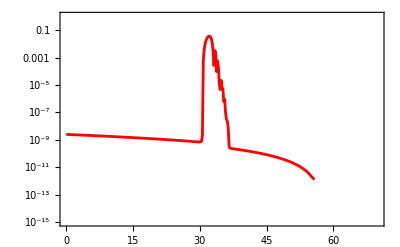

```mathematica
ListLogPlot[PN0,PlotRange->{{0,70},{10^-15,1}},Joined->True,Frame->True,PlotStyle->Red]
```

```mathematica
kmpc=Solve[0.05/Mpc==((a[Ne] H[Ne])/cs)/.solNe1/.Ne->0,Mpc][[1]][[1,2]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

549.29

```mathematica
Pkc=Table[{(kmpc((H[Ne]a[Ne])/cs)/.solNe1/.{Ne->NeHE[[i]]})[[1]],(k[[i]]^3/(2*Pi^2)*Abs[u[Ne]/(z[Ne]/.solNe1)]^2/.MSol[[i]]/.Ne->NeEnd[[i]])[[1]][[1]]},{i,1,iMax}]
```

{{0.05,2.44618×10^-9},{0.060974,2.43028×10^-9},{0.0743561,2.4143×10^-9},{0.0906748,2.39982×10^-9},{0.110574,2.3851×10^-9},{0.13484,2.36982×10^-9},{0.164431,2.35469×10^-9},{0.200514,2.33945×10^-9},{0.244514,2.3246×10^-9},{0.298167,2.30876×10^-9},{0.363592,2.29281×10^-9},{0.443369,2.27671×10^-9},{0.540649,2.26149×10^-9},{0.659268,2.24726×10^-9},{0.803909,2.23324×10^-9},{0.980278,2.21962×10^-9},{1.19533,2.20596×10^-9},{1.45756,2.1921×10^-9},{1.77731,2.17756×10^-9},{2.16718,2.16215×10^-9},{2.64256,2.14592×10^-9},{3.2222,2.12957×10^-9},{3.92896,2.11399×10^-9},{4.79072,2.09975×10^-9},{5.84145,2.08626×10^-9},{7.12259,2.07322×10^-9},{8.68467,2.06073×10^-9},{10.5893,2.04793×10^-9},{12.9115,2.0348×10^-9},{15.7428,2.02041×10^-9},{19.195,2.00502×10^-9},{23.4039,1.98889×10^-9},{28.5357,1.97297×10^-9},{34.7924,1.95825×10^-9},{42.4208,1.9449×10^-9},{51.7213,1.9321×10^-9},{63.0606,1.91991×10^-9},{76.8853,1.90805×10^-9},{93.7403,1.89587×10^-9},{114.289,1.88299×10^-9},{139.342,1.86894×10^-9},{169.886,1.8537×10^-9},{207.123,1.83788×10^-9},{252.521,1.82265×10^-9},{307.867,1.8089×10^-9},{375.34,1.79633×10^-9},{457.599,1.7842×10^-9},{557.881,1.77283×10^-9},{680.135,1.76152×10^-9},{829.174,1.74982×10^-9},{1010.86,1.73719×10^-9},{1232.36,1.72323×10^-9},{1502.38,1.70814×10^-9},{1831.54,1.6928×10^-9},{2232.81,1.67839×10^-9},{2721.97,1.66568×10^-9},{3318.28,1.65369×10^-9},{4045.18,1.64228×10^-9},{4931.29,1.63147×10^-9},{6011.45,1.62054×10^-9},{7328.16,1.60918×10^-9},{8933.2,1.59671×10^-9},{10889.7,1.58334×10^-9},{13274.6,1.56926×10^-9},{16181.7,1.55556×10^-9},{19725.3,1.54283×10^-9},{24044.6,1.5308×10^-9},{29309.6,1.51907×10^-9},{35727.2,1.5078×10^-9},{43549.5,1.49668×10^-9},{53084.1,1.4856×10^-9},{64705.7,1.47389×10^-9},{78870.8,1.4619×10^-9},{96136.2,1.44945×10^-9},{117180.,1.43678×10^-9},{142829.,1.42453×10^-9},{174091.,1.41269×10^-9},{212193.,1.40089×10^-9},{258632.,1.38923×10^-9},{315232.,1.37793×10^-9},{384215.,1.36668×10^-9},{468290.,1.35557×10^-9},{570756.,1.3445×10^-9},{695637.,1.33333×10^-9},{847834.,1.32203×10^-9},{1.03332×10^6,1.31053×10^-9},{1.25937×10^6,1.2989×10^-9},{1.53487×10^6,1.2873×10^-9},{1.87061×10^6,1.27588×10^-9},{2.27977×10^6,1.26468×10^-9},{2.77839×10^6,1.2536×10^-9},{3.38604×10^6,1.24269×10^-9},{4.12655×10^6,1.23195×10^-9},{5.02895×10^6,1.22131×10^-9},{6.12863×10^6,1.21075×10^-9},{7.46871×10^6,1.20016×10^-9},{9.1017×10^6,1.18953×10^-9},{1.10916×10^7,1.17872×10^-9},{1.35165×10^7,1.16777×10^-9},{1.64713×10^7,1.15671×10^-9},{2.00718×10^7,1.14571×10^-9},{2.44591×10^7,1.13495×10^-9},{2.9805×10^7,1.12446×10^-9},{3.63191×10^7,1.11407×10^-9},{4.42563×10^7,1.10391×10^-9},{5.39275×10^7,1.09393×10^-9},{6.57113×10^7,1.08403×10^-9},{8.00692×10^7,1.07411×10^-9},{9.75632×10^7,1.06421×10^-9},{1.18878×10^8,1.05405×10^-9},{1.44848×10^8,1.04373×10^-9},{1.76489×10^8,1.03312×10^-9},{2.15039×10^8,1.02241×10^-9},{2.62006×10^8,1.01183×10^-9},{3.19228×10^8,1.00166×10^-9},{3.88942×10^8,9.91863×10^-10},{4.73875×10^8,9.82229×10^-10},{5.77347×10^8,9.72981×10^-10},{7.03403×10^8,9.63942×10^-10},{8.56972×10^8,9.54964×10^-10},{1.04405×10^9,9.46015×10^-10},{1.27196×10^9,9.36632×10^-10},{1.5496×10^9,9.26658×10^-10},{1.88781×10^9,9.15997×10^-10},{2.2998×10^9,9.04659×10^-10},{2.80168×10^9,8.93518×10^-10},{3.41302×10^9,8.83768×10^-10},{4.15771×10^9,8.7561×10^-10},{5.0648×10^9,8.67788×10^-10},{6.16973×10^9,8.60165×10^-10},{7.51558×10^9,8.52527×10^-10},{9.15489×10^9,8.44428×10^-10},{1.11516×10^10,8.35705×10^-10},{1.35836×10^10,8.26207×10^-10},{1.65457×10^10,8.16188×10^-10},{2.01535×10^10,8.06924×10^-10},{2.45474×10^10,7.98886×10^-10},{2.98989×10^10,7.88491×10^-10},{3.64163×10^10,7.77739×10^-10},{4.43535×10^10,7.71485×10^-10},{5.40197×10^10,7.60095×10^-10},{6.57911×10^10,7.47023×10^-10},{8.0126×10^10,7.4003×10^-10},{9.75821×10^10,7.33521×10^-10},{1.18838×10^11,7.18268×10^-10},{1.4472×10^11,7.19533×10^-10},{1.76234×10^11,7.17878×10^-10},{2.14602×10^11,6.93536×10^-10},{2.61311×10^11,6.94894×10^-10},{3.18172×10^11,6.95594×10^-10},{3.87381×10^11,6.82798×10^-10},{4.71607×10^11,7.1149×10^-10},{5.74082×10^11,7.59817×10^-10},{6.98729×10^11,2.13624×10^-9},{8.50273×10^11,0.000592478},{1.03437×10^12,0.00398132},{1.25771×10^12,0.00973395},{1.52786×10^12,0.0173856},{1.85047×10^12,0.0242275},{2.17177×10^12,0.0317617},{2.56703×10^12,0.0347855},{3.06627×10^12,0.03667},{3.6881×10^12,0.0323576},{4.45513×10^12,0.0241602},{5.39576×10^12,0.0124578},{6.54507×10^12,0.00252149},{7.94669×10^12,0.000259447},{9.65408×10^12,0.00322229},{1.1732×10^13,0.00189539},{1.42597×10^13,0.0000947818},{1.7334×10^13,0.000574288},{2.10722×10^13,0.000190609},{2.56173×10^13,0.0000108336},{3.11428×10^13,4.58488×10^-6},{3.78595×10^13,0.0000215293},{4.60238×10^13,5.06297×10^-6},{5.59469×10^13,5.35872×10^-6},{6.80071×10^13,6.12456×10^-7},{8.26639×10^13,8.96654×10^-7},{1.00475×10^14,9.71711×10^-8},{1.22119×10^14,3.04135×10^-8},{1.48418×10^14,2.22602×10^-8},{1.80371×10^14,7.34915×10^-9},{2.19194×10^14,3.22271×10^-10},{2.6636×10^14,2.38746×10^-10},{3.23658×10^14,2.33842×10^-10},{3.93262×10^14,2.27619×10^-10},{4.77808×10^14,2.196×10^-10},{5.80497×10^14,2.17608×10^-10},{7.05217×10^14,2.1355×10^-10},{8.56681×10^14,2.07293×10^-10},{1.04062×10^15,2.05023×10^-10},{1.26396×10^15,1.98646×10^-10},{1.53516×10^15,1.95004×10^-10},{1.86441×10^15,1.90676×10^-10},{2.26414×10^15,1.86623×10^-10},{2.74939×10^15,1.81916×10^-10},{3.33842×10^15,1.78224×10^-10},{4.05336×10^15,1.73814×10^-10},{4.92104×10^15,1.69773×10^-10},{5.97404×10^15,1.65858×10^-10},{7.25181×10^15,1.61965×10^-10},{8.8022×10^15,1.58017×10^-10},{1.06832×10^16,1.53922×10^-10},{1.29652×10^16,1.50206×10^-10},{1.57332×10^16,1.4675×10^-10},{1.90906×10^16,1.42816×10^-10},{2.31625×10^16,1.38943×10^-10},{2.81003×10^16,1.35558×10^-10},{3.40876×10^16,1.32064×10^-10},{4.13468×10^16,1.28303×10^-10},{5.0147×10^16,1.2487×10^-10},{6.08141×10^16,1.21545×10^-10},{7.37428×10^16,1.18138×10^-10},{8.94106×10^16,1.14699×10^-10},{1.08396×10^17,1.11515×10^-10},{1.31397×10^17,1.08331×10^-10},{1.59261×10^17,1.05042×10^-10},{1.93011×10^17,1.01895×10^-10},{2.33884×10^17,9.89096×10^-11},{2.83378×10^17,9.58471×10^-11},{3.433×10^17,9.27733×10^-11},{4.15836×10^17,8.98764×10^-11},{5.0363×10^17,8.70144×10^-11},{6.0987×10^17,8.41184×10^-11},{7.38413×10^17,8.12984×10^-11},{8.93911×10^17,7.85814×10^-11},{1.08198×10^18,7.58748×10^-11},{1.30941×10^18,7.31821×10^-11},{1.58436×10^18,7.06056×10^-11},{1.91672×10^18,6.80597×10^-11},{2.31836×10^18,6.55258×10^-11},{2.80363×10^18,6.3038×10^-11},{3.3898×10^18,6.0657×10^-11},{4.09768×10^18,5.82859×10^-11},{4.9523×10^18,5.59189×10^-11},{5.98382×10^18,5.36777×10^-11},{7.2285×10^18,5.15012×10^-11},{8.72996×10^18,4.92878×10^-11},{1.05406×10^19,4.71243×10^-11},{1.27233×10^19,4.51064×10^-11},{1.53538×10^19,4.30902×10^-11},{1.85227×10^19,4.10197×10^-11},{2.23387×10^19,3.90864×10^-11},{2.69322×10^19,3.72672×10^-11},{3.2459×10^19,3.54005×10^-11},{3.9106×10^19,3.35357×10^-11},{4.70962×10^19,3.18556×10^-11},{5.66962×10^19,3.01902×10^-11},{6.82242×10^19,2.84893×10^-11},{8.20592×10^19,2.69001×10^-11},{9.86531×10^19,2.54395×10^-11},{1.18543×10^20,2.39172×10^-11},{1.42368×10^20,2.23569×10^-11},{1.70886×10^20,2.10027×10^-11},{2.04989×10^20,1.97222×10^-11},{2.45738×10^20,1.82882×10^-11},{2.94381×10^20,1.69066×10^-11},{3.52386×10^20,1.58161×10^-11},{4.21477×10^20,1.46583×10^-11},{5.03663×10^20,1.34433×10^-11},{6.01288×10^20,1.24392×10^-11},{7.17069×10^20,1.15505×10^-11},{8.54155×10^20,1.05405×10^-11},{1.01617×10^21,9.48705×10^-12},{1.20723×10^21,8.60584×10^-12},{1.43197×10^21,7.77396×10^-12},{1.69558×10^21,6.97651×10^-12},{2.00379×10^21,6.23774×10^-12},{2.36279×10^21,5.54067×10^-12},{2.77912×10^21,4.87412×10^-12},{3.25947×10^21,4.25861×10^-12},{3.81022×10^21,3.69779×10^-12},{4.43653×10^21,3.17159×10^-12},{5.1414×10^21,2.69704×10^-12},{5.92475×10^21,2.27657×10^-12},{6.77968×10^21,1.88547×10^-12},{7.69064×10^21,1.5892×10^-12},{8.62679×10^21,1.40312×10^-12},{9.53396×10^21,1.26249×10^-12}}

```mathematica
Export["PkA.dat",Pkc];
```

```mathematica
Pkc=Import["PkA.dat"];
c1=Interpolation[Pkc,InterpolationOrder->1]
AA=LogLogPlot[{c1[x]},{x,0.0634257151149378,6.242598573013641*^19},PlotRange->{{0.001,4*10^22},{10^-12,1}},Frame->True,FrameStyle->Thick,FrameTicksStyle->Black,PlotStyle->{Purple},LabelStyle->Directive[24,Bold,Black,FontFamily->"Book Antiqua"],ImageSize->{600,400},AspectRatio->Full,RotateLabel->False,Axes->False,FrameLabel->{"K/Mpc^-1","P_s"}]
```

InterpolatingFunction[…]

```mathematica
InterpolatingFunction[…];
```

```mathematica
c1[0.05kmpc]
```

1.97629×10^-9

```mathematica
AA=ListLogLogPlot[Pkc,PlotRange->{{0.05,4*10^22},{10^-13,1}},Joined->True,Frame->True,FrameStyle->Thick,FrameTicksStyle->Black,PlotStyle->Red,LabelStyle->Directive[24,Bold,Black,FontFamily->"Book Antiqua"],ImageSize->{600,400},AspectRatio->Full,RotateLabel->False,Axes->False,FrameLabel->{"K/Mpc^-1","P_R"}]
```

```mathematica
ss=-Graphics-;
```

```mathematica
fback=Show[{LogLogPlot[{ns0[Ne]},{Ne,1,10},PlotRange->{{10^-4,10^24},{10^-12,10^0}},PlotStyle->{Black,Thickness[0.005]},Frame-> True,FrameLabel->{"M/M_⊙","f_Pbh"},LabelStyle->Directive[22,Bold,FontFamily->"Book Antiqua"],ImageSize->{600,400},AspectRatio->Full],Graphics[{Texture[ss],EdgeForm[Black],Polygon[{{-9.1,-27.56},{55.2,-27.56},{55.2,0.1},{-9.1,0.1}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},ImageSize->{600,400},AspectRatio->Full]},Axes->False,RotateLabel->True]
```

```mathematica
Show[fback,AA]
```

```mathematica
Mkc=Table[(1/((1.9*10^6)^-2)*(1/(√3))^3/0.2*(106.75/10.75)^(-1/6)*(kmpc*k[[i]])^-2)[[1]],{i,1,iMax}];
```

```mathematica
PRc=Interpolation[Pkc,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
qend=PRc[[1,1,2]]
```

9.53396×10^21

```mathematica
LogLogPlot[PRc[x],{x,0.05,qend},PlotRange->All]
```

```mathematica
For[i=1,i≤ iMax,i++,
si[i]=NIntegrate[16/81*1/q*(q/(k[[i]]*kmpc))^4 Exp[-q^2/(k[[i]]*kmpc)^2]PRc[q],{q,0,PRc[[1,1,2]]}];
]
```

```mathematica
Beep[]
```

```mathematica
sigma=Table[si[i],{i,1,iMax}]//N;
```

```mathematica
δc=0.4;
```

```mathematica
(*For[i=1,i≤ iMax,i++,
B[i]=√(1/(2Pi))(sigma[[i]])^(1/2)/δc Exp[(- δc^2)/(2*sigma[[i]])]]*)
```

```mathematica
For[i=1,i≤ iMax,i++,
B[i]=1/2 Erfc[δc/(√(2*sigma[[i]]))]]
```

```mathematica
f=Table[B[i]/(1.84*10^-8)*((1/(√3))^3/0.2)^(3/2)*(10.75/106.75)^(1/4)*(Mkc[[i]])^(-1/2),{i,1,iMax}];
```

```mathematica
ac=Table[{Mkc[[i]],f[[i]][[1]]},{i,1,iMax}];
```

```mathematica
Export["FPBHA.dat",ac];
```

```mathematica
ac=Import["FPBHA.dat"];
```

```mathematica
Max[f]
```

0.996384

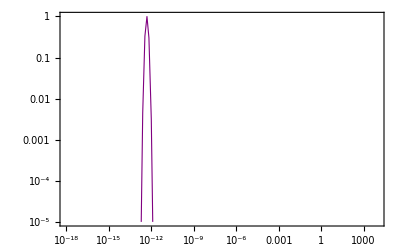

```mathematica
fc=ListLogLogPlot[ac,Joined->True,Frame->True,Axes->False,PlotRange->{{10^-18,10^4},{10^-5,1}},PlotStyle->{Purple,Thickness[0.002]}]
```

InterpolatingFunction[…]

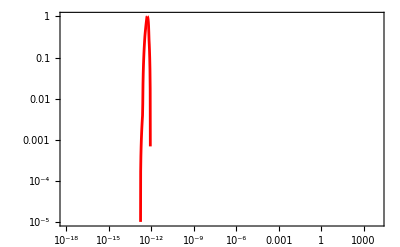

```mathematica
s1=Interpolation[ac,InterpolationOrder->2]
fc=LogLogPlot[s1[x],{x,3.86*^-39,7.0121*^14},Frame->True,Axes->False,PlotRange->{{10^-18,10^4},{10^-5,10^0}},PlotStyle->Red,FillingStyle->Black,ImageSize->{400,300}]
```

```mathematica
fb=-Graphics-;
```

```mathematica
fback=Show[{LogLogPlot[{ns0[Ne]},{Ne,1,10},PlotRange->{{10^-18,10^4},{10^-5,10^0}},PlotStyle->{Black,Thickness[0.005]},Frame-> True,FrameLabel->{"M/M_⊙","f_Pbh"},LabelStyle->Directive[22,Bold,FontFamily->"Book Antiqua"],ImageSize->{600,400},AspectRatio->Full],Graphics[{Texture[fb],EdgeForm[Black],Polygon[{{-41.5,-11.55},{9.3,-11.55},{9.3,0},{-41.5,0}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},ImageSize->{600,400},AspectRatio->Full]},Axes->False,RotateLabel->True]
```

```mathematica
fpbh=Show[fback,fc,ImageSize->{600,400}]
```

```mathematica
Show[back,fc,ImageSize->{600,400}]
```

```mathematica
data2=Table[{i,(kmpc((a[Ne] H[Ne])/cs)/.solNe1/.{Ne->NeHE[[i]]})[[1]],NeHE[[i]],NeBD[[i]],Mkc[[i]],PN0[[i]][[2]],f[[i]]},{i,1,iMax}];
```

```mathematica
pr=data2[[All,6]];
```

```mathematica
Position[pr,Max[pr]][[1]][[1]]
```

162

```mathematica
Length[Pkc]
```

280

```mathematica
Pkpeak=Pkc[[Position[pr,Max[pr]][[1]][[1]],2]]
```

0.03667

```mathematica
Mkc[[Position[pr,Max[pr]][[1]][[1]]]]
```

2.52008×10^-13

```mathematica
f[[Position[pr,Max[pr]][[1]][[1]]]]
```

{0.00451995}

```mathematica
mytab2=Text@Grid[Prepend[data2,{"i","K","N","NBD","M(k)/M_o","P_R","f"}],Frame->All,Alignment->{Center},ItemSize->{10},Frame->Darker[Gray,.6],ItemStyle->14,Background->{Automatic,{1-> Green,Position[pr,Max[pr]][[1]][[1]]+1->Yellow}}]
```

i | K | N | NBD | M(k)/M_o | P_R | f
1 | 0.05 | 0. | -5. | 9.47754×10^14 | 2.44618×10^-9 | {0.}
2 | 0.060974 | 0.2 | -4.8 | 6.37304×10^14 | 2.43028×10^-9 | {0.}
3 | 0.0743561 | 0.4 | -4.6 | 4.28551×10^14 | 2.4143×10^-9 | {0.}
4 | 0.0906748 | 0.6 | -4.4 | 2.88179×10^14 | 2.39982×10^-9 | {0.}
5 | 0.110574 | 0.8 | -4.2 | 1.93788×10^14 | 2.3851×10^-9 | {0.}
6 | 0.13484 | 1. | -4. | 1.30315×10^14 | 2.36982×10^-9 | {0.}
7 | 0.164431 | 1.2 | -3.8 | 8.76332×10^13 | 2.35469×10^-9 | {0.}
8 | 0.200514 | 1.4 | -3.6 | 5.89314×10^13 | 2.33945×10^-9 | {0.}
9 | 0.244514 | 1.6 | -3.4 | 3.96305×10^13 | 2.3246×10^-9 | {0.}
10 | 0.298167 | 1.8 | -3.2 | 2.66512×10^13 | 2.30876×10^-9 | {0.}
11 | 0.363592 | 2. | -3. | 1.79229×10^13 | 2.29281×10^-9 | {0.}
12 | 0.443369 | 2.2 | -2.8 | 1.20533×10^13 | 2.27671×10^-9 | {0.}
13 | 0.540649 | 2.4 | -2.6 | 8.10598×10^12 | 2.26149×10^-9 | {0.}
14 | 0.659268 | 2.6 | -2.4 | 5.45144×10^12 | 2.24726×10^-9 | {0.}
15 | 0.803909 | 2.8 | -2.2 | 3.66624×10^12 | 2.23324×10^-9 | {0.}
16 | 0.980278 | 3. | -2. | 2.46568×10^12 | 2.21962×10^-9 | {0.}
17 | 1.19533 | 3.2 | -1.8 | 1.65828×10^12 | 2.20596×10^-9 | {0.}
18 | 1.45756 | 3.4 | -1.6 | 1.11527×10^12 | 2.1921×10^-9 | {0.}
19 | 1.77731 | 3.6 | -1.4 | 7.50086×10^11 | 2.17756×10^-9 | {0.}
20 | 2.16718 | 3.8 | -1.2 | 5.04482×10^11 | 2.16215×10^-9 | {0.}
21 | 2.64256 | 4. | -1. | 3.39301×10^11 | 2.14592×10^-9 | {0.}
22 | 3.2222 | 4.2 | -0.8 | 2.28208×10^11 | 2.12957×10^-9 | {0.}
23 | 3.92896 | 4.4 | -0.6 | 1.5349×10^11 | 2.11399×10^-9 | {0.}
24 | 4.79072 | 4.6 | -0.4 | 1.03237×10^11 | 2.09975×10^-9 | {0.}
25 | 5.84145 | 4.8 | -0.2 | 6.94375×10^10 | 2.08626×10^-9 | {0.}
26 | 7.12259 | 5. | 0. | 4.67045×10^10 | 2.07322×10^-9 | {0.}
27 | 8.68467 | 5.2 | 0.2 | 3.14144×10^10 | 2.06073×10^-9 | {0.}
28 | 10.5893 | 5.4 | 0.4 | 2.11302×10^10 | 2.04793×10^-9 | {0.}
29 | 12.9115 | 5.6 | 0.6 | 1.4213×10^10 | 2.0348×10^-9 | {0.}
30 | 15.7428 | 5.8 | 0.8 | 9.56027×10^9 | 2.02041×10^-9 | {0.}
31 | 19.195 | 6. | 1. | 6.43074×10^9 | 2.00502×10^-9 | {0.}
32 | 23.4039 | 6.2 | 1.2 | 4.32571×10^9 | 1.98889×10^-9 | {0.}
33 | 28.5357 | 6.4 | 1.4 | 2.90977×10^9 | 1.97297×10^-9 | {0.}
34 | 34.7924 | 6.6 | 1.6 | 1.95734×10^9 | 1.95825×10^-9 | {0.}
35 | 42.4208 | 6.8 | 1.8 | 1.31667×10^9 | 1.9449×10^-9 | {0.}
36 | 51.7213 | 7. | 2. | 8.85719×10^8 | 1.9321×10^-9 | {0.}
37 | 63.0606 | 7.2 | 2.2 | 5.95826×10^8 | 1.91991×10^-9 | {0.}
38 | 76.8853 | 7.4 | 2.4 | 4.00819×10^8 | 1.90805×10^-9 | {0.}
39 | 93.7403 | 7.6 | 2.6 | 2.69639×10^8 | 1.89587×10^-9 | {0.}
40 | 114.289 | 7.8 | 2.8 | 1.81394×10^8 | 1.88299×10^-9 | {0.}
41 | 139.342 | 8. | 3. | 1.22031×10^8 | 1.86894×10^-9 | {0.}
42 | 169.886 | 8.2 | 3.2 | 8.20958×10^7 | 1.8537×10^-9 | {0.}
43 | 207.123 | 8.4 | 3.4 | 5.52304×10^7 | 1.83788×10^-9 | {0.}
44 | 252.521 | 8.6 | 3.6 | 3.71571×10^7 | 1.82265×10^-9 | {0.}
45 | 307.867 | 8.8 | 3.8 | 2.49983×10^7 | 1.8089×10^-9 | {0.}
46 | 375.34 | 9. | 4. | 1.68184×10^7 | 1.79633×10^-9 | {0.}
47 | 457.599 | 9.2 | 4.2 | 1.13153×10^7 | 1.7842×10^-9 | {0.}
48 | 557.881 | 9.4 | 4.4 | 7.61295×10^6 | 1.77283×10^-9 | {0.}
49 | 680.135 | 9.6 | 4.6 | 5.12207×10^6 | 1.76152×10^-9 | {0.}
50 | 829.174 | 9.8 | 4.8 | 3.44623×10^6 | 1.74982×10^-9 | {0.}
51 | 1010.86 | 10. | 5. | 2.31873×10^6 | 1.73719×10^-9 | {0.}
52 | 1232.36 | 10.2 | 5.2 | 1.56013×10^6 | 1.72323×10^-9 | {0.}
53 | 1502.38 | 10.4 | 5.4 | 1.04973×10^6 | 1.70814×10^-9 | {0.}
54 | 1831.54 | 10.6 | 5.6 | 706320. | 1.6928×10^-9 | {0.}
55 | 2232.81 | 10.8 | 5.8 | 475260. | 1.67839×10^-9 | {0.}
56 | 2721.97 | 11. | 6. | 319792. | 1.66568×10^-9 | {0.}
57 | 3318.28 | 11.2 | 6.2 | 215184. | 1.65369×10^-9 | {0.}
58 | 4045.18 | 11.4 | 6.4 | 144797. | 1.64228×10^-9 | {0.}
59 | 4931.29 | 11.6 | 6.6 | 97435. | 1.63147×10^-9 | {0.}
60 | 6011.45 | 11.8 | 6.8 | 65565.7 | 1.62054×10^-9 | {0.}
61 | 7328.16 | 12. | 7. | 44121. | 1.60918×10^-9 | {0.}
62 | 8933.2 | 12.2 | 7.2 | 29690.7 | 1.59671×10^-9 | {0.}
63 | 10889.7 | 12.4 | 7.4 | 19980.3 | 1.58334×10^-9 | {0.}
64 | 13274.6 | 12.6 | 7.6 | 13446. | 1.56926×10^-9 | {0.}
65 | 16181.7 | 12.8 | 7.8 | 9048.72 | 1.55556×10^-9 | {0.}
66 | 19725.3 | 13. | 8. | 6089.61 | 1.54283×10^-9 | {0.}
67 | 24044.6 | 13.2 | 8.2 | 4098.25 | 1.5308×10^-9 | {0.}
68 | 29309.6 | 13.4 | 8.4 | 2758.13 | 1.51907×10^-9 | {0.}
69 | 35727.2 | 13.6 | 8.6 | 1856.26 | 1.5078×10^-9 | {0.}
70 | 43549.5 | 13.8 | 8.8 | 1249.31 | 1.49668×10^-9 | {0.}
71 | 53084.1 | 14. | 9. | 840.826 | 1.4856×10^-9 | {0.}
72 | 64705.7 | 14.2 | 9.2 | 565.914 | 1.47389×10^-9 | {0.}
73 | 78870.8 | 14.4 | 9.4 | 380.893 | 1.4619×10^-9 | {0.}
74 | 96136.2 | 14.6 | 9.6 | 256.367 | 1.44945×10^-9 | {0.}
75 | 117180. | 14.8 | 9.8 | 172.555 | 1.43678×10^-9 | {0.}
76 | 142829. | 15. | 10. | 116.146 | 1.42453×10^-9 | {0.}
77 | 174091. | 15.2 | 10.2 | 78.1779 | 1.41269×10^-9 | {0.}
78 | 212193. | 15.4 | 10.4 | 52.6227 | 1.40089×10^-9 | {0.}
79 | 258632. | 15.6 | 10.6 | 35.4217 | 1.38923×10^-9 | {0.}
80 | 315232. | 15.8 | 10.8 | 23.8437 | 1.37793×10^-9 | {0.}
81 | 384215. | 16. | 11. | 16.0504 | 1.36668×10^-9 | {0.}
82 | 468290. | 16.2 | 11.2 | 10.8045 | 1.35557×10^-9 | {0.}
83 | 570756. | 16.4 | 11.4 | 7.27334 | 1.3445×10^-9 | {0.}
84 | 695637. | 16.6 | 11.6 | 4.89632 | 1.33333×10^-9 | {0.}
85 | 847834. | 16.8 | 11.8 | 3.2962 | 1.32203×10^-9 | {0.}
86 | 1.03332×10^6 | 17. | 12. | 2.21904 | 1.31053×10^-9 | {0.}
87 | 1.25937×10^6 | 17.2 | 12.2 | 1.49391 | 1.2989×10^-9 | {0.}
88 | 1.53487×10^6 | 17.4 | 12.4 | 1.00576 | 1.2873×10^-9 | {0.}
89 | 1.87061×10^6 | 17.6 | 12.6 | 0.677127 | 1.27588×10^-9 | {0.}
90 | 2.27977×10^6 | 17.8 | 12.8 | 0.455885 | 1.26468×10^-9 | {0.}
91 | 2.77839×10^6 | 18. | 13. | 0.306937 | 1.2536×10^-9 | {0.}
92 | 3.38604×10^6 | 18.2 | 13.2 | 0.206657 | 1.24269×10^-9 | {0.}
93 | 4.12655×10^6 | 18.4 | 13.4 | 0.139143 | 1.23195×10^-9 | {0.}
94 | 5.02895×10^6 | 18.6 | 13.6 | 0.0936872 | 1.22131×10^-9 | {0.}
95 | 6.12863×10^6 | 18.8 | 13.8 | 0.0630824 | 1.21075×10^-9 | {0.}
96 | 7.46871×10^6 | 19. | 14. | 0.0424761 | 1.20016×10^-9 | {0.}
97 | 9.1017×10^6 | 19.2 | 14.2 | 0.0286016 | 1.18953×10^-9 | {0.}
98 | 1.10916×10^7 | 19.4 | 14.4 | 0.0192595 | 1.17872×10^-9 | {0.}
99 | 1.35165×10^7 | 19.6 | 14.6 | 0.0129691 | 1.16777×10^-9 | {0.}
100 | 1.64713×10^7 | 19.8 | 14.8 | 0.00873336 | 1.15671×10^-9 | {0.}
101 | 2.00718×10^7 | 20. | 15. | 0.00588117 | 1.14571×10^-9 | {0.}
102 | 2.44591×10^7 | 20.2 | 15.2 | 0.00396054 | 1.13495×10^-9 | {0.}
103 | 2.9805×10^7 | 20.4 | 15.4 | 0.0026672 | 1.12446×10^-9 | {0.}
104 | 3.63191×10^7 | 20.6 | 15.6 | 0.00179625 | 1.11407×10^-9 | {0.}
105 | 4.42563×10^7 | 20.8 | 15.8 | 0.00120972 | 1.10391×10^-9 | {0.}
106 | 5.39275×10^7 | 21. | 16. | 0.000814733 | 1.09393×10^-9 | {0.}
107 | 6.57113×10^7 | 21.2 | 16.2 | 0.000548725 | 1.08403×10^-9 | {0.}
108 | 8.00692×10^7 | 21.4 | 16.4 | 0.000369576 | 1.07411×10^-9 | {0.}
109 | 9.75632×10^7 | 21.6 | 16.6 | 0.000248922 | 1.06421×10^-9 | {0.}
110 | 1.18878×10^8 | 21.8 | 16.8 | 0.000167661 | 1.05405×10^-9 | {0.}
111 | 1.44848×10^8 | 22. | 17. | 0.000112931 | 1.04373×10^-9 | {0.}
112 | 1.76489×10^8 | 22.2 | 17.2 | 0.000076068 | 1.03312×10^-9 | {0.}
113 | 2.15039×10^8 | 22.4 | 17.4 | 0.0000512392 | 1.02241×10^-9 | {0.}
114 | 2.62006×10^8 | 22.6 | 17.6 | 0.0000345154 | 1.01183×10^-9 | {0.}
115 | 3.19228×10^8 | 22.8 | 17.8 | 0.0000232506 | 1.00166×10^-9 | {0.}
116 | 3.88942×10^8 | 23. | 18. | 0.0000156627 | 9.91863×10^-10 | {0.}
117 | 4.73875×10^8 | 23.2 | 18.2 | 0.0000105514 | 9.82229×10^-10 | {0.}
118 | 5.77347×10^8 | 23.4 | 18.4 | 7.10824×10^-6 | 9.72981×10^-10 | {0.}
119 | 7.03403×10^8 | 23.6 | 18.6 | 4.7888×10^-6 | 9.63942×10^-10 | {0.}
120 | 8.56972×10^8 | 23.8 | 18.8 | 3.22628×10^-6 | 9.54964×10^-10 | {0.}
121 | 1.04405×10^9 | 24. | 19. | 2.17365×10^-6 | 9.46015×10^-10 | {0.}
122 | 1.27196×10^9 | 24.2 | 19.2 | 1.4645×10^-6 | 9.36632×10^-10 | {0.}
123 | 1.5496×10^9 | 24.4 | 19.4 | 9.8673×10^-7 | 9.26658×10^-10 | {0.}
124 | 1.88781×10^9 | 24.6 | 19.6 | 6.64844×10^-7 | 9.15997×10^-10 | {0.}
125 | 2.2998×10^9 | 24.8 | 19.8 | 4.47975×10^-7 | 9.04659×10^-10 | {0.}
126 | 2.80168×10^9 | 25. | 20. | 3.01856×10^-7 | 8.93518×10^-10 | {0.}
127 | 3.41302×10^9 | 25.2 | 20.2 | 2.03403×10^-7 | 8.83768×10^-10 | {0.}
128 | 4.15771×10^9 | 25.4 | 20.4 | 1.37065×10^-7 | 8.7561×10^-10 | {0.}
129 | 5.0648×10^9 | 25.6 | 20.6 | 9.23656×10^-8 | 8.67788×10^-10 | {0.}
130 | 6.16973×10^9 | 25.8 | 20.8 | 6.22449×10^-8 | 8.60165×10^-10 | {0.}
131 | 7.51558×10^9 | 26. | 21. | 4.19479×10^-8 | 8.52527×10^-10 | {0.}
132 | 9.15489×10^9 | 26.2 | 21.2 | 2.82702×10^-8 | 8.44428×10^-10 | {0.}
133 | 1.11516×10^10 | 26.4 | 21.4 | 1.90529×10^-8 | 8.35705×10^-10 | {0.}
134 | 1.35836×10^10 | 26.6 | 21.6 | 1.28412×10^-8 | 8.26207×10^-10 | {0.}
135 | 1.65457×10^10 | 26.8 | 21.8 | 8.65493×10^-9 | 8.16188×10^-10 | {0.}
136 | 2.01535×10^10 | 27. | 22. | 5.8336×10^-9 | 8.06924×10^-10 | {0.}
137 | 2.45474×10^10 | 27.2 | 22.2 | 3.93209×10^-9 | 7.98886×10^-10 | {0.}
138 | 2.98989×10^10 | 27.4 | 22.4 | 2.65049×10^-9 | 7.88491×10^-10 | {0.}
139 | 3.64163×10^10 | 27.6 | 22.6 | 1.78667×10^-9 | 7.77739×10^-10 | {0.}
140 | 4.43535×10^10 | 27.8 | 22.8 | 1.20442×10^-9 | 7.71485×10^-10 | {0.}
141 | 5.40197×10^10 | 28. | 23. | 8.11954×10^-10 | 7.60095×10^-10 | {0.}
142 | 6.57911×10^10 | 28.2 | 23.2 | 5.47396×10^-10 | 7.47023×10^-10 | {0.}
143 | 8.0126×10^10 | 28.4 | 23.4 | 3.69053×10^-10 | 7.4003×10^-10 | {0.}
144 | 9.75821×10^10 | 28.6 | 23.6 | 2.48826×10^-10 | 7.33521×10^-10 | {0.}
145 | 1.18838×10^11 | 28.8 | 23.8 | 1.67774×10^-10 | 7.18268×10^-10 | {0.}
146 | 1.4472×10^11 | 29. | 24. | 1.13129×10^-10 | 7.19533×10^-10 | {0.}
147 | 1.76234×10^11 | 29.2 | 24.2 | 7.62879×10^-11 | 7.17878×10^-10 | {0.}
148 | 2.14602×10^11 | 29.4 | 24.4 | 5.1448×10^-11 | 6.93536×10^-10 | {0.}
149 | 2.61311×10^11 | 29.6 | 24.6 | 3.46992×10^-11 | 6.94894×10^-10 | {0.}
150 | 3.18172×10^11 | 29.8 | 24.8 | 2.34052×10^-11 | 6.95594×10^-10 | {0.}
151 | 3.87381×10^11 | 30. | 25. | 1.57891×10^-11 | 6.82798×10^-10 | {0.}
152 | 4.71607×10^11 | 30.2 | 25.2 | 1.06531×10^-11 | 7.1149×10^-10 | {0.}
153 | 5.74082×10^11 | 30.4 | 25.4 | 7.18931×10^-12 | 7.59817×10^-10 | {2.22056×10^-177}
154 | 6.98729×10^11 | 30.6 | 25.6 | 4.85309×10^-12 | 2.13624×10^-9 | {1.41309×10^-70}
155 | 8.50273×10^11 | 30.8 | 25.8 | 3.27732×10^-12 | 0.000592478 | {4.09512×10^-32}
156 | 1.03437×10^12 | 31. | 26. | 2.21455×10^-12 | 0.00398132 | {1.75398×10^-15}
157 | 1.25771×10^12 | 31.2 | 26.2 | 1.49787×10^-12 | 0.00973395 | {2.23627×10^-7}
158 | 1.52786×10^12 | 31.4 | 26.4 | 1.015×10^-12 | 0.0173856 | {0.00319033}
159 | 1.85047×10^12 | 31.6 | 26.6 | 6.91946×10^-13 | 0.0242275 | {0.301772}
160 | 2.17177×10^12 | 31.8 | 26.8 | 5.0235×10^-13 | 0.0317617 | {0.996384}
161 | 2.56703×10^12 | 32. | 27. | 3.59562×10^-13 | 0.0347855 | {0.332369}
162 | 3.06627×10^12 | 32.2 | 27.2 | 2.52008×10^-13 | 0.03667 | {0.00451995}
163 | 3.6881×10^12 | 32.4 | 27.4 | 1.74193×10^-13 | 0.0323576 | {3.89861×10^-7}
164 | 4.45513×10^12 | 32.6 | 27.6 | 1.19375×10^-13 | 0.0241602 | {9.19447×10^-15}
165 | 5.39576×10^12 | 32.8 | 27.8 | 8.13823×10^-14 | 0.0124578 | {5.87634×10^-28}
166 | 6.54507×10^12 | 33. | 28. | 5.53104×10^-14 | 0.00252149 | {1.42614×10^-49}
167 | 7.94669×10^12 | 33.2 | 28.2 | 3.752×10^-14 | 0.000259447 | {1.66424×10^-84}
168 | 9.65408×10^12 | 33.4 | 28.4 | 2.54222×10^-14 | 0.00322229 | {6.82436×10^-142}
169 | 1.1732×10^13 | 33.6 | 28.6 | 1.72145×10^-14 | 0.00189539 | {9.67924×10^-239}
170 | 1.42597×10^13 | 33.8 | 28.8 | 1.16523×10^-14 | 0.0000947818 | {0.}
171 | 1.7334×10^13 | 34. | 29. | 7.88566×10^-15 | 0.000574288 | {0.}
172 | 2.10722×10^13 | 34.2 | 29.2 | 5.33597×10^-15 | 0.000190609 | {0.}
173 | 2.56173×10^13 | 34.4 | 29.4 | 3.61051×10^-15 | 0.0000108336 | {0.}
174 | 3.11428×10^13 | 34.6 | 29.6 | 2.44299×10^-15 | 4.58488×10^-6 | {0.}
175 | 3.78595×10^13 | 34.8 | 29.8 | 1.65305×10^-15 | 0.0000215293 | {0.}
176 | 4.60238×10^13 | 35. | 30. | 1.11859×10^-15 | 5.06297×10^-6 | {0.}
177 | 5.59469×10^13 | 35.2 | 30.2 | 7.56978×10^-16 | 5.35872×10^-6 | {0.}
178 | 6.80071×10^13 | 35.4 | 30.4 | 5.12303×10^-16 | 6.12456×10^-7 | {0.}
179 | 8.26639×10^13 | 35.6 | 30.6 | 3.4674×10^-16 | 8.96654×10^-7 | {0.}
180 | 1.00475×10^14 | 35.8 | 30.8 | 2.34702×10^-16 | 9.71711×10^-8 | {0.}
181 | 1.22119×10^14 | 36. | 31. | 1.58881×10^-16 | 3.04135×10^-8 | {0.}
182 | 1.48418×10^14 | 36.2 | 31.2 | 1.07563×10^-16 | 2.22602×10^-8 | {0.}
183 | 1.80371×10^14 | 36.4 | 31.4 | 7.28282×10^-17 | 7.34915×10^-9 | {0.}
184 | 2.19194×10^14 | 36.6 | 31.6 | 4.93148×10^-17 | 3.22271×10^-10 | {0.}
185 | 2.6636×10^14 | 36.8 | 31.8 | 3.33963×10^-17 | 2.38746×10^-10 | {0.}
186 | 3.23658×10^14 | 37. | 32. | 2.26184×10^-17 | 2.33842×10^-10 | {0.}
187 | 3.93262×10^14 | 37.2 | 32.2 | 1.53205×10^-17 | 2.27619×10^-10 | {0.}
188 | 4.77808×10^14 | 37.4 | 32.4 | 1.03784×10^-17 | 2.196×10^-10 | {0.}
189 | 5.80497×10^14 | 37.6 | 32.6 | 7.03129×10^-18 | 2.17608×10^-10 | {0.}
190 | 7.05217×10^14 | 37.8 | 32.8 | 4.7642×10^-18 | 2.1355×10^-10 | {0.}
191 | 8.56681×10^14 | 38. | 33. | 3.22847×10^-18 | 2.07293×10^-10 | {0.}
192 | 1.04062×10^15 | 38.2 | 33.2 | 2.18804×10^-18 | 2.05023×10^-10 | {0.}
193 | 1.26396×10^15 | 38.4 | 33.4 | 1.48309×10^-18 | 1.98646×10^-10 | {0.}
194 | 1.53516×10^15 | 38.6 | 33.6 | 1.00538×10^-18 | 1.95004×10^-10 | {0.}
195 | 1.86441×10^15 | 38.8 | 33.8 | 6.81633×10^-19 | 1.90676×10^-10 | {0.}
196 | 2.26414×10^15 | 39. | 34. | 4.62197×10^-19 | 1.86623×10^-10 | {0.}
197 | 2.74939×10^15 | 39.2 | 34.2 | 3.13445×10^-19 | 1.81916×10^-10 | {0.}
198 | 3.33842×10^15 | 39.4 | 34.4 | 2.12595×10^-19 | 1.78224×10^-10 | {0.}
199 | 4.05336×10^15 | 39.6 | 34.6 | 1.44214×10^-19 | 1.73814×10^-10 | {0.}
200 | 4.92104×10^15 | 39.8 | 34.8 | 9.78411×10^-20 | 1.69773×10^-10 | {0.}
201 | 5.97404×10^15 | 40. | 35. | 6.63896×10^-20 | 1.65858×10^-10 | {0.}
202 | 7.25181×10^15 | 40.2 | 35.2 | 4.5055×10^-20 | 1.61965×10^-10 | {0.}
203 | 8.8022×10^15 | 40.4 | 35.4 | 3.05811×10^-20 | 1.58017×10^-10 | {0.}
204 | 1.06832×10^16 | 40.6 | 35.6 | 2.07602×10^-20 | 1.53922×10^-10 | {0.}
205 | 1.29652×10^16 | 40.8 | 35.8 | 1.40955×10^-20 | 1.50206×10^-10 | {0.}
206 | 1.57332×10^16 | 41. | 36. | 9.57196×10^-21 | 1.4675×10^-10 | {0.}
207 | 1.90906×10^16 | 41.2 | 36.2 | 6.50123×10^-21 | 1.42816×10^-10 | {0.}
208 | 2.31625×10^16 | 41.4 | 36.4 | 4.41637×10^-21 | 1.38943×10^-10 | {0.}
209 | 2.81003×10^16 | 41.6 | 36.6 | 3.00064×10^-21 | 1.35558×10^-10 | {0.}
210 | 3.40876×10^16 | 41.8 | 36.8 | 2.03912×10^-21 | 1.32064×10^-10 | {0.}
211 | 4.13468×10^16 | 42. | 37. | 1.38596×10^-21 | 1.28303×10^-10 | {0.}
212 | 5.0147×10^16 | 42.2 | 37.2 | 9.42207×10^-22 | 1.2487×10^-10 | {0.}
213 | 6.08141×10^16 | 42.4 | 37.4 | 6.40659×10^-22 | 1.21545×10^-10 | {0.}
214 | 7.37428×10^16 | 42.6 | 37.6 | 4.35709×10^-22 | 1.18138×10^-10 | {0.}
215 | 8.94106×10^16 | 42.8 | 37.8 | 2.96386×10^-22 | 1.14699×10^-10 | {0.}
216 | 1.08396×10^17 | 43. | 38. | 2.01657×10^-22 | 1.11515×10^-10 | {0.}
217 | 1.31397×10^17 | 43.2 | 38.2 | 1.37235×10^-22 | 1.08331×10^-10 | {0.}
218 | 1.59261×10^17 | 43.4 | 38.4 | 9.34149×10^-23 | 1.05042×10^-10 | {0.}
219 | 1.93011×10^17 | 43.6 | 38.6 | 6.36021×10^-23 | 1.01895×10^-10 | {0.}
220 | 2.33884×10^17 | 43.8 | 38.8 | 4.33145×10^-23 | 9.89096×10^-11 | {0.}
221 | 2.83378×10^17 | 44. | 39. | 2.95056×10^-23 | 9.58471×10^-11 | {0.}
222 | 3.433×10^17 | 44.2 | 39.2 | 2.01043×10^-23 | 9.27733×10^-11 | {0.}
223 | 4.15836×10^17 | 44.4 | 39.4 | 1.37022×10^-23 | 8.98764×10^-11 | {0.}
224 | 5.0363×10^17 | 44.6 | 39.6 | 9.34142×10^-24 | 8.70144×10^-11 | {0.}
225 | 6.0987×10^17 | 44.8 | 39.8 | 6.37031×10^-24 | 8.41184×10^-11 | {0.}
226 | 7.38413×10^17 | 45. | 40. | 4.34547×10^-24 | 8.12984×10^-11 | {0.}
227 | 8.93911×10^17 | 45.2 | 40.2 | 2.96515×10^-24 | 7.85814×10^-11 | {0.}
228 | 1.08198×10^18 | 45.4 | 40.4 | 2.02393×10^-24 | 7.58748×10^-11 | {0.}
229 | 1.30941×10^18 | 45.6 | 40.6 | 1.38193×10^-24 | 7.31821×10^-11 | {0.}
230 | 1.58436×10^18 | 45.8 | 40.8 | 9.43899×10^-25 | 7.06056×10^-11 | {0.}
231 | 1.91672×10^18 | 46. | 41. | 6.4494×10^-25 | 6.80597×10^-11 | {0.}
232 | 2.31836×10^18 | 46.2 | 41.2 | 4.40832×10^-25 | 6.55258×10^-11 | {0.}
233 | 2.80363×10^18 | 46.4 | 41.4 | 3.01435×10^-25 | 6.3038×10^-11 | {0.}
234 | 3.3898×10^18 | 46.6 | 41.6 | 2.06199×10^-25 | 6.0657×10^-11 | {0.}
235 | 4.09768×10^18 | 46.8 | 41.8 | 1.41111×10^-25 | 5.82859×10^-11 | {0.}
236 | 4.9523×10^18 | 47. | 42. | 9.66098×10^-26 | 5.59189×10^-11 | {0.}
237 | 5.98382×10^18 | 47.2 | 42.2 | 6.61726×10^-26 | 5.36777×10^-11 | {0.}
238 | 7.2285×10^18 | 47.4 | 42.4 | 4.5346×10^-26 | 5.15012×10^-11 | {0.}
239 | 8.72996×10^18 | 47.6 | 42.6 | 3.10893×10^-26 | 4.92878×10^-11 | {0.}
240 | 1.05406×10^19 | 47.8 | 42.8 | 2.13258×10^-26 | 4.71243×10^-11 | {0.}
241 | 1.27233×10^19 | 48. | 43. | 1.46363×10^-26 | 4.51064×10^-11 | {0.}
242 | 1.53538×10^19 | 48.2 | 43.2 | 1.00508×10^-26 | 4.30902×10^-11 | {0.}
243 | 1.85227×10^19 | 48.4 | 43.4 | 6.90602×10^-27 | 4.10197×10^-11 | {0.}
244 | 2.23387×10^19 | 48.6 | 43.6 | 4.7481×10^-27 | 3.90864×10^-11 | {0.}
245 | 2.69322×10^19 | 48.8 | 43.8 | 3.26658×10^-27 | 3.72672×10^-11 | {0.}
246 | 3.2459×10^19 | 49. | 44. | 2.24887×10^-27 | 3.54005×10^-11 | {0.}
247 | 3.9106×10^19 | 49.2 | 44.2 | 1.54935×10^-27 | 3.35357×10^-11 | {0.}
248 | 4.70962×10^19 | 49.4 | 44.4 | 1.06823×10^-27 | 3.18556×10^-11 | {0.}
249 | 5.66962×10^19 | 49.6 | 44.6 | 7.37101×10^-28 | 3.01902×10^-11 | {0.}
250 | 6.82242×10^19 | 49.8 | 44.8 | 5.09048×10^-28 | 2.84893×10^-11 | {0.}
251 | 8.20592×10^19 | 50. | 45. | 3.51869×10^-28 | 2.69001×10^-11 | {0.}
252 | 9.86531×10^19 | 50.2 | 45.2 | 2.43452×10^-28 | 2.54395×10^-11 | {0.}
253 | 1.18543×10^20 | 50.4 | 45.4 | 1.68609×10^-28 | 2.39172×10^-11 | {0.}
254 | 1.42368×10^20 | 50.6 | 45.6 | 1.16898×10^-28 | 2.23569×10^-11 | {0.}
255 | 1.70886×10^20 | 50.8 | 45.8 | 8.1138×10^-29 | 2.10027×10^-11 | {0.}
256 | 2.04989×10^20 | 51. | 46. | 5.63861×10^-29 | 1.97222×10^-11 | {0.}
257 | 2.45738×10^20 | 51.2 | 46.2 | 3.92365×10^-29 | 1.82882×10^-11 | {0.}
258 | 2.94381×10^20 | 51.4 | 46.4 | 2.73411×10^-29 | 1.69066×10^-11 | {0.}
259 | 3.52386×10^20 | 51.6 | 46.6 | 1.90809×10^-29 | 1.58161×10^-11 | {0.}
260 | 4.21477×10^20 | 51.8 | 46.8 | 1.33379×10^-29 | 1.46583×10^-11 | {0.}
261 | 5.03663×10^20 | 52. | 47. | 9.34017×10^-30 | 1.34433×10^-11 | {0.}
262 | 6.01288×10^20 | 52.2 | 47.2 | 6.55346×10^-30 | 1.24392×10^-11 | {0.}
263 | 7.17069×10^20 | 52.4 | 47.4 | 4.60801×10^-30 | 1.15505×10^-11 | {0.}
264 | 8.54155×10^20 | 52.6 | 47.6 | 3.2476×10^-30 | 1.05405×10^-11 | {0.}
265 | 1.01617×10^21 | 52.8 | 47.8 | 2.29459×10^-30 | 9.48705×10^-12 | {0.}
266 | 1.20723×10^21 | 53. | 48. | 1.62577×10^-30 | 8.60584×10^-12 | {0.}
267 | 1.43197×10^21 | 53.2 | 48.2 | 1.1555×10^-30 | 7.77396×10^-12 | {0.}
268 | 1.69558×10^21 | 53.4 | 48.4 | 8.24131×10^-31 | 6.97651×10^-12 | {0.}
269 | 2.00379×10^21 | 53.6 | 48.6 | 5.90107×10^-31 | 6.23774×10^-12 | {0.}
270 | 2.36279×10^21 | 53.8 | 48.8 | 4.24411×10^-31 | 5.54067×10^-12 | {0.}
271 | 2.77912×10^21 | 54. | 49. | 3.06775×10^-31 | 4.87412×10^-12 | {0.}
272 | 3.25947×10^21 | 54.2 | 49.2 | 2.23018×10^-31 | 4.25861×10^-12 | {0.}
273 | 3.81022×10^21 | 54.4 | 49.4 | 1.63206×10^-31 | 3.69779×10^-12 | {0.}
274 | 4.43653×10^21 | 54.6 | 49.6 | 1.20378×10^-31 | 3.17159×10^-12 | {0.}
275 | 5.1414×10^21 | 54.8 | 49.8 | 8.96339×10^-32 | 2.69704×10^-12 | {0.}
276 | 5.92475×10^21 | 55. | 50. | 6.74988×10^-32 | 2.27657×10^-12 | {0.}
277 | 6.77968×10^21 | 55.2 | 50.2 | 5.15486×10^-32 | 1.88547×10^-12 | {0.}
278 | 7.69064×10^21 | 55.4 | 50.4 | 4.00599×10^-32 | 1.5892×10^-12 | {0.}
279 | 8.62679×10^21 | 55.6 | 50.6 | 3.18374×10^-32 | 1.40312×10^-12 | {0.}
280 | 9.53396×10^21 | 55.8 | 50.8 | 2.60669×10^-32 | 1.26249×10^-12 | {0.}

```mathematica
Reheating
```

Reheating

```mathematica
ρend=3 H[Ne]^2/.solNe1/.Ne->NeFIN;
Hstar=H[Ne]/.solNe1/.Ne->0;
```

```mathematica
(*n=2;
wre=(n-2α)/(n(2α-1)+2α)*)(*in non-canonical power-law inflation with quadratic potential n=2 unikrishnan JCAP 08 (2012) 018*)
```

```mathematica
Nre=4(*1/(1-3ww)*)(61.6-Log[ρend^(1/4)/Hstar]-NeFIN)(*in canonical reheating we consider wre=0*)
```

{2.90353}

```mathematica
(*f=2;
Nrre=4(*1/(1-3ww)*)(61.6-Log[(((3α)/(α+1))V[ϕ[Ne]]/.solNe1/.Ne->NeFIN)^(1/4)/Hstar]-NeFIN)*)
(*in non-canonical power-law inflation with ρend=((3α)/(α+1))Vend Safaii arXiv  *)
```

```mathematica
kend=kmpc*(a[Ne] *H[Ne])/cs/.solNe1/.Ne->NeFIN
```

{1.0949×10^22}

```mathematica
kre=Exp[-Nre/2]*kend
```

{2.56378×10^21}

```mathematica
kpeak=(kmpc((a[Ne] H[Ne])/cs)/.solNe1/.{Ne->NeHE[[Position[pr,Max[pr]][[1]][[1]]]]})
```

{3.06627×10^12}

```mathematica
Npeak=NeHE[[Position[pr,Max[pr]][[1]][[1]]]]
```

32.2

```mathematica
g=106.75;
w=0;
mp=2.43×10^18;
```

```mathematica
Treh=(30/(π^2 g)ρend*mp^4)^(1/4)Exp[-3/4(1+w)Nre]
```

{1.56729×10^14}

```mathematica
Rehplot=ListLogLogPlot[{{{kend[[1]],10},{kre[[1]],10}}},PlotRange->{{0.01,4*10^22},{10^-13,1}},Frame->True,Joined->{True},Filling->{1->Bottom},Axes->False,FillingStyle->{Opacity[0.2,Blue]},PlotStyle->{Black,Thickness[0.005]},FrameLabel->{"k/Mpc^-1","P_R"},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameStyle->Thick,FrameTicksStyle->Black,ImageSize->{600,400},AspectRatio->Full,FrameTicks->{{All,None},{All,None}}]
```

```mathematica
reh1=Show[Rehplot,AA]
```

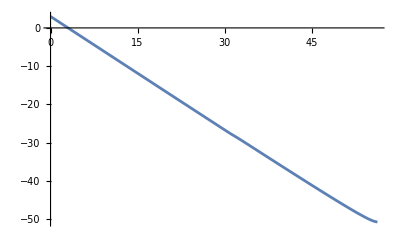

```mathematica
Plot[Log[cs/(kmpc*a[Ne]H[Ne])]/.solNe1,{Ne,0,NeFIN}]
```

```mathematica
Netotal=NeFIN+Nre(*Ntotal=Nend+Nreh*)
```

{59.2231}

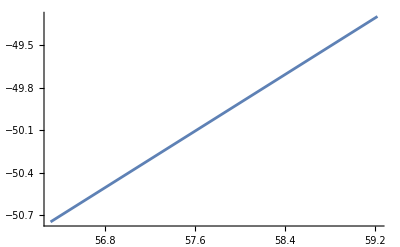

```mathematica
Plot[Log[1/kend[[1]]]+1/2(Ne-NeFIN),{Ne,NeFIN,Netotal[[1]]}]
```

```mathematica
endofinf=Log[cs/(kmpc*a[Ne]H[Ne])]/.solNe1/.Ne->NeFIN (*Log(1/k) at the end of inflation*)
```

{-50.7475}

```mathematica
endofreh=Log[1/kend[[1]]]+1/2(Netotal[[1]]-NeFIN)(*Log(1/k) at the end of reheating (RD start)*)
```

-49.2958

```mathematica
endofrd=endofreh+(100-Netotal[[1]])(*Log(1/k) at the end of RD (MD Start)*)
```

-8.51882

```mathematica
pw=Piecewise[{{Log[cs/(kmpc*(a[Ne]H[Ne])/.solNe1)][[1]],-2<Ne< NeFIN}, 
{endofinf[[1]]+1/2(Ne-NeFIN),NeFIN≤ Ne< Netotal[[1]]},
{endofreh+(Ne-Netotal[[1]]),Netotal[[1]]≤ Ne<100},
{endofrd+ 1/2(Ne-100),100≤ Ne≤130}}]
```

Piecewise[{{Log[(0.000291518 ⅇ^-Ne)/(InterpolatingFunction[…][Ne])], -2<Ne<56.3195}, {-50.7475+1/2 (-56.3195+Ne), 56.3195≤Ne<59.2231}, {-108.519+Ne, 59.2231≤Ne<100}, {-8.51882+1/2 (-100+Ne), 100≤Ne≤130}, {0, True}}]

```mathematica
line1=Line[{{0,-NeFIN},{0,1.2}}];(*Vertucal line at CMB scale*)
line2=Line[{{NeFIN,-NeFIN},{NeFIN,-40}}];(*Vertucal line at Subscript[N, end]*)
line3=Line[{{Netotal[[1]],-NeFIN},{Netotal[[1]],-40}}];(*Vertucal line at the end of reheating (RD start)*)
line4=Line[{{100,-NeFIN},{100,-10}}];(*Vertucal line at the end of RD (MD start)*)
```

```mathematica
kINcmb=Log[1/0.05]
kINpeak=Log[1/kpeak[[1]]]
KINreh=Log[1/kre[[1]]](*critical scale ->  Subscript[k, reh]^-1*)
```

2.99573

-28.7515

-49.2958

```mathematica
Plot[endofinf[[1]]+1/2(Ne-NeFIN),{ Ne,NeFIN, Netotal[[1]]}]
```

-Graphics-

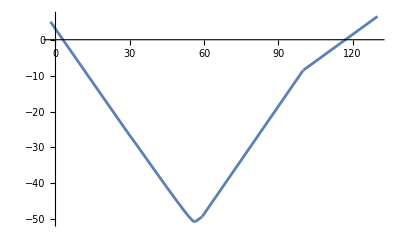

```mathematica
Plot[pw,{Ne,-2,130}]
```

```mathematica
comphi1=Plot[{pw,endofinf[[1]],endofreh,kINcmb,kINpeak,KINreh},{Ne,-2,128},Frame->True,Axes->False,PlotStyle->{{Black,Thickness[0.005]},{Transparent},{Transparent},{Dashing[0.025],Darker[Red]},{Dashing[0.025],Blue}(*,{Dashing[0.025],Blue},{Dashing[0.025],Lighter[Blue]}*),{Dashing[0.025],Darker[Green]}},FrameStyle->Directive[Thickness[0.003]],(*FrameTicks->{{Automatic,None},{None}},*)FrameTicks->{{None,None},{ {{0,"N_*"},{NeFIN,"N_end     "},{NeFIN+Nre[[1]],"          N_reh"},{100,"N_eq"}},None}},Filling->{2->{3}},FillingStyle->{Opacity[0.2,Blue]},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameLabel->{"N=Lna","Comoving Hubble Radius Ln(1/aH)"},Epilog->{Directive[Gray,Dashed],line1,line2,line3,line4,
Text[Style["k_peak^-1",18,FontFamily->"Cambria",Bold,Black],{6.5,-25}],
Text[Style["k_*^-1",18,FontFamily->"Cambria",Bold,Black],{4.65,5.6}],
Text[Style["k_reh^-1",18,FontFamily->"Cambria",Bold,Black],{6.5,-46}],
(*Text[Style["Pivot Scale",10,FontFamily->"Cambria",Black],{2,-19.5},Automatic,{0,6}],*)
(*Text[Style["⟵ End of Inflation",10,FontFamily->"Cambria",Black],{54.9,-17.5},Automatic,{0,6}],*)
Text[Style["reh",10,FontFamily->"Cambria",Black],{58.0,-39},Automatic,{1,0}],
Text[Style[" ⟵——RD——⟶",18,FontFamily->"Cambria",Black],{81,-51},Automatic,{1,0}],
Text[Style[" ⟵—MD—⟶",18,FontFamily->"Cambria",Black],{114,-51},Automatic,{1,0}]},ImageSize->{600,400}]
```

```mathematica
psreh1n=Show[{reh1,Graphics[{Directive[Gray,Dashed],Line[{{-3,-50},{-3,-20}}],Line[{{28.6,-40},{28.6,-3.4}}],Line[{{49.3,-50},{49.3,-26}}]}],Graphics[{Darker[Red],PointSize[0.02],Point[{-3,-20}]}],Graphics[{Darker[Blue],PointSize[0.02],Point[{28.7,-3}]}],Graphics[{Darker[Green],PointSize[0.02],Point[{49.4,-26.}]}]}]
```

```mathematica
Export["reh1.eps",psreh1n];
```

```mathematica
cA=Show[{comphi1,Graphics[{Black,PointSize[0.015],Point[{NeFIN,endofinf[[1]]}],Point[{Netotal[[1]],endofreh}],Point[{100,-8.8}]}],
Graphics[{{Darker[Red],PointSize[0.015],
Point[{0.05,kINcmb}],Point[{123.4,kINcmb}]},{Darker[Blue],PointSize[0.015],
Point[{32.5,kINpeak}],Point[{80,kINpeak}]},{Darker[Green],PointSize[0.015],
Point[{53.7,KINreh}],Point[{Netotal[[1]],endofreh}]}(*,
Point[{32.75,kINFree}],Point[{79.,kINFree}]*)}](*,Graphics[{Green,Thick,Circle[{43.8,-22.9},0.5]}]*)},Graphics[{Directive[Gray,Dashed](*,Line[{{-3,-50},{-3,-20}}],Line[{{29.6,-40},{29.6,-3.4}}],Line[{{43.8,-50},{43.8,-23}}]*)}]]
```

```mathematica
Export["com-rehA.eps",cA];
```

#### Solving tensor MS equation (16)

```mathematica
nPoints=5;
iMax=(NeFIN-.5)*nPoints;
NeHEt=Table[0+i/nPoints,{i,0,iMax}]//N;
NeBDt=Table[NeHEt[[i]]-1(*If[NeHEt[[i]]≤39,NeHEt[[i]]-5,NeHEt[[i]]-1]*),{i,1,iMax}]//N;
NeEndt=Table[(*NeFIN*)(*If[NeHE[[i]]≤31,NeHE[[i]]+3,NeFIN-.7]*)If[NeHEt[[i]]+1≤NeFIN,NeHEt[[i]]-.64,NeFIN],{i,1,iMax}];
kt=Table[(H[Ne]*a[Ne])/.solNe1/.{Ne->NeHEt[[i]]},{i,1,iMax}]//N;
For[i=1,i≤iMax-(iMax-1),i++,
tAux=AbsoluteTime[];
MSsolAuxt[i]=NDSolve[{((ut''[Ne]+(H'[Ne]/H[Ne]+a'[Ne]/a[Ne])ut'[Ne]+(kt[[i]]/(a[Ne] H[Ne]))^2 ut[Ne]-a''[Ne]/a[Ne] ut[Ne]-a'[Ne]/a[Ne](H'[Ne]/H[Ne]+a'[Ne]/a[Ne])ut[Ne])/.solNe1)==0,ut[NeBD[[i]]]==1/(√(2kt[[i]]))/.solNe1/.{Ne->NeBDt[[i]]},ut'[NeBDt[[i]]]==((-I kt[[i]])/(a[Ne] H[Ne] √2 √kt[[i]]))/.solNe1/.{Ne->NeBDt[[i]]}},{ut[Ne]},{Ne,NeBDt[[i]],NeEndt[[i]]},MaxSteps->Infinity(*Method->{"EquationSimplification"->"Solve"}*)(*,WorkingPrecision->30*)][[1]];Print[NeHEt[[i]]//N,"  ",kt[[i]]//N,"  ",AbsoluteTime[]-tAux]]
MSolt=Table[MSsolAuxt[i],{i,1,iMax}];
j=1;
PNt0=Table[{NeHEt[[i]],((j kt[[i]]^3/Pi^2*Abs[(ut[Ne]/.solNe1)/(a[Ne]/.solNe1)]^2)/.MSolt[[i]]/.Ne->NeEndt[[i]])[[1]][[1]]},{i,1,iMax-(iMax-1)}]
```

NDSolve::berr: The scaled boundary value residual error of 3.09495 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

0.  {0.0000145759}  4.7795323

{{0.,3.96636×10^-11}}

```mathematica
Off[NDSolve::precw];
For[i=1,i≤iMax,i++,
tAux=AbsoluteTime[];
MSsolAuxt[i]=NDSolve[{((ut''[Ne]+(H'[Ne]/H[Ne]+a'[Ne]/a[Ne])ut'[Ne]+(kt[[i]]/(a[Ne] H[Ne]))^2 ut[Ne]-a''[Ne]/a[Ne] ut[Ne]-a'[Ne]/a[Ne](H'[Ne]/H[Ne]+a'[Ne]/a[Ne])ut[Ne])/.solNe1)==0,ut[NeBDt[[i]]]==1/(√(2kt[[i]]))/.solNe1/.{Ne->NeBDt[[i]]},ut'[NeBDt[[i]]]==((-I kt[[i]])/(a[Ne] H[Ne] √2 √kt[[i]]))/.solNe1/.{Ne->NeBDt[[i]]}},{ut[Ne]},{Ne,NeBDt[[i]],NeEndt[[i]]},MaxSteps->Infinity(*Method->{"EquationSimplification"->"Solve"}*)(*,WorkingPrecision->30*)][[1]];Print[NeHEt[[i]]//N,"  ",kt[[i]]//N,"  ",AbsoluteTime[]-tAux]]
MSolt=Table[MSsolAuxt[i],{i,1,iMax}];
```

0.  {0.0000145759}  0.01402

0.2  {0.000017775}  0.

0.4  {0.0000216762}  0.

0.6  {0.0000264334}  0.

0.8  {0.0000322345}  0.015721

1.  {0.0000393084}  0.

1.2  {0.0000479346}  0.

1.4  {0.0000584535}  0.

1.6  {0.0000712802}  0.

1.8  {0.0000869211}  0.015602

2.  {0.000105994}  0.

2.2  {0.00012925}  0.

2.4  {0.000157609}  0.015666

2.6  {0.000192189}  0.

2.8  {0.000234354}  0.

3.  {0.000285769}  0.015616

3.2  {0.000348462}  0.

3.4  {0.000424906}  0.

3.6  {0.000518117}  0.

3.8  {0.000631772}  0.

4.  {0.000770355}  0.

4.2  {0.00093933}  0.0080921

4.4  {0.00114536}  0.

4.6  {0.00139658}  0.0080106

4.8  {0.00170289}  0.

5.  {0.00207637}  0.

5.2  {0.00253174}  0.

5.4  {0.00308696}  0.

5.6  {0.00376393}  0.

5.8  {0.00458932}  0.

6.  {0.00559568}  0.014044

6.2  {0.00682268}  0.002009

6.4  {0.00831867}  0.

6.6  {0.0101426}  0.

6.8  {0.0123664}  0.

7.  {0.0150777}  0.015634

7.2  {0.0183833}  0.

7.4  {0.0224135}  0.015623

7.6  {0.027327}  0.

7.8  {0.0333175}  0.

8.  {0.0406208}  0.

8.2  {0.0495248}  0.015708

8.4  {0.0603802}  0.

8.6  {0.0736144}  0.01998

8.8  {0.0897487}  0.002789

9.  {0.109419}  0.

9.2  {0.133398}  0.014748

9.4  {0.162632}  0.

9.6  {0.198272}  0.

9.8  {0.241719}  0.010054

10.  {0.294685}  0.0066645

10.2  {0.359255}  0.

10.4  {0.43797}  0.

10.6  {0.533928}  0.0090964

10.8  {0.650905}  0.

11.  {0.793505}  0.

11.2  {0.967338}  0.015742

11.4  {1.17924}  0.001037

11.6  {1.43756}  0.

11.8  {1.75245}  0.

12.  {2.13629}  0.015148

12.2  {2.60419}  0.

12.4  {3.17455}  0.

12.6  {3.86979}  0.015723

12.8  {4.71726}  0.002511

13.  {5.75028}  0.

13.2  {7.00945}  0.013513

13.4  {8.54429}  0.

13.6  {10.4151}  0.015637

13.8  {12.6955}  0.0092471

14.  {15.475}  0.0065511

14.2  {18.8629}  0.

14.4  {22.9923}  0.

14.6  {28.0254}  0.

14.8  {34.1601}  0.016242

15.  {41.6373}  0.

15.2  {50.7506}  0.

15.4  {61.8582}  0.015512

15.6  {75.396}  0.

15.8  {91.896}  0.010921

16.  {112.006}  0.00501

16.2  {136.515}  0.007514

16.4  {166.386}  0.

16.6  {202.791}  0.0085097

16.8  {247.159}  0.

17.  {301.232}  0.

17.2  {367.131}  0.015731

17.4  {447.442}  0.

17.6  {545.316}  0.016242

17.8  {664.593}  0.

18.  {809.952}  0.

18.2  {987.093}  0.015024

18.4  {1202.97}  0.

18.6  {1466.03}  0.

18.8  {1786.61}  0.015637

19.  {2177.26}  0.

19.2  {2653.31}  0.015623

19.4  {3233.41}  0.

19.6  {3940.3}  0.

19.8  {4801.68}  0.017254

20.  {5851.29}  0.

20.2  {7130.27}  0.

20.4  {8688.72}  0.015097

20.6  {10587.7}  0.

20.8  {12901.5}  0.015728

21.  {15720.8}  0.

21.2  {19156.1}  0.

21.4  {23341.6}  0.016187

21.6  {28441.5}  0.002946

21.8  {34655.1}  0.

22.  {42225.8}  0.012512

22.2  {51449.7}  0.

22.4  {62687.7}  0.

22.6  {76379.6}  0.015848

22.8  {93060.8}  0.

23.  {113384.}  0.015738

23.2  {138143.}  0.002525

23.4  {168307.}  0.

23.6  {205055.}  0.013594

23.8  {249823.}  0.

24.  {304361.}  0.

24.2  {370800.}  0.015828

24.4  {451736.}  0.

24.6  {550330.}  0.

24.8  {670435.}  0.015562

25.  {816740.}  0.0083634

25.2  {994958.}  0.0075092

25.4  {1.21205×10^6}  0.

25.6  {1.47648×10^6}  0.0099614

25.8  {1.79859×10^6}  0.0060304

26.  {2.19093×10^6}  0.

26.2  {2.66882×10^6}  0.

26.4  {3.2509×10^6}  0.016708

26.6  {3.95987×10^6}  0.0065133

26.8  {4.82338×10^6}  0.0085115

27.  {5.8751×10^6}  0.

27.2  {7.15602×10^6}  0.

27.4  {8.71606×10^6}  0.015636

27.6  {1.0616×10^7}  0.

27.8  {1.29299×10^7}  0.015713

28.  {1.57477×10^7}  0.

28.2  {1.91793×10^7}  0.

28.4  {2.33582×10^7}  0.

28.6  {2.8447×10^7}  0.015535

28.8  {3.46435×10^7}  0.

29.  {4.21887×10^7}  0.

29.2  {5.13754×10^7}  0.016401

29.4  {6.25604×10^7}  0.

29.6  {7.6177×10^7}  0.015015

29.8  {9.27529×10^7}  0.

30.  {1.12929×10^8}  0.

30.2  {1.37482×10^8}  0.016123

30.4  {1.67355×10^8}  0.

30.6  {2.03692×10^8}  0.

30.8  {2.4787×10^8}  0.015632

31.  {3.01537×10^8}  0.

31.2  {3.66646×10^8}  0.

31.4  {4.454×10^8}  0.015664

31.6  {5.39445×10^8}  0.

31.8  {6.33112×10^8}  0.

32.  {7.48336×10^8}  0.

32.2  {8.93875×10^8}  0.

32.4  {1.07515×10^9}  0.015585

32.6  {1.29875×10^9}  0.

32.8  {1.57296×10^9}  0.

33.  {1.90801×10^9}  0.015651

33.2  {2.31661×10^9}  0.

33.4  {2.81434×10^9}  0.

33.6  {3.42008×10^9}  0.015607

33.8  {4.15697×10^9}  0.

34.  {5.05318×10^9}  0.

34.2  {6.14295×10^9}  0.015066

34.4  {7.46791×10^9}  0.0035827

34.6  {9.07868×10^9}  0.

34.8  {1.10367×10^10}  0.012593

35.  {1.34168×10^10}  0.

35.2  {1.63095×10^10}  0.015638

35.4  {1.98253×10^10}  0.

35.6  {2.4098×10^10}  0.

35.8  {2.92904×10^10}  0.

36.  {3.55998×10^10}  0.015623

36.2  {4.32665×10^10}  0.

36.4  {5.25816×10^10}  0.015624

36.6  {6.38991×10^10}  0.

36.8  {7.76488×10^10}  0.

37.  {9.43523×10^10}  0.

37.2  {1.14643×10^11}  0.

37.4  {1.3929×10^11}  0.015633

37.6  {1.69226×10^11}  0.

37.8  {2.05584×10^11}  0.

38.  {2.49738×10^11}  0.

38.2  {3.03358×10^11}  0.

38.4  {3.68469×10^11}  0.

38.6  {4.47526×10^11}  0.016554

38.8  {5.43511×10^11}  0.008592

39.  {6.6004×10^11}  0.

39.2  {8.01499×10^11}  0.0065895

39.4  {9.7321×10^11}  0.

39.6  {1.18163×10^12}  0.015637

39.8  {1.43457×10^12}  0.

40.  {1.74154×10^12}  0.

40.2  {2.11403×10^12}  0.

40.4  {2.566×10^12}  0.

40.6  {3.11435×10^12}  0.

40.8  {3.77958×10^12}  0.015705

41.  {4.58652×10^12}  0.

41.2  {5.56526×10^12}  0.

41.4  {6.75228×10^12}  0.015547

41.6  {8.19174×10^12}  0.

41.8  {9.93716×10^12}  0.

42.  {1.20533×10^13}  0.

42.2  {1.46188×10^13}  0.016329

42.4  {1.77284×10^13}  0.

42.6  {2.14974×10^13}  0.

42.8  {2.60648×10^13}  0.

43.  {3.15993×10^13}  0.

43.2  {3.83046×10^13}  0.01618

43.4  {4.64275×10^13}  0.

43.6  {5.62662×10^13}  0.

43.8  {6.81816×10^13}  0.

44.  {8.26098×10^13}  0.015672

44.2  {1.00078×10^14}  0.

44.4  {1.21224×10^14}  0.

44.6  {1.46817×10^14}  0.

44.8  {1.77788×10^14}  0.

45.  {2.15261×10^14}  0.015633

45.2  {2.60591×10^14}  0.

45.4  {3.15418×10^14}  0.

45.6  {3.81716×10^14}  0.

45.8  {4.61871×10^14}  0.

46.  {5.58758×10^14}  0.

46.2  {6.75845×10^14}  0.016307

46.4  {8.1731×10^14}  0.

46.6  {9.88189×10^14}  0.

46.8  {1.19455×10^15}  0.

47.  {1.44369×10^15}  0.

47.2  {1.74439×10^15}  0.015093

47.4  {2.10724×10^15}  0.

47.6  {2.54494×10^15}  0.

47.8  {3.07277×10^15}  0.

48.  {3.70909×10^15}  0.

48.2  {4.47592×10^15}  0.

48.4  {5.3997×10^15}  0.016333

48.6  {6.51214×10^15}  0.

48.8  {7.85122×10^15}  0.

49.  {9.4624×10^15}  0.

49.2  {1.14001×10^16}  0.

49.4  {1.37294×10^16}  0.015569

49.6  {1.6528×10^16}  0.0045116

49.8  {1.98886×10^16}  0.

50.  {2.39218×10^16}  0.012269

50.2  {2.87592×10^16}  0.

50.4  {3.45575×10^16}  0.015027

50.6  {4.1503×10^16}  0.

50.8  {4.98163×10^16}  0.015654

51.  {5.97582×10^16}  0.

51.2  {7.16372×10^16}  0.

51.4  {8.58174×10^16}  0.

51.6  {1.02727×10^17}  0.015714

51.8  {1.22868×10^17}  0.

52.  {1.46827×10^17}  0.

52.2  {1.75286×10^17}  0.

52.4  {2.09039×10^17}  0.

52.6  {2.49002×10^17}  0.015525

52.8  {2.96232×10^17}  0.

53.  {3.51928×10^17}  0.015623

53.2  {4.17445×10^17}  0.

53.4  {4.94294×10^17}  0.

53.6  {5.84142×10^17}  0.

53.8  {6.88795×10^17}  0.010528

54.  {8.10165×10^17}  0.

54.2  {9.50196×10^17}  0.0055499

54.4  {1.11075×10^18}  0.

54.6  {1.29333×10^18}  0.

54.8  {1.49881×10^18}  0.

55.  {1.72717×10^18}  0.

55.2  {1.9764×10^18}  0.015722

55.4  {2.24196×10^18}  0.

55.6  {2.51487×10^18}  0.

```mathematica
PNt=Table[{NeHEt[[i]],((j kt[[i]]^3/Pi^2*Abs[ut[Ne]/.solNe1]^2/a[Ne]^2)/.MSolt[[i]]/.Ne->NeEndt[[i]])[[1]][[1]]},{i,1,iMax}]
```

{{0.,4.65764×10^-11},{0.2,4.64298×10^-11},{0.4,4.62832×10^-11},{0.6,4.61366×10^-11},{0.8,4.599×10^-11},{1.,4.58434×10^-11},{1.2,4.56967×10^-11},{1.4,4.55501×10^-11},{1.6,4.54034×10^-11},{1.8,4.52568×10^-11},{2.,4.51101×10^-11},{2.2,4.49634×10^-11},{2.4,4.48168×10^-11},{2.6,4.46701×10^-11},{2.8,4.45234×10^-11},{3.,4.43767×10^-11},{3.2,4.423×10^-11},{3.4,4.40833×10^-11},{3.6,4.39366×10^-11},{3.8,4.37899×10^-11},{4.,4.36432×10^-11},{4.2,4.34964×10^-11},{4.4,4.33497×10^-11},{4.6,4.3203×10^-11},{4.8,4.30562×10^-11},{5.,4.29095×10^-11},{5.2,4.27627×10^-11},{5.4,4.26159×10^-11},{5.6,4.24692×10^-11},{5.8,4.23224×10^-11},{6.,4.21756×10^-11},{6.2,4.20288×10^-11},{6.4,4.1882×10^-11},{6.6,4.17352×10^-11},{6.8,4.15884×10^-11},{7.,4.14415×10^-11},{7.2,4.12947×10^-11},{7.4,4.11479×10^-11},{7.6,4.1001×10^-11},{7.8,4.08542×10^-11},{8.,4.07073×10^-11},{8.2,4.05605×10^-11},{8.4,4.04136×10^-11},{8.6,4.02667×10^-11},{8.8,4.01199×10^-11},{9.,3.9973×10^-11},{9.2,3.98261×10^-11},{9.4,3.96792×10^-11},{9.6,3.95323×10^-11},{9.8,3.93854×10^-11},{10.,3.92385×10^-11},{10.2,3.90916×10^-11},{10.4,3.89446×10^-11},{10.6,3.87977×10^-11},{10.8,3.86508×10^-11},{11.,3.85038×10^-11},{11.2,3.83569×10^-11},{11.4,3.82099×10^-11},{11.6,3.80629×10^-11},{11.8,3.7916×10^-11},{12.,3.7769×10^-11},{12.2,3.7622×10^-11},{12.4,3.7475×10^-11},{12.6,3.73281×10^-11},{12.8,3.71811×10^-11},{13.,3.70341×10^-11},{13.2,3.6887×10^-11},{13.4,3.674×10^-11},{13.6,3.6593×10^-11},{13.8,3.6446×10^-11},{14.,3.6299×10^-11},{14.2,3.61519×10^-11},{14.4,3.60049×10^-11},{14.6,3.58579×10^-11},{14.8,3.57108×10^-11},{15.,3.55637×10^-11},{15.2,3.54167×10^-11},{15.4,3.52696×10^-11},{15.6,3.51225×10^-11},{15.8,3.49755×10^-11},{16.,3.48284×10^-11},{16.2,3.46813×10^-11},{16.4,3.45342×10^-11},{16.6,3.43871×10^-11},{16.8,3.424×10^-11},{17.,3.40929×10^-11},{17.2,3.39457×10^-11},{17.4,3.37986×10^-11},{17.6,3.36515×10^-11},{17.8,3.35044×10^-11},{18.,3.33572×10^-11},{18.2,3.32101×10^-11},{18.4,3.30629×10^-11},{18.6,3.29158×10^-11},{18.8,3.27686×10^-11},{19.,3.26214×10^-11},{19.2,3.24743×10^-11},{19.4,3.23271×10^-11},{19.6,3.21799×10^-11},{19.8,3.20327×10^-11},{20.,3.18855×10^-11},{20.2,3.17383×10^-11},{20.4,3.15911×10^-11},{20.6,3.14439×10^-11},{20.8,3.12967×10^-11},{21.,3.11494×10^-11},{21.2,3.10022×10^-11},{21.4,3.0855×10^-11},{21.6,3.07077×10^-11},{21.8,3.05605×10^-11},{22.,3.04132×10^-11},{22.2,3.0266×10^-11},{22.4,3.01187×10^-11},{22.6,2.99714×10^-11},{22.8,2.98241×10^-11},{23.,2.96768×10^-11},{23.2,2.95295×10^-11},{23.4,2.93822×10^-11},{23.6,2.92349×10^-11},{23.8,2.90876×10^-11},{24.,2.89402×10^-11},{24.2,2.87928×10^-11},{24.4,2.86455×10^-11},{24.6,2.84981×10^-11},{24.8,2.83506×10^-11},{25.,2.82032×10^-11},{25.2,2.80557×10^-11},{25.4,2.79082×10^-11},{25.6,2.77607×10^-11},{25.8,2.76133×10^-11},{26.,2.74658×10^-11},{26.2,2.73184×10^-11},{26.4,2.71709×10^-11},{26.6,2.70234×10^-11},{26.8,2.68759×10^-11},{27.,2.67282×10^-11},{27.2,2.65805×10^-11},{27.4,2.64327×10^-11},{27.6,2.62847×10^-11},{27.8,2.61366×10^-11},{28.,2.59882×10^-11},{28.2,2.58397×10^-11},{28.4,2.56911×10^-11},{28.6,2.55421×10^-11},{28.8,2.53929×10^-11},{29.,2.52431×10^-11},{29.2,2.50926×10^-11},{29.4,2.49412×10^-11},{29.6,2.47886×10^-11},{29.8,2.46345×10^-11},{30.,2.44783×10^-11},{30.2,2.43192×10^-11},{30.4,2.4156×10^-11},{30.6,2.39874×10^-11},{30.8,2.38108×10^-11},{31.,2.36212×10^-11},{31.2,2.34108×10^-11},{31.4,2.31603×10^-11},{31.6,2.27789×10^-11},{31.8,2.10791×10^-11},{32.,1.97718×10^-11},{32.2,1.89212×10^-11},{32.4,1.8299×10^-11},{32.6,1.77061×10^-11},{32.8,1.7429×10^-11},{33.,1.72398×10^-11},{33.2,1.70677×10^-11},{33.4,1.69046×10^-11},{33.6,1.67458×10^-11},{33.8,1.659×10^-11},{34.,1.64367×10^-11},{34.2,1.6285×10^-11},{34.4,1.61344×10^-11},{34.6,1.59847×10^-11},{34.8,1.58356×10^-11},{35.,1.5687×10^-11},{35.2,1.55387×10^-11},{35.4,1.53906×10^-11},{35.6,1.52427×10^-11},{35.8,1.50949×10^-11},{36.,1.49472×10^-11},{36.2,1.47995×10^-11},{36.4,1.46519×10^-11},{36.6,1.45043×10^-11},{36.8,1.43567×10^-11},{37.,1.42092×10^-11},{37.2,1.40618×10^-11},{37.4,1.39144×10^-11},{37.6,1.37669×10^-11},{37.8,1.36195×10^-11},{38.,1.34721×10^-11},{38.2,1.33247×10^-11},{38.4,1.31773×10^-11},{38.6,1.30299×10^-11},{38.8,1.28825×10^-11},{39.,1.27351×10^-11},{39.2,1.25877×10^-11},{39.4,1.24404×10^-11},{39.6,1.22931×10^-11},{39.8,1.21458×10^-11},{40.,1.19985×10^-11},{40.2,1.18512×10^-11},{40.4,1.17039×10^-11},{40.6,1.15567×10^-11},{40.8,1.14094×10^-11},{41.,1.12622×10^-11},{41.2,1.11149×10^-11},{41.4,1.09677×10^-11},{41.6,1.08204×10^-11},{41.8,1.06732×10^-11},{42.,1.0526×10^-11},{42.2,1.03788×10^-11},{42.4,1.02364×10^-11},{42.6,1.00895×10^-11},{42.8,9.94195×10^-12},{43.,9.79507×10^-12},{43.2,9.64791×10^-12},{43.4,9.50077×10^-12},{43.6,9.35365×10^-12},{43.8,9.20626×10^-12},{44.,9.05946×10^-12},{44.2,8.9124×10^-12},{44.4,8.76536×10^-12},{44.6,8.61835×10^-12},{44.8,8.47136×10^-12},{45.,8.3244×10^-12},{45.2,8.17747×10^-12},{45.4,8.03058×10^-12},{45.6,7.88372×10^-12},{45.8,7.7369×10^-12},{46.,7.5899×10^-12},{46.2,7.44315×10^-12},{46.4,7.29666×10^-12},{46.6,7.14999×10^-12},{46.8,7.00336×10^-12},{47.,6.85676×10^-12},{47.2,6.7102×10^-12},{47.4,6.5637×10^-12},{47.6,6.41724×10^-12},{47.8,6.27085×10^-12},{48.,6.12452×10^-12},{48.2,5.97824×10^-12},{48.4,5.83203×10^-12},{48.6,5.68589×10^-12},{48.8,5.53982×10^-12},{49.,5.39379×10^-12},{49.2,5.24781×10^-12},{49.4,5.10176×10^-12},{49.6,4.95606×10^-12},{49.8,4.8103×10^-12},{50.,4.66449×10^-12},{50.2,4.51905×10^-12},{50.4,4.37365×10^-12},{50.6,4.22843×10^-12},{50.8,4.08342×10^-12},{51.,3.93856×10^-12},{51.2,3.79384×10^-12},{51.4,3.64923×10^-12},{51.6,3.50499×10^-12},{51.8,3.36086×10^-12},{52.,3.21681×10^-12},{52.2,3.07306×10^-12},{52.4,2.92938×10^-12},{52.6,2.78595×10^-12},{52.8,2.64278×10^-12},{53.,2.50007×10^-12},{53.2,2.35761×10^-12},{53.4,2.21549×10^-12},{53.6,2.07372×10^-12},{53.8,1.9325×10^-12},{54.,1.7918×10^-12},{54.2,1.65179×10^-12},{54.4,1.51268×10^-12},{54.6,1.37435×10^-12},{54.8,1.23687×10^-12},{55.,1.10058×10^-12},{55.2,9.65625×10^-13},{55.4,2.26576×10^-13},{55.6,2.10831×10^-13}}

```mathematica
PNt[[1,2]]/PN0[[1,2]]
```

0.0190404

```mathematica
ListLogPlot[PNt(*,PlotRange->{{0,60},{3*10^-13,2*10^-11}}*),Joined->True,Frame->True,PlotStyle->Red]
```

```mathematica
kmpct=Solve[0.002/Mpct==(a[Ne] H[Ne])/.solNe1/.Ne->0,Mpct][[1]][[1,2]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

137.213

```mathematica
Pkt=Table[{(kmpct(H[Ne]a[Ne])/.solNe1/.{Ne->NeHEt[[i]]})[[1]],(j kt[[i]]^3/Pi^2*Abs[(ut[Ne]/.solNe1)/(a[Ne]/.solNe1)]^2/.MSolt[[i]]/.Ne->NeEndt[[i]])[[1]][[1]]},{i,1,iMax}]
```

{{0.002,4.65764×10^-11},{0.00243896,4.64298×10^-11},{0.00297424,4.62832×10^-11},{0.00362699,4.61366×10^-11},{0.00442298,4.599×10^-11},{0.00539362,4.58434×10^-11},{0.00657723,4.56967×10^-11},{0.00802055,4.55501×10^-11},{0.00978055,4.54034×10^-11},{0.0119267,4.52568×10^-11},{0.0145437,4.51101×10^-11},{0.0177348,4.49634×10^-11},{0.0216259,4.48168×10^-11},{0.0263707,4.46701×10^-11},{0.0321564,4.45234×10^-11},{0.0392111,4.43767×10^-11},{0.0478134,4.423×10^-11},{0.0583025,4.40833×10^-11},{0.0710922,4.39366×10^-11},{0.0866871,4.37899×10^-11},{0.105702,4.36432×10^-11},{0.128888,4.34964×10^-11},{0.157158,4.33497×10^-11},{0.191629,4.3203×10^-11},{0.233658,4.30562×10^-11},{0.284904,4.29095×10^-11},{0.347387,4.27627×10^-11},{0.42357,4.26159×10^-11},{0.516459,4.24692×10^-11},{0.629713,4.23224×10^-11},{0.767799,4.21756×10^-11},{0.936158,4.20288×10^-11},{1.14143,4.1882×10^-11},{1.3917,4.17352×10^-11},{1.69683,4.15884×10^-11},{2.06885,4.14415×10^-11},{2.52242,4.12947×10^-11},{3.07541,4.11479×10^-11},{3.74961,4.1001×10^-11},{4.57158,4.08542×10^-11},{5.57369,4.07073×10^-11},{6.79544,4.05605×10^-11},{8.28493,4.04136×10^-11},{10.1008,4.02667×10^-11},{12.3147,4.01199×10^-11},{15.0136,3.9973×10^-11},{18.3039,3.98261×10^-11},{22.3152,3.96792×10^-11},{27.2054,3.95323×10^-11},{33.1669,3.93854×10^-11},{40.4346,3.92385×10^-11},{49.2944,3.90916×10^-11},{60.0951,3.89446×10^-11},{73.2617,3.87977×10^-11},{89.3124,3.86508×10^-11},{108.879,3.85038×10^-11},{132.731,3.83569×10^-11},{161.807,3.82099×10^-11},{197.251,3.80629×10^-11},{240.458,3.7916×10^-11},{293.126,3.7769×10^-11},{357.328,3.7622×10^-11},{435.588,3.7475×10^-11},{530.985,3.73281×10^-11},{647.268,3.71811×10^-11},{789.011,3.70341×10^-11},{961.786,3.6887×10^-11},{1172.38,3.674×10^-11},{1429.09,3.6593×10^-11},{1741.98,3.6446×10^-11},{2123.36,3.6299×10^-11},{2588.23,3.61519×10^-11},{3154.83,3.60049×10^-11},{3845.45,3.58579×10^-11},{4687.2,3.57108×10^-11},{5713.16,3.55637×10^-11},{6963.63,3.54167×10^-11},{8487.72,3.52696×10^-11},{10345.3,3.51225×10^-11},{12609.3,3.49755×10^-11},{15368.6,3.48284×10^-11},{18731.6,3.46813×10^-11},{22830.2,3.45342×10^-11},{27825.5,3.43871×10^-11},{33913.4,3.424×10^-11},{41332.8,3.40929×10^-11},{50375.,3.39457×10^-11},{61394.7,3.37986×10^-11},{74824.3,3.36515×10^-11},{91190.6,3.35044×10^-11},{111136.,3.33572×10^-11},{135442.,3.32101×10^-11},{165062.,3.30629×10^-11},{201158.,3.29158×10^-11},{245145.,3.27686×10^-11},{298748.,3.26214×10^-11},{364068.,3.24743×10^-11},{443665.,3.23271×10^-11},{540659.,3.21799×10^-11},{658851.,3.20327×10^-11},{802871.,3.18855×10^-11},{978363.,3.17383×10^-11},{1.1922×10^6,3.15911×10^-11},{1.45276×10^6,3.14439×10^-11},{1.77025×10^6,3.12967×10^-11},{2.1571×10^6,3.11494×10^-11},{2.62845×10^6,3.10022×10^-11},{3.20277×10^6,3.0855×10^-11},{3.90253×10^6,3.07077×10^-11},{4.75512×10^6,3.05605×10^-11},{5.79391×10^6,3.04132×10^-11},{7.05955×10^6,3.0266×10^-11},{8.60155×10^6,3.01187×10^-11},{1.04802×10^7,2.99714×10^-11},{1.27691×10^7,2.98241×10^-11},{1.55577×10^7,2.96768×10^-11},{1.8955×10^7,2.95295×10^-11},{2.30939×10^7,2.93822×10^-11},{2.81361×10^7,2.92349×10^-11},{3.42789×10^7,2.90876×10^-11},{4.17622×10^7,2.89402×10^-11},{5.08784×10^7,2.87928×10^-11},{6.19839×10^7,2.86455×10^-11},{7.55123×10^7,2.84981×10^-11},{9.19921×10^7,2.83506×10^-11},{1.12067×10^8,2.82032×10^-11},{1.36521×10^8,2.80557×10^-11},{1.66308×10^8,2.79082×10^-11},{2.02592×10^8,2.77607×10^-11},{2.46789×10^8,2.76133×10^-11},{3.00623×10^8,2.74658×10^-11},{3.66196×10^8,2.73184×10^-11},{4.46064×10^8,2.71709×10^-11},{5.43344×10^8,2.70234×10^-11},{6.61829×10^8,2.68759×10^-11},{8.06138×10^8,2.67282×10^-11},{9.81897×10^8,2.65805×10^-11},{1.19595×10^9,2.64327×10^-11},{1.45665×10^9,2.62847×10^-11},{1.77414×10^9,2.61366×10^-11},{2.16079×10^9,2.59882×10^-11},{2.63164×10^9,2.58397×10^-11},{3.20504×10^9,2.56911×10^-11},{3.90328×10^9,2.55421×10^-11},{4.75353×10^9,2.53929×10^-11},{5.78882×10^9,2.52431×10^-11},{7.04936×10^9,2.50926×10^-11},{8.58408×10^9,2.49412×10^-11},{1.04525×10^10,2.47886×10^-11},{1.27269×10^10,2.46345×10^-11},{1.54952×10^10,2.44783×10^-11},{1.88643×10^10,2.43192×10^-11},{2.29633×10^10,2.4156×10^-11},{2.79491×10^10,2.39874×10^-11},{3.40109×10^10,2.38108×10^-11},{4.13747×10^10,2.36212×10^-11},{5.03084×10^10,2.34108×10^-11},{6.11145×10^10,2.31603×10^-11},{7.40187×10^10,2.27789×10^-11},{8.68709×10^10,2.10791×10^-11},{1.02681×10^11,1.97718×10^-11},{1.22651×10^11,1.89212×10^-11},{1.47524×10^11,1.8299×10^-11},{1.78205×10^11,1.77061×10^-11},{2.15831×10^11,1.7429×10^-11},{2.61803×10^11,1.72398×10^-11},{3.17868×10^11,1.70677×10^-11},{3.86163×10^11,1.69046×10^-11},{4.69279×10^11,1.67458×10^-11},{5.70389×10^11,1.659×10^-11},{6.9336×10^11,1.64367×10^-11},{8.4289×10^11,1.6285×10^-11},{1.02469×10^12,1.61344×10^-11},{1.24571×10^12,1.59847×10^-11},{1.51438×10^12,1.58356×10^-11},{1.84095×10^12,1.5687×10^-11},{2.23788×10^12,1.55387×10^-11},{2.72028×10^12,1.53906×10^-11},{3.30656×10^12,1.52427×10^-11},{4.01901×10^12,1.50949×10^-11},{4.88475×10^12,1.49472×10^-11},{5.93671×10^12,1.47995×10^-11},{7.21486×10^12,1.46519×10^-11},{8.76777×10^12,1.45043×10^-11},{1.06544×10^13,1.43567×10^-11},{1.29463×10^13,1.42092×10^-11},{1.57305×10^13,1.40618×10^-11},{1.91123×10^13,1.39144×10^-11},{2.32199×10^13,1.37669×10^-11},{2.82087×10^13,1.36195×10^-11},{3.42673×10^13,1.34721×10^-11},{4.16246×10^13,1.33247×10^-11},{5.05586×10^13,1.31773×10^-11},{6.14062×10^13,1.30299×10^-11},{7.45766×10^13,1.28825×10^-11},{9.05658×10^13,1.27351×10^-11},{1.09976×10^14,1.25877×10^-11},{1.33537×10^14,1.24404×10^-11},{1.62134×10^14,1.22931×10^-11},{1.96842×10^14,1.21458×10^-11},{2.38961×10^14,1.19985×10^-11},{2.90072×10^14,1.18512×10^-11},{3.52088×10^14,1.17039×10^-11},{4.27329×10^14,1.15567×10^-11},{5.18606×10^14,1.14094×10^-11},{6.29328×10^14,1.12622×10^-11},{7.63625×10^14,1.11149×10^-11},{9.26499×10^14,1.09677×10^-11},{1.12401×10^15,1.08204×10^-11},{1.3635×10^15,1.06732×10^-11},{1.65387×10^15,1.0526×10^-11},{2.00588×10^15,1.03788×10^-11},{2.43256×10^15,1.02364×10^-11},{2.94971×10^15,1.00895×10^-11},{3.57642×10^15,9.94195×10^-12},{4.33582×10^15,9.79507×10^-12},{5.25588×10^15,9.64791×10^-12},{6.37044×10^15,9.50077×10^-12},{7.72044×10^15,9.35365×10^-12},{9.35537×10^15,9.20626×10^-12},{1.13351×10^16,9.05946×10^-12},{1.3732×10^16,8.9124×10^-12},{1.66335×10^16,8.76536×10^-12},{2.01452×10^16,8.61835×10^-12},{2.43948×10^16,8.47136×10^-12},{2.95365×10^16,8.3244×10^-12},{3.57565×10^16,8.17747×10^-12},{4.32793×10^16,8.03058×10^-12},{5.23763×10^16,7.88372×10^-12},{6.33746×10^16,7.7369×10^-12},{7.66687×10^16,7.5899×10^-12},{9.27345×10^16,7.44315×10^-12},{1.12145×10^17,7.29666×10^-12},{1.35592×10^17,7.14999×10^-12},{1.63907×10^17,7.00336×10^-12},{1.98092×10^17,6.85676×10^-12},{2.39353×10^17,6.7102×10^-12},{2.8914×10^17,6.5637×10^-12},{3.49198×10^17,6.41724×10^-12},{4.21623×10^17,6.27085×10^-12},{5.08934×10^17,6.12452×10^-12},{6.14153×10^17,5.97824×10^-12},{7.40907×10^17,5.83203×10^-12},{8.93548×10^17,5.68589×10^-12},{1.07729×10^18,5.53982×10^-12},{1.29836×10^18,5.39379×10^-12},{1.56424×10^18,5.24781×10^-12},{1.88385×10^18,5.10176×10^-12},{2.26785×10^18,4.95606×10^-12},{2.72897×10^18,4.8103×10^-12},{3.28237×10^18,4.66449×10^-12},{3.94612×10^18,4.51905×10^-12},{4.74173×10^18,4.37365×10^-12},{5.69473×10^18,4.22843×10^-12},{6.83542×10^18,4.08342×10^-12},{8.19958×10^18,3.93856×10^-12},{9.82953×10^18,3.79384×10^-12},{1.17752×10^19,3.64923×10^-12},{1.40954×10^19,3.50499×10^-12},{1.68591×10^19,3.36086×10^-12},{2.01465×10^19,3.21681×10^-12},{2.40515×10^19,3.07306×10^-12},{2.86828×10^19,2.92938×10^-12},{3.41662×10^19,2.78595×10^-12},{4.06467×10^19,2.64278×10^-12},{4.8289×10^19,2.50007×10^-12},{5.72788×10^19,2.35761×10^-12},{6.78234×10^19,2.21549×10^-12},{8.01517×10^19,2.07372×10^-12},{9.45115×10^19,1.9325×10^-12},{1.11165×10^20,1.7918×10^-12},{1.30379×10^20,1.65179×10^-12},{1.52409×10^20,1.51268×10^-12},{1.77461×10^20,1.37435×10^-12},{2.05656×10^20,1.23687×10^-12},{2.3699×10^20,1.10058×10^-12},{2.71187×10^20,9.65625×10^-13},{3.07626×10^20,2.26576×10^-13},{3.45071×10^20,2.10831×10^-13}}

```mathematica
ct=Interpolation[Pkt,InterpolationOrder->1]
AAt=LogLogPlot[{ct[x]},{x,0.002,4*^20}(*,PlotRange->{{0.001,4*10^22},{10^-12,1}}*),Frame->True,FrameStyle->Thick,FrameTicksStyle->Black,PlotStyle->Red,LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],ImageSize->{600,400},AspectRatio->Full,Axes->False,FrameLabel->{"k/Mpc^-1","P_t"},RotateLabel->True,PlotLegends->{Placed[LineLegend[{{Red},{Darker[Green]},Blue,Purple},{"Case A","Case B ","Case C","Case D"},LabelStyle->{14,FontFamily->"Cambria"},LegendLayout->"Column",LegendMarkerSize->{{30,20}}],{0.18,0.3}]}]
```

InterpolatingFunction[…]

```mathematica
ct[0.05kmpct]
```

4.05541×10^-11

```mathematica
c1[0.05kmpc]
```

1.97629×10^-9

```mathematica
ct[0.05kmpct]/(c1[0.05kmpc](*2.1*10^-9*))
```

0.0205203

```mathematica
LogPlot[(2 H[Ne]^2/.solNe1)/Pi^2,{Ne,0,NeFIN},PlotRange->All,Frame->True]
```

```mathematica
(((2 H[Ne]^2/.solNe1)/Pi^2)[[1]]/.Ne->0)/(c1[0.05kmpc](*2.1*10^-9*))
```

0.0217847

## Case B

```mathematica
Clear["Global`*"]
Remove["Global`*"]
```

Remove::rmnsm: There are no symbols matching "Global`*".

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ϵ1[Ne_]:=-H'[Ne]/H[Ne]
ϵ2[Ne_]:=-(H[Ne] (H'[Ne]^2/H[Ne]^2-H''[Ne]/H[Ne]))/H'[Ne](*ϵ1[Ne]-1/(2ϵ1[Ne])ϵ1'[Ne]*)
```

```mathematica
V[ϕ_]:=Λ^4(1+Cos[ϕ/f])
ϵ[ϕ_]:=w(Cosh[(ϕ-ϕc)/b])^-2
```

#### Solving Background Equations (6)&(9)

```mathematica
Off[NDSolve::precw];
ϕ0=5.53327945289528760424702860706861791151`29.518687405708878;
dϕ0=0.0052583177533965574057692244440840616889231016307249570077`26.83391284890734;
w=1.522*10^1;
b=1.2*10^-2;
ϕc=5.74;
Λ=1.``15*10^-2;
α=20.;
M0=2.33``15*10^-4;
f=2.``15;
cs=1/(√(2α-1));

solNe1=NDSolve[{H[Ne]H'[Ne]==-α H[Ne]^2 ϕ'[Ne]^2/2(H[Ne]^2 ϕ'[Ne]^2/(2 M[ϕ[Ne]]^4))^(α-1),ϕ''[Ne]==-(3/(2α-1)-ϵ1[Ne])ϕ'[Ne]-(V'[ϕ[Ne]]/V[ϕ[Ne]])((3α-(2α-1)ϵ1[Ne])/(α(2α-1)))ϕ'[Ne]^2/(2ϵ1[Ne])+(2(α-1))/α M'[ϕ[Ne]]/M[ϕ[Ne]] ϕ'[Ne]^2,ϕ[-6]==ϕ0,H[-6]==√(V[ϕ[-6]]/3),ϕ'[-6]==dϕ0},{ϕ,H},{Ne,-6``15,65``15},Method->{"EquationSimplification"->"Residual"},AccuracyGoal->6.2356,PrecisionGoal->30.]
NeFIN=FindRoot[(ϵ1[Ne]/.solNe1)==1,{Ne,52}]
NeFIN=NeFIN[[1,2]];
phi=Plot[ϕ[Ne]/.solNe1,{Ne,-6,NeFIN},PlotRange->{{-1,58},{5.4,6.3}},Frame->True,FrameLabel->{"N","ϕ/M_P"},PlotStyle->Darker[Green],LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],ImageSize->{600,400},RotateLabel->False,FrameStyle->Thick,FrameTicksStyle->Black]
LogPlot[{ϵ1[Ne]/.solNe1,1},{Ne,0,NeFIN},PlotRange->{{0,57.},{0.005,1.2}},Frame->True,FrameLabel->{"N","ε_1"},PlotStyle->{Darker[Green],Orange},ImageSize->{600,400},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameStyle->Thick,FrameTicksStyle->Black,ImageSize->{600,400},RotateLabel->False]
Plot[V[ϕ]/Λ^4,{ϕ,0,0.013},PlotRange->All,Frame->True,FrameLabel->{"ϕ","V[ϕ]/v0"},
LabelStyle->Directive[15,Bold,Black,FontFamily->"Book Antiqua"],PlotStyle->Red]
Plot[ϵ[ϕ],{ϕ,4,6.5},PlotRange->All,Frame->True,PlotStyle->Red]
Plot[M[ϕ],{ϕ,4,6.5},PlotRange->All,Frame->True,PlotStyle->Red]
NeIN=0;
```

Power::infy: Infinite expression 1/0. encountered.

NDSolve::nlnum: The function value {3.08615×10^-13,0.,ComplexInfinity} is not a list of numbers with dimensions {3} at {Ne,H[Ne],ϕ[Ne],ϕ'[Ne],H'[Ne],ϕ'[Ne],ϕ''[Ne]} = {-6.,0.0000152179,5.53328,0.00525832,0.,0.00525832,0.}.

NDSolve::ndsz: At Ne == 55.8199, step size is effectively zero; singularity or stiff system suspected.

{{ϕ→InterpolatingFunction[…],H→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {73.2506} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {59.3834} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{Ne→55.2624}

```mathematica
r[Ne_]:=First[Evaluate[16cs ϵ1[Ne]/.solNe1]]
ns[Ne_]:=First[Evaluate[1-2ϵ1[Ne]-ϵ2[Ne]/.solNe1]]
r[0]
ns[0]
```

0.0201579

0.968627

```mathematica
PN=ParametricPlot[{{ns[Ne],r[Ne]}},{Ne,-.05,0},PlotRange->{{0.945,1},{0,.261}},Frame-> True,FrameLabel->{"n_s","r"},ImageSize->{400,300},AspectRatio->Full,PlotStyle->{{Purple,Thickness[0.01]}}]
rns0=-Graphics-;
prns0=Show[{ParametricPlot[{ns0[Ne],r0[Ne]},{Ne,50,60},PlotRange->{{0.945,1},{0,0.261}},PlotStyle->{Black,Thickness[0.005]},Frame-> True,FrameLabel->{"n_s","r"},ImageSize->{700,400},AspectRatio->Full,PlotLegends->{Placed[SwatchLegend[{Gray,Red,Blue},{"TT,TE,EE+lowE+lensing ","TT,TE,EE+lowE+lensing +BK14 ","TT,TE,EE+lowE+lensing +BK14+BAO "},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}}],{1,0.92}]}],Graphics[{Texture[rns0],EdgeForm[Black],Polygon[{{0.945,0},{1,0},{1,0.261},{0.945,0.261}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},ImageSize->{400,300},AspectRatio->Full]}]
Show[prns0,PN]
```

```mathematica
PN=ParametricPlot[{{ns[Ne],r[Ne]}},{Ne,-.1,0},PlotRange->{{0.93,1},{0,.1}},Frame-> True,FrameLabel->{"n_s","r"},ImageSize->{400,300},AspectRatio->Full,PlotStyle->{{Purple,Thickness[0.01]}}]
rns0=-Graphics-;
prns0=Show[{ParametricPlot[{ns0[Ne],r0[Ne]},{Ne,50,60},PlotRange->{{0.93,1},{0,0.20}},PlotStyle->{Black,Thickness[0.005]},Frame-> True,FrameLabel->{"n_s","r"},ImageSize->{700,400},AspectRatio->Full,PlotLegends->{Placed[SwatchLegend[{Gray,Red,Blue},{"TT,TE,EE+lowE+lensing ","TT,TE,EE+lowE+lensing +BK14 ","TT,TE,EE+lowE+lensing +BK14+BAO "},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}}],{1,0.92}],Placed[LineLegend[{Yellow},{"ϕ^2"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.83}],Placed[LineLegend[{Directive[Dashed,Yellow],Yellow},{"α-attractor N_*=50","α-attractor N_*=60"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.60}],Placed[LineLegend[{Directive[Dashed,Blue],Blue},{"α-attractor(G-I)   M=10^6","α-attractor(G-I)   M=10^6"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.45}],Placed[LineLegend[{Directive[Dashed,Black],Black},{"α-attractor(G-I)   M=10^-3","α-attractor(G-I)   M=10^-3"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.25}],Placed[PointLegend[{Directive[Black,AbsolutePointSize[6]],Directive[Black,AbsolutePointSize[8]]},{"N_*=50","N_*=60"},LabelStyle->10,LegendLayout->"Column"],{1.025,0.12}]}],Graphics[{Texture[rns0],EdgeForm[Black],Polygon[{{0.93,0},{1,0},{1,0.2},{0.93,0.2}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},ImageSize->{400,300},AspectRatio->Full]}]
Show[prns0,PN]
```

```mathematica
Plot[{(Abs[ϕ[Ne]-ϕ[NeFIN]])/.solNe1},{Ne,-6,NeFIN},PlotRange->{{0,57},{0,.8}},FrameLabel->{"N","Δϕ/M_P"},Frame->True,Frame->True,PlotStyle->Darker[Green],ImageSize->{600,400},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameStyle->Thick,FrameTicksStyle->Black,ImageSize->{600,400},RotateLabel->False(*,PlotLegends->{Placed[LineLegend[{{Red},{Darker[Green]},Blue},{"Case A","Case B ","Case C"},LabelStyle->{14,FontFamily->"Cambria"},LegendLayout->"Column",LegendMarkerSize->{{30,20}}],{0.12,0.2}]}*)]
Plot[{Abs[V'[ϕ[Ne]]/V[ϕ[Ne]]]/.solNe1,1},{Ne,0,NeFIN},PlotRange->{{0,57},{0,18}},FrameLabel->{"N","M_pV_(,ϕ)/V"},Frame->True,Frame->True,PlotStyle->{Darker[Green],Orange},ImageSize->{600,400},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameStyle->Thick,FrameTicksStyle->Black,ImageSize->{600,400},RotateLabel->False(*,PlotLegends->{Placed[LineLegend[{{Red},{Darker[Green]},Blue},{"Case A","Case B ","Case C"},LabelStyle->{14,FontFamily->"Cambria"},LegendLayout->"Column",LegendMarkerSize->{{30,20}}],{0.12,0.5}]}*)]
Plot[{ϵ2[Ne]/.solNe1,1},{Ne,-6,NeFIN},PlotRange->{{0,57},{-3,7}},FrameLabel->{"N","ϵ2"},Frame->True,Frame->True,PlotStyle->{Darker[Green],Orange},ImageSize->{600,400},WorkingPrecision->30,LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameStyle->Thick,FrameTicksStyle->Black,ImageSize->{600,400},RotateLabel->False(*,PlotLegends->{Placed[LineLegend[{{Red},{Darker[Green]},Blue},{"Case A","Case B ","Case C"},LabelStyle->{14,FontFamily->"Cambria"},LegendLayout->"Column",LegendMarkerSize->{{30,20}}],{0.12,0.5}]}*)]
Plot[ϕ''[Ne]/.solNe1,{Ne,-6,NeFIN},PlotRange->All,FrameLabel->{"Ne","ϕ''[Ne]"},Frame->True]
Plot[ϕ'[Ne]/.solNe1,{Ne,0,NeFIN},FrameLabel->{"N","ϕ_(,N)/M_P"},Frame->True,PlotRange->{{0,57},{0.001,.1}},PlotStyle->Darker[Green],ImageSize->{600,400},PlotRange->{{0,NeFIN},{0.001,.1}},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameStyle->Thick,FrameTicksStyle->Black,ImageSize->{600,400},RotateLabel->False(*,PlotLegends->{Placed[LineLegend[{{Red},{Darker[Green]},Blue},{"Case A","Case B ","Case C"},LabelStyle->{14,FontFamily->"Cambria"},LegendLayout->"Column",LegendMarkerSize->{{30,20}}],{0.12,0.2}]}*)]
LogPlot[H[Ne]/.solNe1,{Ne,0,NeFIN},PlotRange->All,FrameLabel->{"N","H/M_P"},Frame->True,PlotStyle->Darker[Green],ImageSize->{600,400},PlotRange->{{0,58},{9*10^-7,2*10^-5}},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameStyle->Thick,FrameTicksStyle->Black,ImageSize->{600,400},RotateLabel->False]
Plot[H'[Ne]/.solNe1,{Ne,-5,NeFIN},PlotRange->All,FrameLabel->{"Ne","H'[Ne]"},Frame->True]
```

```mathematica
cs=√(1/(2α-1));
a[Ne_]:=Exp[Ne];
z[Ne_]:=(a[Ne]ϕ'[Ne])/cs √(α ((H[Ne]^2 ϕ'[Ne]^2)/(2 M[ϕ[Ne]]^4))^(α-1))
Plot[z'[Ne]/z[Ne]/.solNe1,{Ne,-5,NeFIN},PlotRange->{{0,57},{-4,6}}]
z[Ne]/.solNe1/.Ne->0
```

{0.783408}

#### Solving scalar Mukhanov–Sasaki (MS) equation (10)

```mathematica
nPoints=5;
iMax=(NeFIN-.3)*nPoints;
NeHE=Table[0+i/nPoints,{i,1,iMax}]//N;
NeBD=Table[NeHE[[i]]-5,{i,1,iMax}]//N;
NeEnd=Table[(*NeFIN*)(*If[NeHE[[i]]≤31,NeHE[[i]]+3,NeFIN-.7]*)If[NeHE[[i]]+1≤NeFIN,NeHE[[i]]+1,NeFIN],{i,1,iMax}];
k=Table[((H[Ne]*a[Ne])/cs)/.solNe1/.{Ne->NeHE[[i]]},{i,1,iMax}]//N;
For[i=1,i≤iMax-(iMax-1),i++,
tAux=AbsoluteTime[];
MSsolAux[i]=NDSolve[{((u''[Ne]+(H'[Ne]/H[Ne]+a'[Ne]/a[Ne])u'[Ne]+((cs k[[i]])/(a[Ne] H[Ne]))^2 u[Ne]-z''[Ne]/z[Ne] u[Ne]-z'[Ne]/z[Ne](H'[Ne]/H[Ne]+a'[Ne]/a[Ne])u[Ne])/.solNe1)==0,u[NeBD[[i]]]==1/(√(2k[[i]] cs))/.solNe1/.{Ne->NeBD[[i]]},u'[NeBD[[i]]]==((-2I k[[i]] cs^2)/(a[Ne] H[Ne]2 √2 √k[[i]] cs^(3/2)))/.solNe1/.{Ne->NeBD[[i]]}},{u[Ne]},{Ne,NeBD[[i]],NeEnd[[i]]},MaxSteps->Infinity(*Method->{"EquationSimplification"->"Solve"}*)(*,WorkingPrecision->30*)][[1]];Print[NeHE[[i]]//N,"  ",k[[i]]//N,"  ",AbsoluteTime[]-tAux]]
MSol=Table[MSsolAux[i],{i,1,iMax}];
PN0=Table[{NeHE[[i]],((k[[i]]^3/(2*Pi^2)*Abs[(u[Ne]/.solNe1)/(z[Ne]/.solNe1)]^2)/.MSol[[i]]/.Ne->NeEnd[[i]])[[1]][[1]]},{i,1,iMax-(iMax-1)}]
```

0.2  {0.000111005}  0.3457

{{0.2,2.43019×10^-9}}

```mathematica
Off[NDSolve::precw];
For[i=1,i≤iMax,i++,
tAux=AbsoluteTime[];
MSsolAux[i]=NDSolve[{((u''[Ne]+(H'[Ne]/H[Ne]+a'[Ne]/a[Ne])u'[Ne]+((cs k[[i]])/(a[Ne] H[Ne]))^2 u[Ne]-z''[Ne]/z[Ne] u[Ne]-z'[Ne]/z[Ne](H'[Ne]/H[Ne]+a'[Ne]/a[Ne])u[Ne])/.solNe1)==0,u[NeBD[[i]]]==1/(√(2k[[i]] cs))/.solNe1/.{Ne->NeBD[[i]]},u'[NeBD[[i]]]==((-2I k[[i]] cs^2)/(a[Ne] H[Ne]2 √2 √k[[i]] cs^(3/2)))/.solNe1/.{Ne->NeBD[[i]]}},{u[Ne]},{Ne,NeBD[[i]],NeEnd[[i]]},MaxSteps->Infinity,Method->{"ExplicitRungeKutta","StiffnessTest"->False}(*,Method->{"EquationSimplification"->"Solve"},*),AccuracyGoal->14,PrecisionGoal->5(*,WorkingPrecision->2*)][[1]];Print[NeHE[[i]]//N,"  ",k[[i]]//N,"  ",AbsoluteTime[]-tAux]]
MSol=Table[MSsolAux[i],{i,1,iMax}];
```

0.2  {0.000111005}  0.201861

0.4  {0.000135368}  0.204022

0.6  {0.000165076}  0.204398

0.8  {0.000201304}  0.1912

1.  {0.000245481}  0.185468

1.2  {0.000299352}  0.189356

1.4  {0.000365042}  0.188166

1.6  {0.000445145}  0.188978

1.8  {0.000542822}  0.188297

2.  {0.00066193}  0.172647

2.2  {0.000807167}  0.204724

2.4  {0.000984268}  0.188349

2.6  {0.00120022}  0.197171

2.8  {0.00146354}  0.180559

3.  {0.00178463}  0.188566

3.2  {0.00217614}  0.188679

3.4  {0.00265354}  0.188622

3.6  {0.00323564}  0.188567

3.8  {0.00394542}  0.204011

4.  {0.00481086}  0.188864

4.2  {0.00586612}  0.189302

4.4  {0.0071528}  0.188339

4.6  {0.00872165}  0.188517

4.8  {0.0106345}  0.188288

5.  {0.0129669}  0.189301

5.2  {0.0158107}  0.172944

5.4  {0.0192781}  0.204078

5.6  {0.0235057}  0.172695

5.8  {0.0286603}  0.204319

6.  {0.034945}  0.189168

6.2  {0.0426076}  0.188456

6.4  {0.0519501}  0.188069

6.6  {0.0633407}  0.187823

6.8  {0.0772283}  0.187992

7.  {0.0941603}  0.204239

7.2  {0.114804}  0.188831

7.4  {0.139972}  0.188488

7.6  {0.170657}  0.189887

7.8  {0.208067}  0.188949

8.  {0.253677}  0.188262

8.2  {0.309283}  0.203919

8.4  {0.377074}  0.251209

8.6  {0.459722}  0.2041

8.8  {0.560481}  0.204147

9.  {0.683318}  0.204036

9.2  {0.833072}  0.204204

9.4  {1.01564}  0.20893

9.6  {1.23821}  0.20038

9.8  {1.50954}  0.156185

10.  {1.84031}  0.188324

10.2  {2.24355}  0.204266

10.4  {2.73512}  0.188526

10.6  {3.33438}  0.188199

10.8  {4.0649}  0.220678

11.  {4.95544}  0.204582

11.2  {6.04102}  0.18832

11.4  {7.36438}  0.192007

11.6  {8.97756}  0.201077

11.8  {10.944}  0.219669

12.  {13.3411}  0.204703

12.2  {16.2632}  0.173644

12.4  {19.825}  0.188809

12.6  {24.1668}  0.173734

12.8  {29.4593}  0.188856

13.  {35.9104}  0.204472

13.2  {43.774}  0.235541

13.4  {53.359}  0.3544047

13.6  {65.0423}  0.305953

13.8  {79.2831}  0.3613245

14.  {96.641}  0.329736

14.2  {117.798}  0.29931

14.4  {143.586}  0.306126

14.6  {175.018}  0.305845

14.8  {213.328}  0.251317

15.  {260.022}  0.346697

15.2  {316.933}  0.345686

15.4  {386.297}  0.3943742

15.6  {470.839}  0.329402

15.8  {573.876}  0.4303005

16.  {699.456}  0.3862807

16.2  {852.512}  0.34553

16.4  {1039.05}  0.3697231

16.6  {1266.39}  0.4145744

16.8  {1543.46}  0.4552299

17.  {1881.13}  0.3772373

17.2  {2292.65}  0.4082226

17.4  {2794.16}  0.4408509

17.6  {3405.35}  0.4074461

17.8  {4150.18}  0.4244237

18.  {5057.85}  0.456636

18.2  {6163.98}  0.456071

18.4  {7511.91}  0.4722049

18.6  {9154.48}  0.4406508

18.8  {11156.1}  0.4878081

19.  {13595.1}  0.4710607

19.2  {16567.1}  0.4241084

19.4  {20188.4}  0.425327

19.6  {24600.9}  0.5673061

19.8  {29977.}  0.5969354

20.  {36527.3}  0.5973232

20.2  {44507.5}  0.6297281

20.4  {54229.5}  0.6429965

20.6  {66072.3}  0.6753317

20.8  {80497.1}  0.7225915

21.  {98064.5}  0.9734461

21.2  {119456.}  1.177991

21.4  {145497.}  1.743713

21.6  {177189.}  6.8787755

21.8  {215735.}  7.5070853

22.  {262579.}  8.156235

22.2  {319396.}  9.0033793

22.4  {387953.}  8.4072314

22.6  {462995.}  8.6106373

22.8  {547389.}  8.3420024

23.  {653915.}  8.7542908

23.2  {786820.}  9.5854468

23.4  {951058.}  8.4215832

23.6  {1.15277×10^6}  8.6236968

23.8  {1.3996×10^6}  9.1280907

24.  {1.70101×10^6}  8.6069048

24.2  {2.06857×10^6}  8.8287405

24.4  {2.51648×10^6}  8.4396431

24.6  {3.06208×10^6}  8.745438

24.8  {3.72648×10^6}  8.6765673

25.  {4.53543×10^6}  8.3727809

25.2  {5.52024×10^6}  8.7067604

25.4  {6.71904×10^6}  8.6937465

25.6  {8.17831×10^6}  8.0907614

25.8  {9.95451×10^6}  7.9846299

26.  {1.21165×10^7}  7.4447069

26.2  {1.47479×10^7}  7.6495387

26.4  {1.79504×10^7}  7.5793544

26.6  {2.18481×10^7}  7.8370745

26.8  {2.65915×10^7}  7.3037919

27.  {3.23641×10^7}  7.0246079

27.2  {3.9389×10^7}  6.8013516

27.4  {4.79375×10^7}  6.3015276

27.6  {5.83399×10^7}  1.285816

27.8  {7.09977×10^7}  0.9106287

28.  {8.63995×10^7}  0.7559691

28.2  {1.0514×10^8}  0.6762702

28.4  {1.27941×10^8}  0.5977773

28.6  {1.55683×10^8}  0.5028369

28.8  {1.89436×10^8}  0.4808848

29.  {2.305×10^8}  0.5117378

29.2  {2.80457×10^8}  0.4250415

29.4  {3.41233×10^8}  0.3769989

29.6  {4.15166×10^8}  0.4889351

29.8  {5.05102×10^8}  0.3746481

30.  {6.14502×10^8}  0.408259

30.2  {7.47573×10^8}  0.4250763

30.4  {9.09431×10^8}  0.3767128

30.6  {1.1063×10^9}  0.3616344

30.8  {1.34574×10^9}  0.4399532

31.  {1.63694×10^9}  0.331455

31.2  {1.99109×10^9}  0.3609298

31.4  {2.42178×10^9}  0.331368

31.6  {2.94552×10^9}  0.347165

31.8  {3.58239×10^9}  0.3612214

32.  {4.35682×10^9}  0.3612464

32.2  {5.29846×10^9}  0.298525

32.4  {6.44337×10^9}  0.348537

32.6  {7.83538×10^9}  0.330354

32.8  {9.52774×10^9}  0.328897

33.  {1.15852×10^10}  0.345993

33.2  {1.40863×10^10}  0.299787

33.4  {1.71267×10^10}  0.285223

33.6  {2.08226×10^10}  0.314625

33.8  {2.53148×10^10}  0.345835

34.  {3.07749×10^10}  0.282612

34.2  {3.7411×10^10}  0.31389

34.4  {4.5476×10^10}  0.282766

34.6  {5.52771×10^10}  0.282459

34.8  {6.71875×10^10}  0.329865

35.  {8.16601×10^10}  0.315779

35.2  {9.92455×10^10}  0.267305

35.4  {1.20612×10^11}  0.282745

35.6  {1.46571×10^11}  0.330027

35.8  {1.78107×10^11}  0.298007

36.  {2.16418×10^11}  0.3944965

36.2  {2.62955×10^11}  0.298222

36.4  {3.19482×10^11}  0.267203

36.6  {3.88138×10^11}  0.296301

36.8  {4.71521×10^11}  0.3649729

37.  {5.72784×10^11}  0.336202

37.2  {6.95752×10^11}  0.278035

37.4  {8.45068×10^11}  0.330364

37.6  {1.02636×10^12}  0.345161

37.8  {1.24648×10^12}  0.266881

38.  {1.51369×10^12}  0.314806

38.2  {1.83807×10^12}  0.329475

38.4  {2.23181×10^12}  0.283453

38.6  {2.7097×10^12}  0.267543

38.8  {3.28969×10^12}  0.252338

39.  {3.99352×10^12}  0.28282

39.2  {4.84758×10^12}  0.282756

39.4  {5.88382×10^12}  0.28349

39.6  {7.14102×10^12}  0.3776352

39.8  {8.66613×10^12}  0.30288

40.  {1.05161×10^13}  0.345395

40.2  {1.27599×10^13}  0.283122

40.4  {1.5481×10^13}  0.4074439

40.6  {1.87808×10^13}  0.314431

40.8  {2.27818×10^13}  0.314065

41.  {2.76326×10^13}  0.3618623

41.2  {3.3513×10^13}  0.4244795

41.4  {4.06406×10^13}  0.2828

41.6  {4.92791×10^13}  0.345612

41.8  {5.97473×10^13}  0.298457

42.  {7.24314×10^13}  0.313924

42.2  {8.77983×10^13}  0.282477

42.4  {1.06413×10^14}  0.298958

42.6  {1.28959×10^14}  0.298229

42.8  {1.56263×10^14}  0.314171

43.  {1.89324×10^14}  0.314099

43.2  {2.29349×10^14}  0.3620919

43.4  {2.77798×10^14}  0.26754

43.6  {3.36436×10^14}  0.345774

43.8  {4.07391×10^14}  0.298776

44.  {4.93236×10^14}  0.346063

44.2  {5.97079×10^14}  0.3614599

44.4  {7.22668×10^14}  0.282949

44.6  {8.74526×10^14}  0.297424

44.8  {1.05811×10^15}  0.313352

45.  {1.28×10^15}  0.299046

45.2  {1.54813×10^15}  0.251982

45.4  {1.87206×10^15}  0.235027

45.6  {2.26332×10^15}  0.266738

45.8  {2.73579×10^15}  0.329888

46.  {3.30617×10^15}  0.282833

46.2  {3.99457×10^15}  0.313791

46.4  {4.82516×10^15}  0.267298

46.6  {5.82701×10^15}  0.316669

46.8  {7.03504×10^15}  0.281149

47.  {8.49121×10^15}  0.266434

47.2  {1.02459×10^16}  0.28244

47.4  {1.23595×10^16}  0.251366

47.6  {1.49045×10^16}  0.236061

47.8  {1.79677×10^16}  0.282603

48.  {2.16529×10^16}  0.250802

48.2  {2.60845×10^16}  0.266979

48.4  {3.14109×10^16}  0.313981

48.6  {3.78097×10^16}  0.352076

48.8  {4.54924×10^16}  0.323814

49.  {5.47113×10^16}  0.330458

49.2  {6.57666×10^16}  0.283233

49.4  {7.90149×10^16}  0.283571

49.6  {9.48801×10^16}  0.297626

49.8  {1.13864×10^17}  0.314852

50.  {1.36561×10^17}  0.3713612

50.2  {1.63673×10^17}  0.287901

50.4  {1.96026×10^17}  0.251283

50.6  {2.3459×10^17}  0.3771804

50.8  {2.80506×10^17}  0.298518

51.  {3.35101×10^17}  0.346054

51.2  {3.99925×10^17}  0.345892

51.4  {4.76768×10^17}  0.3921157

51.6  {5.67703×10^17}  0.33091

51.8  {6.75106×10^17}  0.299097

52.  {8.01673×10^17}  0.330088

52.2  {9.50436×10^17}  0.347573

52.4  {1.12479×10^18}  0.3600146

52.6  {1.32845×10^18}  0.4066589

52.8  {1.5654×10^18}  0.487061

53.  {1.83979×10^18}  0.4097718

53.2  {2.15578×10^18}  0.339768

53.4  {2.51718×10^18}  0.4462821

53.6  {2.92705×10^18}  0.487386

53.8  {3.38697×10^18}  0.4874183

54.  {3.89564×10^18}  0.5179576

54.2  {4.44766×10^18}  0.5180142

54.4  {5.03074×10^18}  0.5021182

54.6  {5.62184×10^18}  0.5808365

54.8  {6.18061×10^18}  0.5813276

```mathematica
PN0=Table[{NeHE[[i]],((k[[i]]^3/(2*Pi^2)*Abs[(u[Ne]/.solNe1)/(z[Ne]/.solNe1)]^2)/.MSol[[i]]/.Ne->NeEnd[[i]])[[1]][[1]]},{i,1,iMax}]
```

{{0.2,2.43028×10^-9},{0.4,2.4143×10^-9},{0.6,2.39982×10^-9},{0.8,2.3851×10^-9},{1.,2.36982×10^-9},{1.2,2.35469×10^-9},{1.4,2.33945×10^-9},{1.6,2.3246×10^-9},{1.8,2.30876×10^-9},{2.,2.29281×10^-9},{2.2,2.27671×10^-9},{2.4,2.26149×10^-9},{2.6,2.24726×10^-9},{2.8,2.23324×10^-9},{3.,2.21962×10^-9},{3.2,2.20596×10^-9},{3.4,2.1921×10^-9},{3.6,2.17756×10^-9},{3.8,2.16215×10^-9},{4.,2.14592×10^-9},{4.2,2.12957×10^-9},{4.4,2.11399×10^-9},{4.6,2.09975×10^-9},{4.8,2.08626×10^-9},{5.,2.07322×10^-9},{5.2,2.06073×10^-9},{5.4,2.04793×10^-9},{5.6,2.0348×10^-9},{5.8,2.02041×10^-9},{6.,2.00502×10^-9},{6.2,1.98889×10^-9},{6.4,1.97297×10^-9},{6.6,1.95825×10^-9},{6.8,1.9449×10^-9},{7.,1.9321×10^-9},{7.2,1.91991×10^-9},{7.4,1.90805×10^-9},{7.6,1.89587×10^-9},{7.8,1.88299×10^-9},{8.,1.86894×10^-9},{8.2,1.8537×10^-9},{8.4,1.83787×10^-9},{8.6,1.82263×10^-9},{8.8,1.80888×10^-9},{9.,1.79628×10^-9},{9.2,1.78419×10^-9},{9.4,1.77283×10^-9},{9.6,1.76158×10^-9},{9.8,1.74983×10^-9},{10.,1.73723×10^-9},{10.2,1.72325×10^-9},{10.4,1.70812×10^-9},{10.6,1.69274×10^-9},{10.8,1.67832×10^-9},{11.,1.66554×10^-9},{11.2,1.65363×10^-9},{11.4,1.64228×10^-9},{11.6,1.63154×10^-9},{11.8,1.62069×10^-9},{12.,1.60941×10^-9},{12.2,1.59693×10^-9},{12.4,1.58335×10^-9},{12.6,1.56901×10^-9},{12.8,1.55493×10^-9},{13.,1.54197×10^-9},{13.2,1.53012×10^-9},{13.4,1.51867×10^-9},{13.6,1.5079×10^-9},{13.8,1.49753×10^-9},{14.,1.48709×10^-9},{14.2,1.47598×10^-9},{14.4,1.46313×10^-9},{14.6,1.44844×10^-9},{14.8,1.43195×10^-9},{15.,1.41532×10^-9},{15.2,1.40108×10^-9},{15.4,1.39011×10^-9},{15.6,1.38039×10^-9},{15.8,1.37168×10^-9},{16.,1.36402×10^-9},{16.2,1.35596×10^-9},{16.4,1.34634×10^-9},{16.6,1.33493×10^-9},{16.8,1.32172×10^-9},{17.,1.30917×10^-9},{17.2,1.29935×10^-9},{17.4,1.29008×10^-9},{17.6,1.27539×10^-9},{17.8,1.26549×10^-9},{18.,1.25311×10^-9},{18.2,1.23887×10^-9},{18.4,1.22983×10^-9},{18.6,1.21603×10^-9},{18.8,1.20548×10^-9},{19.,1.19464×10^-9},{19.2,1.1728×10^-9},{19.4,1.16459×10^-9},{19.6,1.16173×10^-9},{19.8,1.12921×10^-9},{20.,1.12496×10^-9},{20.2,1.13741×10^-9},{20.4,1.10123×10^-9},{20.6,1.11783×10^-9},{20.8,1.14014×10^-9},{21.,1.1032×10^-9},{21.2,1.2025×10^-9},{21.4,1.54419×10^-9},{21.6,0.000109252},{21.8,0.00264555},{22.,0.0085775},{22.2,0.0167789},{22.4,0.0261152},{22.6,0.0345574},{22.8,0.0422817},{23.,0.0434465},{23.2,0.0422356},{23.4,0.0337618},{23.6,0.0204408},{23.8,0.00622175},{24.,0.0000369749},{24.2,0.00299252},{24.4,0.00390907},{24.6,0.000100323},{24.8,0.000993275},{25.,6.47808×10^-6},{25.2,0.0000883119},{25.4,0.00006349},{25.6,7.36942×10^-6},{25.8,0.0000133346},{26.,1.08474×10^-9},{26.2,3.19756×10^-7},{26.4,1.0607×10^-6},{26.6,2.05853×10^-7},{26.8,1.51428×10^-7},{27.,2.19066×10^-8},{27.2,9.95662×10^-10},{27.4,7.53948×10^-10},{27.6,4.76643×10^-10},{27.8,4.54441×10^-10},{28.,4.55064×10^-10},{28.2,4.46549×10^-10},{28.4,4.44774×10^-10},{28.6,4.37415×10^-10},{28.8,4.28238×10^-10},{29.,4.2306×10^-10},{29.2,4.16312×10^-10},{29.4,4.10661×10^-10},{29.6,4.05255×10^-10},{29.8,3.99294×10^-10},{30.,3.91252×10^-10},{30.2,3.86505×10^-10},{30.4,3.82021×10^-10},{30.6,3.73193×10^-10},{30.8,3.68506×10^-10},{31.,3.63414×10^-10},{31.2,3.55531×10^-10},{31.4,3.509×10^-10},{31.6,3.44516×10^-10},{31.8,3.38425×10^-10},{32.,3.33297×10^-10},{32.2,3.27747×10^-10},{32.4,3.21992×10^-10},{32.6,3.16217×10^-10},{32.8,3.10332×10^-10},{33.,3.05139×10^-10},{33.2,3.00425×10^-10},{33.4,2.95039×10^-10},{33.6,2.8853×10^-10},{33.8,2.82881×10^-10},{34.,2.78436×10^-10},{34.2,2.74819×10^-10},{34.4,2.69212×10^-10},{34.6,2.62349×10^-10},{34.8,2.56853×10^-10},{35.,2.53304×10^-10},{35.2,2.50067×10^-10},{35.4,2.44252×10^-10},{35.6,2.37498×10^-10},{35.8,2.32329×10^-10},{36.,2.29344×10^-10},{36.2,2.26246×10^-10},{36.4,2.20263×10^-10},{36.6,2.13847×10^-10},{36.8,2.09051×10^-10},{37.,2.06701×10^-10},{37.2,2.03816×10^-10},{37.4,1.98181×10^-10},{37.6,1.92438×10^-10},{37.8,1.87913×10^-10},{38.,1.85272×10^-10},{38.2,1.81714×10^-10},{38.4,1.76683×10^-10},{38.6,1.71961×10^-10},{38.8,1.67846×10^-10},{39.,1.64848×10^-10},{39.2,1.61264×10^-10},{39.4,1.56801×10^-10},{39.6,1.52569×10^-10},{39.8,1.48807×10^-10},{40.,1.45617×10^-10},{40.2,1.41967×10^-10},{40.4,1.3787×10^-10},{40.6,1.34012×10^-10},{40.8,1.3059×10^-10},{41.,1.27584×10^-10},{41.2,1.24209×10^-10},{41.4,1.20284×10^-10},{41.6,1.16636×10^-10},{41.8,1.13506×10^-10},{42.,1.10781×10^-10},{42.2,1.07525×10^-10},{42.4,1.03779×10^-10},{42.6,1.00384×10^-10},{42.8,9.76343×10^-11},{43.,9.52808×10^-11},{43.2,9.22924×10^-11},{43.4,8.87729×10^-11},{43.6,8.56547×10^-11},{43.8,8.30994×10^-11},{44.,8.07826×10^-11},{44.2,7.78908×10^-11},{44.4,7.47984×10^-11},{44.6,7.20107×10^-11},{44.8,6.96978×10^-11},{45.,6.74901×10^-11},{45.2,6.48573×10^-11},{45.4,6.214×10^-11},{45.6,5.9681×10^-11},{45.8,5.75775×10^-11},{46.,5.55377×10^-11},{46.2,5.31963×10^-11},{46.4,5.0822×10^-11},{46.6,4.8589×10^-11},{46.8,4.6583×10^-11},{47.,4.45953×10^-11},{47.2,4.24879×10^-11},{47.4,4.04474×10^-11},{47.6,3.85217×10^-11},{47.8,3.67252×10^-11},{48.,3.49192×10^-11},{48.2,3.30907×10^-11},{48.4,3.13361×10^-11},{48.6,2.96408×10^-11},{48.8,2.80792×10^-11},{49.,2.65275×10^-11},{49.2,2.48881×10^-11},{49.4,2.33721×10^-11},{49.6,2.20338×10^-11},{49.8,2.06354×10^-11},{50.,1.91714×10^-11},{50.2,1.78787×10^-11},{50.4,1.67096×10^-11},{50.6,1.55184×10^-11},{50.8,1.42548×10^-11},{51.,1.31641×10^-11},{51.2,1.21989×10^-11},{51.4,1.11906×10^-11},{51.6,1.01331×10^-11},{51.8,9.23166×10^-12},{52.,8.40277×10^-12},{52.2,7.53555×10^-12},{52.4,6.73262×10^-12},{52.6,6.02301×10^-12},{52.8,5.32359×10^-12},{53.,4.68222×10^-12},{53.2,4.0861×10^-12},{53.4,3.5337×10^-12},{53.6,3.02896×10^-12},{53.8,2.56938×10^-12},{54.,2.15214×10^-12},{54.2,1.78154×10^-12},{54.4,1.53464×10^-12},{54.6,1.35726×10^-12},{54.8,1.22736×10^-12}}

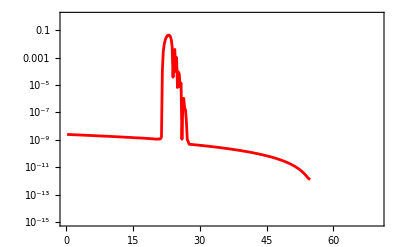

```mathematica
ListLogPlot[PN0,PlotRange->{{0,70},{10^-15,1}},Joined->True,Frame->True,PlotStyle->Red]
```

```mathematica
kmpc=Solve[0.05/Mpc==((a[Ne] H[Ne])/cs)/.solNe1/.Ne->0,Mpc][[1]][[1,2]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

549.29

```mathematica
Pkc=Table[{(kmpc((H[Ne]a[Ne])/cs)/.solNe1/.{Ne->NeHE[[i]]})[[1]],(k[[i]]^3/(2*Pi^2)*Abs[u[Ne]/(z[Ne]/.solNe1)]^2/.MSol[[i]]/.Ne->NeEnd[[i]])[[1]][[1]]},{i,1,iMax}]
```

{{0.060974,2.43028×10^-9},{0.0743561,2.4143×10^-9},{0.0906748,2.39982×10^-9},{0.110574,2.3851×10^-9},{0.13484,2.36982×10^-9},{0.164431,2.35469×10^-9},{0.200514,2.33945×10^-9},{0.244514,2.3246×10^-9},{0.298167,2.30876×10^-9},{0.363592,2.29281×10^-9},{0.443369,2.27671×10^-9},{0.540649,2.26149×10^-9},{0.659268,2.24726×10^-9},{0.803909,2.23324×10^-9},{0.980278,2.21962×10^-9},{1.19533,2.20596×10^-9},{1.45756,2.1921×10^-9},{1.77731,2.17756×10^-9},{2.16718,2.16215×10^-9},{2.64256,2.14592×10^-9},{3.2222,2.12957×10^-9},{3.92896,2.11399×10^-9},{4.79072,2.09975×10^-9},{5.84145,2.08626×10^-9},{7.12259,2.07322×10^-9},{8.68467,2.06073×10^-9},{10.5893,2.04793×10^-9},{12.9115,2.0348×10^-9},{15.7428,2.02041×10^-9},{19.195,2.00502×10^-9},{23.4039,1.98889×10^-9},{28.5357,1.97297×10^-9},{34.7924,1.95825×10^-9},{42.4208,1.9449×10^-9},{51.7213,1.9321×10^-9},{63.0606,1.91991×10^-9},{76.8853,1.90805×10^-9},{93.7403,1.89587×10^-9},{114.289,1.88299×10^-9},{139.342,1.86894×10^-9},{169.886,1.8537×10^-9},{207.123,1.83787×10^-9},{252.521,1.82263×10^-9},{307.867,1.80888×10^-9},{375.34,1.79628×10^-9},{457.599,1.78419×10^-9},{557.881,1.77283×10^-9},{680.135,1.76158×10^-9},{829.174,1.74983×10^-9},{1010.86,1.73723×10^-9},{1232.36,1.72325×10^-9},{1502.38,1.70812×10^-9},{1831.54,1.69274×10^-9},{2232.81,1.67832×10^-9},{2721.97,1.66554×10^-9},{3318.28,1.65363×10^-9},{4045.18,1.64228×10^-9},{4931.29,1.63154×10^-9},{6011.45,1.62069×10^-9},{7328.16,1.60941×10^-9},{8933.2,1.59693×10^-9},{10889.7,1.58335×10^-9},{13274.6,1.56901×10^-9},{16181.7,1.55493×10^-9},{19725.2,1.54197×10^-9},{24044.6,1.53012×10^-9},{29309.6,1.51867×10^-9},{35727.1,1.5079×10^-9},{43549.4,1.49753×10^-9},{53084.,1.48709×10^-9},{64705.4,1.47598×10^-9},{78870.4,1.46313×10^-9},{96135.5,1.44844×10^-9},{117179.,1.43195×10^-9},{142827.,1.41532×10^-9},{174088.,1.40108×10^-9},{212189.,1.39011×10^-9},{258627.,1.38039×10^-9},{315224.,1.37168×10^-9},{384205.,1.36402×10^-9},{468276.,1.35596×10^-9},{570739.,1.34634×10^-9},{695615.,1.33493×10^-9},{847807.,1.32172×10^-9},{1.03329×10^6,1.30917×10^-9},{1.25933×10^6,1.29935×10^-9},{1.53481×10^6,1.29008×10^-9},{1.87052×10^6,1.27539×10^-9},{2.27965×10^6,1.26549×10^-9},{2.77823×10^6,1.25311×10^-9},{3.38581×10^6,1.23887×10^-9},{4.12622×10^6,1.22983×10^-9},{5.02847×10^6,1.21603×10^-9},{6.12792×10^6,1.20548×10^-9},{7.46765×10^6,1.19464×10^-9},{9.10014×10^6,1.1728×10^-9},{1.10893×10^7,1.16459×10^-9},{1.3513×10^7,1.16173×10^-9},{1.64661×10^7,1.12921×10^-9},{2.00641×10^7,1.12496×10^-9},{2.44476×10^7,1.13741×10^-9},{2.97877×10^7,1.10123×10^-9},{3.62929×10^7,1.11783×10^-9},{4.42163×10^7,1.14014×10^-9},{5.38659×10^7,1.1032×10^-9},{6.56158×10^7,1.2025×10^-9},{7.992×10^7,1.54419×10^-9},{9.7328×10^7,0.000109252},{1.18501×10^8,0.00264555},{1.44232×10^8,0.0085775},{1.75441×10^8,0.0167789},{2.13099×10^8,0.0261152},{2.54319×10^8,0.0345574},{3.00675×10^8,0.0422817},{3.59189×10^8,0.0434465},{4.32193×10^8,0.0422356},{5.22407×10^8,0.0337618},{6.33204×10^8,0.0204408},{7.68789×10^8,0.00622175},{9.34347×10^8,0.0000369749},{1.13625×10^9,0.00299252},{1.38228×10^9,0.00390907},{1.68197×10^9,0.000100323},{2.04692×10^9,0.000993275},{2.49127×10^9,6.47808×10^-6},{3.03221×10^9,0.0000883119},{3.69071×10^9,0.00006349},{4.49227×10^9,7.36942×10^-6},{5.46792×10^9,0.0000133346},{6.65547×10^9,1.08474×10^-9},{8.10085×10^9,3.19756×10^-7},{9.85999×10^9,1.0607×10^-6},{1.20009×10^10,2.05853×10^-7},{1.46064×10^10,1.51428×10^-7},{1.77773×10^10,2.19066×10^-8},{2.1636×10^10,9.95662×10^-10},{2.63316×10^10,7.53948×10^-10},{3.20455×10^10,4.76643×10^-10},{3.89983×10^10,4.54441×10^-10},{4.74584×10^10,4.55064×10^-10},{5.77521×10^10,4.46549×10^-10},{7.02767×10^10,4.44774×10^-10},{8.55152×10^10,4.37415×10^-10},{1.04055×10^11,4.28238×10^-10},{1.26611×10^11,4.2306×10^-10},{1.54053×10^11,4.16312×10^-10},{1.87436×10^11,4.10661×10^-10},{2.28047×10^11,4.05255×10^-10},{2.77448×10^11,3.99294×10^-10},{3.3754×10^11,3.91252×10^-10},{4.10635×10^11,3.86505×10^-10},{4.99542×10^11,3.82021×10^-10},{6.07679×10^11,3.73193×10^-10},{7.392×10^11,3.68506×10^-10},{8.99156×10^11,3.63414×10^-10},{1.09369×10^12,3.55531×10^-10},{1.33026×10^12,3.509×10^-10},{1.61794×10^12,3.44516×10^-10},{1.96777×10^12,3.38425×10^-10},{2.39316×10^12,3.33297×10^-10},{2.91039×10^12,3.27747×10^-10},{3.53928×10^12,3.21992×10^-10},{4.3039×10^12,3.16217×10^-10},{5.23349×10^12,3.10332×10^-10},{6.36362×10^12,3.05139×10^-10},{7.73748×10^12,3.00425×10^-10},{9.40756×10^12,2.95039×10^-10},{1.14376×10^13,2.8853×10^-10},{1.39052×10^13,2.82881×10^-10},{1.69043×10^13,2.78436×10^-10},{2.05495×10^13,2.74819×10^-10},{2.49795×10^13,2.69212×10^-10},{3.03632×10^13,2.62349×10^-10},{3.69054×10^13,2.56853×10^-10},{4.48551×10^13,2.53304×10^-10},{5.45146×10^13,2.50067×10^-10},{6.62509×10^13,2.44252×10^-10},{8.05099×10^13,2.37498×10^-10},{9.78327×10^13,2.32329×10^-10},{1.18876×10^14,2.29344×10^-10},{1.44439×10^14,2.26246×10^-10},{1.75488×10^14,2.20263×10^-10},{2.132×10^14,2.13847×10^-10},{2.59002×10^14,2.09051×10^-10},{3.14624×10^14,2.06701×10^-10},{3.8217×10^14,2.03816×10^-10},{4.64188×10^14,1.98181×10^-10},{5.63772×10^14,1.92438×10^-10},{6.84677×10^14,1.87913×10^-10},{8.31457×10^14,1.85272×10^-10},{1.00963×10^15,1.81714×10^-10},{1.22591×10^15,1.76683×10^-10},{1.48841×10^15,1.71961×10^-10},{1.807×10^15,1.67846×10^-10},{2.1936×10^15,1.64848×10^-10},{2.66273×10^15,1.61264×10^-10},{3.23193×10^15,1.56801×10^-10},{3.92249×10^15,1.52569×10^-10},{4.76022×10^15,1.48807×10^-10},{5.77638×10^15,1.45617×10^-10},{7.00887×10^15,1.41967×10^-10},{8.50358×10^15,1.3787×10^-10},{1.03161×10^16,1.34012×10^-10},{1.25138×10^16,1.3059×10^-10},{1.51783×10^16,1.27584×10^-10},{1.84083×10^16,1.24209×10^-10},{2.23235×10^16,1.20284×10^-10},{2.70685×10^16,1.16636×10^-10},{3.28186×10^16,1.13506×10^-10},{3.97859×10^16,1.10781×10^-10},{4.82268×10^16,1.07525×10^-10},{5.84517×10^16,1.03779×10^-10},{7.0836×10^16,1.00384×10^-10},{8.58337×10^16,9.76343×10^-11},{1.03994×10^17,9.52808×10^-11},{1.25979×10^17,9.22924×10^-11},{1.52592×10^17,8.87729×10^-11},{1.84801×10^17,8.56547×10^-11},{2.23776×10^17,8.30994×10^-11},{2.7093×10^17,8.07826×10^-11},{3.2797×10^17,7.78908×10^-11},{3.96954×10^17,7.47984×10^-11},{4.80368×10^17,7.20107×10^-11},{5.8121×10^17,6.96978×10^-11},{7.03092×10^17,6.74901×10^-11},{8.50373×10^17,6.48573×10^-11},{1.0283×10^18,6.214×10^-11},{1.24322×10^18,5.9681×10^-11},{1.50274×10^18,5.75775×10^-11},{1.81604×10^18,5.55377×10^-11},{2.19418×10^18,5.31963×10^-11},{2.65042×10^18,5.0822×10^-11},{3.20072×10^18,4.8589×10^-11},{3.86428×10^18,4.6583×10^-11},{4.66414×10^18,4.45953×10^-11},{5.62797×10^18,4.24879×10^-11},{6.78896×10^18,4.04474×10^-11},{8.1869×10^18,3.85217×10^-11},{9.86947×10^18,3.67252×10^-11},{1.18937×10^19,3.49192×10^-11},{1.43279×10^19,3.30907×10^-11},{1.72537×10^19,3.13361×10^-11},{2.07685×10^19,2.96408×10^-11},{2.49886×10^19,2.80792×10^-11},{3.00524×10^19,2.65275×10^-11},{3.61249×10^19,2.48881×10^-11},{4.34021×10^19,2.33721×10^-11},{5.21167×10^19,2.20338×10^-11},{6.25445×10^19,2.06354×10^-11},{7.50118×10^19,1.91714×10^-11},{8.99039×10^19,1.78787×10^-11},{1.07675×10^20,1.67096×10^-11},{1.28858×10^20,1.55184×10^-11},{1.54079×10^20,1.42548×10^-11},{1.84068×10^20,1.31641×10^-11},{2.19675×10^20,1.21989×10^-11},{2.61884×10^20,1.11906×10^-11},{3.11834×10^20,1.01331×10^-11},{3.70829×10^20,9.23166×10^-12},{4.40351×10^20,8.40277×10^-12},{5.22066×10^20,7.53555×10^-12},{6.17836×10^20,6.73262×10^-12},{7.29704×10^20,6.02301×10^-12},{8.59856×10^20,5.32359×10^-12},{1.01058×10^21,4.68222×10^-12},{1.18415×10^21,4.0861×10^-12},{1.38266×10^21,3.5337×10^-12},{1.6078×10^21,3.02896×10^-12},{1.86043×10^21,2.56938×10^-12},{2.13984×10^21,2.15214×10^-12},{2.44306×10^21,1.78154×10^-12},{2.76334×10^21,1.53464×10^-12},{3.08802×10^21,1.35726×10^-12},{3.39495×10^21,1.22736×10^-12}}

```mathematica
Export["PkB.dat",Pkc];
```

```mathematica
Pkc=Import["PkB.dat"];
c1=Interpolation[Pkc,InterpolationOrder->1]
AA=LogLogPlot[{c1[x]},{x,0.0634257151149378,6.242598573013641*^19},PlotRange->{{0.001,4*10^22},{10^-13,1}},Frame->True,FrameStyle->Thick,FrameTicksStyle->Black,PlotStyle->{Purple},LabelStyle->Directive[24,Bold,Black,FontFamily->"Book Antiqua"],ImageSize->{600,400},AspectRatio->Full,RotateLabel->False,Axes->False,FrameLabel->{"K/Mpc^-1","P_R"}]
```

InterpolatingFunction[…]

```mathematica
InterpolatingFunction[…];
```

```mathematica
c1[0.05kmpc]
```

1.97629×10^-9

```mathematica
AA1=ListLogLogPlot[Pkc,PlotRange->{{0.05,4*10^22},{10^-13,1}},Joined->True,Frame->True,FrameStyle->Thick,FrameTicksStyle->Black,PlotStyle->Darker[Green],LabelStyle->Directive[24,Bold,Black,FontFamily->"Book Antiqua"],ImageSize->{600,400},AspectRatio->Full,RotateLabel->False,Axes->False,FrameLabel->{"K/Mpc^-1","P_R"}]
```

```mathematica
ss=-Graphics-;
```

```mathematica
fback=Show[{LogLogPlot[{ns0[Ne]},{Ne,1,10},PlotRange->{{10^-4,10^24},{10^-12,10^0}},PlotStyle->{Black,Thickness[0.005]},Frame-> True,FrameLabel->{"M/M_⊙","f_Pbh"},LabelStyle->Directive[22,Bold,FontFamily->"Book Antiqua"],ImageSize->{600,400},AspectRatio->Full],Graphics[{Texture[ss],EdgeForm[Black],Polygon[{{-9.1,-27.56},{55.2,-27.56},{55.2,0.1},{-9.1,0.1}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},ImageSize->{600,400},AspectRatio->Full]},Axes->False,RotateLabel->True]
```

```mathematica
Show[fback,AA]
```

```mathematica
Mkc=Table[(1/((1.9*10^6)^-2)*(1/(√3))^3/0.2*(106.75/10.75)^(-1/6)*(kmpc*k[[i]])^-2)[[1]],{i,1,iMax}];
```

```mathematica
PRc=Interpolation[Pkc,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
qend=PRc[[1,1,2]]
```

3.39495×10^21

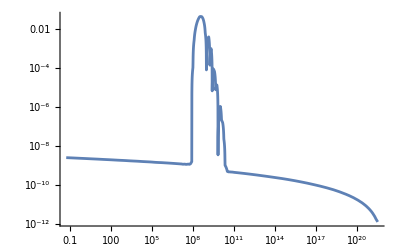

```mathematica
LogLogPlot[PRc[x],{x,0.05,qend},PlotRange->All]
```

```mathematica
(*WorkingPrecision->15.,Method->"TrapezoidalRule"*)
```

```mathematica
For[i=1,i≤ iMax,i++,
si[i]=NIntegrate[16/81*1/q*(q/(k[[i]]*kmpc))^4 Exp[-q^2/(k[[i]]*kmpc)^2]PRc[q],{q,0,PRc[[1,1,2]]}];
]
```

```mathematica
Beep[]
```

```mathematica
sigma=Table[si[i],{i,1,iMax}]//N;
```

```mathematica
δc=0.4;
```

```mathematica
(*For[i=1,i≤ iMax,i++,
B[i]=√(1/(2Pi))(sigma[[i]])^(1/2)/δc Exp[(- δc^2)/(2*sigma[[i]])]]*)
```

```mathematica
For[i=1,i≤ iMax,i++,
B[i]=1/2 Erfc[δc/(√(2*sigma[[i]]))]]
```

```mathematica
f=Table[B[i]/(1.84*10^-8)*((1/(√3))^3/0.2)^(3/2)*(10.75/106.75)^(1/4)*(Mkc[[i]])^(-1/2),{i,1,iMax}];
```

```mathematica
ac=Table[{Mkc[[i]],f[[i]][[1]]},{i,1,iMax}];
```

```mathematica
Export["FPBHB.dat",ac];
```

```mathematica
ac=Import["FPBHB.dat"];
```

```mathematica
Max[f]
```

0.0181724

```mathematica
fc=ListLogLogPlot[ac,Joined->True,Frame->True,Axes->False,PlotRange->{{10^-18,10^4},{10^-5,1}},PlotStyle->{Purple,Thickness[0.002]}]
```

```mathematica
s1=Interpolation[ac,InterpolationOrder->2]
fc=LogLogPlot[s1[x],{x,3.86*^-39,7.0121*^14},Frame->True,Axes->False,PlotRange->{{10^-18,10^4},{10^-5,10^0}},PlotStyle->Red,FillingStyle->Black,ImageSize->{400,300}]
```

InterpolatingFunction[…]

```mathematica
fb=-Graphics-;
```

```mathematica
fback=Show[{LogLogPlot[{ns0[Ne]},{Ne,1,10},PlotRange->{{10^-18,10^4},{10^-5,10^0}},PlotStyle->{Black,Thickness[0.005]},Frame-> True,FrameLabel->{"M/M_⊙","f_Pbh"},LabelStyle->Directive[22,Bold,FontFamily->"Book Antiqua"],ImageSize->{600,400},AspectRatio->Full],Graphics[{Texture[fb],EdgeForm[Black],Polygon[{{-41.5,-11.55},{9.3,-11.55},{9.3,0},{-41.5,0}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},ImageSize->{600,400},AspectRatio->Full]},Axes->False,RotateLabel->True]
```

```mathematica
fpbh=Show[fback,fc,ImageSize->{600,400}]
```

```mathematica
Show[back,fc,ImageSize->{600,400}]
```

```mathematica
data2=Table[{i,(kmpc((a[Ne] H[Ne])/cs)/.solNe1/.{Ne->NeHE[[i]]})[[1]],NeHE[[i]],NeBD[[i]],Mkc[[i]],PN0[[i]][[2]],f[[i]]},{i,1,iMax}];
```

```mathematica
pr=data2[[All,6]];
```

```mathematica
Position[pr,Max[pr]][[1]][[1]]
```

115

```mathematica
Length[Pkc]
```

274

```mathematica
Pkc[[Position[pr,Max[pr]][[1]][[1]],2]]
```

0.0434465

```mathematica
Mkc[[Position[pr,Max[pr]][[1]][[1]]]]
```

0.0000183649

```mathematica
ScientificForm[0.000018364909643768122]
```

1.83649×10^-5

```mathematica
f[[Position[pr,Max[pr]][[1]][[1]]]]
```

{0.00158505}

```mathematica
kpeak=(kmpc((a[Ne] H[Ne])/cs)/.solNe1/.{Ne->NeHE[[Position[pr,Max[pr]][[1]][[1]]]]})
```

{3.59189×10^8}

```mathematica
mytab2=Text@Grid[Prepend[data2,{"i","K","N","NBD","M(k)/M_o","P_R","f"}],Frame->All,Alignment->{Center},ItemSize->{10},Frame->Darker[Gray,.6],ItemStyle->14,Background->{Automatic,{1-> Green,Position[pr,Max[pr]][[1]][[1]]+1->Yellow}}]
```

i | K | N | NBD | M(k)/M_o | P_R | f
1 | 0.060974 | 0.2 | -4.8 | 6.37304×10^14 | 2.43028×10^-9 | {0.}
2 | 0.0743561 | 0.4 | -4.6 | 4.28551×10^14 | 2.4143×10^-9 | {0.}
3 | 0.0906748 | 0.6 | -4.4 | 2.88179×10^14 | 2.39982×10^-9 | {0.}
4 | 0.110574 | 0.8 | -4.2 | 1.93788×10^14 | 2.3851×10^-9 | {0.}
5 | 0.13484 | 1. | -4. | 1.30315×10^14 | 2.36982×10^-9 | {0.}
6 | 0.164431 | 1.2 | -3.8 | 8.76332×10^13 | 2.35469×10^-9 | {0.}
7 | 0.200514 | 1.4 | -3.6 | 5.89314×10^13 | 2.33945×10^-9 | {0.}
8 | 0.244514 | 1.6 | -3.4 | 3.96305×10^13 | 2.3246×10^-9 | {0.}
9 | 0.298167 | 1.8 | -3.2 | 2.66512×10^13 | 2.30876×10^-9 | {0.}
10 | 0.363592 | 2. | -3. | 1.79229×10^13 | 2.29281×10^-9 | {0.}
11 | 0.443369 | 2.2 | -2.8 | 1.20533×10^13 | 2.27671×10^-9 | {0.}
12 | 0.540649 | 2.4 | -2.6 | 8.10598×10^12 | 2.26149×10^-9 | {0.}
13 | 0.659268 | 2.6 | -2.4 | 5.45144×10^12 | 2.24726×10^-9 | {0.}
14 | 0.803909 | 2.8 | -2.2 | 3.66624×10^12 | 2.23324×10^-9 | {0.}
15 | 0.980278 | 3. | -2. | 2.46568×10^12 | 2.21962×10^-9 | {0.}
16 | 1.19533 | 3.2 | -1.8 | 1.65828×10^12 | 2.20596×10^-9 | {0.}
17 | 1.45756 | 3.4 | -1.6 | 1.11527×10^12 | 2.1921×10^-9 | {0.}
18 | 1.77731 | 3.6 | -1.4 | 7.50086×10^11 | 2.17756×10^-9 | {0.}
19 | 2.16718 | 3.8 | -1.2 | 5.04482×10^11 | 2.16215×10^-9 | {0.}
20 | 2.64256 | 4. | -1. | 3.39301×10^11 | 2.14592×10^-9 | {0.}
21 | 3.2222 | 4.2 | -0.8 | 2.28208×10^11 | 2.12957×10^-9 | {0.}
22 | 3.92896 | 4.4 | -0.6 | 1.5349×10^11 | 2.11399×10^-9 | {0.}
23 | 4.79072 | 4.6 | -0.4 | 1.03237×10^11 | 2.09975×10^-9 | {0.}
24 | 5.84145 | 4.8 | -0.2 | 6.94375×10^10 | 2.08626×10^-9 | {0.}
25 | 7.12259 | 5. | 0. | 4.67045×10^10 | 2.07322×10^-9 | {0.}
26 | 8.68467 | 5.2 | 0.2 | 3.14144×10^10 | 2.06073×10^-9 | {0.}
27 | 10.5893 | 5.4 | 0.4 | 2.11302×10^10 | 2.04793×10^-9 | {0.}
28 | 12.9115 | 5.6 | 0.6 | 1.4213×10^10 | 2.0348×10^-9 | {0.}
29 | 15.7428 | 5.8 | 0.8 | 9.56027×10^9 | 2.02041×10^-9 | {0.}
30 | 19.195 | 6. | 1. | 6.43074×10^9 | 2.00502×10^-9 | {0.}
31 | 23.4039 | 6.2 | 1.2 | 4.32571×10^9 | 1.98889×10^-9 | {0.}
32 | 28.5357 | 6.4 | 1.4 | 2.90977×10^9 | 1.97297×10^-9 | {0.}
33 | 34.7924 | 6.6 | 1.6 | 1.95734×10^9 | 1.95825×10^-9 | {0.}
34 | 42.4208 | 6.8 | 1.8 | 1.31667×10^9 | 1.9449×10^-9 | {0.}
35 | 51.7213 | 7. | 2. | 8.85719×10^8 | 1.9321×10^-9 | {0.}
36 | 63.0606 | 7.2 | 2.2 | 5.95826×10^8 | 1.91991×10^-9 | {0.}
37 | 76.8853 | 7.4 | 2.4 | 4.00819×10^8 | 1.90805×10^-9 | {0.}
38 | 93.7403 | 7.6 | 2.6 | 2.69639×10^8 | 1.89587×10^-9 | {0.}
39 | 114.289 | 7.8 | 2.8 | 1.81394×10^8 | 1.88299×10^-9 | {0.}
40 | 139.342 | 8. | 3. | 1.22031×10^8 | 1.86894×10^-9 | {0.}
41 | 169.886 | 8.2 | 3.2 | 8.20958×10^7 | 1.8537×10^-9 | {0.}
42 | 207.123 | 8.4 | 3.4 | 5.52304×10^7 | 1.83787×10^-9 | {0.}
43 | 252.521 | 8.6 | 3.6 | 3.71571×10^7 | 1.82263×10^-9 | {0.}
44 | 307.867 | 8.8 | 3.8 | 2.49983×10^7 | 1.80888×10^-9 | {0.}
45 | 375.34 | 9. | 4. | 1.68184×10^7 | 1.79628×10^-9 | {0.}
46 | 457.599 | 9.2 | 4.2 | 1.13153×10^7 | 1.78419×10^-9 | {0.}
47 | 557.881 | 9.4 | 4.4 | 7.61295×10^6 | 1.77283×10^-9 | {0.}
48 | 680.135 | 9.6 | 4.6 | 5.12207×10^6 | 1.76158×10^-9 | {0.}
49 | 829.174 | 9.8 | 4.8 | 3.44623×10^6 | 1.74983×10^-9 | {0.}
50 | 1010.86 | 10. | 5. | 2.31873×10^6 | 1.73723×10^-9 | {0.}
51 | 1232.36 | 10.2 | 5.2 | 1.56013×10^6 | 1.72325×10^-9 | {0.}
52 | 1502.38 | 10.4 | 5.4 | 1.04973×10^6 | 1.70812×10^-9 | {0.}
53 | 1831.54 | 10.6 | 5.6 | 706320. | 1.69274×10^-9 | {0.}
54 | 2232.81 | 10.8 | 5.8 | 475260. | 1.67832×10^-9 | {0.}
55 | 2721.97 | 11. | 6. | 319792. | 1.66554×10^-9 | {0.}
56 | 3318.28 | 11.2 | 6.2 | 215184. | 1.65363×10^-9 | {0.}
57 | 4045.18 | 11.4 | 6.4 | 144797. | 1.64228×10^-9 | {0.}
58 | 4931.29 | 11.6 | 6.6 | 97435. | 1.63154×10^-9 | {0.}
59 | 6011.45 | 11.8 | 6.8 | 65565.8 | 1.62069×10^-9 | {0.}
60 | 7328.16 | 12. | 7. | 44121.1 | 1.60941×10^-9 | {0.}
61 | 8933.2 | 12.2 | 7.2 | 29690.8 | 1.59693×10^-9 | {0.}
62 | 10889.7 | 12.4 | 7.4 | 19980.4 | 1.58335×10^-9 | {0.}
63 | 13274.6 | 12.6 | 7.6 | 13446. | 1.56901×10^-9 | {0.}
64 | 16181.7 | 12.8 | 7.8 | 9048.74 | 1.55493×10^-9 | {0.}
65 | 19725.2 | 13. | 8. | 6089.62 | 1.54197×10^-9 | {0.}
66 | 24044.6 | 13.2 | 8.2 | 4098.26 | 1.53012×10^-9 | {0.}
67 | 29309.6 | 13.4 | 8.4 | 2758.14 | 1.51867×10^-9 | {0.}
68 | 35727.1 | 13.6 | 8.6 | 1856.26 | 1.5079×10^-9 | {0.}
69 | 43549.4 | 13.8 | 8.8 | 1249.31 | 1.49753×10^-9 | {0.}
70 | 53084. | 14. | 9. | 840.83 | 1.48709×10^-9 | {0.}
71 | 64705.4 | 14.2 | 9.2 | 565.918 | 1.47598×10^-9 | {0.}
72 | 78870.4 | 14.4 | 9.4 | 380.896 | 1.46313×10^-9 | {0.}
73 | 96135.5 | 14.6 | 9.6 | 256.37 | 1.44844×10^-9 | {0.}
74 | 117179. | 14.8 | 9.8 | 172.558 | 1.43195×10^-9 | {0.}
75 | 142827. | 15. | 10. | 116.148 | 1.41532×10^-9 | {0.}
76 | 174088. | 15.2 | 10.2 | 78.1801 | 1.40108×10^-9 | {0.}
77 | 212189. | 15.4 | 10.4 | 52.6245 | 1.39011×10^-9 | {0.}
78 | 258627. | 15.6 | 10.6 | 35.4232 | 1.38039×10^-9 | {0.}
79 | 315224. | 15.8 | 10.8 | 23.8449 | 1.37168×10^-9 | {0.}
80 | 384205. | 16. | 11. | 16.0513 | 1.36402×10^-9 | {0.}
81 | 468276. | 16.2 | 11.2 | 10.8051 | 1.35596×10^-9 | {0.}
82 | 570739. | 16.4 | 11.4 | 7.27377 | 1.34634×10^-9 | {0.}
83 | 695615. | 16.6 | 11.6 | 4.89663 | 1.33493×10^-9 | {0.}
84 | 847807. | 16.8 | 11.8 | 3.29641 | 1.32172×10^-9 | {0.}
85 | 1.03329×10^6 | 17. | 12. | 2.21919 | 1.30917×10^-9 | {0.}
86 | 1.25933×10^6 | 17.2 | 12.2 | 1.49402 | 1.29935×10^-9 | {0.}
87 | 1.53481×10^6 | 17.4 | 12.4 | 1.00584 | 1.29008×10^-9 | {0.}
88 | 1.87052×10^6 | 17.6 | 12.6 | 0.677187 | 1.27539×10^-9 | {0.}
89 | 2.27965×10^6 | 17.8 | 12.8 | 0.455931 | 1.26549×10^-9 | {0.}
90 | 2.77823×10^6 | 18. | 13. | 0.306972 | 1.25311×10^-9 | {0.}
91 | 3.38581×10^6 | 18.2 | 13.2 | 0.206685 | 1.23887×10^-9 | {0.}
92 | 4.12622×10^6 | 18.4 | 13.4 | 0.139165 | 1.22983×10^-9 | {0.}
93 | 5.02847×10^6 | 18.6 | 13.6 | 0.0937053 | 1.21603×10^-9 | {0.}
94 | 6.12792×10^6 | 18.8 | 13.8 | 0.0630971 | 1.20548×10^-9 | {0.}
95 | 7.46765×10^6 | 19. | 14. | 0.0424881 | 1.19464×10^-9 | {0.}
96 | 9.10014×10^6 | 19.2 | 14.2 | 0.0286114 | 1.1728×10^-9 | {0.}
97 | 1.10893×10^7 | 19.4 | 14.4 | 0.0192675 | 1.16459×10^-9 | {0.}
98 | 1.3513×10^7 | 19.6 | 14.6 | 0.0129757 | 1.16173×10^-9 | {0.}
99 | 1.64661×10^7 | 19.8 | 14.8 | 0.00873884 | 1.12921×10^-9 | {0.}
100 | 2.00641×10^7 | 20. | 15. | 0.00588569 | 1.12496×10^-9 | {0.}
101 | 2.44476×10^7 | 20.2 | 15.2 | 0.00396428 | 1.13741×10^-9 | {0.}
102 | 2.97877×10^7 | 20.4 | 15.4 | 0.0026703 | 1.10123×10^-9 | {0.}
103 | 3.62929×10^7 | 20.6 | 15.6 | 0.00179884 | 1.11783×10^-9 | {0.}
104 | 4.42163×10^7 | 20.8 | 15.8 | 0.00121191 | 1.14014×10^-9 | {0.}
105 | 5.38659×10^7 | 21. | 16. | 0.000816597 | 1.1032×10^-9 | {0.}
106 | 6.56158×10^7 | 21.2 | 16.2 | 0.000550324 | 1.2025×10^-9 | {1.65637×10^-236}
107 | 7.992×10^7 | 21.4 | 16.4 | 0.000370958 | 1.54419×10^-9 | {1.96243×10^-87}
108 | 9.7328×10^7 | 21.6 | 16.6 | 0.000250127 | 0.000109252 | {5.92729×10^-39}
109 | 1.18501×10^8 | 21.8 | 16.8 | 0.000168729 | 0.00264555 | {1.99707×10^-19}
110 | 1.44232×10^8 | 22. | 17. | 0.000113897 | 0.0085775 | {2.59106×10^-10}
111 | 1.75441×10^8 | 22.2 | 17.2 | 0.0000769792 | 0.0167789 | {0.0000106535}
112 | 2.13099×10^8 | 22.4 | 17.4 | 0.0000521763 | 0.0261152 | {0.00227738}
113 | 2.54319×10^8 | 22.6 | 17.6 | 0.0000366335 | 0.0345574 | {0.0181724}
114 | 3.00675×10^8 | 22.8 | 17.8 | 0.0000262084 | 0.0422817 | {0.0172977}
115 | 3.59189×10^8 | 23. | 18. | 0.0000183649 | 0.0434465 | {0.00158505}
116 | 4.32193×10^8 | 23.2 | 18.2 | 0.0000126847 | 0.0422356 | {4.1015×10^-6}
117 | 5.22407×10^8 | 23.4 | 18.4 | 8.68196×10^-6 | 0.0337618 | {3.3947×10^-11}
118 | 6.33204×10^8 | 23.6 | 18.6 | 5.90947×10^-6 | 0.0204408 | {3.38068×10^-20}
119 | 7.68789×10^8 | 23.8 | 18.8 | 4.00886×10^-6 | 0.00622175 | {4.90494×10^-35}
120 | 9.34347×10^8 | 24. | 19. | 2.71406×10^-6 | 0.0000369749 | {9.71946×10^-59}
121 | 1.13625×10^9 | 24.2 | 19.2 | 1.83523×10^-6 | 0.00299252 | {3.21113×10^-97}
122 | 1.38228×10^9 | 24.4 | 19.4 | 1.24006×10^-6 | 0.00390907 | {1.86258×10^-162}
123 | 1.68197×10^9 | 24.6 | 19.6 | 8.37528×10^-7 | 0.000100323 | {3.32298×10^-278}
124 | 2.04692×10^9 | 24.8 | 19.8 | 5.65501×10^-7 | 0.000993275 | {0.}
125 | 2.49127×10^9 | 25. | 20. | 3.81764×10^-7 | 6.47808×10^-6 | {0.}
126 | 3.03221×10^9 | 25.2 | 20.2 | 2.57701×10^-7 | 0.0000883119 | {0.}
127 | 3.69071×10^9 | 25.4 | 20.4 | 1.73947×10^-7 | 0.00006349 | {0.}
128 | 4.49227×10^9 | 25.6 | 20.6 | 1.1741×10^-7 | 7.36942×10^-6 | {0.}
129 | 5.46792×10^9 | 25.8 | 20.8 | 7.92486×10^-8 | 0.0000133346 | {0.}
130 | 6.65547×10^9 | 26. | 21. | 5.34906×10^-8 | 1.08474×10^-9 | {0.}
131 | 8.10085×10^9 | 26.2 | 21.2 | 3.61056×10^-8 | 3.19756×10^-7 | {0.}
132 | 9.85999×10^9 | 26.4 | 21.4 | 2.43715×10^-8 | 1.0607×10^-6 | {0.}
133 | 1.20009×10^10 | 26.6 | 21.6 | 1.64515×10^-8 | 2.05853×10^-7 | {0.}
134 | 1.46064×10^10 | 26.8 | 21.8 | 1.11057×10^-8 | 1.51428×10^-7 | {0.}
135 | 1.77773×10^10 | 27. | 22. | 7.49731×10^-9 | 2.19066×10^-8 | {0.}
136 | 2.1636×10^10 | 27.2 | 22.2 | 5.06154×10^-9 | 9.95662×10^-10 | {0.}
137 | 2.63316×10^10 | 27.4 | 22.4 | 3.41728×10^-9 | 7.53948×10^-10 | {0.}
138 | 3.20455×10^10 | 27.6 | 22.6 | 2.30728×10^-9 | 4.76643×10^-10 | {0.}
139 | 3.89983×10^10 | 27.8 | 22.8 | 1.55791×10^-9 | 4.54441×10^-10 | {0.}
140 | 4.74584×10^10 | 28. | 23. | 1.05198×10^-9 | 4.55064×10^-10 | {0.}
141 | 5.77521×10^10 | 28.2 | 23.2 | 7.10394×10^-10 | 4.46549×10^-10 | {0.}
142 | 7.02767×10^10 | 28.4 | 23.4 | 4.79747×10^-10 | 4.44774×10^-10 | {0.}
143 | 8.55152×10^10 | 28.6 | 23.6 | 3.24003×10^-10 | 4.37415×10^-10 | {0.}
144 | 1.04055×10^11 | 28.8 | 23.8 | 2.1883×10^-10 | 4.28238×10^-10 | {0.}
145 | 1.26611×10^11 | 29. | 24. | 1.47805×10^-10 | 4.2306×10^-10 | {0.}
146 | 1.54053×10^11 | 29.2 | 24.2 | 9.98384×10^-11 | 4.16312×10^-10 | {0.}
147 | 1.87436×10^11 | 29.4 | 24.4 | 6.74418×10^-11 | 4.10661×10^-10 | {0.}
148 | 2.28047×10^11 | 29.6 | 24.6 | 4.55604×10^-11 | 4.05255×10^-10 | {0.}
149 | 2.77448×10^11 | 29.8 | 24.8 | 3.07803×10^-11 | 3.99294×10^-10 | {0.}
150 | 3.3754×10^11 | 30. | 25. | 2.07962×10^-11 | 3.91252×10^-10 | {0.}
151 | 4.10635×10^11 | 30.2 | 25.2 | 1.40515×10^-11 | 3.86505×10^-10 | {0.}
152 | 4.99542×10^11 | 30.4 | 25.4 | 9.49493×10^-12 | 3.82021×10^-10 | {0.}
153 | 6.07679×10^11 | 30.6 | 25.6 | 6.41634×10^-12 | 3.73193×10^-10 | {0.}
154 | 7.392×10^11 | 30.8 | 25.8 | 4.33623×10^-12 | 3.68506×10^-10 | {0.}
155 | 8.99156×10^11 | 31. | 26. | 2.93066×10^-12 | 3.63414×10^-10 | {0.}
156 | 1.09369×10^12 | 31.2 | 26.2 | 1.98084×10^-12 | 3.55531×10^-10 | {0.}
157 | 1.33026×10^12 | 31.4 | 26.4 | 1.33895×10^-12 | 3.509×10^-10 | {0.}
158 | 1.61794×10^12 | 31.6 | 26.6 | 9.05126×10^-13 | 3.44516×10^-10 | {0.}
159 | 1.96777×10^12 | 31.8 | 26.8 | 6.11907×10^-13 | 3.38425×10^-10 | {0.}
160 | 2.39316×10^12 | 32. | 27. | 4.13707×10^-13 | 3.33297×10^-10 | {0.}
161 | 2.91039×10^12 | 32.2 | 27.2 | 2.79726×10^-13 | 3.27747×10^-10 | {0.}
162 | 3.53928×10^12 | 32.4 | 27.4 | 1.8915×10^-13 | 3.21992×10^-10 | {0.}
163 | 4.3039×10^12 | 32.6 | 27.6 | 1.27912×10^-13 | 3.16217×10^-10 | {0.}
164 | 5.23349×10^12 | 32.8 | 27.8 | 8.65071×10^-14 | 3.10332×10^-10 | {0.}
165 | 6.36362×10^12 | 33. | 28. | 5.85095×10^-14 | 3.05139×10^-10 | {0.}
166 | 7.73748×10^12 | 33.2 | 28.2 | 3.95764×10^-14 | 3.00425×10^-10 | {0.}
167 | 9.40756×10^12 | 33.4 | 28.4 | 2.67721×10^-14 | 2.95039×10^-10 | {0.}
168 | 1.14376×10^13 | 33.6 | 28.6 | 1.81119×10^-14 | 2.8853×10^-10 | {0.}
169 | 1.39052×10^13 | 33.8 | 28.8 | 1.22541×10^-14 | 2.82881×10^-10 | {0.}
170 | 1.69043×10^13 | 34. | 29. | 8.29161×10^-15 | 2.78436×10^-10 | {0.}
171 | 2.05495×10^13 | 34.2 | 29.2 | 5.61091×10^-15 | 2.74819×10^-10 | {0.}
172 | 2.49795×10^13 | 34.4 | 29.4 | 3.79723×10^-15 | 2.69212×10^-10 | {0.}
173 | 3.03632×10^13 | 34.6 | 29.6 | 2.57005×10^-15 | 2.62349×10^-10 | {0.}
174 | 3.69054×10^13 | 34.8 | 29.8 | 1.73962×10^-15 | 2.56853×10^-10 | {0.}
175 | 4.48551×10^13 | 35. | 30. | 1.17764×10^-15 | 2.53304×10^-10 | {0.}
176 | 5.45146×10^13 | 35.2 | 30.2 | 7.97278×10^-16 | 2.50067×10^-10 | {0.}
177 | 6.62509×10^13 | 35.4 | 30.4 | 5.39823×10^-16 | 2.44252×10^-10 | {0.}
178 | 8.05099×10^13 | 35.6 | 30.6 | 3.65542×10^-16 | 2.37498×10^-10 | {0.}
179 | 9.78327×10^13 | 35.8 | 30.8 | 2.47553×10^-16 | 2.32329×10^-10 | {0.}
180 | 1.18876×10^14 | 36. | 31. | 1.67666×10^-16 | 2.29344×10^-10 | {0.}
181 | 1.44439×10^14 | 36.2 | 31.2 | 1.13571×10^-16 | 2.26246×10^-10 | {0.}
182 | 1.75488×10^14 | 36.4 | 31.4 | 7.69378×10^-17 | 2.20263×10^-10 | {0.}
183 | 2.132×10^14 | 36.6 | 31.6 | 5.21266×10^-17 | 2.13847×10^-10 | {0.}
184 | 2.59002×10^14 | 36.8 | 31.8 | 3.53207×10^-17 | 2.09051×10^-10 | {0.}
185 | 3.14624×10^14 | 37. | 32. | 2.39359×10^-17 | 2.06701×10^-10 | {0.}
186 | 3.8217×10^14 | 37.2 | 32.2 | 1.62227×10^-17 | 2.03816×10^-10 | {0.}
187 | 4.64188×10^14 | 37.4 | 32.4 | 1.09963×10^-17 | 1.98181×10^-10 | {0.}
188 | 5.63772×10^14 | 37.6 | 32.6 | 7.45466×10^-18 | 1.92438×10^-10 | {0.}
189 | 6.84677×10^14 | 37.8 | 32.8 | 5.05433×10^-18 | 1.87913×10^-10 | {0.}
190 | 8.31457×10^14 | 38. | 33. | 3.42733×10^-18 | 1.85272×10^-10 | {0.}
191 | 1.00963×10^15 | 38.2 | 33.2 | 2.32438×10^-18 | 1.81714×10^-10 | {0.}
192 | 1.22591×10^15 | 38.4 | 33.4 | 1.57658×10^-18 | 1.76683×10^-10 | {0.}
193 | 1.48841×10^15 | 38.6 | 33.6 | 1.06952×10^-18 | 1.71961×10^-10 | {0.}
194 | 1.807×10^15 | 38.8 | 33.8 | 7.2564×10^-19 | 1.67846×10^-10 | {0.}
195 | 2.1936×10^15 | 39. | 34. | 4.92401×10^-19 | 1.64848×10^-10 | {0.}
196 | 2.66273×10^15 | 39.2 | 34.2 | 3.34181×10^-19 | 1.61264×10^-10 | {0.}
197 | 3.23193×10^15 | 39.4 | 34.4 | 2.26836×10^-19 | 1.56801×10^-10 | {0.}
198 | 3.92249×10^15 | 39.6 | 34.6 | 1.53997×10^-19 | 1.52569×10^-10 | {0.}
199 | 4.76022×10^15 | 39.8 | 34.8 | 1.04564×10^-19 | 1.48807×10^-10 | {0.}
200 | 5.77638×10^15 | 40. | 35. | 7.10106×10^-20 | 1.45617×10^-10 | {0.}
201 | 7.00887×10^15 | 40.2 | 35.2 | 4.82325×10^-20 | 1.41967×10^-10 | {0.}
202 | 8.50358×10^15 | 40.4 | 35.4 | 3.27666×10^-20 | 1.3787×10^-10 | {0.}
203 | 1.03161×10^16 | 40.6 | 35.6 | 2.2264×10^-20 | 1.34012×10^-10 | {0.}
204 | 1.25138×10^16 | 40.8 | 35.8 | 1.51305×10^-20 | 1.3059×10^-10 | {0.}
205 | 1.51783×10^16 | 41. | 36. | 1.02846×10^-20 | 1.27584×10^-10 | {0.}
206 | 1.84083×10^16 | 41.2 | 36.2 | 6.99207×10^-21 | 1.24209×10^-10 | {0.}
207 | 2.23235×10^16 | 41.4 | 36.4 | 4.75457×10^-21 | 1.20284×10^-10 | {0.}
208 | 2.70685×10^16 | 41.6 | 36.6 | 3.23375×10^-21 | 1.16636×10^-10 | {0.}
209 | 3.28186×10^16 | 41.8 | 36.8 | 2.19986×10^-21 | 1.13506×10^-10 | {0.}
210 | 3.97859×10^16 | 42. | 37. | 1.49685×10^-21 | 1.10781×10^-10 | {0.}
211 | 4.82268×10^16 | 42.2 | 37.2 | 1.01873×10^-21 | 1.07525×10^-10 | {0.}
212 | 5.84517×10^16 | 42.4 | 37.4 | 6.93492×10^-22 | 1.03779×10^-10 | {0.}
213 | 7.0836×10^16 | 42.6 | 37.6 | 4.72201×10^-22 | 1.00384×10^-10 | {0.}
214 | 8.58337×10^16 | 42.8 | 37.8 | 3.21603×10^-22 | 9.76343×10^-11 | {0.}
215 | 1.03994×10^17 | 43. | 38. | 2.1909×10^-22 | 9.52808×10^-11 | {0.}
216 | 1.25979×10^17 | 43.2 | 38.2 | 1.49293×10^-22 | 9.22924×10^-11 | {0.}
217 | 1.52592×10^17 | 43.4 | 38.4 | 1.01759×10^-22 | 8.87729×10^-11 | {0.}
218 | 1.84801×10^17 | 43.6 | 38.6 | 6.9379×10^-23 | 8.56547×10^-11 | {0.}
219 | 2.23776×10^17 | 43.8 | 38.8 | 4.73161×10^-23 | 8.30994×10^-11 | {0.}
220 | 2.7093×10^17 | 44. | 39. | 3.22791×10^-23 | 8.07826×10^-11 | {0.}
221 | 3.2797×10^17 | 44.2 | 39.2 | 2.20276×10^-23 | 7.78908×10^-11 | {0.}
222 | 3.96954×10^17 | 44.4 | 39.4 | 1.50368×10^-23 | 7.47984×10^-11 | {0.}
223 | 4.80368×10^17 | 44.6 | 39.6 | 1.0268×10^-23 | 7.20107×10^-11 | {0.}
224 | 5.8121×10^17 | 44.8 | 39.8 | 7.01407×10^-24 | 6.96978×10^-11 | {0.}
225 | 7.03092×10^17 | 45. | 40. | 4.79304×10^-24 | 6.74901×10^-11 | {0.}
226 | 8.50373×10^17 | 45.2 | 40.2 | 3.27655×10^-24 | 6.48573×10^-11 | {0.}
227 | 1.0283×10^18 | 45.4 | 40.4 | 2.24074×10^-24 | 6.214×10^-11 | {0.}
228 | 1.24322×10^18 | 45.6 | 40.6 | 1.53299×10^-24 | 5.9681×10^-11 | {0.}
229 | 1.50274×10^18 | 45.8 | 40.8 | 1.04922×10^-24 | 5.75775×10^-11 | {0.}
230 | 1.81604×10^18 | 46. | 41. | 7.18427×10^-25 | 5.55377×10^-11 | {0.}
231 | 2.19418×10^18 | 46.2 | 41.2 | 4.92144×10^-25 | 5.31963×10^-11 | {0.}
232 | 2.65042×10^18 | 46.4 | 41.4 | 3.37293×10^-25 | 5.0822×10^-11 | {0.}
233 | 3.20072×10^18 | 46.6 | 41.6 | 2.31281×10^-25 | 4.8589×10^-11 | {0.}
234 | 3.86428×10^18 | 46.8 | 41.8 | 1.58671×10^-25 | 4.6583×10^-11 | {0.}
235 | 4.66414×10^18 | 47. | 42. | 1.08916×10^-25 | 4.45953×10^-11 | {0.}
236 | 5.62797×10^18 | 47.2 | 42.2 | 7.48052×10^-26 | 4.24879×10^-11 | {0.}
237 | 6.78896×10^18 | 47.4 | 42.4 | 5.14078×10^-26 | 4.04474×10^-11 | {0.}
238 | 8.1869×10^18 | 47.6 | 42.6 | 3.53505×10^-26 | 3.85217×10^-11 | {0.}
239 | 9.86947×10^18 | 47.8 | 42.8 | 2.43247×10^-26 | 3.67252×10^-11 | {0.}
240 | 1.18937×10^19 | 48. | 43. | 1.67494×10^-26 | 3.49192×10^-11 | {0.}
241 | 1.43279×10^19 | 48.2 | 43.2 | 1.15417×10^-26 | 3.30907×10^-11 | {0.}
242 | 1.72537×10^19 | 48.4 | 43.4 | 7.95922×10^-27 | 3.13361×10^-11 | {0.}
243 | 2.07685×10^19 | 48.6 | 43.6 | 5.4932×10^-27 | 2.96408×10^-11 | {0.}
244 | 2.49886×10^19 | 48.8 | 43.8 | 3.79449×10^-27 | 2.80792×10^-11 | {0.}
245 | 3.00524×10^19 | 49. | 44. | 2.62347×10^-27 | 2.65275×10^-11 | {0.}
246 | 3.61249×10^19 | 49.2 | 44.2 | 1.8156×10^-27 | 2.48881×10^-11 | {0.}
247 | 4.34021×10^19 | 49.4 | 44.4 | 1.2578×10^-27 | 2.33721×10^-11 | {0.}
248 | 5.21167×10^19 | 49.6 | 44.6 | 8.7233×10^-28 | 2.20338×10^-11 | {0.}
249 | 6.25445×10^19 | 49.8 | 44.8 | 6.05699×10^-28 | 2.06354×10^-11 | {0.}
250 | 7.50118×10^19 | 50. | 45. | 4.21092×10^-28 | 1.91714×10^-11 | {0.}
251 | 8.99039×10^19 | 50.2 | 45.2 | 2.93142×10^-28 | 1.78787×10^-11 | {0.}
252 | 1.07675×10^20 | 50.4 | 45.4 | 2.04365×10^-28 | 1.67096×10^-11 | {0.}
253 | 1.28858×10^20 | 50.6 | 45.6 | 1.42696×10^-28 | 1.55184×10^-11 | {0.}
254 | 1.54079×10^20 | 50.8 | 45.8 | 9.98041×10^-29 | 1.42548×10^-11 | {0.}
255 | 1.84068×10^20 | 51. | 46. | 6.99325×10^-29 | 1.31641×10^-11 | {0.}
256 | 2.19675×10^20 | 51.2 | 46.2 | 4.90993×10^-29 | 1.21989×10^-11 | {0.}
257 | 2.61884×10^20 | 51.4 | 46.4 | 3.45476×10^-29 | 1.11906×10^-11 | {0.}
258 | 3.11834×10^20 | 51.6 | 46.6 | 2.43662×10^-29 | 1.01331×10^-11 | {0.}
259 | 3.70829×10^20 | 51.8 | 46.8 | 1.72301×10^-29 | 9.23166×10^-12 | {0.}
260 | 4.40351×10^20 | 52. | 47. | 1.2219×10^-29 | 8.40277×10^-12 | {0.}
261 | 5.22066×10^20 | 52.2 | 47.2 | 8.69332×10^-30 | 7.53555×10^-12 | {0.}
262 | 6.17836×10^20 | 52.4 | 47.4 | 6.2071×10^-30 | 6.73262×10^-12 | {0.}
263 | 7.29704×10^20 | 52.6 | 47.6 | 4.44982×10^-30 | 6.02301×10^-12 | {0.}
264 | 8.59856×10^20 | 52.8 | 47.8 | 3.20467×10^-30 | 5.32359×10^-12 | {0.}
265 | 1.01058×10^21 | 53. | 48. | 2.32004×10^-30 | 4.68222×10^-12 | {0.}
266 | 1.18415×10^21 | 53.2 | 48.2 | 1.68976×10^-30 | 4.0861×10^-12 | {0.}
267 | 1.38266×10^21 | 53.4 | 48.4 | 1.23938×10^-30 | 3.5337×10^-12 | {0.}
268 | 1.6078×10^21 | 53.6 | 48.6 | 9.16585×10^-31 | 3.02896×10^-12 | {0.}
269 | 1.86043×10^21 | 53.8 | 48.8 | 6.84557×10^-31 | 2.56938×10^-12 | {0.}
270 | 2.13984×10^21 | 54. | 49. | 5.17456×10^-31 | 2.15214×10^-12 | {0.}
271 | 2.44306×10^21 | 54.2 | 49.2 | 3.9698×10^-31 | 1.78154×10^-12 | {0.}
272 | 2.76334×10^21 | 54.4 | 49.4 | 3.1029×10^-31 | 1.53464×10^-12 | {0.}
273 | 3.08802×10^21 | 54.6 | 49.6 | 2.4847×10^-31 | 1.35726×10^-12 | {0.}
274 | 3.39495×10^21 | 54.8 | 49.8 | 2.05574×10^-31 | 1.22736×10^-12 | {0.}

```mathematica
Reheating
```

Reheating

```mathematica
ρend=3 H[Ne]^2/.solNe1/.Ne->NeFIN;
Hstar=H[Ne]/.solNe1/.Ne->0;
```

```mathematica
(*n=2;
wre=(n-2α)/(n(2α-1)+2α)*)(*in non-canonical power-law inflation with quadratic potential n=2 unikrishnan JCAP 08 (2012) 018*)
```

```mathematica
Nre=4(*1/(1-3ww)*)(61.6-Log[ρend^(1/4)/Hstar]-NeFIN)(*in canonical reheating we consider wre=0*)
```

{7.13341}

```mathematica
(*f=2;
Nrre=4(*1/(1-3ww)*)(61.6-Log[(((3α)/(α+1))V[ϕ[Ne]]/.solNe1/.Ne->NeFIN)^(1/4)/Hstar]-NeFIN)*)
(*in non-canonical power-law inflation with ρend=((3α)/(α+1))Vend Safaii arXiv  *)
```

```mathematica
kend=kmpc*(a[Ne] *H[Ne])/cs/.solNe1/.Ne->NeFIN
```

{3.80155×10^21}

```mathematica
kre=Exp[-Nre/2]*kend
```

{1.07389×10^20}

```mathematica
kpeak=(kmpc((a[Ne] H[Ne])/cs)/.solNe1/.{Ne->NeHE[[Position[pr,Max[pr]][[1]][[1]]]]})
```

{3.59189×10^8}

```mathematica
Npeak=NeHE[[Position[pr,Max[pr]][[1]][[1]]]]
```

23.

```mathematica
g=106.75;
w=0;
mp=2.43×10^18;
```

```mathematica
Treh=(30/(π^2 g)ρend*mp^4)^(1/4)Exp[-3/4(1+w)Nre]
```

{6.56492×10^12}

```mathematica
Rehplot=ListLogLogPlot[{{{kend[[1]],10},{kre[[1]],10}}},PlotRange->{{0.01,4*10^22},{10^-13,1}},Frame->True,Joined->{True},Filling->{1->Bottom},Axes->False,FillingStyle->{Opacity[0.2,Blue]},PlotStyle->{Black,Thickness[0.005]},FrameLabel->{"k/Mpc^-1","P_R"},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameStyle->Thick,FrameTicksStyle->Black,ImageSize->{600,400},AspectRatio->Full,FrameTicks->{{All,None},{All,None}}]
```

```mathematica
reh2=Show[Rehplot,AA1]
```

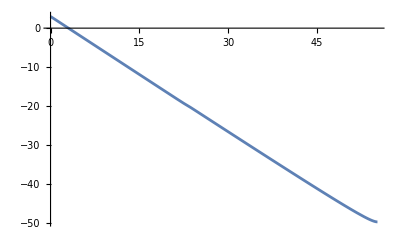

```mathematica
Plot[Log[cs/(kmpc*a[Ne]H[Ne])]/.solNe1,{Ne,0,NeFIN}]
```

```mathematica
Netotal=NeFIN+Nre(*Ntotal=Nend+Nreh*)
```

{62.3958}

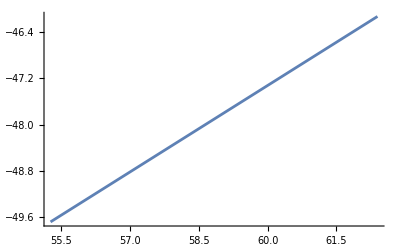

```mathematica
Plot[Log[1/kend[[1]]]+1/2(Ne-NeFIN),{Ne,NeFIN,Netotal[[1]]}]
```

```mathematica
endofinf=Log[cs/(kmpc*a[Ne]H[Ne])]/.solNe1/.Ne->NeFIN (*Log(1/k) at the end of inflation*)
```

{-49.6897}

```mathematica
endofreh=Log[1/kend[[1]]]+1/2(Netotal[[1]]-NeFIN)(*Log(1/k) at the end of reheating (RD start)*)
```

-46.123

```mathematica
endofrd=endofreh+(100-Netotal[[1]])(*Log(1/k) at the end of RD (MD Start)*)
```

-8.51882

```mathematica
pw=Piecewise[{{Log[cs/(kmpc*(a[Ne]H[Ne])/.solNe1)][[1]],-2<Ne< NeFIN}, 
{endofinf[[1]]+1/2(Ne-NeFIN),NeFIN≤ Ne< Netotal[[1]]},
{endofreh+(Ne-Netotal[[1]]),Netotal[[1]]≤ Ne<100},
{endofrd+ 1/2(Ne-100),100≤ Ne≤130}}]
```

Piecewise[{{Log[(0.000291518 ⅇ^-Ne)/(InterpolatingFunction[…][Ne])], -2<Ne<55.2624}, {-49.6897+1/2 (-55.2624+Ne), 55.2624≤Ne<62.3958}, {-108.519+Ne, 62.3958≤Ne<100}, {-8.51882+1/2 (-100+Ne), 100≤Ne≤130}, {0, True}}]

```mathematica
line1=Line[{{0,-NeFIN},{0,1.2}}];(*Vertucal line at CMB scale*)
line2=Line[{{NeFIN,-NeFIN},{NeFIN,-40}}];(*Vertucal line at Subscript[N, end]*)
line3=Line[{{Netotal[[1]],-NeFIN},{Netotal[[1]],-40}}];(*Vertucal line at the end of reheating (RD start)*)
line4=Line[{{100,-NeFIN},{100,-10}}];(*Vertucal line at the end of RD (MD start)*)
```

```mathematica
kINcmb=Log[1/0.05]
kINpeak=Log[1/kpeak[[1]]]
KINreh=Log[1/kre[[1]]](*critical scale ->  Subscript[k, reh]^-1*)
```

2.99573

-19.6994

-46.123

```mathematica
Plot[endofinf[[1]]+1/2(Ne-NeFIN),{ Ne,NeFIN, Netotal[[1]]}]
```

-Graphics-

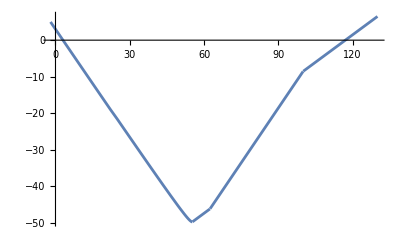

```mathematica
Plot[pw,{Ne,-2,130}]
```

```mathematica
comphi1=Plot[{pw,endofinf[[1]],endofreh,kINcmb,kINpeak,KINreh},{Ne,-2,128},Frame->True,Axes->False,PlotStyle->{{Black,Thickness[0.005]},{Transparent},{Transparent},{Dashing[0.025],Darker[Red]},{Dashing[0.025],Blue}(*,{Dashing[0.025],Blue},{Dashing[0.025],Lighter[Blue]}*),{Dashing[0.025],Darker[Green]}},FrameStyle->Directive[Thickness[0.003]],(*FrameTicks->{{Automatic,None},{None}},*)FrameTicks->{{None,None},{ {{0,"N_*"},{NeFIN,"N_end   "},{NeFIN+Nre[[1]],"      N_reh"},{100,"N_eq"}},None}},Filling->{2->{3}},FillingStyle->{Opacity[0.2,Blue]},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameLabel->{"N=Lna","Comoving Hubble Radius Ln(1/aH)"},Epilog->{Directive[Gray,Dashed],line1,line2,line3,line4,
Text[Style["k_peak^-1",18,FontFamily->"Cambria",Bold,Black],{6.5,-17}],
Text[Style["k_*^-1",18,FontFamily->"Cambria",Bold,Black],{4.65,5.6}],
Text[Style["k_reh^-1",18,FontFamily->"Cambria",Bold,Black],{6.5,-42}],
(*Text[Style["Pivot Scale",10,FontFamily->"Cambria",Black],{2,-19.5},Automatic,{0,6}],*)
(*Text[Style["⟵ End of Inflation",10,FontFamily->"Cambria",Black],{54.9,-17.5},Automatic,{0,6}],*)
Text[Style[" reh",15,FontFamily->"Cambria",Black],{58.5,-40},Automatic,{1,0}],
Text[Style[" ⟵——RD——⟶",18,FontFamily->"Cambria",Black],{81,-51},Automatic,{1,0}],
Text[Style[" ⟵—MD—⟶",18,FontFamily->"Cambria",Black],{114,-51},Automatic,{1,0}]},ImageSize->{600,400}]
```

```mathematica
psreh2n=Show[{reh2,Graphics[{Directive[Gray,Dashed],Line[{{-3,-50},{-3,-20}}],Line[{{19.8,-40},{19.8,-3.4}}],Line[{{46.3,-52},{46.3,-24.8}}]}],Graphics[{Darker[Red],PointSize[0.02],Point[{-3,-20}]}],Graphics[{Darker[Blue],PointSize[0.02],Point[{19.8,-3}]}],Graphics[{Darker[Green],PointSize[0.02],Point[{46.4,-24.8}]}]}]
```

```mathematica
Export["reh2.eps",psreh2n];
```

```mathematica
cB=Show[{comphi1,Graphics[{Black,PointSize[0.015],Point[{NeFIN,endofinf[[1]]}],Point[{Netotal[[1]],endofreh}],Point[{100,-9.0}]}],
Graphics[{{Darker[Red],PointSize[0.015],
Point[{0.05,kINcmb}],Point[{123.4,kINcmb}]},{Darker[Blue],PointSize[0.015],
Point[{23.5,kINpeak}],Point[{89,kINpeak}]},{Darker[Green],PointSize[0.015],
Point[{50.4,KINreh}],Point[{Netotal[[1]],endofreh}]}(*,
Point[{32.75,kINFree}],Point[{79.,kINFree}]*)}](*,Graphics[{Green,Thick,Circle[{43.8,-22.9},0.5]}]*)},Graphics[{Directive[Gray,Dashed](*,Line[{{-3,-50},{-3,-20}}],Line[{{29.6,-40},{29.6,-3.4}}],Line[{{43.8,-50},{43.8,-23}}]*)}]]
```

```mathematica
Export["com-rehB.eps",cB];
```

#### Solving tensor Mukhanov–Sasaki (MS) equation (10)

```mathematica
nPoints=5;
iMax=(NeFIN-.6)*nPoints;
NeHEt=Table[0+i/nPoints,{i,0,iMax}]//N;
NeBDt=Table[NeHEt[[i]]-1(*If[NeHEt[[i]]≤39,NeHEt[[i]]-5,NeHEt[[i]]-1]*),{i,1,iMax}]//N;
NeEndt=Table[(*NeFIN*)(*If[NeHE[[i]]≤31,NeHE[[i]]+3,NeFIN-.7]*)If[NeHEt[[i]]+1≤NeFIN,NeHEt[[i]]-.64,NeFIN],{i,1,iMax}];
kt=Table[(H[Ne]*a[Ne])/.solNe1/.{Ne->NeHEt[[i]]},{i,1,iMax}]//N;
For[i=1,i≤iMax-(iMax-1),i++,
tAux=AbsoluteTime[];
MSsolAuxt[i]=NDSolve[{((ut''[Ne]+(H'[Ne]/H[Ne]+a'[Ne]/a[Ne])ut'[Ne]+(kt[[i]]/(a[Ne] H[Ne]))^2 ut[Ne]-a''[Ne]/a[Ne] ut[Ne]-a'[Ne]/a[Ne](H'[Ne]/H[Ne]+a'[Ne]/a[Ne])ut[Ne])/.solNe1)==0,ut[NeBD[[i]]]==1/(√(2kt[[i]]))/.solNe1/.{Ne->NeBDt[[i]]},ut'[NeBDt[[i]]]==((-I kt[[i]])/(a[Ne] H[Ne] √2 √kt[[i]]))/.solNe1/.{Ne->NeBDt[[i]]}},{ut[Ne]},{Ne,NeBDt[[i]],NeEndt[[i]]},MaxSteps->Infinity(*Method->{"EquationSimplification"->"Solve"}*)(*,WorkingPrecision->30*)][[1]];Print[NeHEt[[i]]//N,"  ",kt[[i]]//N,"  ",AbsoluteTime[]-tAux]]
MSolt=Table[MSsolAuxt[i],{i,1,iMax}];
j=1;
PNt0=Table[{NeHEt[[i]],((j kt[[i]]^3/Pi^2*Abs[(ut[Ne]/.solNe1)/(a[Ne]/.solNe1)]^2)/.MSolt[[i]]/.Ne->NeEndt[[i]])[[1]][[1]]},{i,1,iMax-(iMax-1)}]
```

0.  {0.0000145759}  2.494039

{{0.,6.61371×10^-10}}

```mathematica
Off[NDSolve::precw];
For[i=1,i≤iMax,i++,
tAux=AbsoluteTime[];
MSsolAuxt[i]=NDSolve[{((ut''[Ne]+(H'[Ne]/H[Ne]+a'[Ne]/a[Ne])ut'[Ne]+(kt[[i]]/(a[Ne] H[Ne]))^2 ut[Ne]-a''[Ne]/a[Ne] ut[Ne]-a'[Ne]/a[Ne](H'[Ne]/H[Ne]+a'[Ne]/a[Ne])ut[Ne])/.solNe1)==0,ut[NeBDt[[i]]]==1/(√(2kt[[i]]))/.solNe1/.{Ne->NeBDt[[i]]},ut'[NeBDt[[i]]]==((-I kt[[i]])/(a[Ne] H[Ne] √2 √kt[[i]]))/.solNe1/.{Ne->NeBDt[[i]]}},{ut[Ne]},{Ne,NeBDt[[i]],NeEndt[[i]]},MaxSteps->Infinity(*Method->{"EquationSimplification"->"Solve"}*)(*,WorkingPrecision->30*)][[1]];Print[NeHEt[[i]]//N,"  ",kt[[i]]//N,"  ",AbsoluteTime[]-tAux]]
MSolt=Table[MSsolAuxt[i],{i,1,iMax}];
```

0.  {0.0000145759}  0.015648

0.2  {0.000017775}  0.

0.4  {0.0000216762}  0.

0.6  {0.0000264334}  0.

0.8  {0.0000322345}  0.015625

1.  {0.0000393084}  0.

1.2  {0.0000479346}  0.

1.4  {0.0000584535}  0.015693

1.6  {0.0000712802}  0.

1.8  {0.0000869211}  0.

2.  {0.000105994}  0.

2.2  {0.00012925}  0.015645

2.4  {0.000157609}  0.

2.6  {0.000192189}  0.

2.8  {0.000234354}  0.015537

3.  {0.000285769}  0.

3.2  {0.000348462}  0.0070223

3.4  {0.000424906}  0.

3.6  {0.000518117}  0.0090149

3.8  {0.000631772}  0.0007012

4.  {0.000770355}  0.

4.2  {0.00093933}  0.

4.4  {0.00114536}  0.0007039

4.6  {0.00139658}  0.

4.8  {0.00170289}  0.

5.  {0.00207637}  0.015007

5.2  {0.00253174}  0.

5.4  {0.00308696}  0.

5.6  {0.00376393}  0.

5.8  {0.00458932}  0.015721

6.  {0.00559568}  0.

6.2  {0.00682268}  0.

6.4  {0.00831867}  0.015538

6.6  {0.0101426}  0.

6.8  {0.0123664}  0.

7.  {0.0150777}  0.016451

7.2  {0.0183833}  0.

7.4  {0.0224135}  0.

7.6  {0.027327}  0.012043

7.8  {0.0333175}  0.0037298

8.  {0.0406208}  0.

8.2  {0.0495248}  0.

8.4  {0.0603802}  0.015012

8.6  {0.0736144}  0.

8.8  {0.0897487}  0.

9.  {0.109419}  0.016357

9.2  {0.133398}  0.

9.4  {0.162632}  0.015022

9.6  {0.198272}  0.

9.8  {0.241719}  0.01564

10.  {0.294685}  0.

10.2  {0.359255}  0.

10.4  {0.43797}  0.01571

10.6  {0.533928}  0.

10.8  {0.650905}  0.018624

11.  {0.793505}  0.

11.2  {0.967338}  0.013016

11.4  {1.17924}  0.

11.6  {1.43756}  0.

11.8  {1.75245}  0.015634

12.  {2.13629}  0.

12.2  {2.60419}  0.016604

12.4  {3.17455}  0.

12.6  {3.86979}  0.015805

12.8  {4.71726}  0.

13.  {5.75027}  0.

13.2  {7.00944}  0.015016

13.4  {8.54428}  0.

13.6  {10.4151}  0.015655

13.8  {12.6955}  0.0085085

14.  {15.475}  0.0075092

14.2  {18.8628}  0.

14.4  {22.9922}  0.

14.6  {28.0253}  0.015639

14.8  {34.1598}  0.

15.  {41.6368}  0.

15.2  {50.7499}  0.015016

15.4  {61.8571}  0.

15.6  {75.3945}  0.

15.8  {91.8937}  0.015659

16.  {112.003}  0.

16.2  {136.511}  0.

16.4  {166.381}  0.

16.6  {202.785}  0.015606

16.8  {247.151}  0.

17.  {301.222}  0.

17.2  {367.117}  0.

17.4  {447.424}  0.

17.6  {545.292}  0.

17.8  {664.56}  0.

18.  {809.905}  0.016044

18.2  {987.026}  0.

18.4  {1202.87}  0.015636

18.6  {1465.89}  0.

18.8  {1786.4}  0.016188

19.  {2176.96}  0.

19.2  {2652.86}  0.015516

19.4  {3232.74}  0.

19.6  {3939.29}  0.015642

19.8  {4800.17}  0.

20.  {5849.04}  0.

20.2  {7126.91}  0.01562

20.4  {8683.67}  0.

20.6  {10580.}  0.

20.8  {12889.9}  0.

21.  {15702.9}  0.

21.2  {19128.2}  0.015652

21.4  {23298.1}  0.004688

21.6  {28372.9}  0.

21.8  {34545.3}  0.011644

22.  {42046.3}  0.

22.2  {51144.3}  0.

22.4  {62122.2}  0.01502

22.6  {74138.5}  0.

22.8  {87652.3}  0.

23.  {104710.}  0.015635

23.2  {125992.}  0.015649

23.4  {152291.}  0.

23.6  {184590.}  0.

23.8  {224116.}  0.

24.  {272379.}  0.016015

24.2  {331237.}  0.

24.4  {402960.}  0.

24.6  {490325.}  0.015602

24.8  {596715.}  0.

25.  {726250.}  0.016104

25.2  {883945.}  0.

25.4  {1.07591×10^6}  0.

25.6  {1.30958×10^6}  0.015649

25.8  {1.594×10^6}  0.

26.  {1.94019×10^6}  0.015616

26.2  {2.36155×10^6}  0.

26.4  {2.87437×10^6}  0.015637

26.6  {3.49849×10^6}  0.

26.8  {4.25804×10^6}  0.

27.  {5.1824×10^6}  0.

27.2  {6.30728×10^6}  0.

27.4  {7.67615×10^6}  0.

27.6  {9.34186×10^6}  0.016293

27.8  {1.13687×10^7}  0.

28.  {1.3835×10^7}  0.01554

28.2  {1.68358×10^7}  0.

28.4  {2.04869×10^7}  0.015513

28.6  {2.49293×10^7}  0.

28.8  {3.0334×10^7}  0.

29.  {3.69095×10^7}  0.015638

29.2  {4.49091×10^7}  0.

29.4  {5.4641×10^7}  0.

29.6  {6.64798×10^7}  0.015642

29.8  {8.08811×10^7}  0.

30.  {9.83991×10^7}  0.

30.2  {1.19708×10^8}  0.015705

30.4  {1.45626×10^8}  0.

30.6  {1.77149×10^8}  0.

30.8  {2.1549×10^8}  0.015526

31.  {2.6212×10^8}  0.

31.2  {3.1883×10^8}  0.

31.4  {3.87795×10^8}  0.015647

31.6  {4.7166×10^8}  0.0006516

31.8  {5.73642×10^8}  0.0055244

32.  {6.97649×10^8}  0.

32.2  {8.48432×10^8}  0.0095273

32.4  {1.03176×10^9}  0.015648

32.6  {1.25466×10^9}  0.

32.8  {1.52566×10^9}  0.

33.  {1.85511×10^9}  0.015706

33.2  {2.25562×10^9}  0.

33.4  {2.74247×10^9}  0.

33.6  {3.33428×10^9}  0.015542

33.8  {4.05361×10^9}  0.

34.  {4.92793×10^9}  0.016297

34.2  {5.99055×10^9}  0.

34.4  {7.28199×10^9}  0.

34.6  {8.85142×10^9}  0.015022

34.8  {1.07586×10^10}  0.

35.  {1.30761×10^10}  0.016048

35.2  {1.5892×10^10}  0.0006838

35.4  {1.93134×10^10}  0.

35.6  {2.34701×10^10}  0.

35.8  {2.852×10^10}  0.

36.  {3.46546×10^10}  0.015642

36.2  {4.21065×10^10}  0.

36.4  {5.1158×10^10}  0.

36.6  {6.21518×10^10}  0.015622

36.8  {7.55038×10^10}  0.

37.  {9.17188×10^10}  0.

37.2  {1.11409×10^11}  0.

37.4  {1.35319×10^11}  0.015665

37.6  {1.6435×10^11}  0.

37.8  {1.99596×10^11}  0.

38.  {2.42385×10^11}  0.015659

38.2  {2.94327×10^11}  0.

38.4  {3.57376×10^11}  0.015587

38.6  {4.339×10^11}  0.003013

38.8  {5.26772×10^11}  0.

39.  {6.39476×10^11}  0.

39.2  {7.76234×10^11}  0.

39.4  {9.42166×10^11}  0.013055

39.6  {1.14348×10^12}  0.

39.8  {1.38769×10^12}  0.

40.  {1.68392×10^12}  0.

40.2  {2.04321×10^12}  0.

40.4  {2.47895×10^12}  0.016399

40.6  {3.00734×10^12}  0.

40.8  {3.64802×10^12}  0.

41.  {4.42476×10^12}  0.

41.2  {5.36637×10^12}  0.

41.4  {6.5077×10^12}  0.

41.6  {7.89096×10^12}  0.015099

41.8  {9.56723×10^12}  0.

42.  {1.15983×10^13}  0.

42.2  {1.4059×10^13}  0.

42.4  {1.70397×10^13}  0.

42.6  {2.065×10^13}  0.015634

42.8  {2.50221×10^13}  0.

43.  {3.0316×10^13}  0.

43.2  {3.67252×10^13}  0.

43.4  {4.44833×10^13}  0.016372

43.6  {5.38728×10^13}  0.

43.8  {6.52347×10^13}  0.

44.  {7.8981×10^13}  0.

44.2  {9.56091×10^13}  0.

44.4  {1.15719×10^14}  0.

44.6  {1.40036×10^14}  0.

44.8  {1.69433×10^14}  0.

45.  {2.04964×10^14}  0.

45.2  {2.47899×10^14}  0.008602

45.4  {2.9977×10^14}  0.

45.6  {3.62421×10^14}  0.

45.8  {4.38076×10^14}  0.0075081

46.  {5.2941×10^14}  0.

46.2  {6.39642×10^14}  0.

46.4  {7.72645×10^14}  0.

46.6  {9.33069×10^14}  0.

46.8  {1.12651×10^15}  0.015658

47.  {1.35968×10^15}  0.

47.2  {1.64066×10^15}  0.

47.4  {1.97911×10^15}  0.016255

47.6  {2.38663×10^15}  0.

47.8  {2.87713×10^15}  0.

48.  {3.46724×10^15}  0.01568

48.2  {4.17686×10^15}  0.

48.4  {5.02977×10^15}  0.

48.6  {6.0544×10^15}  0.

48.8  {7.28462×10^15}  0.

49.  {8.76083×10^15}  0.

49.2  {1.05311×10^16}  0.015507

49.4  {1.26525×10^16}  0.

49.6  {1.5193×10^16}  0.

49.8  {1.82329×10^16}  0.

50.  {2.18673×10^16}  0.

50.2  {2.62086×10^16}  0.

50.4  {3.13892×10^16}  0.

50.6  {3.75645×10^16}  0.015634

50.8  {4.49168×10^16}  0.

51.  {5.36592×10^16}  0.

51.2  {6.40392×10^16}  0.

51.4  {7.6344×10^16}  0.

51.6  {9.09053×10^16}  0.

51.8  {1.08103×10^17}  0.016015

52.  {1.2837×10^17}  0.

52.2  {1.52192×10^17}  0.

52.4  {1.80111×10^17}  0.

52.6  {2.12722×10^17}  0.

52.8  {2.50664×10^17}  0.01572

53.  {2.94602×10^17}  0.

53.2  {3.452×10^17}  0.

53.4  {4.03071×10^17}  0.

53.6  {4.68702×10^17}  0.

53.8  {5.42349×10^17}  0.015603

54.  {6.23802×10^17}  0.

54.2  {7.12196×10^17}  0.

54.4  {8.05563×10^17}  0.

```mathematica
PNt=Table[{NeHEt[[i]],((j kt[[i]]^3/Pi^2*Abs[ut[Ne]/.solNe1]^2/a[Ne]^2)/.MSolt[[i]]/.Ne->NeEndt[[i]])[[1]][[1]]},{i,1,iMax}]
```

{{0.,4.65764×10^-11},{0.2,4.64298×10^-11},{0.4,4.62832×10^-11},{0.6,4.61366×10^-11},{0.8,4.599×10^-11},{1.,4.58434×10^-11},{1.2,4.56967×10^-11},{1.4,4.55501×10^-11},{1.6,4.54034×10^-11},{1.8,4.52568×10^-11},{2.,4.51101×10^-11},{2.2,4.49634×10^-11},{2.4,4.48168×10^-11},{2.6,4.46701×10^-11},{2.8,4.45234×10^-11},{3.,4.43767×10^-11},{3.2,4.423×10^-11},{3.4,4.40833×10^-11},{3.6,4.39366×10^-11},{3.8,4.37899×10^-11},{4.,4.36432×10^-11},{4.2,4.34964×10^-11},{4.4,4.33497×10^-11},{4.6,4.3203×10^-11},{4.8,4.30562×10^-11},{5.,4.29095×10^-11},{5.2,4.27627×10^-11},{5.4,4.26159×10^-11},{5.6,4.24692×10^-11},{5.8,4.23224×10^-11},{6.,4.21756×10^-11},{6.2,4.20288×10^-11},{6.4,4.1882×10^-11},{6.6,4.17352×10^-11},{6.8,4.15884×10^-11},{7.,4.14415×10^-11},{7.2,4.12947×10^-11},{7.4,4.11479×10^-11},{7.6,4.1001×10^-11},{7.8,4.08542×10^-11},{8.,4.07073×10^-11},{8.2,4.05605×10^-11},{8.4,4.04136×10^-11},{8.6,4.02667×10^-11},{8.8,4.01199×10^-11},{9.,3.9973×10^-11},{9.2,3.98261×10^-11},{9.4,3.96792×10^-11},{9.6,3.95323×10^-11},{9.8,3.93854×10^-11},{10.,3.92385×10^-11},{10.2,3.90916×10^-11},{10.4,3.89446×10^-11},{10.6,3.87977×10^-11},{10.8,3.86507×10^-11},{11.,3.85038×10^-11},{11.2,3.83568×10^-11},{11.4,3.82099×10^-11},{11.6,3.80629×10^-11},{11.8,3.7916×10^-11},{12.,3.7769×10^-11},{12.2,3.7622×10^-11},{12.4,3.7475×10^-11},{12.6,3.7328×10^-11},{12.8,3.7181×10^-11},{13.,3.7034×10^-11},{13.2,3.6887×10^-11},{13.4,3.67399×10^-11},{13.6,3.65929×10^-11},{13.8,3.64459×10^-11},{14.,3.62988×10^-11},{14.2,3.61517×10^-11},{14.4,3.60046×10^-11},{14.6,3.58574×10^-11},{14.8,3.57102×10^-11},{15.,3.5563×10^-11},{15.2,3.54157×10^-11},{15.4,3.52684×10^-11},{15.6,3.51211×10^-11},{15.8,3.49737×10^-11},{16.,3.48264×10^-11},{16.2,3.46793×10^-11},{16.4,3.45321×10^-11},{16.6,3.43849×10^-11},{16.8,3.42377×10^-11},{17.,3.40906×10^-11},{17.2,3.39433×10^-11},{17.4,3.37959×10^-11},{17.6,3.36485×10^-11},{17.8,3.3501×10^-11},{18.,3.33534×10^-11},{18.2,3.32056×10^-11},{18.4,3.30576×10^-11},{18.6,3.29094×10^-11},{18.8,3.2761×10^-11},{19.,3.26123×10^-11},{19.2,3.24632×10^-11},{19.4,3.23136×10^-11},{19.6,3.21635×10^-11},{19.8,3.20127×10^-11},{20.,3.18611×10^-11},{20.2,3.17085×10^-11},{20.4,3.15546×10^-11},{20.6,3.13987×10^-11},{20.8,3.12404×10^-11},{21.,3.10788×10^-11},{21.2,3.09127×10^-11},{21.4,3.07408×10^-11},{21.6,3.05609×10^-11},{21.8,3.03686×10^-11},{22.,3.01575×10^-11},{22.2,2.99114×10^-11},{22.4,2.9585×10^-11},{22.6,2.82807×10^-11},{22.8,2.65436×10^-11},{23.,2.54133×10^-11},{23.2,2.46531×10^-11},{23.4,2.39761×10^-11},{23.6,2.3506×10^-11},{23.8,2.32914×10^-11},{24.,2.31055×10^-11},{24.2,2.29325×10^-11},{24.4,2.27665×10^-11},{24.6,2.26054×10^-11},{24.8,2.24477×10^-11},{25.,2.22926×10^-11},{25.2,2.21392×10^-11},{25.4,2.19871×10^-11},{25.6,2.18362×10^-11},{25.8,2.16861×10^-11},{26.,2.15369×10^-11},{26.2,2.13881×10^-11},{26.4,2.12397×10^-11},{26.6,2.10915×10^-11},{26.8,2.09435×10^-11},{27.,2.07956×10^-11},{27.2,2.06479×10^-11},{27.4,2.05002×10^-11},{27.6,2.03525×10^-11},{27.8,2.02049×10^-11},{28.,2.00572×10^-11},{28.2,1.99095×10^-11},{28.4,1.97619×10^-11},{28.6,1.96143×10^-11},{28.8,1.94669×10^-11},{29.,1.93195×10^-11},{29.2,1.91721×10^-11},{29.4,1.90249×10^-11},{29.6,1.88776×10^-11},{29.8,1.87303×10^-11},{30.,1.8583×10^-11},{30.2,1.84357×10^-11},{30.4,1.82884×10^-11},{30.6,1.81412×10^-11},{30.8,1.79939×10^-11},{31.,1.78466×10^-11},{31.2,1.76994×10^-11},{31.4,1.75521×10^-11},{31.6,1.74048×10^-11},{31.8,1.72576×10^-11},{32.,1.71104×10^-11},{32.2,1.69632×10^-11},{32.4,1.6816×10^-11},{32.6,1.66689×10^-11},{32.8,1.65218×10^-11},{33.,1.63747×10^-11},{33.2,1.62276×10^-11},{33.4,1.60805×10^-11},{33.6,1.5933×10^-11},{33.8,1.57855×10^-11},{34.,1.56381×10^-11},{34.2,1.54906×10^-11},{34.4,1.53432×10^-11},{34.6,1.51958×10^-11},{34.8,1.50483×10^-11},{35.,1.49009×10^-11},{35.2,1.47535×10^-11},{35.4,1.4606×10^-11},{35.6,1.44586×10^-11},{35.8,1.43112×10^-11},{36.,1.41638×10^-11},{36.2,1.40164×10^-11},{36.4,1.3869×10^-11},{36.6,1.37216×10^-11},{36.8,1.35742×10^-11},{37.,1.34268×10^-11},{37.2,1.32795×10^-11},{37.4,1.31321×10^-11},{37.6,1.29847×10^-11},{37.8,1.28374×10^-11},{38.,1.26901×10^-11},{38.2,1.25427×10^-11},{38.4,1.23954×10^-11},{38.6,1.22481×10^-11},{38.8,1.21009×10^-11},{39.,1.19536×10^-11},{39.2,1.18063×10^-11},{39.4,1.16591×10^-11},{39.6,1.15118×10^-11},{39.8,1.13646×10^-11},{40.,1.12173×10^-11},{40.2,1.10701×10^-11},{40.4,1.09229×10^-11},{40.6,1.07757×10^-11},{40.8,1.06285×10^-11},{41.,1.04814×10^-11},{41.2,1.03342×10^-11},{41.4,1.01871×10^-11},{41.6,1.004×10^-11},{41.8,9.89291×10^-12},{42.,9.74585×10^-12},{42.2,9.59878×10^-12},{42.4,9.45636×10^-12},{42.6,9.30926×10^-12},{42.8,9.1622×10^-12},{43.,9.01517×10^-12},{43.2,8.86818×10^-12},{43.4,8.72096×10^-12},{43.6,8.5743×10^-12},{43.8,8.4274×10^-12},{44.,8.28052×10^-12},{44.2,8.13368×10^-12},{44.4,7.98687×10^-12},{44.6,7.84008×10^-12},{44.8,7.69329×10^-12},{45.,7.54629×10^-12},{45.2,7.39973×10^-12},{45.4,7.25297×10^-12},{45.6,7.10627×10^-12},{45.8,6.95966×10^-12},{46.,6.81312×10^-12},{46.2,6.66667×10^-12},{46.4,6.5203×10^-12},{46.6,6.37395×10^-12},{46.8,6.22763×10^-12},{47.,6.08137×10^-12},{47.2,5.93517×10^-12},{47.4,5.78905×10^-12},{47.6,5.643×10^-12},{47.8,5.49688×10^-12},{48.,5.35113×10^-12},{48.2,5.20531×10^-12},{48.4,5.05956×10^-12},{48.6,4.91389×10^-12},{48.8,4.76831×10^-12},{49.,4.62281×10^-12},{49.2,4.47741×10^-12},{49.4,4.33199×10^-12},{49.6,4.18691×10^-12},{49.8,4.04185×10^-12},{50.,3.89681×10^-12},{50.2,3.75212×10^-12},{50.4,3.6075×10^-12},{50.6,3.46303×10^-12},{50.8,3.31874×10^-12},{51.,3.17464×10^-12},{51.2,3.03073×10^-12},{51.4,2.88696×10^-12},{51.6,2.74361×10^-12},{51.8,2.60054×10^-12},{52.,2.45775×10^-12},{52.2,2.31541×10^-12},{52.4,2.17345×10^-12},{52.6,2.03197×10^-12},{52.8,1.89094×10^-12},{53.,1.75056×10^-12},{53.2,1.61079×10^-12},{53.4,1.47177×10^-12},{53.6,1.3336×10^-12},{53.8,1.19657×10^-12},{54.,1.06069×10^-12},{54.2,9.26338×10^-13},{54.4,2.21532×10^-13}}

```mathematica
PNt[[1,2]]/PN0[[1,2]]
```

0.019165

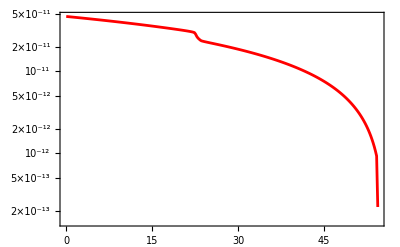

```mathematica
ListLogPlot[PNt(*,PlotRange->{{0,60},{3*10^-13,2*10^-11}}*),Joined->True,Frame->True,PlotStyle->Red]
```

```mathematica
kmpct=Solve[0.002/Mpct==(a[Ne] H[Ne])/.solNe1/.Ne->0,Mpct][[1]][[1,2]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

137.213

```mathematica
Pkt=Table[{(kmpct(H[Ne]a[Ne])/.solNe1/.{Ne->NeHEt[[i]]})[[1]],(j kt[[i]]^3/Pi^2*Abs[(ut[Ne]/.solNe1)/(a[Ne]/.solNe1)]^2/.MSolt[[i]]/.Ne->NeEndt[[i]])[[1]][[1]]},{i,1,iMax}]
```

{{0.002,4.65764×10^-11},{0.00243896,4.64298×10^-11},{0.00297424,4.62832×10^-11},{0.00362699,4.61366×10^-11},{0.00442298,4.599×10^-11},{0.00539362,4.58434×10^-11},{0.00657723,4.56967×10^-11},{0.00802055,4.55501×10^-11},{0.00978055,4.54034×10^-11},{0.0119267,4.52568×10^-11},{0.0145437,4.51101×10^-11},{0.0177348,4.49634×10^-11},{0.0216259,4.48168×10^-11},{0.0263707,4.46701×10^-11},{0.0321564,4.45234×10^-11},{0.0392111,4.43767×10^-11},{0.0478134,4.423×10^-11},{0.0583025,4.40833×10^-11},{0.0710922,4.39366×10^-11},{0.0866871,4.37899×10^-11},{0.105702,4.36432×10^-11},{0.128888,4.34964×10^-11},{0.157158,4.33497×10^-11},{0.191629,4.3203×10^-11},{0.233658,4.30562×10^-11},{0.284904,4.29095×10^-11},{0.347387,4.27627×10^-11},{0.42357,4.26159×10^-11},{0.516459,4.24692×10^-11},{0.629713,4.23224×10^-11},{0.767799,4.21756×10^-11},{0.936158,4.20288×10^-11},{1.14143,4.1882×10^-11},{1.3917,4.17352×10^-11},{1.69683,4.15884×10^-11},{2.06885,4.14415×10^-11},{2.52242,4.12947×10^-11},{3.07541,4.11479×10^-11},{3.74961,4.1001×10^-11},{4.57158,4.08542×10^-11},{5.57369,4.07073×10^-11},{6.79544,4.05605×10^-11},{8.28493,4.04136×10^-11},{10.1008,4.02667×10^-11},{12.3147,4.01199×10^-11},{15.0136,3.9973×10^-11},{18.3039,3.98261×10^-11},{22.3152,3.96792×10^-11},{27.2054,3.95323×10^-11},{33.1669,3.93854×10^-11},{40.4346,3.92385×10^-11},{49.2944,3.90916×10^-11},{60.095,3.89446×10^-11},{73.2617,3.87977×10^-11},{89.3124,3.86507×10^-11},{108.879,3.85038×10^-11},{132.731,3.83568×10^-11},{161.807,3.82099×10^-11},{197.251,3.80629×10^-11},{240.458,3.7916×10^-11},{293.126,3.7769×10^-11},{357.328,3.7622×10^-11},{435.588,3.7475×10^-11},{530.984,3.7328×10^-11},{647.267,3.7181×10^-11},{789.01,3.7034×10^-11},{961.784,3.6887×10^-11},{1172.38,3.67399×10^-11},{1429.08,3.65929×10^-11},{1741.98,3.64459×10^-11},{2123.36,3.62988×10^-11},{2588.22,3.61517×10^-11},{3154.82,3.60046×10^-11},{3845.42,3.58574×10^-11},{4687.16,3.57102×10^-11},{5713.1,3.5563×10^-11},{6963.53,3.54157×10^-11},{8487.58,3.52684×10^-11},{10345.1,3.51211×10^-11},{12609.,3.49737×10^-11},{15368.2,3.48264×10^-11},{18731.1,3.46793×10^-11},{22829.6,3.45321×10^-11},{27824.6,3.43849×10^-11},{33912.3,3.42377×10^-11},{41331.4,3.40906×10^-11},{50373.2,3.39433×10^-11},{61392.3,3.37959×10^-11},{74821.,3.36485×10^-11},{91186.,3.3501×10^-11},{111129.,3.33534×10^-11},{135432.,3.32056×10^-11},{165049.,3.30576×10^-11},{201139.,3.29094×10^-11},{245117.,3.2761×10^-11},{298706.,3.26123×10^-11},{364006.,3.24632×10^-11},{443572.,3.23136×10^-11},{540521.,3.21635×10^-11},{658644.,3.20127×10^-11},{802563.,3.18611×10^-11},{977902.,3.17085×10^-11},{1.19151×10^6,3.15546×10^-11},{1.45171×10^6,3.13987×10^-11},{1.76865×10^6,3.12404×10^-11},{2.15464×10^6,3.10788×10^-11},{2.62463×10^6,3.09127×10^-11},{3.1968×10^6,3.07408×10^-11},{3.89312×10^6,3.05609×10^-11},{4.74005×10^6,3.03686×10^-11},{5.76928×10^6,3.01575×10^-11},{7.01764×10^6,2.99114×10^-11},{8.52395×10^6,2.9585×10^-11},{1.01727×10^7,2.82807×10^-11},{1.2027×10^7,2.65436×10^-11},{1.43676×10^7,2.54133×10^-11},{1.72877×10^7,2.46531×10^-11},{2.08963×10^7,2.39761×10^-11},{2.53281×10^7,2.3506×10^-11},{3.07516×10^7,2.32914×10^-11},{3.73739×10^7,2.31055×10^-11},{4.54498×10^7,2.29325×10^-11},{5.52912×10^7,2.27665×10^-11},{6.72788×10^7,2.26054×10^-11},{8.18769×10^7,2.24477×10^-11},{9.96507×10^7,2.22926×10^-11},{1.21288×10^8,2.21392×10^-11},{1.47628×10^8,2.19871×10^-11},{1.79691×10^8,2.18362×10^-11},{2.18717×10^8,2.16861×10^-11},{2.66219×10^8,2.15369×10^-11},{3.24034×10^8,2.13881×10^-11},{3.944×10^8,2.12397×10^-11},{4.80037×10^8,2.10915×10^-11},{5.84258×10^8,2.09435×10^-11},{7.11091×10^8,2.07956×10^-11},{8.65439×10^8,2.06479×10^-11},{1.05326×10^9,2.05002×10^-11},{1.28182×10^9,2.03525×10^-11},{1.55993×10^9,2.02049×10^-11},{1.89834×10^9,2.00572×10^-11},{2.31009×10^9,1.99095×10^-11},{2.81107×10^9,1.97619×10^-11},{3.42061×10^9,1.96143×10^-11},{4.16222×10^9,1.94669×10^-11},{5.06446×10^9,1.93195×10^-11},{6.1621×10^9,1.91721×10^-11},{7.49744×10^9,1.90249×10^-11},{9.12187×10^9,1.88776×10^-11},{1.10979×10^10,1.87303×10^-11},{1.35016×10^10,1.8583×10^-11},{1.64254×10^10,1.84357×10^-11},{1.99817×10^10,1.82884×10^-11},{2.43071×10^10,1.81412×10^-11},{2.9568×10^10,1.79939×10^-11},{3.59662×10^10,1.78466×10^-11},{4.37475×10^10,1.76994×10^-11},{5.32103×10^10,1.75521×10^-11},{6.47177×10^10,1.74048×10^-11},{7.87109×10^10,1.72576×10^-11},{9.57262×10^10,1.71104×10^-11},{1.16416×10^11,1.69632×10^-11},{1.41571×10^11,1.6816×10^-11},{1.72156×10^11,1.66689×10^-11},{2.0934×10^11,1.65218×10^-11},{2.54545×10^11,1.63747×10^-11},{3.09499×10^11,1.62276×10^-11},{3.76302×10^11,1.60805×10^-11},{4.57505×10^11,1.5933×10^-11},{5.56207×10^11,1.57855×10^-11},{6.76174×10^11,1.56381×10^-11},{8.21979×10^11,1.54906×10^-11},{9.99181×10^11,1.53432×10^-11},{1.21453×10^12,1.51958×10^-11},{1.47622×10^12,1.50483×10^-11},{1.7942×10^12,1.49009×10^-11},{2.18058×10^12,1.47535×10^-11},{2.65004×10^12,1.4606×10^-11},{3.2204×10^12,1.44586×10^-11},{3.91331×10^12,1.43112×10^-11},{4.75505×10^12,1.41638×10^-11},{5.77755×10^12,1.40164×10^-11},{7.01953×10^12,1.3869×10^-11},{8.52801×10^12,1.37216×10^-11},{1.03601×10^13,1.35742×10^-11},{1.2585×10^13,1.34268×10^-11},{1.52868×10^13,1.32795×10^-11},{1.85675×10^13,1.31321×10^-11},{2.25509×10^13,1.29847×10^-11},{2.73871×10^13,1.28374×10^-11},{3.32583×10^13,1.26901×10^-11},{4.03854×10^13,1.25427×10^-11},{4.90365×10^13,1.23954×10^-11},{5.95366×10^13,1.22481×10^-11},{7.22798×10^13,1.21009×10^-11},{8.77442×10^13,1.19536×10^-11},{1.06509×10^14,1.18063×10^-11},{1.29277×10^14,1.16591×10^-11},{1.569×10^14,1.15118×10^-11},{1.90409×10^14,1.13646×10^-11},{2.31055×10^14,1.12173×10^-11},{2.80355×10^14,1.10701×10^-11},{3.40143×10^14,1.09229×10^-11},{4.12645×10^14,1.07757×10^-11},{5.00554×10^14,1.06285×10^-11},{6.07133×10^14,1.04814×10^-11},{7.36334×10^14,1.03342×10^-11},{8.92939×10^14,1.01871×10^-11},{1.08274×10^15,1.004×10^-11},{1.31274×10^15,9.89291×10^-12},{1.59143×10^15,9.74585×10^-12},{1.92907×10^15,9.59878×10^-12},{2.33807×10^15,9.45636×10^-12},{2.83344×10^15,9.30926×10^-12},{3.43335×10^15,9.1622×10^-12},{4.15974×10^15,9.01517×10^-12},{5.03916×10^15,8.86818×10^-12},{6.10368×10^15,8.72096×10^-12},{7.39203×10^15,8.5743×10^-12},{8.95103×10^15,8.4274×10^-12},{1.08372×10^16,8.28052×10^-12},{1.31188×10^16,8.13368×10^-12},{1.58782×10^16,7.98687×10^-12},{1.92147×10^16,7.84008×10^-12},{2.32484×10^16,7.69329×10^-12},{2.81237×10^16,7.54629×10^-12},{3.40149×10^16,7.39973×10^-12},{4.11322×10^16,7.25297×10^-12},{4.97288×10^16,7.10627×10^-12},{6.01096×10^16,6.95966×10^-12},{7.26418×10^16,6.81312×10^-12},{8.7767×10^16,6.66667×10^-12},{1.06017×10^17,6.5203×10^-12},{1.28029×10^17,6.37395×10^-12},{1.54571×10^17,6.22763×10^-12},{1.86566×10^17,6.08137×10^-12},{2.25119×10^17,5.93517×10^-12},{2.71558×10^17,5.78905×10^-12},{3.27476×10^17,5.643×10^-12},{3.94779×10^17,5.49688×10^-12},{4.75749×10^17,5.35113×10^-12},{5.73117×10^17,5.20531×10^-12},{6.90149×10^17,5.05956×10^-12},{8.3074×10^17,4.91389×10^-12},{9.99542×10^17,4.76831×10^-12},{1.2021×10^18,4.62281×10^-12},{1.445×10^18,4.47741×10^-12},{1.73609×10^18,4.33199×10^-12},{2.08467×10^18,4.18691×10^-12},{2.50178×10^18,4.04185×10^-12},{3.00047×10^18,3.89681×10^-12},{3.59616×10^18,3.75212×10^-12},{4.307×10^18,3.6075×10^-12},{5.15433×10^18,3.46303×10^-12},{6.16316×10^18,3.31874×10^-12},{7.36272×10^18,3.17464×10^-12},{8.78699×10^18,3.03073×10^-12},{1.04754×10^19,2.88696×10^-12},{1.24734×10^19,2.74361×10^-12},{1.48332×10^19,2.60054×10^-12},{1.76141×10^19,2.45775×10^-12},{2.08826×10^19,2.31541×10^-12},{2.47134×10^19,2.17345×10^-12},{2.91881×10^19,2.03197×10^-12},{3.43943×10^19,1.89094×10^-12},{4.04231×10^19,1.75056×10^-12},{4.73659×10^19,1.61079×10^-12},{5.53065×10^19,1.47177×10^-12},{6.43119×10^19,1.3336×10^-12},{7.44171×10^19,1.19657×10^-12},{8.55936×10^19,1.06069×10^-12},{9.77223×10^19,9.26338×10^-13},{1.10533×10^20,2.21532×10^-13}}

```mathematica
ct=Interpolation[Pkt,InterpolationOrder->1]
AAt=LogLogPlot[{ct[x]},{x,0.002,4*^20}(*,PlotRange->{{0.001,4*10^22},{10^-12,1}}*),
Frame->True,FrameStyle->Thick,FrameTicksStyle->Black,PlotStyle->Darker[Green],LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],ImageSize->{600,400},AspectRatio->Full,RotateLabel->False,Axes->False,FrameLabel->{"k/Mpc^-1","P_t"}]
```

InterpolatingFunction[…]

```mathematica
ct[0.05kmpct]
```

4.05541×10^-11

```mathematica
c1[0.05kmpc]
```

1.97629×10^-9

```mathematica
ct[0.05kmpct]/(c1[0.05kmpc](*2.1*10^-9*))
```

0.0205203

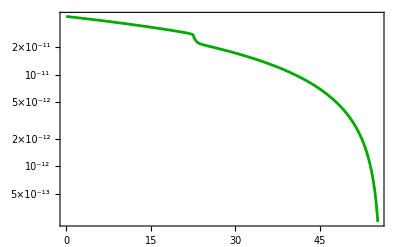

```mathematica
LogPlot[(2 H[Ne]^2/.solNe1)/Pi^2,{Ne,0,NeFIN},PlotRange->All,Frame->True,PlotStyle->Darker[Green]]
```

```mathematica
(((2 H[Ne]^2/.solNe1)/Pi^2)[[1]]/.Ne->0)/(c1[0.05kmpc](*2.1*10^-9*))
```

0.0217847

## Case C

```mathematica
Clear["Global`*"]
Remove["Global`*"]
```

Remove::rmnsm: There are no symbols matching "Global`*".

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ϵ1[Ne_]:=-H'[Ne]/H[Ne]
(*D[Log[ϵ1[Ne]],Ne]*)
ϵ2[Ne_]:=-(H[Ne] (H'[Ne]^2/H[Ne]^2-H''[Ne]/H[Ne]))/H'[Ne](*ϵ1[Ne]-1/(2ϵ1[Ne])ϵ1'[Ne]*)
```

```mathematica
V[ϕ_]:=Λ^4(1+Cos[ϕ/f])
ϵ[ϕ_]:=w(Cosh[(ϕ-ϕc)/b])^-2
M[ϕ_]:=M0(1+ϵ[ϕ])
```

#### Solving Background Equations (6)&(9)

```mathematica
Off[NDSolve::precw];
ϕ0=5.53327945289528760424702860706861791151`29.518687405708878;
dϕ0=0.0052583177533965574057692244440840616889231016307249570077`26.83391284890734;
w=1.544*10^1;
b=1.2*10^-2;
ϕc=5.6923;
Λ=1.``15*10^-2;
α=20.;
M0=2.32``15*10^-4;
f=2.``15;
cs=1/(√(2α-1));
(*Plot[M'[ϕ]/M[ϕ],{ϕ,-20,20},PlotRange->All]*)
solNe1=NDSolve[{H[Ne]H'[Ne]==-α H[Ne]^2 ϕ'[Ne]^2/2(H[Ne]^2 ϕ'[Ne]^2/(2 M[ϕ[Ne]]^4))^(α-1),ϕ''[Ne]==-(3/(2α-1)-ϵ1[Ne])ϕ'[Ne]-(V'[ϕ[Ne]]/V[ϕ[Ne]])((3α-(2α-1)ϵ1[Ne])/(α(2α-1)))ϕ'[Ne]^2/(2ϵ1[Ne])+(2(α-1))/α M'[ϕ[Ne]]/M[ϕ[Ne]] ϕ'[Ne]^2,ϕ[-6]==ϕ0,H[-6]==√(V[ϕ[-6]]/3),ϕ'[-6]==dϕ0},{ϕ,H},{Ne,-6``15,65``15},Method->{"EquationSimplification"->"Residual"},AccuracyGoal->6.2356,PrecisionGoal->30.]
NeFIN=FindRoot[(ϵ1[Ne]/.solNe1)==1,{Ne,52}]
NeFIN=NeFIN[[1,2]];
phi=Plot[ϕ[Ne]/.solNe1,{Ne,0,NeFIN},PlotRange->{{-1,58},{5.4,6.3}},Frame->True,FrameLabel->{"N","ϕ/M_P"},PlotStyle->Darker[Blue],LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],ImageSize->{600,400},RotateLabel->False,FrameStyle->Thick,FrameTicksStyle->Black(*PlotLegends->{Placed[LineLegend[{{Red},{Darker[Green]},Darker[Blue]},{"Case A","Case B ","Case C"},LabelStyle->{14,FontFamily->"Cambria"},LegendLayout->"Column",LegendMarkerSize->{{30,20}}],{0.12,0.2}]}*)]
LogPlot[{ϵ1[Ne]/.solNe1,1},{Ne,0,NeFIN},PlotRange->{{0,57.},{0.005,1.2}},Frame->True,FrameLabel->{"N","ε_1"},PlotStyle->{Darker[Blue],Orange},ImageSize->{600,400},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameStyle->Thick,FrameTicksStyle->Black,ImageSize->{600,400},RotateLabel->False(*,PlotLegends->{Placed[LineLegend[{{Red},{Darker[Green]},Darker[Blue]},{"Case A","Case B ","Case C"},LabelStyle->{14,FontFamily->"Cambria"},LegendLayout->"Column",LegendMarkerSize->{{30,20}}],{0.12,0.2}]}*)]
Plot[V[ϕ]/Λ^4,{ϕ,0,0.013},PlotRange->All,Frame->True,FrameLabel->{"ϕ","V[ϕ]/Λ^4"},
LabelStyle->Directive[15,Bold,Black,FontFamily->"Book Antiqua"],PlotStyle->Red]
Plot[ϵ[ϕ],{ϕ,4,6.5},PlotRange->All,Frame->True,PlotStyle->Red]
Plot[M[ϕ],{ϕ,4,6.5},PlotRange->All,Frame->True,PlotStyle->Red]
NeIN=0;
```

Power::infy: Infinite expression 1/0. encountered.

NDSolve::nlnum: The function value {4.27937×10^-13,0.,ComplexInfinity} is not a list of numbers with dimensions {3} at {Ne,H[Ne],ϕ[Ne],ϕ'[Ne],H'[Ne],ϕ'[Ne],ϕ''[Ne]} = {-6.,0.0000152179,5.53328,0.00525832,0.,0.00525832,0.}.

NDSolve::ndsz: At Ne == 55.5803, step size is effectively zero; singularity or stiff system suspected.

{{ϕ→InterpolatingFunction[…],H→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {70.1819} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {57.9846} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{Ne→55.0099}

```mathematica
r[Ne_]:=First[Evaluate[16cs ϵ1[Ne]/.solNe1]]
ns[Ne_]:=First[Evaluate[1-2ϵ1[Ne]-ϵ2[Ne]/.solNe1]]
r[0]
ns[0]
```

0.0199766

0.968423

```mathematica
PN=ParametricPlot[{{ns[Ne],r[Ne]}},{Ne,-.05,0},PlotRange->{{0.945,1},{0,.261}},Frame-> True,FrameLabel->{"n_s","r"},ImageSize->{400,300},AspectRatio->Full,PlotStyle->{{Purple,Thickness[0.01]}}]
rns0=-Graphics-;
prns0=Show[{ParametricPlot[{ns0[Ne],r0[Ne]},{Ne,50,60},PlotRange->{{0.945,1},{0,0.261}},PlotStyle->{Black,Thickness[0.005]},Frame-> True,FrameLabel->{"n_s","r"},ImageSize->{700,400},AspectRatio->Full,PlotLegends->{Placed[SwatchLegend[{Gray,Red,Blue},{"TT,TE,EE+lowE+lensing ","TT,TE,EE+lowE+lensing +BK14 ","TT,TE,EE+lowE+lensing +BK14+BAO "},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}}],{1,0.92}](*,Placed[LineLegend[{Yellow},{"ϕ^2"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.83}],Placed[LineLegend[{Directive[Dashed,Yellow],Yellow},{"α-attractor N_*=50","α-attractor N_*=60"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.60}],Placed[LineLegend[{Directive[Dashed,Blue],Blue},{"α-attractor(G-I)   M=10^6","α-attractor(G-I)   M=10^6"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.45}],Placed[LineLegend[{Directive[Dashed,Black],Black},{"α-attractor(G-I)   M=10^-3","α-attractor(G-I)   M=10^-3"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.25}],Placed[PointLegend[{Directive[Black,AbsolutePointSize[6]],Directive[Black,AbsolutePointSize[8]]},{"N_*=50","N_*=60"},LabelStyle->10,LegendLayout->"Column"],{1.025,0.12}]*)}],Graphics[{Texture[rns0],EdgeForm[Black],Polygon[{{0.945,0},{1,0},{1,0.261},{0.945,0.261}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},ImageSize->{400,300},AspectRatio->Full]}]
Show[prns0,PN]
```

```mathematica
PN=ParametricPlot[{{ns[Ne],r[Ne]}},{Ne,-.1,0},PlotRange->{{0.93,1},{0,.1}},Frame-> True,FrameLabel->{"n_s","r"},ImageSize->{400,300},AspectRatio->Full,PlotStyle->{{Purple,Thickness[0.01]}}]
rns0=-Graphics-;
prns0=Show[{ParametricPlot[{ns0[Ne],r0[Ne]},{Ne,50,60},PlotRange->{{0.93,1},{0,0.20}},PlotStyle->{Black,Thickness[0.005]},Frame-> True,FrameLabel->{"n_s","r"},ImageSize->{700,400},AspectRatio->Full,PlotLegends->{Placed[SwatchLegend[{Gray,Red,Blue},{"TT,TE,EE+lowE+lensing ","TT,TE,EE+lowE+lensing +BK14 ","TT,TE,EE+lowE+lensing +BK14+BAO "},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}}],{1,0.92}],Placed[LineLegend[{Yellow},{"ϕ^2"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.83}],Placed[LineLegend[{Directive[Dashed,Yellow],Yellow},{"α-attractor N_*=50","α-attractor N_*=60"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.60}],Placed[LineLegend[{Directive[Dashed,Blue],Blue},{"α-attractor(G-I)   M=10^6","α-attractor(G-I)   M=10^6"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.45}],Placed[LineLegend[{Directive[Dashed,Black],Black},{"α-attractor(G-I)   M=10^-3","α-attractor(G-I)   M=10^-3"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.25}],Placed[PointLegend[{Directive[Black,AbsolutePointSize[6]],Directive[Black,AbsolutePointSize[8]]},{"N_*=50","N_*=60"},LabelStyle->10,LegendLayout->"Column"],{1.025,0.12}]}],Graphics[{Texture[rns0],EdgeForm[Black],Polygon[{{0.93,0},{1,0},{1,0.2},{0.93,0.2}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},ImageSize->{400,300},AspectRatio->Full]}]
Show[prns0,PN]
```

```mathematica
Plot[{(Abs[ϕ[Ne]-ϕ[NeFIN]])/.solNe1},{Ne,-6,NeFIN},PlotRange->{{0,57},{0,.8}},FrameLabel->{"N","Δϕ/M_P"},Frame->True,Frame->True,PlotStyle->Darker[Blue],ImageSize->{600,400},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameStyle->Thick,FrameTicksStyle->Black,ImageSize->{600,400},RotateLabel->False(*,PlotLegends->{Placed[LineLegend[{{Red},{Darker[Green]},Blue},{"Case A","Case B ","Case C"},LabelStyle->{14,FontFamily->"Cambria"},LegendLayout->"Column",LegendMarkerSize->{{30,20}}],{0.12,0.2}]}*)]
Plot[{Abs[V'[ϕ[Ne]]/V[ϕ[Ne]]]/.solNe1,1},{Ne,0,NeFIN},PlotRange->{{0,57},{0,18}},FrameLabel->{"N","M_pV_(,ϕ)/V"},Frame->True,Frame->True,PlotStyle->{Darker[Blue],Orange},ImageSize->{600,400},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameStyle->Thick,FrameTicksStyle->Black,ImageSize->{600,400},RotateLabel->False(*,PlotLegends->{Placed[LineLegend[{{Red},{Darker[Green]},Blue},{"Case A","Case B ","Case C"},LabelStyle->{14,FontFamily->"Cambria"},LegendLayout->"Column",LegendMarkerSize->{{30,20}}],{0.12,0.5}]}*)]
Plot[{ϵ2[Ne]/.solNe1,1},{Ne,-6,NeFIN},PlotRange->{{0,57},{-3,7}},FrameLabel->{"N","ε_2"},Frame->True,PlotStyle->{Darker[Blue],Orange},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameStyle->Thick,FrameTicksStyle->Black,ImageSize->{600,400},RotateLabel->False(*,PlotLegends->{Placed[LineLegend[{{Red},{Darker[Green]},Blue},{"Case A","Case B ","Case C"},LabelStyle->{14,FontFamily->"Cambria"},LegendLayout->"Column",LegendMarkerSize->{{30,20}}],{0.12,0.5}]}*)]
Plot[ϕ''[Ne]/.solNe1,{Ne,-6,NeFIN},PlotRange->All,FrameLabel->{"Ne","ϕ''[Ne]"},Frame->True]
Plot[ϕ'[Ne]/.solNe1,{Ne,0,NeFIN},FrameLabel->{"N","ϕ_(,N)/M_P"},Frame->True,PlotStyle->Darker[Blue],ImageSize->{600,400},PlotRange->{{0,57},{0.001,.1}},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameStyle->Thick,FrameTicksStyle->Black,ImageSize->{600,400},RotateLabel->False(*,PlotLegends->{Placed[LineLegend[{{Red},{Darker[Green]},Blue},{"Case A","Case B ","Case C"},LabelStyle->{14,FontFamily->"Cambria"},LegendLayout->"Column",LegendMarkerSize->{{30,20}}],{0.12,0.2}]}*)]
LogPlot[H[Ne]/.solNe1,{Ne,0,NeFIN},PlotRange->{{0,58},{9*10^-7,2*10^-5}},FrameLabel->{"Ne","H/M_p"},Frame->True,PlotStyle->Darker[Blue],ImageSize->{600,400},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameStyle->Thick,FrameTicksStyle->Black,ImageSize->{600,400},RotateLabel->False]
Plot[H'[Ne]/.solNe1,{Ne,-5,NeFIN},PlotRange->All,FrameLabel->{"Ne","H'[Ne]"},Frame->True]
```

```mathematica
cs=√(1/(2α-1));
a[Ne_]:=Exp[Ne];
z[Ne_]:=(a[Ne]ϕ'[Ne])/cs √(α ((H[Ne]^2 ϕ'[Ne]^2)/(2 M[ϕ[Ne]]^4))^(α-1))
Plot[z'[Ne]/z[Ne]/.solNe1,{Ne,-5,NeFIN},PlotRange->{{0,57},{-4,6}}]
z[Ne]/.solNe1/.Ne->0
```

{0.779889}

#### Solving Scalar Mukhonv Sasaki Equation (10)

```mathematica
nPoints=5;
iMax=(NeFIN-.3)*nPoints;
NeHE=Table[0+i/nPoints,{i,1,iMax}]//N;
NeBD=Table[NeHE[[i]]-5,{i,1,iMax}]//N;
NeEnd=Table[(*NeFIN*)(*If[NeHE[[i]]≤31,NeHE[[i]]+3,NeFIN-.7]*)If[NeHE[[i]]+1≤NeFIN,NeHE[[i]]+1,NeFIN],{i,1,iMax}];
k=Table[((H[Ne]*a[Ne])/cs)/.solNe1/.{Ne->NeHE[[i]]},{i,1,iMax}]//N;
For[i=1,i≤iMax-(iMax-1),i++,
tAux=AbsoluteTime[];
MSsolAux[i]=NDSolve[{((u''[Ne]+(H'[Ne]/H[Ne]+a'[Ne]/a[Ne])u'[Ne]+((cs k[[i]])/(a[Ne] H[Ne]))^2 u[Ne]-z''[Ne]/z[Ne] u[Ne]-z'[Ne]/z[Ne](H'[Ne]/H[Ne]+a'[Ne]/a[Ne])u[Ne])/.solNe1)==0,u[NeBD[[i]]]==1/(√(2k[[i]] cs))/.solNe1/.{Ne->NeBD[[i]]},u'[NeBD[[i]]]==((-2I k[[i]] cs^2)/(a[Ne] H[Ne]2 √2 √k[[i]] cs^(3/2)))/.solNe1/.{Ne->NeBD[[i]]}},{u[Ne]},{Ne,NeBD[[i]],NeEnd[[i]]},MaxSteps->Infinity(*Method->{"EquationSimplification"->"Solve"}*)(*,WorkingPrecision->30*)][[1]];Print[NeHE[[i]]//N,"  ",k[[i]]//N,"  ",AbsoluteTime[]-tAux]]
MSol=Table[MSsolAux[i],{i,1,iMax}];
PN0=Table[{NeHE[[i]],((k[[i]]^3/(2*Pi^2)*Abs[(u[Ne]/.solNe1)/(z[Ne]/.solNe1)]^2)/.MSol[[i]]/.Ne->NeEnd[[i]])[[1]][[1]]},{i,1,iMax-(iMax-1)}]
```

0.2  {0.000111027}  0.329996

{{0.2,2.4522×10^-9}}

```mathematica
Off[NDSolve::precw];
For[i=1,i≤iMax,i++,
tAux=AbsoluteTime[];
MSsolAux[i]=NDSolve[{((u''[Ne]+(H'[Ne]/H[Ne]+a'[Ne]/a[Ne])u'[Ne]+((cs k[[i]])/(a[Ne] H[Ne]))^2 u[Ne]-z''[Ne]/z[Ne] u[Ne]-z'[Ne]/z[Ne](H'[Ne]/H[Ne]+a'[Ne]/a[Ne])u[Ne])/.solNe1)==0,u[NeBD[[i]]]==1/(√(2k[[i]] cs))/.solNe1/.{Ne->NeBD[[i]]},u'[NeBD[[i]]]==((-2I k[[i]] cs^2)/(a[Ne] H[Ne]2 √2 √k[[i]] cs^(3/2)))/.solNe1/.{Ne->NeBD[[i]]}},{u[Ne]},{Ne,NeBD[[i]],NeEnd[[i]]},MaxSteps->Infinity,(*,Method->{"StiffnessSwitching",Method->{"ExplicitRungeKutta",Automatic}}*)Method->{"ExplicitRungeKutta","StiffnessTest"->False}(*,Method->{"EquationSimplification"->"Solve"},*),AccuracyGoal->14,PrecisionGoal->4(*,WorkingPrecision->2*)][[1]];Print[NeHE[[i]]//N,"  ",k[[i]]//N,"  ",AbsoluteTime[]-tAux]]
MSol=Table[MSsolAux[i],{i,1,iMax}];
```

0.2  {0.000111027}  0.173122

0.4  {0.000135397}  0.188675

0.6  {0.000165114}  0.172707

0.8  {0.000201353}  0.181402

1.  {0.000245545}  0.164473

1.2  {0.000299433}  0.172624

1.4  {0.000365147}  0.172747

1.6  {0.000445279}  0.174011

1.8  {0.000542994}  0.158124

2.  {0.000662149}  0.173777

2.2  {0.000807448}  0.140434

2.4  {0.000984624}  0.17348

2.6  {0.00120067}  0.157121

2.8  {0.00146412}  0.157255

3.  {0.00178535}  0.160188

3.2  {0.00217706}  0.171257

3.4  {0.0026547}  0.156603

3.6  {0.00323711}  0.157159

3.8  {0.00394727}  0.157458

4.  {0.0048132}  0.173314

4.2  {0.00586906}  0.157709

4.4  {0.0071565}  0.172156

4.6  {0.0087263}  0.172847

4.8  {0.0106404}  0.156647

5.  {0.0129743}  0.173376

5.2  {0.0158199}  0.157382

5.4  {0.0192896}  0.172942

5.6  {0.0235202}  0.156661

5.8  {0.0286784}  0.156746

6.  {0.0349677}  0.157439

6.2  {0.042636}  0.256438

6.4  {0.0519856}  0.230751

6.6  {0.0633851}  0.283168

6.8  {0.0772838}  0.281981

7.  {0.0942294}  0.235976

7.2  {0.11489}  0.313471

7.4  {0.14008}  0.268002

7.6  {0.170791}  0.251304

7.8  {0.208235}  0.313982

8.  {0.253885}  0.227113

8.2  {0.309541}  0.25952

8.4  {0.377396}  0.266721

8.6  {0.460122}  0.283339

8.8  {0.560978}  0.314188

9.  {0.683937}  0.345065

9.2  {0.83384}  0.282615

9.4  {1.01659}  0.314195

9.6  {1.23939}  0.346427

9.8  {1.511}  0.267662

10.  {1.84212}  0.282652

10.2  {2.24579}  0.298447

10.4  {2.7379}  0.313829

10.6  {3.33781}  0.345645

10.8  {4.06912}  0.266464

11.  {4.96063}  0.4252765

11.2  {6.04741}  0.329356

11.4  {7.37221}  0.4247464

11.6  {8.98714}  0.4237888

11.8  {10.9557}  0.346403

12.  {13.3553}  0.4866401

12.2  {16.2803}  0.329327

12.4  {19.8457}  0.4393562

12.6  {24.1914}  0.3761605

12.8  {29.4884}  0.3921851

13.  {35.9445}  0.4079025

13.2  {43.8131}  0.5051068

13.4  {53.4025}  0.5012184

13.6  {65.0887}  0.5029489

13.8  {79.3292}  0.533274

14.  {96.6806}  0.8173955

14.2  {117.82}  0.7851082

14.4  {143.569}  1.147366

14.6  {174.928}  1.858346

14.8  {213.105}  5.5322147

15.  {259.56}  5.512804

15.2  {316.039}  6.0336171

15.4  {384.589}  5.5924893

15.6  {467.384}  6.0641884

15.8  {558.859}  6.2389838

16.  {662.75}  6.0951676

16.2  {793.47}  6.4656472

16.4  {956.234}  6.0609408

16.6  {1157.15}  6.3570322

16.8  {1403.83}  6.6128043

17.  {1705.7}  6.6215862

17.2  {2074.38}  6.1052651

17.4  {2524.18}  5.987851

17.6  {3072.57}  6.4145896

17.8  {3740.89}  6.4362279

18.  {4555.22}  6.321351

18.2  {5547.28}  5.9835611

18.4  {6755.75}  6.2148667

18.6  {8227.74}  5.8595986

18.8  {10020.7}  5.9543573

19.  {12204.4}  5.1143116

19.2  {14864.1}  5.1423485

19.4  {18103.4}  5.1971467

19.6  {22048.6}  5.1818967

19.8  {26853.2}  5.1480048

20.  {32704.5}  5.0683691

20.2  {39830.3}  4.5207803

20.4  {48508.}  4.5242321

20.6  {59075.5}  4.0309617

20.8  {71944.2}  0.6626084

21.  {87614.8}  0.600157

21.2  {106697.}  0.5343713

21.4  {129933.}  0.386633

21.6  {158227.}  0.4217429

21.8  {192678.}  0.328934

22.  {234626.}  0.3682464

22.2  {285702.}  0.292474

22.4  {347890.}  0.3852936

22.6  {423607.}  0.263761

22.8  {515794.}  0.324424

23.  {628030.}  0.240081

23.2  {764675.}  0.268818

23.4  {931031.}  0.332837

23.6  {1.13356×10^6}  0.301887

23.8  {1.38011×10^6}  0.32473

24.  {1.68025×10^6}  0.264636

24.2  {2.04563×10^6}  0.346112

24.4  {2.4904×10^6}  0.29684

24.6  {3.03182×10^6}  0.285028

24.8  {3.69086×10^6}  0.3132

25.  {4.49306×10^6}  0.267628

25.2  {5.46949×10^6}  0.264923

25.4  {6.65798×10^6}  0.236656

25.6  {8.10453×10^6}  0.286983

25.8  {9.86513×10^6}  0.35645

26.  {1.20079×10^7}  0.251823

26.2  {1.46158×10^7}  0.298683

26.4  {1.77897×10^7}  0.25233

26.6  {2.16522×10^7}  0.267925

26.8  {2.63526×10^7}  0.235176

27.  {3.20727×10^7}  0.26718

27.2  {3.90334×10^7}  0.275747

27.4  {4.75035×10^7}  0.227074

27.6  {5.78101×10^7}  0.266674

27.8  {7.0351×10^7}  0.220562

28.  {8.561×10^7}  0.251815

28.2  {1.04176×10^8}  0.236739

28.4  {1.26764×10^8}  0.265902

28.6  {1.54247×10^8}  0.235626

28.8  {1.87681×10^8}  0.300739

29.  {2.28357×10^8}  0.280328

29.2  {2.77839×10^8}  0.251624

29.4  {3.38034×10^8}  0.314545

29.6  {4.11258×10^8}  0.251049

29.8  {5.00327×10^8}  0.251745

30.  {6.08668×10^8}  0.297999

30.2  {7.40445×10^8}  0.255848

30.4  {9.00722×10^8}  0.231553

30.6  {1.09566×10^9}  0.251194

30.8  {1.33274×10^9}  0.282899

31.  {1.62106×10^9}  0.266942

31.2  {1.97169×10^9}  0.203982

31.4  {2.39807×10^9}  0.282509

31.6  {2.91655×10^9}  0.204393

31.8  {3.54701×10^9}  0.32839

32.  {4.31358×10^9}  0.203923

32.2  {5.24563×10^9}  0.219558

32.4  {6.37883×10^9}  0.235817

32.6  {7.75652×10^9}  0.235821

32.8  {9.43139×10^9}  0.235278

33.  {1.14674×10^10}  0.219421

33.2  {1.39425×10^10}  0.25164

33.4  {1.6951×10^10}  0.251099

33.6  {2.06077×10^10}  0.220014

33.8  {2.50523×10^10}  0.220196

34.  {3.04541×10^10}  0.204001

34.2  {3.70189×10^10}  0.218698

34.4  {4.49968×10^10}  0.219676

34.6  {5.46914×10^10}  0.22004

34.8  {6.64715×10^10}  0.252262

35.  {8.0785×10^10}  0.29966

35.2  {9.81757×10^10}  0.218633

35.4  {1.19304×10^11}  0.283879

35.6  {1.44972×10^11}  0.313533

35.8  {1.76153×10^11}  0.235158

36.  {2.14029×10^11}  0.309927

36.2  {2.60034×10^11}  0.267128

36.4  {3.15911×10^11}  0.235603

36.6  {3.83771×10^11}  0.329213

36.8  {4.66182×10^11}  0.219735

37.  {5.66255×10^11}  0.219642

37.2  {6.87769×10^11}  0.236193

37.4  {8.35305×10^11}  0.267128

37.6  {1.01442×10^12}  0.267375

37.8  {1.23187×10^12}  0.253212

38.  {1.49583×10^12}  0.281017

38.2  {1.81623×10^12}  0.267106

38.4  {2.20509×10^12}  0.282839

38.6  {2.67702×10^12}  0.271084

38.8  {3.24972×10^12}  0.215933

39.  {3.94462×10^12}  0.20393

39.2  {4.78775×10^12}  0.298658

39.4  {5.81063×10^12}  0.205535

39.6  {7.05146×10^12}  0.234177

39.8  {8.55655×10^12}  0.220085

40.  {1.0382×10^13}  0.224269

40.2  {1.25958×10^13}  0.294045

40.4  {1.52802×10^13}  0.20695

40.6  {1.8535×10^13}  0.201305

40.8  {2.2481×10^13}  0.252157

41.  {2.72643×10^13}  0.267152

41.2  {3.3062×10^13}  0.299164

41.4  {4.00883×10^13}  0.235472

41.6  {4.86027×10^13}  0.267497

41.8  {5.8919×10^13}  0.26706

42.  {7.14169×10^13}  0.237361

42.2  {8.65557×10^13}  0.282203

42.4  {1.04891×10^14}  0.28294

42.6  {1.27094×10^14}  0.330412

42.8  {1.53978×10^14}  0.250857

43.  {1.86523×10^14}  0.203929

43.2  {2.25917×10^14}  0.236285

43.4  {2.73591×10^14}  0.298585

43.6  {3.31279×10^14}  0.314186

43.8  {4.01069×10^14}  0.271317

44.  {4.85486×10^14}  0.263945

44.2  {5.87577×10^14}  0.251229

44.4  {7.11018×10^14}  0.251259

44.6  {8.60242×10^14}  0.251064

44.8  {1.04059×10^15}  0.28214

45.  {1.25852×10^15}  0.220718

45.2  {1.52178×10^15}  0.235741

45.4  {1.83973×10^15}  0.235627

45.6  {2.22364×10^15}  0.283813

45.8  {2.68708×10^15}  0.236099

46.  {3.24637×10^15}  0.219563

46.2  {3.92112×10^15}  0.219643

46.4  {4.73494×10^15}  0.314169

46.6  {5.71616×10^15}  0.313777

46.8  {6.89882×10^15}  0.282835

47.  {8.32377×10^15}  0.251624

47.2  {1.004×10^16}  0.267808

47.4  {1.21063×10^16}  0.236065

47.6  {1.45929×10^16}  0.220168

47.8  {1.75842×10^16}  0.236035

48.  {2.11808×10^16}  0.220209

48.2  {2.55031×10^16}  0.252123

48.4  {3.06949×10^16}  0.314604

48.6  {3.69275×10^16}  0.220467

48.8  {4.44051×10^16}  0.298625

49.  {5.33706×10^16}  0.267422

49.2  {6.41128×10^16}  0.235424

49.4  {7.69742×10^16}  0.236258

49.6  {9.23605×10^16}  0.235825

49.8  {1.10752×10^17}  0.203915

50.  {1.32714×10^17}  0.298782

50.2  {1.58915×10^17}  0.251375

50.4  {1.90137×10^17}  0.22083

50.6  {2.273×10^17}  0.251061

50.8  {2.71472×10^17}  0.25211

51.  {3.23901×10^17}  0.314685

51.2  {3.86027×10^17}  0.298513

51.4  {4.59513×10^17}  0.314508

51.6  {5.46257×10^17}  0.346913

51.8  {6.48408×10^17}  0.34616

52.  {7.68383×10^17}  0.299821

52.2  {9.08864×10^17}  0.345386

52.4  {1.07277×10^18}  0.329906

52.6  {1.26322×10^18}  0.283441

52.8  {1.48345×10^18}  0.28303

53.  {1.73666×10^18}  0.268075

53.2  {2.02575×10^18}  0.346427

53.4  {2.35278×10^18}  0.3933425

53.6  {2.71839×10^18}  0.3785758

53.8  {3.12095×10^18}  0.3940214

54.  {3.55519×10^18}  0.5038693

54.2  {4.00956×10^18}  0.4873677

54.4  {4.46311×10^18}  0.5353347

54.6  {4.88079×10^18}  0.5664363

```mathematica
PN0=Table[{NeHE[[i]],((k[[i]]^3/(2*Pi^2)*Abs[(u[Ne]/.solNe1)/(z[Ne]/.solNe1)]^2)/.MSol[[i]]/.Ne->NeEnd[[i]])[[1]][[1]]},{i,1,iMax}]
```

{{0.2,2.45219×10^-9},{0.4,2.43915×10^-9},{0.6,2.4236×10^-9},{0.8,2.40687×10^-9},{1.,2.39182×10^-9},{1.2,2.37682×10^-9},{1.4,2.36187×10^-9},{1.6,2.34607×10^-9},{1.8,2.33069×10^-9},{2.,2.31501×10^-9},{2.2,2.30061×10^-9},{2.4,2.2865×10^-9},{2.6,2.27174×10^-9},{2.8,2.25736×10^-9},{3.,2.24255×10^-9},{3.2,2.22748×10^-9},{3.4,2.21171×10^-9},{3.6,2.19614×10^-9},{3.8,2.18142×10^-9},{4.,2.16785×10^-9},{4.2,2.15487×10^-9},{4.4,2.14118×10^-9},{4.6,2.1275×10^-9},{4.8,2.11256×10^-9},{5.,2.097×10^-9},{5.2,2.08111×10^-9},{5.4,2.06577×10^-9},{5.6,2.05199×10^-9},{5.8,2.04053×10^-9},{6.,2.02689×10^-9},{6.2,2.01482×10^-9},{6.4,2.00156×10^-9},{6.6,1.98552×10^-9},{6.8,1.96901×10^-9},{7.,1.95153×10^-9},{7.2,1.9359×10^-9},{7.4,1.92451×10^-9},{7.6,1.91382×10^-9},{7.8,1.90283×10^-9},{8.,1.89179×10^-9},{8.2,1.87708×10^-9},{8.4,1.86037×10^-9},{8.6,1.84087×10^-9},{8.8,1.82249×10^-9},{9.,1.81265×10^-9},{9.2,1.80772×10^-9},{9.4,1.79993×10^-9},{9.6,1.78172×10^-9},{9.8,1.75973×10^-9},{10.,1.74009×10^-9},{10.2,1.73186×10^-9},{10.4,1.73658×10^-9},{10.6,1.72321×10^-9},{10.8,1.6926×10^-9},{11.,1.67189×10^-9},{11.2,1.67043×10^-9},{11.4,1.66016×10^-9},{11.6,1.62237×10^-9},{11.8,1.61763×10^-9},{12.,1.63992×10^-9},{12.2,1.60805×10^-9},{12.4,1.55488×10^-9},{12.6,1.5725×10^-9},{12.8,1.56112×10^-9},{13.,1.5204×10^-9},{13.2,1.56485×10^-9},{13.4,1.51495×10^-9},{13.6,1.55886×10^-9},{13.8,1.52389×10^-9},{14.,1.48999×10^-9},{14.2,1.59052×10^-9},{14.4,1.62481×10^-9},{14.6,2.33411×10^-9},{14.8,0.000132023},{15.,0.00313749},{15.2,0.0105205},{15.4,0.0206021},{15.6,0.0308088},{15.8,0.0448953},{16.,0.0530086},{16.2,0.0508775},{16.4,0.0501842},{16.6,0.0417219},{16.8,0.0246474},{17.,0.00756638},{17.2,0.0000205766},{17.4,0.00361812},{17.6,0.00411655},{17.8,0.0000654261},{18.,0.00110197},{18.2,0.0000219822},{18.4,0.000066876},{18.6,0.0000541064},{18.8,2.18246×10^-6},{19.,0.0000190549},{19.2,8.67908×10^-7},{19.4,1.59194×10^-6},{19.6,4.67564×10^-7},{19.8,3.97761×10^-11},{20.,2.15464×10^-8},{20.2,3.94728×10^-8},{20.4,8.26489×10^-9},{20.6,2.3627×10^-9},{20.8,7.13508×10^-10},{21.,7.03829×10^-10},{21.2,7.01912×10^-10},{21.4,6.89986×10^-10},{21.6,6.65855×10^-10},{21.8,6.84624×10^-10},{22.,6.55959×10^-10},{22.2,6.63851×10^-10},{22.4,6.39021×10^-10},{22.6,6.36402×10^-10},{22.8,6.33607×10^-10},{23.,6.24044×10^-10},{23.2,6.13656×10^-10},{23.4,6.08563×10^-10},{23.6,5.98831×10^-10},{23.8,5.93815×10^-10},{24.,5.82093×10^-10},{24.2,5.79538×10^-10},{24.4,5.67048×10^-10},{24.6,5.63311×10^-10},{24.8,5.52888×10^-10},{25.,5.48381×10^-10},{25.2,5.40104×10^-10},{25.4,5.32518×10^-10},{25.6,5.2544×10^-10},{25.8,5.19124×10^-10},{26.,5.1186×10^-10},{26.2,5.04732×10^-10},{26.4,4.98008×10^-10},{26.6,4.9133×10^-10},{26.8,4.84351×10^-10},{27.,4.77343×10^-10},{27.2,4.70929×10^-10},{27.4,4.64442×10^-10},{27.6,4.57352×10^-10},{27.8,4.506×10^-10},{28.,4.44456×10^-10},{28.2,4.38025×10^-10},{28.4,4.31221×10^-10},{28.6,4.2468×10^-10},{28.8,4.18689×10^-10},{29.,4.12401×10^-10},{29.2,4.06073×10^-10},{29.4,3.99708×10^-10},{29.6,3.9356×10^-10},{29.8,3.87454×10^-10},{30.,3.81296×10^-10},{30.2,3.75199×10^-10},{30.4,3.69138×10^-10},{30.6,3.63156×10^-10},{30.8,3.57405×10^-10},{31.,3.51836×10^-10},{31.2,3.46152×10^-10},{31.4,3.40394×10^-10},{31.6,3.34475×10^-10},{31.8,3.28552×10^-10},{32.,3.22712×10^-10},{32.2,3.17274×10^-10},{32.4,3.12157×10^-10},{32.6,3.07022×10^-10},{32.8,3.01741×10^-10},{33.,2.96357×10^-10},{33.2,2.907×10^-10},{33.4,2.85017×10^-10},{33.6,2.7966×10^-10},{33.8,2.74762×10^-10},{34.,2.70099×10^-10},{34.2,2.65295×10^-10},{34.4,2.60432×10^-10},{34.6,2.55269×10^-10},{34.8,2.49939×10^-10},{35.,2.44673×10^-10},{35.2,2.39828×10^-10},{35.4,2.35424×10^-10},{35.6,2.31151×10^-10},{35.8,2.26725×10^-10},{36.,2.22132×10^-10},{36.2,2.17238×10^-10},{36.4,2.12206×10^-10},{36.6,2.07394×10^-10},{36.8,2.03074×10^-10},{37.,1.99186×10^-10},{37.2,1.95245×10^-10},{37.4,1.9116×10^-10},{37.6,1.8687×10^-10},{37.8,1.82334×10^-10},{38.,1.77792×10^-10},{38.2,1.73549×10^-10},{38.4,1.69734×10^-10},{38.6,1.66062×10^-10},{38.8,1.6232×10^-10},{39.,1.5852×10^-10},{39.2,1.54526×10^-10},{39.4,1.50451×10^-10},{39.6,1.46484×10^-10},{39.8,1.4284×10^-10},{40.,1.39348×10^-10},{40.2,1.35914×10^-10},{40.4,1.3244×10^-10},{40.6,1.28967×10^-10},{40.8,1.25327×10^-10},{41.,1.2165×10^-10},{41.2,1.18053×10^-10},{41.4,1.14891×10^-10},{41.6,1.11855×10^-10},{41.8,1.08864×10^-10},{42.,1.0583×10^-10},{42.2,1.02582×10^-10},{42.4,9.92655×10^-11},{42.6,9.58977×10^-11},{42.8,9.27624×10^-11},{43.,9.00175×10^-11},{43.2,8.75234×10^-11},{43.4,8.49407×10^-11},{43.6,8.22148×10^-11},{43.8,7.93037×10^-11},{44.,7.62385×10^-11},{44.2,7.33477×10^-11},{44.4,7.06911×10^-11},{44.6,6.84468×10^-11},{44.8,6.61981×10^-11},{45.,6.38087×10^-11},{45.2,6.13067×10^-11},{45.4,5.87742×10^-11},{45.6,5.63284×10^-11},{45.8,5.41358×10^-11},{46.,5.20643×10^-11},{46.2,4.98932×10^-11},{46.4,4.77455×10^-11},{46.6,4.55832×10^-11},{46.8,4.3529×10^-11},{47.,4.15434×10^-11},{47.2,3.96631×10^-11},{47.4,3.77202×10^-11},{47.6,3.57847×10^-11},{47.8,3.39743×10^-11},{48.,3.22942×10^-11},{48.2,3.06632×10^-11},{48.4,2.90298×10^-11},{48.6,2.73423×10^-11},{48.8,2.57609×10^-11},{49.,2.42798×10^-11},{49.2,2.28886×10^-11},{49.4,2.14363×10^-11},{49.6,2.00047×10^-11},{49.8,1.872×10^-11},{50.,1.74802×10^-11},{50.2,1.62276×10^-11},{50.4,1.49932×10^-11},{50.6,1.38808×10^-11},{50.8,1.28482×10^-11},{51.,1.1786×10^-11},{51.2,1.07552×10^-11},{51.4,9.82958×10^-12},{51.6,8.93263×10^-12},{51.8,8.03927×10^-12},{52.,7.2557×10^-12},{52.2,6.49951×10^-12},{52.4,5.76925×10^-12},{52.6,5.11883×10^-12},{52.8,4.50852×10^-12},{53.,3.9113×10^-12},{53.2,3.35074×10^-12},{53.4,2.88096×10^-12},{53.6,2.42996×10^-12},{53.8,2.01505×10^-12},{54.,1.6778×10^-12},{54.2,1.47419×10^-12},{54.4,1.30817×10^-12},{54.6,1.19206×10^-12}}

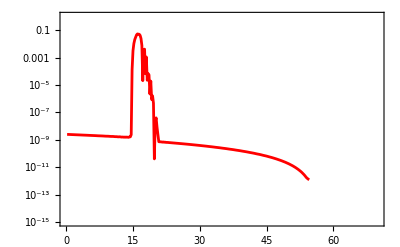

```mathematica
ListLogPlot[PN0,PlotRange->{{0,70},{10^-15,1}},Joined->True,Frame->True,PlotStyle->Red]
```

```mathematica
kmpc=Solve[0.05/Mpc==((a[Ne] H[Ne])/cs)/.solNe1/.Ne->0,Mpc][[1]][[1,2]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

549.188

```mathematica
Pkc=Table[{(kmpc((H[Ne]a[Ne])/cs)/.solNe1/.{Ne->NeHE[[i]]})[[1]],(k[[i]]^3/(2*Pi^2)*Abs[u[Ne]/(z[Ne]/.solNe1)]^2/.MSol[[i]]/.Ne->NeEnd[[i]])[[1]][[1]]},{i,1,iMax}]
```

{{0.0609748,2.45219×10^-9},{0.0743582,2.43915×10^-9},{0.0906787,2.4236×10^-9},{0.110581,2.40687×10^-9},{0.13485,2.39182×10^-9},{0.164445,2.37682×10^-9},{0.200534,2.36187×10^-9},{0.244542,2.34607×10^-9},{0.298206,2.33069×10^-9},{0.363644,2.31501×10^-9},{0.44344,2.30061×10^-9},{0.540743,2.2865×10^-9},{0.659394,2.27174×10^-9},{0.804074,2.25736×10^-9},{0.980494,2.24255×10^-9},{1.19562,2.22748×10^-9},{1.45793,2.21171×10^-9},{1.77778,2.19614×10^-9},{2.16779,2.18142×10^-9},{2.64335,2.16785×10^-9},{3.22321,2.15487×10^-9},{3.93026,2.14118×10^-9},{4.79238,2.1275×10^-9},{5.84357,2.11256×10^-9},{7.1253,2.097×10^-9},{8.68811,2.08111×10^-9},{10.5936,2.06577×10^-9},{12.917,2.05199×10^-9},{15.7498,2.04053×10^-9},{19.2038,2.02689×10^-9},{23.4152,2.01482×10^-9},{28.5499,2.00156×10^-9},{34.8103,1.98552×10^-9},{42.4433,1.96901×10^-9},{51.7496,1.95153×10^-9},{63.0962,1.9359×10^-9},{76.93,1.92451×10^-9},{93.7964,1.91382×10^-9},{114.36,1.90283×10^-9},{139.431,1.89179×10^-9},{169.996,1.87708×10^-9},{207.261,1.86037×10^-9},{252.693,1.84087×10^-9},{308.082,1.82249×10^-9},{375.61,1.81265×10^-9},{457.935,1.80772×10^-9},{558.299,1.79993×10^-9},{680.656,1.78172×10^-9},{829.822,1.75973×10^-9},{1011.67,1.74009×10^-9},{1233.36,1.73186×10^-9},{1503.62,1.73658×10^-9},{1833.08,1.72321×10^-9},{2234.71,1.6926×10^-9},{2724.32,1.67189×10^-9},{3321.16,1.67043×10^-9},{4048.73,1.66016×10^-9},{4935.63,1.62237×10^-9},{6016.74,1.61763×10^-9},{7334.58,1.63992×10^-9},{8940.95,1.60805×10^-9},{10899.,1.55488×10^-9},{13285.6,1.5725×10^-9},{16194.7,1.56112×10^-9},{19740.3,1.5204×10^-9},{24061.6,1.56485×10^-9},{29328.,1.51495×10^-9},{35745.9,1.55886×10^-9},{43566.6,1.52389×10^-9},{53095.8,1.48999×10^-9},{64705.2,1.59052×10^-9},{78846.5,1.62481×10^-9},{96068.4,2.33411×10^-9},{117035.,0.000132023},{142547.,0.00313749},{173565.,0.0105205},{211211.,0.0206021},{256681.,0.0308088},{306919.,0.0448953},{363974.,0.0530086},{435764.,0.0508775},{525152.,0.0501842},{635494.,0.0417219},{770968.,0.0246474},{936749.,0.00756638},{1.13923×10^6,0.0000205766},{1.38625×10^6,0.00361812},{1.68742×10^6,0.00411655},{2.05445×10^6,0.0000654261},{2.50167×10^6,0.00110197},{3.0465×10^6,0.0000219822},{3.71017×10^6,0.000066876},{4.51857×10^6,0.0000541064},{5.50322×10^6,2.18246×10^-6},{6.70251×10^6,0.0000190549},{8.16319×10^6,8.67908×10^-7},{9.94218×10^6,1.59194×10^-6},{1.21088×10^7,4.67564×10^-7},{1.47475×10^7,3.97761×10^-11},{1.79609×10^7,2.15464×10^-8},{2.18743×10^7,3.94728×10^-8},{2.664×10^7,8.26489×10^-9},{3.24435×10^7,2.3627×10^-9},{3.95109×10^7,7.13508×10^-10},{4.8117×10^7,7.03829×10^-10},{5.85967×10^7,7.01912×10^-10},{7.13577×10^7,6.89986×10^-10},{8.68962×10^7,6.65855×10^-10},{1.05816×10^8,6.84624×10^-10},{1.28854×10^8,6.55959×10^-10},{1.56904×10^8,6.63851×10^-10},{1.91057×10^8,6.39021×10^-10},{2.3264×10^8,6.36402×10^-10},{2.83268×10^8,6.33607×10^-10},{3.44907×10^8,6.24044×10^-10},{4.1995×10^8,6.13656×10^-10},{5.11311×10^8,6.08563×10^-10},{6.22535×10^8,5.98831×10^-10},{7.57939×10^8,5.93815×10^-10},{9.22774×10^8,5.82093×10^-10},{1.12343×10^9,5.79538×10^-10},{1.3677×10^9,5.67048×10^-10},{1.66504×10^9,5.63311×10^-10},{2.02697×10^9,5.52888×10^-10},{2.46753×10^9,5.48381×10^-10},{3.00378×10^9,5.40104×10^-10},{3.65648×10^9,5.32518×10^-10},{4.45091×10^9,5.2544×10^-10},{5.41781×10^9,5.19124×10^-10},{6.59461×10^9,5.1186×10^-10},{8.02683×10^9,5.04732×10^-10},{9.76986×10^9,4.98008×10^-10},{1.18911×10^10,4.9133×10^-10},{1.44725×10^10,4.84351×10^-10},{1.76139×10^10,4.77343×10^-10},{2.14367×10^10,4.70929×10^-10},{2.60884×10^10,4.64442×10^-10},{3.17486×10^10,4.57352×10^-10},{3.86359×10^10,4.506×10^-10},{4.7016×10^10,4.44456×10^-10},{5.72121×10^10,4.38025×10^-10},{6.96175×10^10,4.31221×10^-10},{8.47103×10^10,4.2468×10^-10},{1.03072×10^11,4.18689×10^-10},{1.25411×10^11,4.12401×10^-10},{1.52586×10^11,4.06073×10^-10},{1.85644×10^11,3.99708×10^-10},{2.25858×10^11,3.9356×10^-10},{2.74774×10^11,3.87454×10^-10},{3.34273×10^11,3.81296×10^-10},{4.06643×10^11,3.75199×10^-10},{4.94666×10^11,3.69138×10^-10},{6.01722×10^11,3.63156×10^-10},{7.31922×10^11,3.57405×10^-10},{8.90265×10^11,3.51836×10^-10},{1.08283×10^12,3.46152×10^-10},{1.31699×10^12,3.40394×10^-10},{1.60173×10^12,3.34475×10^-10},{1.94797×10^12,3.28552×10^-10},{2.36897×10^12,3.22712×10^-10},{2.88084×10^12,3.17274×10^-10},{3.50317×10^12,3.12157×10^-10},{4.25978×10^12,3.07022×10^-10},{5.1796×10^12,3.01741×10^-10},{6.29778×10^12,2.96357×10^-10},{7.65703×10^12,2.907×10^-10},{9.30926×10^12,2.85017×10^-10},{1.13175×10^13,2.7966×10^-10},{1.37584×10^13,2.74762×10^-10},{1.6725×10^13,2.70099×10^-10},{2.03303×10^13,2.65295×10^-10},{2.47117×10^13,2.60432×10^-10},{3.00358×10^13,2.55269×10^-10},{3.65053×10^13,2.49939×10^-10},{4.43661×10^13,2.44673×10^-10},{5.39169×10^13,2.39828×10^-10},{6.55204×10^13,2.35424×10^-10},{7.96169×10^13,2.31151×10^-10},{9.67411×10^13,2.26725×10^-10},{1.17542×10^14,2.22132×10^-10},{1.42808×10^14,2.17238×10^-10},{1.73494×10^14,2.12206×10^-10},{2.10763×10^14,2.07394×10^-10},{2.56021×10^14,2.03074×10^-10},{3.1098×10^14,1.99186×10^-10},{3.77714×10^14,1.95245×10^-10},{4.58739×10^14,1.9116×10^-10},{5.5711×10^14,1.8687×10^-10},{6.7653×10^14,1.82334×10^-10},{8.21493×10^14,1.77792×10^-10},{9.9745×10^14,1.73549×10^-10},{1.21101×10^15,1.69734×10^-10},{1.47019×10^15,1.66062×10^-10},{1.7847×10^15,1.6232×10^-10},{2.16634×10^15,1.5852×10^-10},{2.62937×10^15,1.54526×10^-10},{3.19113×10^15,1.50451×10^-10},{3.87258×10^15,1.46484×10^-10},{4.69915×10^15,1.4284×10^-10},{5.70167×10^15,1.39348×10^-10},{6.91744×10^15,1.35914×10^-10},{8.3917×10^15,1.3244×10^-10},{1.01792×10^16,1.28967×10^-10},{1.23463×10^16,1.25327×10^-10},{1.49732×10^16,1.2165×10^-10},{1.81572×10^16,1.18053×10^-10},{2.2016×10^16,1.14891×10^-10},{2.6692×10^16,1.11855×10^-10},{3.23576×10^16,1.08864×10^-10},{3.92213×10^16,1.0583×10^-10},{4.75353×10^16,1.02582×10^-10},{5.76048×10^16,9.92655×10^-11},{6.97986×10^16,9.58977×10^-11},{8.45627×10^16,9.27624×10^-11},{1.02436×10^17,9.00175×10^-11},{1.24071×10^17,8.75234×10^-11},{1.50253×10^17,8.49407×10^-11},{1.81934×10^17,8.22148×10^-11},{2.20262×10^17,7.93037×10^-11},{2.66623×10^17,7.62385×10^-11},{3.2269×10^17,7.33477×10^-11},{3.90483×10^17,7.06911×10^-11},{4.72435×10^17,6.84468×10^-11},{5.71482×10^17,6.61981×10^-11},{6.91163×10^17,6.38087×10^-11},{8.35742×10^17,6.13067×10^-11},{1.01036×10^18,5.87742×10^-11},{1.2212×10^18,5.63284×10^-11},{1.47571×10^18,5.41358×10^-11},{1.78286×10^18,5.20643×10^-11},{2.15343×10^18,4.98932×10^-11},{2.60037×10^18,4.77455×10^-11},{3.13924×10^18,4.55832×10^-11},{3.78875×10^18,4.3529×10^-11},{4.57131×10^18,4.15434×10^-11},{5.51384×10^18,3.96631×10^-11},{6.64861×10^18,3.77202×10^-11},{8.01424×10^18,3.57847×10^-11},{9.65701×10^18,3.39743×10^-11},{1.16322×10^19,3.22942×10^-11},{1.4006×10^19,3.06632×10^-11},{1.68573×10^19,2.90298×10^-11},{2.02801×10^19,2.73423×10^-11},{2.43867×10^19,2.57609×10^-11},{2.93105×10^19,2.42798×10^-11},{3.52099×10^19,2.28886×10^-11},{4.22733×10^19,2.14363×10^-11},{5.07232×10^19,2.00047×10^-11},{6.08234×10^19,1.872×10^-11},{7.28848×10^19,1.74802×10^-11},{8.72739×10^19,1.62276×10^-11},{1.04421×10^20,1.49932×10^-11},{1.2483×10^20,1.38808×10^-11},{1.49089×10^20,1.28482×10^-11},{1.77882×10^20,1.1786×10^-11},{2.12002×10^20,1.07552×10^-11},{2.52359×10^20,9.82958×10^-12},{2.99997×10^20,8.93263×10^-12},{3.56098×10^20,8.03927×10^-12},{4.21987×10^20,7.2557×10^-12},{4.99137×10^20,6.49951×10^-12},{5.8915×10^20,5.76925×10^-12},{6.93743×10^20,5.11883×10^-12},{8.14691×10^20,4.50852×10^-12},{9.53753×10^20,3.9113×10^-12},{1.11251×10^21,3.35074×10^-12},{1.29212×10^21,2.88096×10^-12},{1.49291×10^21,2.42996×10^-12},{1.71399×10^21,2.01505×10^-12},{1.95247×10^21,1.6778×10^-12},{2.202×10^21,1.47419×10^-12},{2.45109×10^21,1.30817×10^-12},{2.68047×10^21,1.19206×10^-12}}

```mathematica
Export["PkC.dat",Pkc];
```

```mathematica
Pkc=Import["PkC.dat"];
c1=Interpolation[Pkc,InterpolationOrder->1]
AA=LogLogPlot[{c1[x]},{x,0.0634257151149378,6.242598573013641*^19},PlotRange->{{0.001,4*10^22},{10^-13,1}},Frame->True,FrameStyle->Thick,FrameTicksStyle->Black,PlotStyle->{Purple},LabelStyle->Directive[24,Bold,Black,FontFamily->"Book Antiqua"],ImageSize->{600,400},AspectRatio->Full,RotateLabel->False,Axes->False,FrameLabel->{"K/Mpc^-1","P_s"}]
```

InterpolatingFunction[…]

```mathematica
InterpolatingFunction[…];
```

```mathematica
c1[0.05kmpc]
```

2.00437×10^-9

```mathematica
AA=ListLogLogPlot[Pkc,PlotRange->{{0.05,4*10^22},{10^-13,1}},Joined->True,Frame->True,FrameStyle->Thick,FrameTicksStyle->Black,PlotStyle->Darker[Blue],LabelStyle->Directive[24,Bold,Black,FontFamily->"Book Antiqua"],ImageSize->{600,400},AspectRatio->Full,RotateLabel->False,Axes->False,FrameLabel->{"K/Mpc^-1","P_R"}]
```

```mathematica
ss=-Graphics-;
```

```mathematica
fback=Show[{LogLogPlot[{ns0[Ne]},{Ne,1,10},PlotRange->{{10^-4,10^24},{10^-12,10^0}},PlotStyle->{Black,Thickness[0.005]},Frame-> True,FrameLabel->{"M/M_⊙","f_Pbh"},LabelStyle->Directive[22,Bold,FontFamily->"Book Antiqua"],ImageSize->{600,400},AspectRatio->Full],Graphics[{Texture[ss],EdgeForm[Black],Polygon[{{-9.1,-27.56},{55.2,-27.56},{55.2,0.1},{-9.1,0.1}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},ImageSize->{600,400},AspectRatio->Full]},Axes->False,RotateLabel->True]
```

```mathematica
Show[fback,AA]
```

```mathematica
Mkc=Table[(1/((1.9*10^6)^-2)*(1/(√3))^3/0.2*(106.75/10.75)^(-1/6)*(kmpc*k[[i]])^-2)[[1]],{i,1,iMax}];
```

```mathematica
PRc=Interpolation[Pkc,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
qend=PRc[[1,1,2]]
```

2.68047×10^21

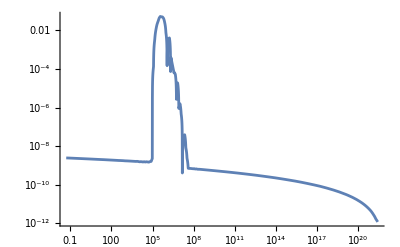

```mathematica
LogLogPlot[PRc[x],{x,0.05,qend},PlotRange->All]
```

```mathematica
For[i=1,i≤ iMax,i++,
si[i]=NIntegrate[16/81*1/q*(q/(k[[i]]*kmpc))^4 Exp[-q^2/(k[[i]]*kmpc)^2]PRc[q],{q,0,PRc[[1,1,2]]}];
]
```

```mathematica
Beep[]
```

```mathematica
sigma=Table[si[i],{i,1,iMax}]//N;
```

```mathematica
δc=0.4;
```

```mathematica
(*For[i=1,i≤ iMax,i++,
B[i]=√(1/(2Pi))(sigma[[i]])^(1/2)/δc Exp[(- δc^2)/(2*sigma[[i]])]]*)
```

```mathematica
For[i=1,i≤ iMax,i++,
B[i]=1/2 Erfc[δc/(√(2*sigma[[i]]))]]
```

```mathematica
f=Table[B[i]/(1.84*10^-8)*((1/(√3))^3/0.2)^(3/2)*(10.75/106.75)^(1/4)*(Mkc[[i]])^(-1/2),{i,1,iMax}];
```

```mathematica
ac=Table[{Mkc[[i]],f[[i]][[1]]},{i,1,iMax}];
```

```mathematica
Export["FPBHC.dat",ac];
```

```mathematica
ac=Import["FPBHC.dat"];
```

```mathematica
Max[f]
```

0.0016713

```mathematica
fc=ListLogLogPlot[ac,Joined->True,Frame->True,Axes->False,PlotRange->{{10^-18,10^4},{10^-5,1}},PlotStyle->{Purple,Thickness[0.002]}]
```

```mathematica
s1=Interpolation[ac,InterpolationOrder->2]
fc=LogLogPlot[s1[x],{x,3.86*^-39,7.0121*^14},Frame->True,Axes->False,PlotRange->{{10^-18,10^4},{10^-5,10^0}},PlotStyle->Red,FillingStyle->Black,ImageSize->{400,300}]
```

InterpolatingFunction[…]

```mathematica
fb=-Graphics-;
```

```mathematica
fback=Show[{LogLogPlot[{ns0[Ne]},{Ne,1,10},PlotRange->{{10^-18,10^4},{10^-5,10^0}},PlotStyle->{Black,Thickness[0.005]},Frame-> True,FrameLabel->{"M/M_⊙","f_Pbh"},LabelStyle->Directive[22,Bold,FontFamily->"Book Antiqua"],ImageSize->{600,400},AspectRatio->Full],Graphics[{Texture[fb],EdgeForm[Black],Polygon[{{-41.5,-11.55},{9.3,-11.55},{9.3,0},{-41.5,0}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},ImageSize->{600,400},AspectRatio->Full]},Axes->False,RotateLabel->True]
```

```mathematica
fpbh=Show[fback,fc,ImageSize->{600,400}]
```

```mathematica
Show[back,fc,ImageSize->{600,400}]
```

```mathematica
data2=Table[{i,(kmpc((a[Ne] H[Ne])/cs)/.solNe1/.{Ne->NeHE[[i]]})[[1]],NeHE[[i]],NeBD[[i]],Mkc[[i]],PN0[[i]][[2]],f[[i]]},{i,1,iMax}];
```

```mathematica
pr=data2[[All,6]];
```

```mathematica
Position[pr,Max[pr]][[1]][[1]]
```

80

```mathematica
Length[Pkc]
```

273

```mathematica
Pkc[[Position[pr,Max[pr]][[1]][[1]],2]]
```

0.0530086

```mathematica
Mkc[[Position[pr,Max[pr]][[1]][[1]]]]
```

17.8852

```mathematica
f[[Position[pr,Max[pr]][[1]][[1]]]]
```

{0.00161268}

```mathematica
kpeak=(kmpc((a[Ne] H[Ne])/cs)/.solNe1/.{Ne->NeHE[[Position[pr,Max[pr]][[1]][[1]]]]})
```

{363974.}

```mathematica
mytab2=Text@Grid[Prepend[data2,{"i","K","N","NBD","M(k)/M_o","P_R","f"}],Frame->All,Alignment->{Center},ItemSize->{10},Frame->Darker[Gray,.6],ItemStyle->14,Background->{Automatic,{1-> Green,Position[pr,Max[pr]][[1]][[1]]+1->Yellow}}]
```

i | K | N | NBD | M(k)/M_o | P_R | f
1 | 0.0609748 | 0.2 | -4.8 | 6.37286×10^14 | 2.45219×10^-9 | {0.}
2 | 0.0743582 | 0.4 | -4.6 | 4.28526×10^14 | 2.43915×10^-9 | {0.}
3 | 0.0906787 | 0.6 | -4.4 | 2.88154×10^14 | 2.4236×10^-9 | {0.}
4 | 0.110581 | 0.8 | -4.2 | 1.93766×10^14 | 2.40687×10^-9 | {0.}
5 | 0.13485 | 1. | -4. | 1.30297×10^14 | 2.39182×10^-9 | {0.}
6 | 0.164445 | 1.2 | -3.8 | 8.76182×10^13 | 2.37682×10^-9 | {0.}
7 | 0.200534 | 1.4 | -3.6 | 5.89195×10^13 | 2.36187×10^-9 | {0.}
8 | 0.244542 | 1.6 | -3.4 | 3.96213×10^13 | 2.34607×10^-9 | {0.}
9 | 0.298206 | 1.8 | -3.2 | 2.66442×10^13 | 2.33069×10^-9 | {0.}
10 | 0.363644 | 2. | -3. | 1.79177×10^13 | 2.31501×10^-9 | {0.}
11 | 0.44344 | 2.2 | -2.8 | 1.20494×10^13 | 2.30061×10^-9 | {0.}
12 | 0.540743 | 2.4 | -2.6 | 8.10314×10^12 | 2.2865×10^-9 | {0.}
13 | 0.659394 | 2.6 | -2.4 | 5.44937×10^12 | 2.27174×10^-9 | {0.}
14 | 0.804074 | 2.8 | -2.2 | 3.66474×10^12 | 2.25736×10^-9 | {0.}
15 | 0.980494 | 3. | -2. | 2.46459×10^12 | 2.24255×10^-9 | {0.}
16 | 1.19562 | 3.2 | -1.8 | 1.65749×10^12 | 2.22748×10^-9 | {0.}
17 | 1.45793 | 3.4 | -1.6 | 1.11471×10^12 | 2.21171×10^-9 | {0.}
18 | 1.77778 | 3.6 | -1.4 | 7.49686×10^11 | 2.19614×10^-9 | {0.}
19 | 2.16779 | 3.8 | -1.2 | 5.04197×10^11 | 2.18142×10^-9 | {0.}
20 | 2.64335 | 4. | -1. | 3.39099×10^11 | 2.16785×10^-9 | {0.}
21 | 3.22321 | 4.2 | -0.8 | 2.28064×10^11 | 2.15487×10^-9 | {0.}
22 | 3.93026 | 4.4 | -0.6 | 1.53388×10^11 | 2.14118×10^-9 | {0.}
23 | 4.79238 | 4.6 | -0.4 | 1.03165×10^11 | 2.1275×10^-9 | {0.}
24 | 5.84357 | 4.8 | -0.2 | 6.93871×10^10 | 2.11256×10^-9 | {0.}
25 | 7.1253 | 5. | 0. | 4.66691×10^10 | 2.097×10^-9 | {0.}
26 | 8.68811 | 5.2 | 0.2 | 3.13895×10^10 | 2.08111×10^-9 | {0.}
27 | 10.5936 | 5.4 | 0.4 | 2.11128×10^10 | 2.06577×10^-9 | {0.}
28 | 12.917 | 5.6 | 0.6 | 1.42008×10^10 | 2.05199×10^-9 | {0.}
29 | 15.7498 | 5.8 | 0.8 | 9.55175×10^9 | 2.04053×10^-9 | {0.}
30 | 19.2038 | 6. | 1. | 6.42479×10^9 | 2.02689×10^-9 | {0.}
31 | 23.4152 | 6.2 | 1.2 | 4.32156×10^9 | 2.01482×10^-9 | {0.}
32 | 28.5499 | 6.4 | 1.4 | 2.90688×10^9 | 2.00156×10^-9 | {0.}
33 | 34.8103 | 6.6 | 1.6 | 1.95533×10^9 | 1.98552×10^-9 | {0.}
34 | 42.4433 | 6.8 | 1.8 | 1.31528×10^9 | 1.96901×10^-9 | {0.}
35 | 51.7496 | 7. | 2. | 8.8475×10^8 | 1.95153×10^-9 | {0.}
36 | 63.0962 | 7.2 | 2.2 | 5.95154×10^8 | 1.9359×10^-9 | {0.}
37 | 76.93 | 7.4 | 2.4 | 4.00353×10^8 | 1.92451×10^-9 | {0.}
38 | 93.7964 | 7.6 | 2.6 | 2.69317×10^8 | 1.91382×10^-9 | {0.}
39 | 114.36 | 7.8 | 2.8 | 1.81171×10^8 | 1.90283×10^-9 | {0.}
40 | 139.431 | 8. | 3. | 1.21876×10^8 | 1.89179×10^-9 | {0.}
41 | 169.996 | 8.2 | 3.2 | 8.19891×10^7 | 1.87708×10^-9 | {0.}
42 | 207.261 | 8.4 | 3.4 | 5.51568×10^7 | 1.86037×10^-9 | {0.}
43 | 252.693 | 8.6 | 3.6 | 3.71063×10^7 | 1.84087×10^-9 | {0.}
44 | 308.082 | 8.8 | 3.8 | 2.49633×10^7 | 1.82249×10^-9 | {0.}
45 | 375.61 | 9. | 4. | 1.67943×10^7 | 1.81265×10^-9 | {0.}
46 | 457.935 | 9.2 | 4.2 | 1.12987×10^7 | 1.80772×10^-9 | {0.}
47 | 558.299 | 9.4 | 4.4 | 7.60153×10^6 | 1.79993×10^-9 | {0.}
48 | 680.656 | 9.6 | 4.6 | 5.11423×10^6 | 1.78172×10^-9 | {0.}
49 | 829.822 | 9.8 | 4.8 | 3.44085×10^6 | 1.75973×10^-9 | {0.}
50 | 1011.67 | 10. | 5. | 2.31503×10^6 | 1.74009×10^-9 | {0.}
51 | 1233.36 | 10.2 | 5.2 | 1.5576×10^6 | 1.73186×10^-9 | {0.}
52 | 1503.62 | 10.4 | 5.4 | 1.048×10^6 | 1.73658×10^-9 | {0.}
53 | 1833.08 | 10.6 | 5.6 | 705135. | 1.72321×10^-9 | {0.}
54 | 2234.71 | 10.8 | 5.8 | 474452. | 1.6926×10^-9 | {0.}
55 | 2724.32 | 11. | 6. | 319242. | 1.67189×10^-9 | {0.}
56 | 3321.16 | 11.2 | 6.2 | 214810. | 1.67043×10^-9 | {0.}
57 | 4048.73 | 11.4 | 6.4 | 144544. | 1.66016×10^-9 | {0.}
58 | 4935.63 | 11.6 | 6.6 | 97263.8 | 1.62237×10^-9 | {0.}
59 | 6016.74 | 11.8 | 6.8 | 65450.5 | 1.61763×10^-9 | {0.}
60 | 7334.58 | 12. | 7. | 44043.8 | 1.63992×10^-9 | {0.}
61 | 8940.95 | 12.2 | 7.2 | 29639.3 | 1.60805×10^-9 | {0.}
62 | 10899. | 12.4 | 7.4 | 19946.3 | 1.55488×10^-9 | {0.}
63 | 13285.6 | 12.6 | 7.6 | 13423.6 | 1.5725×10^-9 | {0.}
64 | 16194.7 | 12.8 | 7.8 | 9034.23 | 1.56112×10^-9 | {0.}
65 | 19740.3 | 13. | 8. | 6080.34 | 1.5204×10^-9 | {0.}
66 | 24061.6 | 13.2 | 8.2 | 4092.48 | 1.56485×10^-9 | {0.}
67 | 29328. | 13.4 | 8.4 | 2754.67 | 1.51495×10^-9 | {0.}
68 | 35745.9 | 13.6 | 8.6 | 1854.31 | 1.55886×10^-9 | {0.}
69 | 43566.6 | 13.8 | 8.8 | 1248.33 | 1.52389×10^-9 | {0.}
70 | 53095.8 | 14. | 9. | 840.457 | 1.48999×10^-9 | {0.}
71 | 64705.2 | 14.2 | 9.2 | 565.923 | 1.59052×10^-9 | {0.}
72 | 78846.5 | 14.4 | 9.4 | 381.128 | 1.62481×10^-9 | {4.94918×10^-198}
73 | 96068.4 | 14.6 | 9.6 | 256.729 | 2.33411×10^-9 | {6.35598×10^-74}
74 | 117035. | 14.8 | 9.8 | 172.984 | 0.000132023 | {1.07095×10^-33}
75 | 142547. | 15. | 10. | 116.605 | 0.00313749 | {1.93472×10^-17}
76 | 173565. | 15.2 | 10.2 | 78.6524 | 0.0105205 | {7.04717×10^-10}
77 | 211211. | 15.4 | 10.4 | 53.1129 | 0.0206021 | {4.14166×10^-6}
78 | 256681. | 15.6 | 10.6 | 35.9622 | 0.0308088 | {0.000310613}
79 | 306919. | 15.8 | 10.8 | 25.153 | 0.0448953 | {0.0016713}
80 | 363974. | 16. | 11. | 17.8852 | 0.0530086 | {0.00161268}
81 | 435764. | 16.2 | 11.2 | 12.4777 | 0.0508775 | {0.000227668}
82 | 525152. | 16.4 | 11.4 | 8.59143 | 0.0501842 | {1.68993×10^-6}
83 | 635494. | 16.6 | 11.6 | 5.86695 | 0.0417219 | {1.05436×10^-10}
84 | 770968. | 16.8 | 11.8 | 3.98623 | 0.0246474 | {3.20332×10^-18}
85 | 936749. | 17. | 12. | 2.70016 | 0.00756638 | {8.15944×10^-31}
86 | 1.13923×10^6 | 17.2 | 12.2 | 1.82564 | 0.0000205766 | {2.41926×10^-51}
87 | 1.38625×10^6 | 17.4 | 12.4 | 1.23297 | 0.00361812 | {3.13959×10^-85}
88 | 1.68742×10^6 | 17.6 | 12.6 | 0.83213 | 0.00411655 | {2.69362×10^-143}
89 | 2.05445×10^6 | 17.8 | 12.8 | 0.561362 | 0.0000654261 | {2.4283×10^-247}
90 | 2.50167×10^6 | 18. | 13. | 0.378595 | 0.00110197 | {0.}
91 | 3.0465×10^6 | 18.2 | 13.2 | 0.25529 | 0.0000219822 | {0.}
92 | 3.71017×10^6 | 18.4 | 13.4 | 0.172126 | 0.000066876 | {0.}
93 | 4.51857×10^6 | 18.6 | 13.6 | 0.116047 | 0.0000541064 | {0.}
94 | 5.50322×10^6 | 18.8 | 13.8 | 0.078235 | 2.18246×10^-6 | {0.}
95 | 6.70251×10^6 | 19. | 14. | 0.0527424 | 0.0000190549 | {0.}
96 | 8.16319×10^6 | 19.2 | 14.2 | 0.0355563 | 8.67908×10^-7 | {0.}
97 | 9.94218×10^6 | 19.4 | 14.4 | 0.0239702 | 1.59194×10^-6 | {0.}
98 | 1.21088×10^7 | 19.6 | 14.6 | 0.0161597 | 4.67564×10^-7 | {0.}
99 | 1.47475×10^7 | 19.8 | 14.8 | 0.0108943 | 3.97761×10^-11 | {0.}
100 | 1.79609×10^7 | 20. | 15. | 0.00734478 | 2.15464×10^-8 | {0.}
101 | 2.18743×10^7 | 20.2 | 15.2 | 0.00495185 | 3.94728×10^-8 | {0.}
102 | 2.664×10^7 | 20.4 | 15.4 | 0.00333863 | 8.26489×10^-9 | {0.}
103 | 3.24435×10^7 | 20.6 | 15.6 | 0.00225102 | 2.3627×10^-9 | {0.}
104 | 3.95109×10^7 | 20.8 | 15.8 | 0.00151776 | 7.13508×10^-10 | {0.}
105 | 4.8117×10^7 | 21. | 16. | 0.00102338 | 7.03829×10^-10 | {0.}
106 | 5.85967×10^7 | 21.2 | 16.2 | 0.000690064 | 7.01912×10^-10 | {0.}
107 | 7.13577×10^7 | 21.4 | 16.4 | 0.000465322 | 6.89986×10^-10 | {0.}
108 | 8.68962×10^7 | 21.6 | 16.6 | 0.000313786 | 6.65855×10^-10 | {0.}
109 | 1.05816×10^8 | 21.8 | 16.8 | 0.000211607 | 6.84624×10^-10 | {0.}
110 | 1.28854×10^8 | 22. | 17. | 0.000142705 | 6.55959×10^-10 | {0.}
111 | 1.56904×10^8 | 22.2 | 17.2 | 0.0000962425 | 6.63851×10^-10 | {0.}
112 | 1.91057×10^8 | 22.4 | 17.4 | 0.0000649096 | 6.39021×10^-10 | {0.}
113 | 2.3264×10^8 | 22.6 | 17.6 | 0.0000437791 | 6.36402×10^-10 | {0.}
114 | 2.83268×10^8 | 22.8 | 17.8 | 0.0000295285 | 6.33607×10^-10 | {0.}
115 | 3.44907×10^8 | 23. | 18. | 0.0000199174 | 6.24044×10^-10 | {0.}
116 | 4.1995×10^8 | 23.2 | 18.2 | 0.0000134351 | 6.13656×10^-10 | {0.}
117 | 5.11311×10^8 | 23.4 | 18.4 | 9.06286×10^-6 | 6.08563×10^-10 | {0.}
118 | 6.22535×10^8 | 23.6 | 18.6 | 6.11375×10^-6 | 5.98831×10^-10 | {0.}
119 | 7.57939×10^8 | 23.8 | 18.8 | 4.12446×10^-6 | 5.93815×10^-10 | {0.}
120 | 9.22774×10^8 | 24. | 19. | 2.78256×10^-6 | 5.82093×10^-10 | {0.}
121 | 1.12343×10^9 | 24.2 | 19.2 | 1.87733×10^-6 | 5.79538×10^-10 | {0.}
122 | 1.3677×10^9 | 24.4 | 19.4 | 1.26665×10^-6 | 5.67048×10^-10 | {0.}
123 | 1.66504×10^9 | 24.6 | 19.6 | 8.54649×10^-7 | 5.63311×10^-10 | {0.}
124 | 2.02697×10^9 | 24.8 | 19.8 | 5.76686×10^-7 | 5.52888×10^-10 | {0.}
125 | 2.46753×10^9 | 25. | 20. | 3.89144×10^-7 | 5.48381×10^-10 | {0.}
126 | 3.00378×10^9 | 25.2 | 20.2 | 2.62603×10^-7 | 5.40104×10^-10 | {0.}
127 | 3.65648×10^9 | 25.4 | 20.4 | 1.77219×10^-7 | 5.32518×10^-10 | {0.}
128 | 4.45091×10^9 | 25.6 | 20.6 | 1.19602×10^-7 | 5.2544×10^-10 | {0.}
129 | 5.41781×10^9 | 25.8 | 20.8 | 8.07213×10^-8 | 5.19124×10^-10 | {0.}
130 | 6.59461×10^9 | 26. | 21. | 5.44826×10^-8 | 5.1186×10^-10 | {0.}
131 | 8.02683×10^9 | 26.2 | 21.2 | 3.67746×10^-8 | 5.04732×10^-10 | {0.}
132 | 9.76986×10^9 | 26.4 | 21.4 | 2.48233×10^-8 | 4.98008×10^-10 | {0.}
133 | 1.18911×10^10 | 26.6 | 21.6 | 1.67568×10^-8 | 4.9133×10^-10 | {0.}
134 | 1.44725×10^10 | 26.8 | 21.8 | 1.13122×10^-8 | 4.84351×10^-10 | {0.}
135 | 1.76139×10^10 | 27. | 22. | 7.63699×10^-9 | 4.77343×10^-10 | {0.}
136 | 2.14367×10^10 | 27.2 | 22.2 | 5.15609×10^-9 | 4.70929×10^-10 | {0.}
137 | 2.60884×10^10 | 27.4 | 22.4 | 3.4813×10^-9 | 4.64442×10^-10 | {0.}
138 | 3.17486×10^10 | 27.6 | 22.6 | 2.35064×10^-9 | 4.57352×10^-10 | {0.}
139 | 3.86359×10^10 | 27.8 | 22.8 | 1.58728×10^-9 | 4.506×10^-10 | {0.}
140 | 4.7016×10^10 | 28. | 23. | 1.07188×10^-9 | 4.44456×10^-10 | {0.}
141 | 5.72121×10^10 | 28.2 | 23.2 | 7.23869×10^-10 | 4.38025×10^-10 | {0.}
142 | 6.96175×10^10 | 28.4 | 23.4 | 4.88876×10^-10 | 4.31221×10^-10 | {0.}
143 | 8.47103×10^10 | 28.6 | 23.6 | 3.30189×10^-10 | 4.2468×10^-10 | {0.}
144 | 1.03072×10^11 | 28.8 | 23.8 | 2.23024×10^-10 | 4.18689×10^-10 | {0.}
145 | 1.25411×10^11 | 29. | 24. | 1.50649×10^-10 | 4.12401×10^-10 | {0.}
146 | 1.52586×10^11 | 29.2 | 24.2 | 1.01767×10^-10 | 4.06073×10^-10 | {0.}
147 | 1.85644×10^11 | 29.4 | 24.4 | 6.875×10^-11 | 3.99708×10^-10 | {0.}
148 | 2.25858×10^11 | 29.6 | 24.6 | 4.64478×10^-11 | 3.9356×10^-10 | {0.}
149 | 2.74774×10^11 | 29.8 | 24.8 | 3.13824×10^-11 | 3.87454×10^-10 | {0.}
150 | 3.34273×10^11 | 30. | 25. | 2.12047×10^-11 | 3.81296×10^-10 | {0.}
151 | 4.06643×10^11 | 30.2 | 25.2 | 1.43288×10^-11 | 3.75199×10^-10 | {0.}
152 | 4.94666×10^11 | 30.4 | 25.4 | 9.68304×10^-12 | 3.69138×10^-10 | {0.}
153 | 6.01722×10^11 | 30.6 | 25.6 | 6.54401×10^-12 | 3.63156×10^-10 | {0.}
154 | 7.31922×10^11 | 30.8 | 25.8 | 4.42288×10^-12 | 3.57405×10^-10 | {0.}
155 | 8.90265×10^11 | 31. | 26. | 2.98949×10^-12 | 3.51836×10^-10 | {0.}
156 | 1.08283×10^12 | 31.2 | 26.2 | 2.02078×10^-12 | 3.46152×10^-10 | {0.}
157 | 1.31699×10^12 | 31.4 | 26.4 | 1.36606×10^-12 | 3.40394×10^-10 | {0.}
158 | 1.60173×10^12 | 31.6 | 26.6 | 9.23537×10^-13 | 3.34475×10^-10 | {0.}
159 | 1.94797×10^12 | 31.8 | 26.8 | 6.2441×10^-13 | 3.28552×10^-10 | {0.}
160 | 2.36897×10^12 | 32. | 27. | 4.22199×10^-13 | 3.22712×10^-10 | {0.}
161 | 2.88084×10^12 | 32.2 | 27.2 | 2.85495×10^-13 | 3.17274×10^-10 | {0.}
162 | 3.50317×10^12 | 32.4 | 27.4 | 1.93069×10^-13 | 3.12157×10^-10 | {0.}
163 | 4.25978×10^12 | 32.6 | 27.6 | 1.30575×10^-13 | 3.07022×10^-10 | {0.}
164 | 5.1796×10^12 | 32.8 | 27.8 | 8.83167×10^-14 | 3.01741×10^-10 | {0.}
165 | 6.29778×10^12 | 33. | 28. | 5.97394×10^-14 | 2.96357×10^-10 | {0.}
166 | 7.65703×10^12 | 33.2 | 28.2 | 4.04124×10^-14 | 2.907×10^-10 | {0.}
167 | 9.30926×10^12 | 33.4 | 28.4 | 2.73404×10^-14 | 2.85017×10^-10 | {0.}
168 | 1.13175×10^13 | 33.6 | 28.6 | 1.84984×10^-14 | 2.7966×10^-10 | {0.}
169 | 1.37584×10^13 | 33.8 | 28.8 | 1.2517×10^-14 | 2.74762×10^-10 | {0.}
170 | 1.6725×10^13 | 34. | 29. | 8.47039×10^-15 | 2.70099×10^-10 | {0.}
171 | 2.03303×10^13 | 34.2 | 29.2 | 5.73254×10^-15 | 2.65295×10^-10 | {0.}
172 | 2.47117×10^13 | 34.4 | 29.4 | 3.88×10^-15 | 2.60432×10^-10 | {0.}
173 | 3.00358×10^13 | 34.6 | 29.6 | 2.62637×10^-15 | 2.55269×10^-10 | {0.}
174 | 3.65053×10^13 | 34.8 | 29.8 | 1.77797×10^-15 | 2.49939×10^-10 | {0.}
175 | 4.43661×10^13 | 35. | 30. | 1.20374×10^-15 | 2.44673×10^-10 | {0.}
176 | 5.39169×10^13 | 35.2 | 30.2 | 8.15052×10^-16 | 2.39828×10^-10 | {0.}
177 | 6.55204×10^13 | 35.4 | 30.4 | 5.51928×10^-16 | 2.35424×10^-10 | {0.}
178 | 7.96169×10^13 | 35.6 | 30.6 | 3.73788×10^-16 | 2.31151×10^-10 | {0.}
179 | 9.67411×10^13 | 35.8 | 30.8 | 2.53171×10^-16 | 2.26725×10^-10 | {0.}
180 | 1.17542×10^14 | 36. | 31. | 1.71494×10^-16 | 2.22132×10^-10 | {0.}
181 | 1.42808×10^14 | 36.2 | 31.2 | 1.1618×10^-16 | 2.17238×10^-10 | {0.}
182 | 1.73494×10^14 | 36.4 | 31.4 | 7.87165×10^-17 | 2.12206×10^-10 | {0.}
183 | 2.10763×10^14 | 36.6 | 31.6 | 5.33395×10^-17 | 2.07394×10^-10 | {0.}
184 | 2.56021×10^14 | 36.8 | 31.8 | 3.61479×10^-17 | 2.03074×10^-10 | {0.}
185 | 3.1098×10^14 | 37. | 32. | 2.45002×10^-17 | 1.99186×10^-10 | {0.}
186 | 3.77714×10^14 | 37.2 | 32.2 | 1.66077×10^-17 | 1.95245×10^-10 | {0.}
187 | 4.58739×10^14 | 37.4 | 32.4 | 1.12591×10^-17 | 1.9116×10^-10 | {0.}
188 | 5.5711×10^14 | 37.6 | 32.6 | 7.63403×10^-18 | 1.8687×10^-10 | {0.}
189 | 6.7653×10^14 | 37.8 | 32.8 | 5.1768×10^-18 | 1.82334×10^-10 | {0.}
190 | 8.21493×10^14 | 38. | 33. | 3.51097×10^-18 | 1.77792×10^-10 | {0.}
191 | 9.9745×10^14 | 38.2 | 33.2 | 2.38151×10^-18 | 1.73549×10^-10 | {0.}
192 | 1.21101×10^15 | 38.4 | 33.4 | 1.61562×10^-18 | 1.69734×10^-10 | {0.}
193 | 1.47019×10^15 | 38.6 | 33.6 | 1.0962×10^-18 | 1.66062×10^-10 | {0.}
194 | 1.7847×10^15 | 38.8 | 33.8 | 7.4388×10^-19 | 1.6232×10^-10 | {0.}
195 | 2.16634×10^15 | 39. | 34. | 5.04874×10^-19 | 1.5852×10^-10 | {0.}
196 | 2.62937×10^15 | 39.2 | 34.2 | 3.42713×10^-19 | 1.54526×10^-10 | {0.}
197 | 3.19113×10^15 | 39.4 | 34.4 | 2.32674×10^-19 | 1.50451×10^-10 | {0.}
198 | 3.87258×10^15 | 39.6 | 34.6 | 1.57992×10^-19 | 1.46484×10^-10 | {0.}
199 | 4.69915×10^15 | 39.8 | 34.8 | 1.07299×10^-19 | 1.4284×10^-10 | {0.}
200 | 5.70167×10^15 | 40. | 35. | 7.28839×10^-20 | 1.39348×10^-10 | {0.}
201 | 6.91744×10^15 | 40.2 | 35.2 | 4.95158×10^-20 | 1.35914×10^-10 | {0.}
202 | 8.3917×10^15 | 40.4 | 35.4 | 3.36461×10^-20 | 1.3244×10^-10 | {0.}
203 | 1.01792×10^16 | 40.6 | 35.6 | 2.28669×10^-20 | 1.28967×10^-10 | {0.}
204 | 1.23463×10^16 | 40.8 | 35.8 | 1.5544×10^-20 | 1.25327×10^-10 | {0.}
205 | 1.49732×10^16 | 41. | 36. | 1.05683×10^-20 | 1.2165×10^-10 | {0.}
206 | 1.81572×10^16 | 41.2 | 36.2 | 7.18681×10^-21 | 1.18053×10^-10 | {0.}
207 | 2.2016×10^16 | 41.4 | 36.4 | 4.8883×10^-21 | 1.14891×10^-10 | {0.}
208 | 2.6692×10^16 | 41.6 | 36.6 | 3.32562×10^-21 | 1.11855×10^-10 | {0.}
209 | 3.23576×10^16 | 41.8 | 36.8 | 2.26299×10^-21 | 1.08864×10^-10 | {0.}
210 | 3.92213×10^16 | 42. | 37. | 1.54025×10^-21 | 1.0583×10^-10 | {0.}
211 | 4.75353×10^16 | 42.2 | 37.2 | 1.04858×10^-21 | 1.02582×10^-10 | {0.}
212 | 5.76048×10^16 | 42.4 | 37.4 | 7.14033×10^-22 | 9.92655×10^-11 | {0.}
213 | 6.97986×10^16 | 42.6 | 37.6 | 4.86343×10^-22 | 9.58977×10^-11 | {0.}
214 | 8.45627×10^16 | 42.8 | 37.8 | 3.31343×10^-22 | 9.27624×10^-11 | {0.}
215 | 1.02436×10^17 | 43. | 38. | 2.25802×10^-22 | 9.00175×10^-11 | {0.}
216 | 1.24071×10^17 | 43.2 | 38.2 | 1.53921×10^-22 | 8.75234×10^-11 | {0.}
217 | 1.50253×10^17 | 43.4 | 38.4 | 1.04952×10^-22 | 8.49407×10^-11 | {0.}
218 | 1.81934×10^17 | 43.6 | 38.6 | 7.15826×10^-23 | 8.22148×10^-11 | {0.}
219 | 2.20262×10^17 | 43.8 | 38.8 | 4.88378×10^-23 | 7.93037×10^-11 | {0.}
220 | 2.66623×10^17 | 44. | 39. | 3.33304×10^-23 | 7.62385×10^-11 | {0.}
221 | 3.2269×10^17 | 44.2 | 39.2 | 2.27543×10^-23 | 7.33477×10^-11 | {0.}
222 | 3.90483×10^17 | 44.4 | 39.4 | 1.55393×10^-23 | 7.06911×10^-11 | {0.}
223 | 4.72435×10^17 | 44.6 | 39.6 | 1.06158×10^-23 | 6.84468×10^-11 | {0.}
224 | 5.71482×10^17 | 44.8 | 39.8 | 7.25489×10^-24 | 6.61981×10^-11 | {0.}
225 | 6.91163×10^17 | 45. | 40. | 4.95992×10^-24 | 6.38087×10^-11 | {0.}
226 | 8.35742×10^17 | 45.2 | 40.2 | 3.39227×10^-24 | 6.13067×10^-11 | {0.}
227 | 1.01036×10^18 | 45.4 | 40.4 | 2.32106×10^-24 | 5.87742×10^-11 | {0.}
228 | 1.2212×10^18 | 45.6 | 40.6 | 1.58878×10^-24 | 5.63284×10^-11 | {0.}
229 | 1.47571×10^18 | 45.8 | 40.8 | 1.08801×10^-24 | 5.41358×10^-11 | {0.}
230 | 1.78286×10^18 | 46. | 41. | 7.45417×10^-25 | 5.20643×10^-11 | {0.}
231 | 2.15343×10^18 | 46.2 | 41.2 | 5.10944×10^-25 | 4.98932×10^-11 | {0.}
232 | 2.60037×10^18 | 46.4 | 41.4 | 3.50401×10^-25 | 4.77455×10^-11 | {0.}
233 | 3.13924×10^18 | 46.6 | 41.6 | 2.40428×10^-25 | 4.55832×10^-11 | {0.}
234 | 3.78875×10^18 | 46.8 | 41.8 | 1.65061×10^-25 | 4.3529×10^-11 | {0.}
235 | 4.57131×10^18 | 47. | 42. | 1.13385×10^-25 | 4.15434×10^-11 | {0.}
236 | 5.51384×10^18 | 47.2 | 42.2 | 7.7934×10^-26 | 3.96631×10^-11 | {0.}
237 | 6.64861×10^18 | 47.4 | 42.4 | 5.36012×10^-26 | 3.77202×10^-11 | {0.}
238 | 8.01424×10^18 | 47.6 | 42.6 | 3.68901×10^-26 | 3.57847×10^-11 | {0.}
239 | 9.65701×10^18 | 47.8 | 42.8 | 2.54068×10^-26 | 3.39743×10^-11 | {0.}
240 | 1.16322×10^19 | 48. | 43. | 1.75109×10^-26 | 3.22942×10^-11 | {0.}
241 | 1.4006×10^19 | 48.2 | 43.2 | 1.20783×10^-26 | 3.06632×10^-11 | {0.}
242 | 1.68573×10^19 | 48.4 | 43.4 | 8.33798×10^-27 | 2.90298×10^-11 | {0.}
243 | 2.02801×10^19 | 48.6 | 43.6 | 5.76094×10^-27 | 2.73423×10^-11 | {0.}
244 | 2.43867×10^19 | 48.8 | 43.8 | 3.98408×10^-27 | 2.57609×10^-11 | {0.}
245 | 2.93105×10^19 | 49. | 44. | 2.75797×10^-27 | 2.42798×10^-11 | {0.}
246 | 3.52099×10^19 | 49.2 | 44.2 | 1.91119×10^-27 | 2.28886×10^-11 | {0.}
247 | 4.22733×10^19 | 49.4 | 44.4 | 1.32588×10^-27 | 2.14363×10^-11 | {0.}
248 | 5.07232×10^19 | 49.6 | 44.6 | 9.20919×10^-28 | 2.00047×10^-11 | {0.}
249 | 6.08234×10^19 | 49.8 | 44.8 | 6.40463×10^-28 | 1.872×10^-11 | {0.}
250 | 7.28848×10^19 | 50. | 45. | 4.46027×10^-28 | 1.74802×10^-11 | {0.}
251 | 8.72739×10^19 | 50.2 | 45.2 | 3.11076×10^-28 | 1.62276×10^-11 | {0.}
252 | 1.04421×10^20 | 50.4 | 45.4 | 2.17299×10^-28 | 1.49932×10^-11 | {0.}
253 | 1.2483×10^20 | 50.6 | 45.6 | 1.52053×10^-28 | 1.38808×10^-11 | {0.}
254 | 1.49089×10^20 | 50.8 | 45.8 | 1.06597×10^-28 | 1.28482×10^-11 | {0.}
255 | 1.77882×10^20 | 51. | 46. | 7.48808×10^-29 | 1.1786×10^-11 | {0.}
256 | 2.12002×10^20 | 51.2 | 46.2 | 5.27178×10^-29 | 1.07552×10^-11 | {0.}
257 | 2.52359×10^20 | 51.4 | 46.4 | 3.72048×10^-29 | 9.82958×10^-12 | {0.}
258 | 2.99997×10^20 | 51.6 | 46.6 | 2.63269×10^-29 | 8.93263×10^-12 | {0.}
259 | 3.56098×10^20 | 51.8 | 46.8 | 1.86852×10^-29 | 8.03927×10^-12 | {0.}
260 | 4.21987×10^20 | 52. | 47. | 1.33057×10^-29 | 7.2557×10^-12 | {0.}
261 | 4.99137×10^20 | 52.2 | 47.2 | 9.51033×10^-30 | 6.49951×10^-12 | {0.}
262 | 5.8915×10^20 | 52.4 | 47.4 | 6.82627×10^-30 | 5.76925×10^-12 | {0.}
263 | 6.93743×10^20 | 52.6 | 47.6 | 4.92309×10^-30 | 5.11883×10^-12 | {0.}
264 | 8.14691×10^20 | 52.8 | 47.8 | 3.56985×10^-30 | 4.50852×10^-12 | {0.}
265 | 9.53753×10^20 | 53. | 48. | 2.60473×10^-30 | 3.9113×10^-12 | {0.}
266 | 1.11251×10^21 | 53.2 | 48.2 | 1.91436×10^-30 | 3.35074×10^-12 | {0.}
267 | 1.29212×10^21 | 53.4 | 48.4 | 1.41916×10^-30 | 2.88096×10^-12 | {0.}
268 | 1.49291×10^21 | 53.6 | 48.6 | 1.06309×10^-30 | 2.42996×10^-12 | {0.}
269 | 1.71399×10^21 | 53.8 | 48.8 | 8.06528×10^-31 | 2.01505×10^-12 | {0.}
270 | 1.95247×10^21 | 54. | 49. | 6.21538×10^-31 | 1.6778×10^-12 | {0.}
271 | 2.202×10^21 | 54.2 | 49.2 | 4.88653×10^-31 | 1.47419×10^-12 | {0.}
272 | 2.45109×10^21 | 54.4 | 49.4 | 3.94383×10^-31 | 1.30817×10^-12 | {0.}
273 | 2.68047×10^21 | 54.6 | 49.6 | 3.29772×10^-31 | 1.19206×10^-12 | {0.}

```mathematica
Reheating
```

Reheating

```mathematica
ρend=3 H[Ne]^2/.solNe1/.Ne->NeFIN;
Hstar=H[Ne]/.solNe1/.Ne->0;
```

```mathematica
(*n=2;
wre=(n-2α)/(n(2α-1)+2α)*)(*in non-canonical power-law inflation with quadratic potential n=2 unikrishnan JCAP 08 (2012) 018*)
```

```mathematica
Nre=4(*1/(1-3ww)*)(61.6-Log[ρend^(1/4)/Hstar]-NeFIN)(*in canonical reheating we consider wre=0*)
```

{8.1544}

```mathematica
(*f=2;
Nrre=4(*1/(1-3ww)*)(61.6-Log[(((3α)/(α+1))V[ϕ[Ne]]/.solNe1/.Ne->NeFIN)^(1/4)/Hstar]-NeFIN)*)
(*in non-canonical power-law inflation with ρend=((3α)/(α+1))Vend Safaii arXiv  *)
```

```mathematica
kend=kmpc*(a[Ne] *H[Ne])/cs/.solNe1/.Ne->NeFIN
```

{2.93759×10^21}

```mathematica
kre=Exp[-Nre/2]*kend
```

{4.98066×10^19}

```mathematica
kpeak=(kmpc((a[Ne] H[Ne])/cs)/.solNe1/.{Ne->NeHE[[Position[pr,Max[pr]][[1]][[1]]]]})
```

{363974.}

```mathematica
Npeak=NeHE[[Position[pr,Max[pr]][[1]][[1]]]]
```

16.

```mathematica
g=106.75;
w=0;
mp=2.43×10^18;
```

```mathematica
Treh=(30/(π^2 g)ρend*mp^4)^(1/4)Exp[-3/4(1+w)Nre]
```

{3.04479×10^12}

```mathematica
Rehplot=ListLogLogPlot[{{{kend[[1]],10},{kre[[1]],10}}},PlotRange->{{0.01,4*10^22},{10^-13,1}},Frame->True,Joined->{True},Filling->{1->Bottom},Axes->False,FillingStyle->{Opacity[0.2,Blue]},PlotStyle->{Black,Thickness[0.005]},FrameLabel->{"k/Mpc^-1","P_R"},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameStyle->Thick,FrameTicksStyle->Black,ImageSize->{600,400},AspectRatio->Full,FrameTicks->{{All,None},{All,None}}]
```

```mathematica
reh3=Show[Rehplot,AA]
```

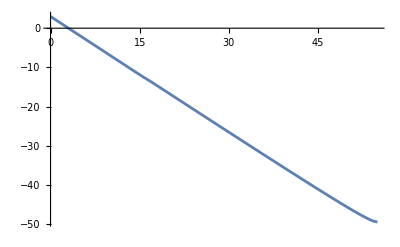

```mathematica
Plot[Log[cs/(kmpc*a[Ne]H[Ne])]/.solNe1,{Ne,0,NeFIN}]
```

```mathematica
Netotal=NeFIN+Nre(*Ntotal=Nend+Nreh*)
```

{63.1643}

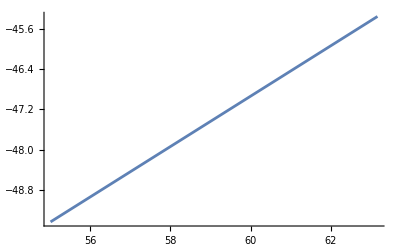

```mathematica
Plot[Log[1/kend[[1]]]+1/2(Ne-NeFIN),{Ne,NeFIN,Netotal[[1]]}]
```

```mathematica
endofinf=Log[cs/(kmpc*a[Ne]H[Ne])]/.solNe1/.Ne->NeFIN (*Log(1/k) at the end of inflation*)
```

{-49.4319}

```mathematica
endofreh=Log[1/kend[[1]]]+1/2(Netotal[[1]]-NeFIN)(*Log(1/k) at the end of reheating (RD start)*)
```

-45.3547

```mathematica
endofrd=endofreh+(100-Netotal[[1]])(*Log(1/k) at the end of RD (MD Start)*)
```

-8.51901

```mathematica
pw=Piecewise[{{Log[cs/(kmpc*(a[Ne]H[Ne])/.solNe1)][[1]],-2<Ne< NeFIN}, 
{endofinf[[1]]+1/2(Ne-NeFIN),NeFIN≤ Ne< Netotal[[1]]},
{endofreh+(Ne-Netotal[[1]]),Netotal[[1]]≤ Ne<100},
{endofrd+ 1/2(Ne-100),100≤ Ne≤130}}]
```

Piecewise[{{Log[(0.000291573 ⅇ^-Ne)/(InterpolatingFunction[…][Ne])], -2<Ne<55.0099}, {-49.4319+1/2 (-55.0099+Ne), 55.0099≤Ne<63.1643}, {-108.519+Ne, 63.1643≤Ne<100}, {-8.51901+1/2 (-100+Ne), 100≤Ne≤130}, {0, True}}]

```mathematica
line1=Line[{{0,-NeFIN},{0,1.2}}];(*Vertucal line at CMB scale*)
line2=Line[{{NeFIN,-NeFIN},{NeFIN,-40}}];(*Vertucal line at Subscript[N, end]*)
line3=Line[{{Netotal[[1]],-NeFIN},{Netotal[[1]],-40}}];(*Vertucal line at the end of reheating (RD start)*)
line4=Line[{{100,-NeFIN},{100,-10}}];(*Vertucal line at the end of RD (MD start)*)
```

```mathematica
kINcmb=Log[1/0.05]
kINpeak=Log[1/kpeak[[1]]]
KINreh=Log[1/kre[[1]]](*critical scale ->  Subscript[k, reh]^-1*)
```

2.99573

-12.8048

-45.3547

```mathematica
Plot[endofinf[[1]]+1/2(Ne-NeFIN),{ Ne,NeFIN, Netotal[[1]]}]
```

```mathematica
Plot[pw,{Ne,-2,130}]
```

```mathematica
comphi1=Plot[{pw,endofinf[[1]],endofreh,kINcmb,kINpeak,KINreh},{Ne,-2,128},Frame->True,Axes->False,PlotStyle->{{Black,Thickness[0.005]},{Transparent},{Transparent},{Dashing[0.025],Darker[Red]},{Dashing[0.025],Blue}(*,{Dashing[0.025],Blue},{Dashing[0.025],Lighter[Blue]}*),{Dashing[0.025],Darker[Green]}},FrameStyle->Directive[Thickness[0.003]],(*FrameTicks->{{Automatic,None},{None}},*)FrameTicks->{{None,None},{ {{0,"N_*"},{NeFIN,"N_end   "},{NeFIN+Nre[[1]],"      N_reh"},{100,"N_eq"}},None}},Filling->{2->{3}},FillingStyle->{Opacity[0.2,Blue]},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameLabel->{"N=Lna","Comoving Hubble Radius Ln(1/aH)"},Epilog->{Directive[Gray,Dashed],line1,line2,line3,line4,
Text[Style["k_peak^-1",18,FontFamily->"Cambria",Bold,Black],{6.5,-10}],
Text[Style["k_*^-1",18,FontFamily->"Cambria",Bold,Black],{4.65,5.6}],
Text[Style["k_reh^-1",18,FontFamily->"Cambria",Bold,Black],{6.5,-41}],
(*Text[Style["Pivot Scale",10,FontFamily->"Cambria",Black],{2,-19.5},Automatic,{0,6}],*)
(*Text[Style["⟵ End of Inflation",10,FontFamily->"Cambria",Black],{54.9,-17.5},Automatic,{0,6}],*)
Text[Style["  reh",15,FontFamily->"Cambria",Black],{58.5,-40},Automatic,{1,0}],
Text[Style[" ⟵——RD——⟶",18,FontFamily->"Cambria",Black],{81,-51},Automatic,{1,0}],
Text[Style[" ⟵—MD—⟶",18,FontFamily->"Cambria",Black],{114,-51},Automatic,{1,0}]},ImageSize->{600,400}]
```

```mathematica
psreh3n=Show[{reh3,Graphics[{Directive[Gray,Dashed],Line[{{-3,-50},{-3,-20}}],Line[{{13.,-40},{13.0,-3.4}}],Line[{{45.3,-52},{45.3,-24.5}}]}],Graphics[{Darker[Red],PointSize[0.02],Point[{-3,-20}]}],Graphics[{Darker[Blue],PointSize[0.02],Point[{13.1,-3}]}],Graphics[{Darker[Green],PointSize[0.02],Point[{45.4,-24.6}]}]}]
```

```mathematica
Export["reh3.eps",psreh3n];
```

```mathematica
cC=Show[{comphi1,Graphics[{Black,PointSize[0.015],Point[{NeFIN,endofinf[[1]]}],Point[{Netotal[[1]],endofreh}],Point[{100,-8.8}]}],
Graphics[{{Darker[Red],PointSize[0.015],
Point[{0.05,kINcmb}],Point[{123.4,kINcmb}]},{Darker[Blue],PointSize[0.015],
Point[{16.,kINpeak}],Point[{96,kINpeak}]},{Darker[Green],PointSize[0.015],
Point[{49.5,KINreh}],Point[{Netotal[[1]],endofreh}]}(*,
Point[{32.75,kINFree}],Point[{79.,kINFree}]*)}](*,Graphics[{Green,Thick,Circle[{43.8,-22.9},0.5]}]*)},Graphics[{Directive[Gray,Dashed](*,Line[{{-3,-50},{-3,-20}}],Line[{{29.6,-40},{29.6,-3.4}}],Line[{{43.8,-50},{43.8,-23}}]*)}]]
```

```mathematica
Export["com-rehC.eps",cC];
```

#### Solving tensor Mukhanov Sasaki Equation (16)

```mathematica
nPoints=5;
iMax=(NeFIN-.6)*nPoints;
NeHEt=Table[0+i/nPoints,{i,0,iMax}]//N;
NeBDt=Table[NeHEt[[i]]-1(*If[NeHEt[[i]]≤39,NeHEt[[i]]-5,NeHEt[[i]]-1]*),{i,1,iMax}]//N;
NeEndt=Table[(*NeFIN*)(*If[NeHE[[i]]≤31,NeHE[[i]]+3,NeFIN-.7]*)If[NeHEt[[i]]+1≤NeFIN,NeHEt[[i]]-.64,NeFIN],{i,1,iMax}];
kt=Table[(H[Ne]*a[Ne])/.solNe1/.{Ne->NeHEt[[i]]},{i,1,iMax}]//N;
For[i=1,i≤iMax-(iMax-1),i++,
tAux=AbsoluteTime[];
MSsolAuxt[i]=NDSolve[{((ut''[Ne]+(H'[Ne]/H[Ne]+a'[Ne]/a[Ne])ut'[Ne]+(kt[[i]]/(a[Ne] H[Ne]))^2 ut[Ne]-a''[Ne]/a[Ne] ut[Ne]-a'[Ne]/a[Ne](H'[Ne]/H[Ne]+a'[Ne]/a[Ne])ut[Ne])/.solNe1)==0,ut[NeBD[[i]]]==1/(√(2kt[[i]]))/.solNe1/.{Ne->NeBDt[[i]]},ut'[NeBDt[[i]]]==((-I kt[[i]])/(a[Ne] H[Ne] √2 √kt[[i]]))/.solNe1/.{Ne->NeBDt[[i]]}},{ut[Ne]},{Ne,NeBDt[[i]],NeEndt[[i]]},MaxSteps->Infinity(*Method->{"EquationSimplification"->"Solve"}*)(*,WorkingPrecision->30*)][[1]];Print[NeHEt[[i]]//N,"  ",kt[[i]]//N,"  ",AbsoluteTime[]-tAux]]
MSolt=Table[MSsolAuxt[i],{i,1,iMax}];
j=1;
PNt0=Table[{NeHEt[[i]],((j kt[[i]]^3/Pi^2*Abs[(ut[Ne]/.solNe1)/(a[Ne]/.solNe1)]^2)/.MSolt[[i]]/.Ne->NeEndt[[i]])[[1]][[1]]},{i,1,iMax-(iMax-1)}]
```

0.  {0.0000145786}  3.6609421

{{0.,5.18934×10^-10}}

```mathematica
Off[NDSolve::precw];
For[i=1,i≤iMax,i++,
tAux=AbsoluteTime[];
MSsolAuxt[i]=NDSolve[{((ut''[Ne]+(H'[Ne]/H[Ne]+a'[Ne]/a[Ne])ut'[Ne]+(kt[[i]]/(a[Ne] H[Ne]))^2 ut[Ne]-a''[Ne]/a[Ne] ut[Ne]-a'[Ne]/a[Ne](H'[Ne]/H[Ne]+a'[Ne]/a[Ne])ut[Ne])/.solNe1)==0,ut[NeBDt[[i]]]==1/(√(2kt[[i]]))/.solNe1/.{Ne->NeBDt[[i]]},ut'[NeBDt[[i]]]==((-I kt[[i]])/(a[Ne] H[Ne] √2 √kt[[i]]))/.solNe1/.{Ne->NeBDt[[i]]}},{ut[Ne]},{Ne,NeBDt[[i]],NeEndt[[i]]},MaxSteps->Infinity(*Method->{"EquationSimplification"->"Solve"}*)(*,WorkingPrecision->30*)][[1]];Print[NeHEt[[i]]//N,"  ",kt[[i]]//N,"  ",AbsoluteTime[]-tAux]]
MSolt=Table[MSsolAuxt[i],{i,1,iMax}];
```

0.  {0.0000145786}  0.016499

0.2  {0.0000177786}  0.

0.4  {0.0000216808}  0.015007

0.6  {0.0000264394}  0.

0.8  {0.0000322423}  0.

1.  {0.0000393186}  0.015637

1.2  {0.0000479477}  0.

1.4  {0.0000584703}  0.

1.6  {0.0000713017}  0.015624

1.8  {0.0000869487}  0.

2.  {0.000106029}  0.

2.2  {0.000129295}  0.

2.4  {0.000157666}  0.016389

2.6  {0.000192261}  0.

2.8  {0.000234446}  0.0070454

3.  {0.000285885}  0.

3.2  {0.000348609}  0.

3.4  {0.000425092}  0.0087428

3.6  {0.000518352}  0.

3.8  {0.000632069}  0.

4.  {0.000770729}  0.

4.2  {0.000939802}  0.015006

4.4  {0.00114596}  0.

4.6  {0.00139733}  0.

4.8  {0.00170383}  0.

5.  {0.00207754}  0.015636

5.2  {0.00253322}  0.

5.4  {0.00308881}  0.

5.6  {0.00376625}  0.

5.8  {0.00459223}  0.

6.  {0.00559932}  0.015621

6.2  {0.00682723}  0.

6.4  {0.00832436}  0.

6.6  {0.0101497}  0.015713

6.8  {0.0123753}  0.

7.  {0.0150888}  0.

7.2  {0.0183971}  0.016194

7.4  {0.0224307}  0.

7.6  {0.0273485}  0.

7.8  {0.0333442}  0.

8.  {0.0406542}  0.013018

8.2  {0.0495663}  0.002018

8.4  {0.0604318}  0.

8.6  {0.0736785}  0.

8.8  {0.0898284}  0.

9.  {0.109518}  0.015895

9.2  {0.133521}  0.

9.4  {0.162785}  0.016311

9.6  {0.198461}  0.

9.8  {0.241954}  0.

10.  {0.294976}  0.015007

10.2  {0.359614}  0.

10.4  {0.438414}  0.015646

10.6  {0.534477}  0.

10.8  {0.651581}  0.015636

11.  {0.794337}  0.

11.2  {0.968361}  0.

11.4  {1.1805}  0.

11.6  {1.43909}  0.015696

11.8  {1.75432}  0.0040252

12.  {2.13856}  0.012027

12.2  {2.60694}  0.

12.4  {3.17785}  0.016313

12.6  {3.87373}  0.

12.8  {4.72193}  0.

13.  {5.75573}  0.

13.2  {7.01571}  0.015013

13.4  {8.55125}  0.

13.6  {10.4225}  0.

13.8  {12.7028}  0.

14.  {15.4813}  0.016295

14.2  {18.8663}  0.

14.4  {22.9895}  0.

14.6  {28.0109}  0.

14.8  {34.1242}  0.

15.  {41.5629}  0.015011

15.2  {50.6068}  0.

15.4  {61.5835}  0.

15.6  {74.8413}  0.

15.8  {89.4891}  0.016144

16.  {106.125}  0.0095238

16.2  {127.057}  0.0066062

16.4  {153.12}  0.

16.6  {185.293}  0.016245

16.8  {224.793}  0.

17.  {273.13}  0.

17.2  {332.167}  0.

17.4  {404.193}  0.015006

17.6  {492.005}  0.

17.8  {599.022}  0.

18.  {729.419}  0.

18.2  {888.276}  0.

18.4  {1081.79}  0.015634

18.6  {1317.49}  0.

18.8  {1604.59}  0.

19.  {1954.27}  0.

19.2  {2380.16}  0.

19.4  {2898.87}  0.015625

19.6  {3530.6}  0.

19.8  {4299.96}  0.

20.  {5236.91}  0.

20.2  {6377.95}  0.

20.4  {7767.49}  0.016254

20.6  {9459.65}  0.

20.8  {11520.3}  0.

21.  {14029.6}  0.

21.2  {17085.2}  0.014515

21.4  {20806.}  0.

21.6  {25336.6}  0.

21.8  {30853.2}  0.

22.  {37570.3}  0.

22.2  {45749.}  0.015646

22.4  {55707.1}  0.

22.6  {67831.4}  0.

22.8  {82593.1}  0.

23.  {100565.}  0.

23.2  {122446.}  0.015618

23.4  {149084.}  0.

23.6  {181514.}  0.

23.8  {220994.}  0.

24.  {269056.}  0.

24.2  {327563.}  0.015623

24.4  {398783.}  0.

24.6  {485479.}  0.

24.8  {591010.}  0.

25.  {719465.}  0.

25.2  {875820.}  0.016259

25.4  {1.06613×10^6}  0.

25.6  {1.29776×10^6}  0.

25.8  {1.57969×10^6}  0.

26.  {1.92281×10^6}  0.

26.2  {2.3404×10^6}  0.015626

26.4  {2.84862×10^6}  0.

26.6  {3.46712×10^6}  0.

26.8  {4.2198×10^6}  0.

27.  {5.13575×10^6}  0.

27.2  {6.25035×10^6}  0.

27.4  {7.60665×10^6}  0.015589

27.6  {9.25703×10^6}  0.

27.8  {1.12652×10^7}  0.006075

28.  {1.37086×10^7}  0.

28.2  {1.66815×10^7}  0.

28.4  {2.02986×10^7}  0.

28.6  {2.46992×10^7}  0.010094

28.8  {3.00531×10^7}  0.

29.  {3.65664×10^7}  0.015666

29.2  {4.44899×10^7}  0.

29.4  {5.41288×10^7}  0.

29.6  {6.5854×10^7}  0.015596

29.8  {8.01165×10^7}  0.

30.  {9.74649×10^7}  0.

30.2  {1.18566×10^8}  0.015624

30.4  {1.44231×10^8}  0.

30.6  {1.75446×10^8}  0.016264

30.8  {2.13409×10^8}  0.

31.  {2.59577×10^8}  0.

31.2  {3.15722×10^8}  0.015026

31.4  {3.83998×10^8}  0.012014

31.6  {4.67022×10^8}  0.0040142

31.8  {5.67976×10^8}  0.

32.  {6.90726×10^8}  0.

32.2  {8.39973×10^8}  0.016315

32.4  {1.02143×10^9}  0.

32.6  {1.24204×10^9}  0.

32.8  {1.51023×10^9}  0.

33.  {1.83626×10^9}  0.

33.2  {2.23258×10^9}  0.015007

33.4  {2.71433×10^9}  0.

33.6  {3.29988×10^9}  0.

33.8  {4.01158×10^9}  0.

34.  {4.87655×10^9}  0.

34.2  {5.92777×10^9}  0.

34.4  {7.20525×10^9}  0.016282

34.6  {8.75763×10^9}  0.

34.8  {1.0644×10^10}  0.

35.  {1.29359×10^10}  0.

35.2  {1.57207×10^10}  0.

35.4  {1.9104×10^10}  0.015016

35.6  {2.32141×10^10}  0.

35.8  {2.82071×10^10}  0.

36.  {3.42721×10^10}  0.

36.2  {4.16388×10^10}  0.

36.4  {5.05862×10^10}  0.

36.6  {6.14526×10^10}  0.015635

36.8  {7.46489×10^10}  0.

37.  {9.06734×10^10}  0.

37.2  {1.10131×10^11}  0.

37.4  {1.33756×10^11}  0.

37.6  {1.62438×10^11}  0.015625

37.8  {1.97258×10^11}  0.002512

38.  {2.39525×10^11}  0.

38.2  {2.90829×10^11}  0.

38.4  {3.53098×10^11}  0.

38.6  {4.28667×10^11}  0.

38.8  {5.20371×10^11}  0.

39.  {6.31645×10^11}  0.

39.2  {7.66654×10^11}  0.

39.4  {9.30446×10^11}  0.

39.6  {1.12914×10^12}  0.

39.8  {1.37015×10^12}  0.015633

40.  {1.66245×10^12}  0.

40.2  {2.01694×10^12}  0.

40.4  {2.44679×10^12}  0.

40.6  {2.96798×10^12}  0.

40.8  {3.59984×10^12}  0.

41.  {4.36578×10^12}  0.015642

41.2  {5.29415×10^12}  0.

41.4  {6.41927×10^12}  0.

41.6  {7.78267×10^12}  0.

41.8  {9.4346×10^12}  0.

42.  {1.14359×10^13}  0.

42.2  {1.386×10^13}  0.015802

42.4  {1.6796×10^13}  0.

42.6  {2.03514×10^13}  0.

42.8  {2.46562×10^13}  0.

43.  {2.98676×10^13}  0.

43.2  {3.61756×10^13}  0.015874

43.4  {4.38097×10^13}  0.

43.6  {5.3047×10^13}  0.

43.8  {6.42224×10^13}  0.

44.  {7.774×10^13}  0.

44.2  {9.40876×10^13}  0.

44.4  {1.13854×10^14}  0.015878

44.6  {1.37749×10^14}  0.

44.8  {1.66628×10^14}  0.0075877

45.  {2.01524×10^14}  0.

45.2  {2.4368×10^14}  0.

45.4  {2.94593×10^14}  0.0086012

45.6  {3.56068×10^14}  0.

45.8  {4.30277×10^14}  0.

46.  {5.19834×10^14}  0.

46.2  {6.27882×10^14}  0.

46.4  {7.58197×10^14}  0.

46.6  {9.15318×10^14}  0.016634

46.8  {1.1047×10^15}  0.

47.  {1.33287×10^15}  0.

47.2  {1.60769×10^15}  0.

47.4  {1.93855×10^15}  0.

47.6  {2.33674×10^15}  0.

47.8  {2.81572×10^15}  0.015799

48.  {3.39164×10^15}  0.

48.2  {4.08377×10^15}  0.

48.4  {4.91512×10^15}  0.

48.6  {5.91314×10^15}  0.

48.8  {7.11051×10^15}  0.015109

49.  {8.54614×10^15}  0.

49.2  {1.02663×10^16}  0.

49.4  {1.23257×10^16}  0.

49.6  {1.47895×10^16}  0.

49.8  {1.77344×10^16}  0.

50.  {2.12512×10^16}  0.016433

50.2  {2.54467×10^16}  0.

50.4  {3.04464×10^16}  0.015095

50.6  {3.63971×10^16}  0.

50.8  {4.34703×10^16}  0.

51.  {5.18656×10^16}  0.

51.2  {6.18139×10^16}  0.012512

51.4  {7.3581×10^16}  0.

51.6  {8.74711×10^16}  0.0041642

51.8  {1.03828×10^17}  0.

52.  {1.2304×10^17}  0.

52.2  {1.45535×10^17}  0.

52.4  {1.7178×10^17}  0.

52.6  {2.02277×10^17}  0.015023

52.8  {2.37542×10^17}  0.

53.  {2.78088×10^17}  0.

53.2  {3.24379×10^17}  0.

53.4  {3.76746×10^17}  0.

53.6  {4.35291×10^17}  0.015696

53.8  {4.99753×10^17}  0.

54.  {5.69286×10^17}  0.

54.2  {6.42044×10^17}  0.015586

```mathematica
PNt=Table[{NeHEt[[i]],((j kt[[i]]^3/Pi^2*Abs[ut[Ne]/.solNe1]^2/a[Ne]^2)/.MSolt[[i]]/.Ne->NeEndt[[i]])[[1]][[1]]},{i,1,iMax}]
```

{{0.,4.65939×10^-11},{0.2,4.64485×10^-11},{0.4,4.63032×10^-11},{0.6,4.61578×10^-11},{0.8,4.60125×10^-11},{1.,4.58671×10^-11},{1.2,4.57217×10^-11},{1.4,4.55763×10^-11},{1.6,4.54309×10^-11},{1.8,4.52855×10^-11},{2.,4.51401×10^-11},{2.2,4.49947×10^-11},{2.4,4.48493×10^-11},{2.6,4.47038×10^-11},{2.8,4.45584×10^-11},{3.,4.4413×10^-11},{3.2,4.42675×10^-11},{3.4,4.4122×10^-11},{3.6,4.39766×10^-11},{3.8,4.38311×10^-11},{4.,4.36856×10^-11},{4.2,4.35402×10^-11},{4.4,4.33947×10^-11},{4.6,4.32492×10^-11},{4.8,4.31037×10^-11},{5.,4.29581×10^-11},{5.2,4.28126×10^-11},{5.4,4.26671×10^-11},{5.6,4.25216×10^-11},{5.8,4.2376×10^-11},{6.,4.22305×10^-11},{6.2,4.20849×10^-11},{6.4,4.19393×10^-11},{6.6,4.17937×10^-11},{6.8,4.16481×10^-11},{7.,4.15025×10^-11},{7.2,4.13569×10^-11},{7.4,4.12112×10^-11},{7.6,4.10656×10^-11},{7.8,4.09199×10^-11},{8.,4.07742×10^-11},{8.2,4.06285×10^-11},{8.4,4.04827×10^-11},{8.6,4.0337×10^-11},{8.8,4.01912×10^-11},{9.,4.00454×10^-11},{9.2,3.98996×10^-11},{9.4,3.97537×10^-11},{9.6,3.96078×10^-11},{9.8,3.94618×10^-11},{10.,3.93158×10^-11},{10.2,3.91698×10^-11},{10.4,3.90237×10^-11},{10.6,3.88775×10^-11},{10.8,3.87312×10^-11},{11.,3.85847×10^-11},{11.2,3.84381×10^-11},{11.4,3.82913×10^-11},{11.6,3.81443×10^-11},{11.8,3.7997×10^-11},{12.,3.78495×10^-11},{12.2,3.77015×10^-11},{12.4,3.75531×10^-11},{12.6,3.74042×10^-11},{12.8,3.72548×10^-11},{13.,3.71045×10^-11},{13.2,3.69531×10^-11},{13.4,3.68001×10^-11},{13.6,3.66455×10^-11},{13.8,3.64886×10^-11},{14.,3.63289×10^-11},{14.2,3.61654×10^-11},{14.4,3.59968×10^-11},{14.6,3.58216×10^-11},{14.8,3.5637×10^-11},{15.,3.54386×10^-11},{15.2,3.52187×10^-11},{15.4,3.49613×10^-11},{15.6,3.46156×10^-11},{15.8,3.32134×10^-11},{16.,3.13599×10^-11},{16.2,3.01546×10^-11},{16.4,2.93445×10^-11},{16.6,2.862×10^-11},{16.8,2.81236×10^-11},{17.,2.79012×10^-11},{17.2,2.77099×10^-11},{17.4,2.7533×10^-11},{17.6,2.73642×10^-11},{17.8,2.72009×10^-11},{18.,2.70418×10^-11},{18.2,2.68856×10^-11},{18.4,2.67317×10^-11},{18.6,2.65795×10^-11},{18.8,2.64287×10^-11},{19.,2.62789×10^-11},{19.2,2.613×10^-11},{19.4,2.59818×10^-11},{19.6,2.58341×10^-11},{19.8,2.56868×10^-11},{20.,2.55397×10^-11},{20.2,2.53928×10^-11},{20.4,2.5246×10^-11},{20.6,2.50994×10^-11},{20.8,2.4953×10^-11},{21.,2.48066×10^-11},{21.2,2.46603×10^-11},{21.4,2.45141×10^-11},{21.6,2.43679×10^-11},{21.8,2.42217×10^-11},{22.,2.40755×10^-11},{22.2,2.39293×10^-11},{22.4,2.37832×10^-11},{22.6,2.3637×10^-11},{22.8,2.34909×10^-11},{23.,2.33448×10^-11},{23.2,2.31987×10^-11},{23.4,2.30526×10^-11},{23.6,2.29066×10^-11},{23.8,2.27605×10^-11},{24.,2.26144×10^-11},{24.2,2.24683×10^-11},{24.4,2.23222×10^-11},{24.6,2.21761×10^-11},{24.8,2.203×10^-11},{25.,2.18839×10^-11},{25.2,2.17378×10^-11},{25.4,2.15917×10^-11},{25.6,2.14456×10^-11},{25.8,2.12996×10^-11},{26.,2.11535×10^-11},{26.2,2.10074×10^-11},{26.4,2.08613×10^-11},{26.6,2.07152×10^-11},{26.8,2.05691×10^-11},{27.,2.0423×10^-11},{27.2,2.02769×10^-11},{27.4,2.01307×10^-11},{27.6,1.99846×10^-11},{27.8,1.98384×10^-11},{28.,1.96923×10^-11},{28.2,1.95461×10^-11},{28.4,1.94001×10^-11},{28.6,1.9254×10^-11},{28.8,1.91079×10^-11},{29.,1.89619×10^-11},{29.2,1.88158×10^-11},{29.4,1.86698×10^-11},{29.6,1.85238×10^-11},{29.8,1.83778×10^-11},{30.,1.82318×10^-11},{30.2,1.80858×10^-11},{30.4,1.79398×10^-11},{30.6,1.77938×10^-11},{30.8,1.76479×10^-11},{31.,1.75019×10^-11},{31.2,1.7356×10^-11},{31.4,1.72101×10^-11},{31.6,1.70642×10^-11},{31.8,1.69183×10^-11},{32.,1.67724×10^-11},{32.2,1.66266×10^-11},{32.4,1.64808×10^-11},{32.6,1.6335×10^-11},{32.8,1.61892×10^-11},{33.,1.60435×10^-11},{33.2,1.58978×10^-11},{33.4,1.5752×10^-11},{33.6,1.56059×10^-11},{33.8,1.54598×10^-11},{34.,1.53137×10^-11},{34.2,1.51676×10^-11},{34.4,1.50214×10^-11},{34.6,1.48753×10^-11},{34.8,1.47292×10^-11},{35.,1.45831×10^-11},{35.2,1.4437×10^-11},{35.4,1.4291×10^-11},{35.6,1.41449×10^-11},{35.8,1.39988×10^-11},{36.,1.38527×10^-11},{36.2,1.37066×10^-11},{36.4,1.35606×10^-11},{36.6,1.34145×10^-11},{36.8,1.32685×10^-11},{37.,1.31224×10^-11},{37.2,1.29764×10^-11},{37.4,1.28304×10^-11},{37.6,1.26843×10^-11},{37.8,1.25383×10^-11},{38.,1.23923×10^-11},{38.2,1.22463×10^-11},{38.4,1.21004×10^-11},{38.6,1.19544×10^-11},{38.8,1.18085×10^-11},{39.,1.16625×10^-11},{39.2,1.15166×10^-11},{39.4,1.13707×10^-11},{39.6,1.12248×10^-11},{39.8,1.10789×10^-11},{40.,1.0933×10^-11},{40.2,1.07871×10^-11},{40.4,1.06413×10^-11},{40.6,1.04954×10^-11},{40.8,1.03496×10^-11},{41.,1.02037×10^-11},{41.2,1.00579×10^-11},{41.4,9.91204×10^-12},{41.6,9.76622×10^-12},{41.8,9.62042×10^-12},{42.,9.47464×10^-12},{42.2,9.32888×10^-12},{42.4,9.18733×10^-12},{42.6,9.04155×10^-12},{42.8,8.89606×10^-12},{43.,8.75005×10^-12},{43.2,8.60436×10^-12},{43.4,8.45895×10^-12},{43.6,8.31332×10^-12},{43.8,8.16773×10^-12},{44.,8.0222×10^-12},{44.2,7.87672×10^-12},{44.4,7.73131×10^-12},{44.6,7.58569×10^-12},{44.8,7.44032×10^-12},{45.,7.29518×10^-12},{45.2,7.14982×10^-12},{45.4,7.00446×10^-12},{45.6,6.85894×10^-12},{45.8,6.71371×10^-12},{46.,6.56873×10^-12},{46.2,6.42362×10^-12},{46.4,6.27857×10^-12},{46.6,6.1334×10^-12},{46.8,5.98862×10^-12},{47.,5.84371×10^-12},{47.2,5.69884×10^-12},{47.4,5.55405×10^-12},{47.6,5.40933×10^-12},{47.8,5.26455×10^-12},{48.,5.12014×10^-12},{48.2,4.97568×10^-12},{48.4,4.83132×10^-12},{48.6,4.68705×10^-12},{48.8,4.54287×10^-12},{49.,4.39868×10^-12},{49.2,4.25483×10^-12},{49.4,4.11088×10^-12},{49.6,3.96725×10^-12},{49.8,3.82364×10^-12},{50.,3.68008×10^-12},{50.2,3.53688×10^-12},{50.4,3.39377×10^-12},{50.6,3.25086×10^-12},{50.8,3.10815×10^-12},{51.,2.96567×10^-12},{51.2,2.82345×10^-12},{51.4,2.68146×10^-12},{51.6,2.53991×10^-12},{51.8,2.39859×10^-12},{52.,2.25754×10^-12},{52.2,2.11695×10^-12},{52.4,1.97671×10^-12},{52.6,1.83695×10^-12},{52.8,1.69776×10^-12},{53.,1.5594×10^-12},{53.2,1.42189×10^-12},{53.4,1.28532×10^-12},{53.6,1.14974×10^-12},{53.8,1.01548×10^-12},{54.,8.82874×10^-13},{54.2,2.15197×10^-13}}

```mathematica
PNt[[1,2]]/PN0[[1,2]]
```

0.0190009

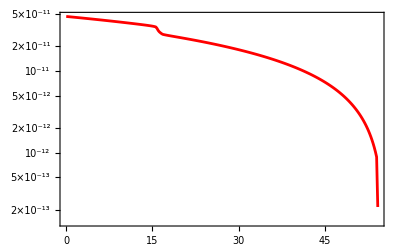

```mathematica
ListLogPlot[PNt(*,PlotRange->{{0,60},{3*10^-13,2*10^-11}}*),Joined->True,Frame->True,PlotStyle->Red]
```

```mathematica
kmpct=Solve[0.002/Mpct==(a[Ne] H[Ne])/.solNe1/.Ne->0,Mpct][[1]][[1,2]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

137.187

```mathematica
Pkt=Table[{(kmpct(H[Ne]a[Ne])/.solNe1/.{Ne->NeHEt[[i]]})[[1]],(j kt[[i]]^3/Pi^2*Abs[(ut[Ne]/.solNe1)/(a[Ne]/.solNe1)]^2/.MSolt[[i]]/.Ne->NeEndt[[i]])[[1]][[1]]},{i,1,iMax}]
```

{{0.002,4.65939×10^-11},{0.00243899,4.64485×10^-11},{0.00297433,4.63032×10^-11},{0.00362715,4.61578×10^-11},{0.00442323,4.60125×10^-11},{0.005394,4.58671×10^-11},{0.0065778,4.57217×10^-11},{0.00802136,4.55763×10^-11},{0.00978167,4.54309×10^-11},{0.0119282,4.52855×10^-11},{0.0145458,4.51401×10^-11},{0.0177376,4.49947×10^-11},{0.0216297,4.48493×10^-11},{0.0263757,4.47038×10^-11},{0.032163,4.45584×10^-11},{0.0392198,4.4413×10^-11},{0.0478246,4.42675×10^-11},{0.0583171,4.4122×10^-11},{0.0711112,4.39766×10^-11},{0.0867117,4.38311×10^-11},{0.105734,4.36856×10^-11},{0.128929,4.35402×10^-11},{0.15721,4.33947×10^-11},{0.191695,4.32492×10^-11},{0.233743,4.31037×10^-11},{0.285012,4.29581×10^-11},{0.347524,4.28126×10^-11},{0.423745,4.26671×10^-11},{0.51668,4.25216×10^-11},{0.629994,4.2376×10^-11},{0.768154,4.22305×10^-11},{0.936607,4.20849×10^-11},{1.14199,4.19393×10^-11},{1.39241,4.17937×10^-11},{1.69773,4.16481×10^-11},{2.06999,4.15025×10^-11},{2.52385,4.13569×10^-11},{3.0772,4.12112×10^-11},{3.75186,4.10656×10^-11},{4.57439,4.09199×10^-11},{5.57722,4.07742×10^-11},{6.79985,4.06285×10^-11},{8.29045,4.04827×10^-11},{10.1077,4.0337×10^-11},{12.3233,4.01912×10^-11},{15.0244,4.00454×10^-11},{18.3174,3.98996×10^-11},{22.332,3.97537×10^-11},{27.2262,3.96078×10^-11},{33.1929,3.94618×10^-11},{40.4668,3.93158×10^-11},{49.3344,3.91698×10^-11},{60.1447,3.90237×10^-11},{73.3232,3.88775×10^-11},{89.3885,3.87312×10^-11},{108.973,3.85847×10^-11},{132.847,3.84381×10^-11},{161.949,3.82913×10^-11},{197.425,3.81443×10^-11},{240.67,3.7997×10^-11},{293.383,3.78495×10^-11},{357.638,3.77015×10^-11},{435.96,3.75531×10^-11},{531.426,3.74042×10^-11},{647.787,3.72548×10^-11},{789.612,3.71045×10^-11},{962.464,3.69531×10^-11},{1173.12,3.68001×10^-11},{1429.84,3.66455×10^-11},{1742.66,3.64886×10^-11},{2123.83,3.63289×10^-11},{2588.21,3.61654×10^-11},{3153.86,3.59968×10^-11},{3842.73,3.58216×10^-11},{4681.39,3.5637×10^-11},{5701.89,3.54386×10^-11},{6942.59,3.52187×10^-11},{8448.46,3.49613×10^-11},{10267.3,3.46156×10^-11},{12276.7,3.32134×10^-11},{14559.,3.13599×10^-11},{17430.6,3.01546×10^-11},{21006.1,2.93445×10^-11},{25419.8,2.862×10^-11},{30838.7,2.81236×10^-11},{37469.9,2.79012×10^-11},{45569.,2.77099×10^-11},{55450.,2.7533×10^-11},{67496.7,2.73642×10^-11},{82178.1,2.72009×10^-11},{100067.,2.70418×10^-11},{121860.,2.68856×10^-11},{148407.,2.67317×10^-11},{180743.,2.65795×10^-11},{220129.,2.64287×10^-11},{268100.,2.62789×10^-11},{326527.,2.613×10^-11},{397687.,2.59818×10^-11},{484352.,2.58341×10^-11},{589898.,2.56868×10^-11},{718437.,2.55397×10^-11},{874972.,2.53928×10^-11},{1.0656×10^6,2.5246×10^-11},{1.29774×10^6,2.50994×10^-11},{1.58044×10^6,2.4953×10^-11},{1.92468×10^6,2.48066×10^-11},{2.34387×10^6,2.46603×10^-11},{2.85431×10^6,2.45141×10^-11},{3.47585×10^6,2.43679×10^-11},{4.23266×10^6,2.42217×10^-11},{5.15416×10^6,2.40755×10^-11},{6.27616×10^6,2.39293×10^-11},{7.64229×10^6,2.37832×10^-11},{9.30559×10^6,2.3637×10^-11},{1.13307×10^7,2.34909×10^-11},{1.37963×10^7,2.33448×10^-11},{1.6798×10^7,2.31987×10^-11},{2.04524×10^7,2.30526×10^-11},{2.49014×10^7,2.29066×10^-11},{3.03175×10^7,2.27605×10^-11},{3.69109×10^7,2.26144×10^-11},{4.49373×10^7,2.24683×10^-11},{5.47079×10^7,2.23222×10^-11},{6.66015×10^7,2.21761×10^-11},{8.10789×10^7,2.203×10^-11},{9.87012×10^7,2.18839×10^-11},{1.20151×10^8,2.17378×10^-11},{1.46259×10^8,2.15917×10^-11},{1.78036×10^8,2.14456×10^-11},{2.16712×10^8,2.12996×10^-11},{2.63784×10^8,2.11535×10^-11},{3.21073×10^8,2.10074×10^-11},{3.90794×10^8,2.08613×10^-11},{4.75644×10^8,2.07152×10^-11},{5.78901×10^8,2.05691×10^-11},{7.04558×10^8,2.0423×10^-11},{8.57467×10^8,2.02769×10^-11},{1.04353×10^9,2.01307×10^-11},{1.26994×10^9,1.99846×10^-11},{1.54544×10^9,1.98384×10^-11},{1.88064×10^9,1.96923×10^-11},{2.28848×10^9,1.95461×10^-11},{2.7847×10^9,1.94001×10^-11},{3.38841×10^9,1.9254×10^-11},{4.12289×10^9,1.91079×10^-11},{5.01643×10^9,1.89619×10^-11},{6.10344×10^9,1.88158×10^-11},{7.42577×10^9,1.86698×10^-11},{9.03431×10^9,1.85238×10^-11},{1.09909×10^10,1.83778×10^-11},{1.33709×10^10,1.82318×10^-11},{1.62657×10^10,1.80858×10^-11},{1.97866×10^10,1.79398×10^-11},{2.40689×10^10,1.77938×10^-11},{2.92769×10^10,1.76479×10^-11},{3.56106×10^10,1.75019×10^-11},{4.3313×10^10,1.7356×10^-11},{5.26796×10^10,1.72101×10^-11},{6.40694×10^10,1.70642×10^-11},{7.79189×10^10,1.69183×10^-11},{9.47586×10^10,1.67724×10^-11},{1.15233×10^11,1.66266×10^-11},{1.40127×10^11,1.64808×10^-11},{1.70391×10^11,1.6335×10^-11},{2.07184×10^11,1.61892×10^-11},{2.51911×10^11,1.60435×10^-11},{3.06281×10^11,1.58978×10^-11},{3.7237×10^11,1.5752×10^-11},{4.52701×10^11,1.56059×10^-11},{5.50336×10^11,1.54598×10^-11},{6.69×10^11,1.53137×10^-11},{8.13212×10^11,1.51676×10^-11},{9.88467×10^11,1.50214×10^-11},{1.20143×10^12,1.48753×10^-11},{1.46021×10^12,1.47292×10^-11},{1.77464×10^12,1.45831×10^-11},{2.15668×10^12,1.4437×10^-11},{2.62081×10^12,1.4291×10^-11},{3.18468×10^12,1.41449×10^-11},{3.86964×10^12,1.39988×10^-11},{4.70168×10^12,1.38527×10^-11},{5.7123×10^12,1.37066×10^-11},{6.93977×10^12,1.35606×10^-11},{8.4305×10^12,1.34145×10^-11},{1.02409×10^13,1.32685×10^-11},{1.24392×10^13,1.31224×10^-11},{1.51086×10^13,1.29764×10^-11},{1.83496×10^13,1.28304×10^-11},{2.22844×10^13,1.26843×10^-11},{2.70612×10^13,1.25383×10^-11},{3.28597×10^13,1.23923×10^-11},{3.9898×10^13,1.22463×10^-11},{4.84404×10^13,1.21004×10^-11},{5.88075×10^13,1.19544×10^-11},{7.13882×10^13,1.18085×10^-11},{8.66535×10^13,1.16625×10^-11},{1.05175×10^14,1.15166×10^-11},{1.27645×10^14,1.13707×10^-11},{1.54903×10^14,1.12248×10^-11},{1.87966×10^14,1.10789×10^-11},{2.28067×10^14,1.0933×10^-11},{2.76698×10^14,1.07871×10^-11},{3.35668×10^14,1.06413×10^-11},{4.07168×10^14,1.04954×10^-11},{4.93851×10^14,1.03496×10^-11},{5.98928×10^14,1.02037×10^-11},{7.26289×10^14,1.00579×10^-11},{8.80641×10^14,9.91204×10^-12},{1.06768×10^15,9.76622×10^-12},{1.2943×10^15,9.62042×10^-12},{1.56885×10^15,9.47464×10^-12},{1.90141×10^15,9.32888×10^-12},{2.30419×10^15,9.18733×10^-12},{2.79194×10^15,9.04155×10^-12},{3.38251×10^15,8.89606×10^-12},{4.09745×10^15,8.75005×10^-12},{4.96283×10^15,8.60436×10^-12},{6.01012×10^15,8.45895×10^-12},{7.27736×10^15,8.31332×10^-12},{8.81048×10^15,8.16773×10^-12},{1.06649×10^16,8.0222×10^-12},{1.29076×10^16,7.87672×10^-12},{1.56193×10^16,7.73131×10^-12},{1.88974×10^16,7.58569×10^-12},{2.28593×10^16,7.44032×10^-12},{2.76465×10^16,7.29518×10^-12},{3.34297×10^16,7.14982×10^-12},{4.04143×10^16,7.00446×10^-12},{4.88479×10^16,6.85894×10^-12},{5.90285×10^16,6.71371×10^-12},{7.13145×10^16,6.56873×10^-12},{8.61372×10^16,6.42362×10^-12},{1.04015×10^17,6.27857×10^-12},{1.2557×10^17,6.1334×10^-12},{1.5155×10^17,5.98862×10^-12},{1.82852×10^17,5.84371×10^-12},{2.20554×10^17,5.69884×10^-12},{2.65944×10^17,5.55405×10^-12},{3.2057×10^17,5.40933×10^-12},{3.86281×10^17,5.26455×10^-12},{4.65289×10^17,5.12014×10^-12},{5.6024×10^17,4.97568×10^-12},{6.74291×10^17,4.83132×10^-12},{8.11206×10^17,4.68705×10^-12},{9.75469×10^17,4.54287×10^-12},{1.17242×10^18,4.39868×10^-12},{1.4084×10^18,4.25483×10^-12},{1.69093×10^18,4.11088×10^-12},{2.02893×10^18,3.96725×10^-12},{2.43294×10^18,3.82364×10^-12},{2.91539×10^18,3.68008×10^-12},{3.49096×10^18,3.53688×10^-12},{4.17685×10^18,3.39377×10^-12},{4.99321×10^18,3.25086×10^-12},{5.96357×10^18,3.10815×10^-12},{7.11529×10^18,2.96567×10^-12},{8.48006×10^18,2.82345×10^-12},{1.00944×10^19,2.68146×10^-12},{1.19999×10^19,2.53991×10^-12},{1.42439×10^19,2.39859×10^-12},{1.68795×10^19,2.25754×10^-12},{1.99655×10^19,2.11695×10^-12},{2.3566×10^19,1.97671×10^-12},{2.77497×10^19,1.83695×10^-12},{3.25876×10^19,1.69776×10^-12},{3.81501×10^19,1.5594×10^-12},{4.45006×10^19,1.42189×10^-12},{5.16847×10^19,1.28532×10^-12},{5.97163×10^19,1.14974×10^-12},{6.85596×10^19,1.01548×10^-12},{7.80987×10^19,8.82874×10^-13},{8.808×10^19,2.15197×10^-13}}

```mathematica
ct=Interpolation[Pkt,InterpolationOrder->1]
AAt=LogLogPlot[{ct[x]},{x,0.002,4*^20}(*,PlotRange->{{0.001,4*10^22},{10^-12,1}}*),Frame->True,FrameStyle->Thick,FrameTicksStyle->Black,PlotStyle->Darker[Blue],LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],ImageSize->{600,400},AspectRatio->Full,RotateLabel->True,Axes->False,FrameLabel->{"k/Mpc^-1","P_t"}]
```

InterpolatingFunction[…]

```mathematica
ct[0.05kmpct]
```

4.06227×10^-11

```mathematica
c1[0.05kmpc]
```

2.00437×10^-9

```mathematica
ct[0.05kmpct]/(c1[0.05kmpc](*2.1*10^-9*))
```

0.020267

```mathematica
LogPlot[(2 H[Ne]^2/.solNe1)/Pi^2,{Ne,0,NeFIN},PlotRange->All,Frame->True,PlotStyle->Darker[Blue]]
```

```mathematica
(((2 H[Ne]^2/.solNe1)/Pi^2)[[1]]/.Ne->0)/(c1[0.05kmpc](*2.1*10^-9*))
```

0.0214875

## Case D

```mathematica
Clear["Global`*"]
Remove["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ϵ1[Ne_]:=-H'[Ne]/H[Ne]

ϵ2[Ne_]:=-(H[Ne] (H'[Ne]^2/H[Ne]^2-H''[Ne]/H[Ne]))/H'[Ne](*ϵ1[Ne]-1/(2ϵ1[Ne])ϵ1'[Ne]*)
```

```mathematica
V[ϕ_]:=Λ^4(1+Cos[ϕ/f])
ϵ[ϕ_]:=w(Cosh[(ϕ-ϕc)/b])^-2
M[ϕ_]:=M0(1+ϵ[ϕ])
```

#### Solving Background Equations (6)&(9)

```mathematica
Off[NDSolve::precw];
ϕ0=5.53327945289528760424702860706861791151`29.518687405708878;
dϕ0=0.0052583177533965574057692244440840616889231016307249570077`26.83391284890734;
w=1.31*10^1;
b=1.2*10^-2;
ϕc=5.709;
Λ=1.``15*10^-2;
α=20.;
M0=2.32``15*10^-4;
f=2.``15;
cs=1/(√(2α-1));

solNe1=NDSolve[{H[Ne]H'[Ne]==-α H[Ne]^2 ϕ'[Ne]^2/2(H[Ne]^2 ϕ'[Ne]^2/(2 M[ϕ[Ne]]^4))^(α-1),ϕ''[Ne]==-(3/(2α-1)-ϵ1[Ne])ϕ'[Ne]-(V'[ϕ[Ne]]/V[ϕ[Ne]])((3α-(2α-1)ϵ1[Ne])/(α(2α-1)))ϕ'[Ne]^2/(2ϵ1[Ne])+(2(α-1))/α M'[ϕ[Ne]]/M[ϕ[Ne]] ϕ'[Ne]^2,ϕ[-6]==ϕ0,H[-6]==√(V[ϕ[-6]]/3),ϕ'[-6]==dϕ0},{ϕ,H},{Ne,-6``15,65``15},Method->{"EquationSimplification"->"Residual"},AccuracyGoal->6.2356,PrecisionGoal->30.]
NeFIN=FindRoot[(ϵ1[Ne]/.solNe1)==1,{Ne,52}]
NeFIN=NeFIN[[1,2]];
phi=Plot[ϕ[Ne]/.solNe1,{Ne,0,NeFIN},PlotRange->{{-1,58},{5.4,6.3}},Frame->True,FrameLabel->{"N","ϕ/M_P"},PlotStyle->Purple,LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],ImageSize->{600,400},RotateLabel->False,FrameStyle->Thick,FrameTicksStyle->Black(*PlotLegends->{Placed[LineLegend[{{Red},{Darker[Green]},Darker[Blue]},{"Case A","Case B ","Case C"},LabelStyle->{14,FontFamily->"Cambria"},LegendLayout->"Column",LegendMarkerSize->{{30,20}}],{0.12,0.2}]}*)]
LogPlot[{ϵ1[Ne]/.solNe1,1},{Ne,0,NeFIN},PlotRange->{{0,57.},{-1,1.1}},Frame->True,FrameLabel->{"N","ε_1"},PlotStyle->{Purple,Orange},ImageSize->{600,400},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameStyle->Thick,FrameTicksStyle->Black,ImageSize->{600,400},RotateLabel->False(*,PlotLegends->{Placed[LineLegend[{{Red},{Darker[Green]},Darker[Blue]},{"Case A","Case B ","Case C"},LabelStyle->{14,FontFamily->"Cambria"},LegendLayout->"Column",LegendMarkerSize->{{30,20}}],{0.12,0.2}]}*)]
Plot[V[ϕ]/Λ^4,{ϕ,0,0.013},PlotRange->All,Frame->True,FrameLabel->{"ϕ","V[ϕ]/Λ^4"},
LabelStyle->Directive[15,Bold,Black,FontFamily->"Book Antiqua"],PlotStyle->Red]
Plot[ϵ[ϕ],{ϕ,4,6.5},PlotRange->All,Frame->True,PlotStyle->Red]
Plot[M[ϕ],{ϕ,4,6.5},PlotRange->All,Frame->True,PlotStyle->Red]
NeIN=0;
```

Power::infy: Infinite expression 1/0. encountered.

NDSolve::nlnum: The function value {4.27937×10^-13,0.,ComplexInfinity} is not a list of numbers with dimensions {3} at {Ne,H[Ne],ϕ[Ne],ϕ'[Ne],H'[Ne],ϕ'[Ne],ϕ''[Ne]} = {-6.,0.0000152179,5.53328,0.00525832,0.,0.00525832,0.}.

NDSolve::ndsz: At Ne == 56.1278, step size is effectively zero; singularity or stiff system suspected.

{{ϕ→InterpolatingFunction[…],H→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {77.511} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {61.3425} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{Ne→55.5728}

```mathematica
r[Ne_]:=First[Evaluate[16cs ϵ1[Ne]/.solNe1]]
ns[Ne_]:=First[Evaluate[1-2ϵ1[Ne]-ϵ2[Ne]/.solNe1]]
r[0]
ns[0]
```

0.0199766

0.968424

```mathematica
PN=ParametricPlot[{{ns[Ne],r[Ne]}},{Ne,-.05,0},PlotRange->{{0.945,1},{0,.261}},Frame-> True,FrameLabel->{"n_s","r"},ImageSize->{400,300},AspectRatio->Full,PlotStyle->{{Purple,Thickness[0.01]}}]
rns0=-Graphics-;
prns0=Show[{ParametricPlot[{ns0[Ne],r0[Ne]},{Ne,50,60},PlotRange->{{0.945,1},{0,0.261}},PlotStyle->{Black,Thickness[0.005]},Frame-> True,FrameLabel->{"n_s","r"},ImageSize->{700,400},AspectRatio->Full,PlotLegends->{Placed[SwatchLegend[{Gray,Red,Blue},{"TT,TE,EE+lowE+lensing ","TT,TE,EE+lowE+lensing +BK14 ","TT,TE,EE+lowE+lensing +BK14+BAO "},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}}],{1,0.92}](*,Placed[LineLegend[{Yellow},{"ϕ^2"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.83}],Placed[LineLegend[{Directive[Dashed,Yellow],Yellow},{"α-attractor N_*=50","α-attractor N_*=60"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.60}],Placed[LineLegend[{Directive[Dashed,Blue],Blue},{"α-attractor(G-I)   M=10^6","α-attractor(G-I)   M=10^6"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.45}],Placed[LineLegend[{Directive[Dashed,Black],Black},{"α-attractor(G-I)   M=10^-3","α-attractor(G-I)   M=10^-3"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.25}],Placed[PointLegend[{Directive[Black,AbsolutePointSize[6]],Directive[Black,AbsolutePointSize[8]]},{"N_*=50","N_*=60"},LabelStyle->10,LegendLayout->"Column"],{1.025,0.12}]*)}],Graphics[{Texture[rns0],EdgeForm[Black],Polygon[{{0.945,0},{1,0},{1,0.261},{0.945,0.261}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},ImageSize->{400,300},AspectRatio->Full]}]
Show[prns0,PN]
```

```mathematica
PN=ParametricPlot[{{ns[Ne],r[Ne]}},{Ne,-.1,0},PlotRange->{{0.93,1},{0,.1}},Frame-> True,FrameLabel->{"n_s","r"},ImageSize->{400,300},AspectRatio->Full,PlotStyle->{{Purple,Thickness[0.01]}}]
rns0=-Graphics-;
prns0=Show[{ParametricPlot[{ns0[Ne],r0[Ne]},{Ne,50,60},PlotRange->{{0.93,1},{0,0.20}},PlotStyle->{Black,Thickness[0.005]},Frame-> True,FrameLabel->{"n_s","r"},ImageSize->{700,400},AspectRatio->Full,PlotLegends->{Placed[SwatchLegend[{Gray,Red,Blue},{"TT,TE,EE+lowE+lensing ","TT,TE,EE+lowE+lensing +BK14 ","TT,TE,EE+lowE+lensing +BK14+BAO "},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}}],{1,0.92}],Placed[LineLegend[{Yellow},{"ϕ^2"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.83}],Placed[LineLegend[{Directive[Dashed,Yellow],Yellow},{"α-attractor N_*=50","α-attractor N_*=60"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.60}],Placed[LineLegend[{Directive[Dashed,Blue],Blue},{"α-attractor(G-I)   M=10^6","α-attractor(G-I)   M=10^6"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.45}],Placed[LineLegend[{Directive[Dashed,Black],Black},{"α-attractor(G-I)   M=10^-3","α-attractor(G-I)   M=10^-3"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.25}],Placed[PointLegend[{Directive[Black,AbsolutePointSize[6]],Directive[Black,AbsolutePointSize[8]]},{"N_*=50","N_*=60"},LabelStyle->10,LegendLayout->"Column"],{1.025,0.12}]}],Graphics[{Texture[rns0],EdgeForm[Black],Polygon[{{0.93,0},{1,0},{1,0.2},{0.93,0.2}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},ImageSize->{400,300},AspectRatio->Full]}]
Show[prns0,PN]
```

```mathematica
Plot[{(Abs[ϕ[Ne]-ϕ[NeFIN]])/.solNe1},{Ne,-6,NeFIN},PlotRange->{{0,57},{0,.8}},FrameLabel->{"N","Δϕ/M_P"},Frame->True,Frame->True,PlotStyle->Purple,ImageSize->{600,400},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameStyle->Thick,FrameTicksStyle->Black,ImageSize->{600,400},RotateLabel->False(*,PlotLegends->{Placed[LineLegend[{{Red},{Darker[Green]},Blue},{"Case A","Case B ","Case C"},LabelStyle->{14,FontFamily->"Cambria"},LegendLayout->"Column",LegendMarkerSize->{{30,20}}],{0.12,0.2}]}*)]
Plot[{Abs[V'[ϕ[Ne]]/V[ϕ[Ne]]]/.solNe1,1},{Ne,0,NeFIN},PlotRange->{{0,57},{0,18}},FrameLabel->{"N","M_pV_(,ϕ)/V"},Frame->True,Frame->True,PlotStyle->{Purple,Orange},ImageSize->{600,400},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameStyle->Thick,FrameTicksStyle->Black,ImageSize->{600,400},RotateLabel->False(*,PlotLegends->{Placed[LineLegend[{{Red},{Darker[Green]},Blue},{"Case A","Case B ","Case C"},LabelStyle->{14,FontFamily->"Cambria"},LegendLayout->"Column",LegendMarkerSize->{{30,20}}],{0.12,0.5}]}*)]
Plot[{ϵ2[Ne]/.solNe1,1},{Ne,-6,NeFIN},PlotRange->{{0,57},{-3,7}},FrameLabel->{"N","ε_2"},Frame->True,PlotStyle->{Purple,Orange},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameStyle->Thick,FrameTicksStyle->Black,ImageSize->{600,400},RotateLabel->False(*,PlotLegends->{Placed[LineLegend[{{Red},{Darker[Green]},Blue},{"Case A","Case B ","Case C"},LabelStyle->{14,FontFamily->"Cambria"},LegendLayout->"Column",LegendMarkerSize->{{30,20}}],{0.12,0.5}]}*)]
Plot[ϕ''[Ne]/.solNe1,{Ne,-6,NeFIN},PlotRange->All,FrameLabel->{"Ne","ϕ''[Ne]"},Frame->True]
Plot[ϕ'[Ne]/.solNe1,{Ne,0,NeFIN},FrameLabel->{"N","ϕ_(,N)/M_P"},Frame->True,PlotStyle->Purple,ImageSize->{600,400},PlotRange->{{0,57},{0.001,.1}},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameStyle->Thick,FrameTicksStyle->Black,ImageSize->{600,400},RotateLabel->False(*,PlotLegends->{Placed[LineLegend[{{Red},{Darker[Green]},Blue},{"Case A","Case B ","Case C"},LabelStyle->{14,FontFamily->"Cambria"},LegendLayout->"Column",LegendMarkerSize->{{30,20}}],{0.12,0.2}]}*)]
LogPlot[H[Ne]/.solNe1,{Ne,0,NeFIN},PlotRange->{{0,58},{9*10^-7,2*10^-5}},FrameLabel->{"Ne","H/M_P"},Frame->True,PlotStyle->Purple,ImageSize->{600,400},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameStyle->Thick,FrameTicksStyle->Black,ImageSize->{600,400},RotateLabel->False]
Plot[H'[Ne]/.solNe1,{Ne,-5,NeFIN},PlotRange->All,FrameLabel->{"Ne","H'[Ne]"},Frame->True]
```

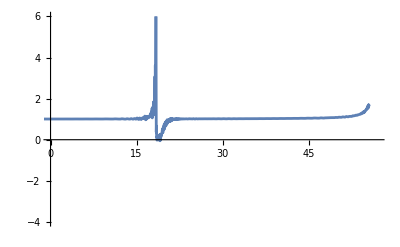

{0.779889}

```mathematica
cs=√(1/(2α-1));
a[Ne_]:=Exp[Ne];
z[Ne_]:=(a[Ne]ϕ'[Ne])/cs √(α ((H[Ne]^2 ϕ'[Ne]^2)/(2 M[ϕ[Ne]]^4))^(α-1))
Plot[z'[Ne]/z[Ne]/.solNe1,{Ne,-5,NeFIN},PlotRange->{{0,57},{-4,6}}]
z[Ne]/.solNe1/.Ne->0
```

#### Solving Scalar Mukhanov Sasaki Equation (10)

```mathematica
nPoints=5;
iMax=(NeFIN-.3)*nPoints;
NeHE=Table[0+i/nPoints,{i,1,iMax}]//N;
NeBD=Table[NeHE[[i]]-5,{i,1,iMax}]//N;
NeEnd=Table[(*NeFIN*)(*If[NeHE[[i]]≤31,NeHE[[i]]+3,NeFIN-.7]*)If[NeHE[[i]]+1≤NeFIN,NeHE[[i]]+1,NeFIN],{i,1,iMax}];
k=Table[((H[Ne]*a[Ne])/cs)/.solNe1/.{Ne->NeHE[[i]]},{i,1,iMax}]//N;
For[i=1,i≤iMax-(iMax-1),i++,
tAux=AbsoluteTime[];
MSsolAux[i]=NDSolve[{((u''[Ne]+(H'[Ne]/H[Ne]+a'[Ne]/a[Ne])u'[Ne]+((cs k[[i]])/(a[Ne] H[Ne]))^2 u[Ne]-z''[Ne]/z[Ne] u[Ne]-z'[Ne]/z[Ne](H'[Ne]/H[Ne]+a'[Ne]/a[Ne])u[Ne])/.solNe1)==0,u[NeBD[[i]]]==1/(√(2k[[i]] cs))/.solNe1/.{Ne->NeBD[[i]]},u'[NeBD[[i]]]==((-2I k[[i]] cs^2)/(a[Ne] H[Ne]2 √2 √k[[i]] cs^(3/2)))/.solNe1/.{Ne->NeBD[[i]]}},{u[Ne]},{Ne,NeBD[[i]],NeEnd[[i]]},MaxSteps->Infinity(*Method->{"EquationSimplification"->"Solve"}*)(*,WorkingPrecision->30*)][[1]];Print[NeHE[[i]]//N,"  ",k[[i]]//N,"  ",AbsoluteTime[]-tAux]]
MSol=Table[MSsolAux[i],{i,1,iMax}];
PN0=Table[{NeHE[[i]],((k[[i]]^3/(2*Pi^2)*Abs[(u[Ne]/.solNe1)/(z[Ne]/.solNe1)]^2)/.MSol[[i]]/.Ne->NeEnd[[i]])[[1]][[1]]},{i,1,iMax-(iMax-1)}]
```

0.2  {0.000111027}  0.3611215

{{0.2,2.4522×10^-9}}

```mathematica
Off[NDSolve::precw];
For[i=1,i≤iMax,i++,
tAux=AbsoluteTime[];
MSsolAux[i]=NDSolve[{((u''[Ne]+(H'[Ne]/H[Ne]+a'[Ne]/a[Ne])u'[Ne]+((cs k[[i]])/(a[Ne] H[Ne]))^2 u[Ne]-z''[Ne]/z[Ne] u[Ne]-z'[Ne]/z[Ne](H'[Ne]/H[Ne]+a'[Ne]/a[Ne])u[Ne])/.solNe1)==0,u[NeBD[[i]]]==1/(√(2k[[i]] cs))/.solNe1/.{Ne->NeBD[[i]]},u'[NeBD[[i]]]==((-2I k[[i]] cs^2)/(a[Ne] H[Ne]2 √2 √k[[i]] cs^(3/2)))/.solNe1/.{Ne->NeBD[[i]]}},{u[Ne]},{Ne,NeBD[[i]],NeEnd[[i]]},MaxSteps->Infinity,(*,Method->{"StiffnessSwitching",Method->{"ExplicitRungeKutta",Automatic}}*)Method->{"ExplicitRungeKutta","StiffnessTest"->False}(*,Method->{"EquationSimplification"->"Solve"},*),AccuracyGoal->14,PrecisionGoal->4(*,WorkingPrecision->2*)][[1]];Print[NeHE[[i]]//N,"  ",k[[i]]//N,"  ",AbsoluteTime[]-tAux]]
MSol=Table[MSsolAux[i],{i,1,iMax}];
```

0.2  {0.000111027}  0.177751

0.4  {0.000135397}  0.183925

0.6  {0.000165114}  0.188898

0.8  {0.000201353}  0.189549

1.  {0.000245545}  0.20317

1.2  {0.000299433}  0.219549

1.4  {0.000365147}  0.189253

1.6  {0.000445279}  0.188762

1.8  {0.000542994}  0.203707

2.  {0.000662149}  0.188254

2.2  {0.000807448}  0.188779

2.4  {0.000984624}  0.204749

2.6  {0.00120067}  0.188922

2.8  {0.00146412}  0.188268

3.  {0.00178535}  0.188653

3.2  {0.00217706}  0.298933

3.4  {0.0026547}  0.297694

3.6  {0.00323711}  0.266686

3.8  {0.00394727}  0.298572

4.  {0.0048132}  0.282453

4.2  {0.00586906}  0.329836

4.4  {0.0071565}  0.298822

4.6  {0.00872631}  0.251297

4.8  {0.0106404}  0.314072

5.  {0.0129743}  0.344883

5.2  {0.0158199}  0.23578

5.4  {0.0192896}  0.282625

5.6  {0.0235202}  0.282341

5.8  {0.0286785}  0.344411

6.  {0.0349678}  0.329112

6.2  {0.0426361}  0.34589

6.4  {0.0519857}  0.299157

6.6  {0.0633852}  0.251084

6.8  {0.077284}  0.266392

7.  {0.0942297}  0.283248

7.2  {0.11489}  0.284979

7.4  {0.14008}  0.300317

7.6  {0.170792}  0.24827

7.8  {0.208236}  0.330087

8.  {0.253887}  0.329882

8.2  {0.309544}  0.294707

8.4  {0.3774}  0.286693

8.6  {0.460128}  0.267151

8.8  {0.560986}  0.298249

9.  {0.683947}  0.251812

9.2  {0.833855}  0.282682

9.4  {1.01661}  0.331215

9.6  {1.23942}  0.266871

9.8  {1.51104}  0.282875

10.  {1.84218}  0.345637

10.2  {2.24587}  0.235185

10.4  {2.738}  0.298587

10.6  {3.33796}  0.329837

10.8  {4.06934}  0.332602

11.  {4.96094}  0.312882

11.2  {6.04785}  0.3760535

11.4  {7.37284}  0.376986

11.6  {8.98805}  0.298208

11.8  {10.957}  0.314874

12.  {13.3572}  0.300162

12.2  {16.2831}  0.3610552

12.4  {19.8497}  0.3773121

12.6  {24.1973}  0.298319

12.8  {29.4969}  0.266439

13.  {35.957}  0.3143

13.2  {43.8314}  0.315097

13.4  {53.4299}  0.297012

13.6  {65.1298}  0.300679

13.8  {79.3908}  0.297883

14.  {96.7737}  0.314103

14.2  {117.961}  0.345736

14.4  {143.786}  0.346707

14.6  {175.262}  0.3765534

14.8  {213.627}  0.345927

15.  {260.386}  0.3927552

15.2  {317.374}  0.3606298

15.4  {386.828}  0.3918777

15.6  {471.471}  0.4249871

15.8  {574.624}  0.4549667

16.  {700.33}  0.4563751

16.2  {853.51}  0.4855035

16.4  {1040.15}  0.4398353

16.6  {1267.54}  0.534864

16.8  {1544.56}  0.596677

17.  {1881.98}  0.738182

17.2  {2292.91}  1.010721

17.4  {2793.18}  3.029114

17.6  {3401.96}  4.19753

17.8  {4142.26}  4.1359164

18.  {5041.31}  4.1622302

18.2  {6129.68}  4.5755188

18.4  {7409.79}  4.8475468

18.6  {8761.14}  4.9080279

18.8  {10456.3}  4.7090173

19.  {12573.9}  4.6073683

19.2  {15194.5}  4.7101738

19.4  {18416.7}  4.5869632

19.6  {22363.}  4.8224475

19.8  {27185.1}  4.9830168

20.  {33068.9}  4.6520518

20.2  {40242.7}  4.9634068

20.4  {48985.5}  5.3427788

20.6  {59636.7}  4.7003461

20.8  {72611.}  5.2034953

21.  {88413.3}  4.4819124

21.2  {107659.}  4.5908824

21.4  {131096.}  4.2741441

21.6  {159638.}  4.3078054

21.8  {194394.}  4.2418318

22.  {236718.}  4.3152458

22.2  {288255.}  3.8904346

22.4  {351009.}  3.9281136

22.6  {427419.}  3.9295788

22.8  {520456.}  3.455321

23.  {633734.}  3.315071

23.2  {771655.}  2.828549

23.4  {939577.}  1.053243

23.6  {1.14402×10^6}  0.5180174

23.8  {1.39292×10^6}  0.518984

24.  {1.69594×10^6}  0.4655473

24.2  {2.06484×10^6}  0.4007058

24.4  {2.51394×10^6}  0.40469

24.6  {3.06064×10^6}  0.4098948

24.8  {3.72617×10^6}  0.4082853

25.  {4.53631×10^6}  0.3935708

25.2  {5.52249×10^6}  0.4083828

25.4  {6.72292×10^6}  0.4550592

25.6  {8.18411×10^6}  0.3772044

25.8  {9.96266×10^6}  0.267517

26.  {1.21274×10^7}  0.283155

26.2  {1.47623×10^7}  0.3616823

26.4  {1.79691×10^7}  0.3770925

26.6  {2.1872×10^7}  0.266431

26.8  {2.66221×10^7}  0.329643

27.  {3.2403×10^7}  0.266832

27.2  {3.94381×10^7}  0.284364

27.4  {4.79994×10^7}  0.300209

27.6  {5.84177×10^7}  0.313578

27.8  {7.10956×10^7}  0.33085

28.  {8.65226×10^7}  0.314332

28.2  {1.05294×10^8}  0.314635

28.4  {1.28135×10^8}  0.312985

28.6  {1.55927×10^8}  0.316194

28.8  {1.8974×10^8}  0.32999

29.  {2.30881×10^8}  0.314161

29.2  {2.80933×10^8}  0.346306

29.4  {3.41827×10^8}  0.298849

29.6  {4.15907×10^8}  0.298435

29.8  {5.06026×10^8}  0.313652

30.  {6.15655×10^8}  0.270212

30.2  {7.49011×10^8}  0.281413

30.4  {9.11225×10^8}  0.299113

30.6  {1.10854×10^9}  0.282882

30.8  {1.34853×10^9}  0.3773338

31.  {1.64042×10^9}  0.31504

31.2  {1.99543×10^9}  0.298537

31.4  {2.42718×10^9}  0.281767

31.6  {2.95225×10^9}  0.345569

31.8  {3.59079×10^9}  0.332493

32.  {4.36727×10^9}  0.299469

32.2  {5.31148×10^9}  0.3767329

32.4  {6.45959×10^9}  0.3625603

32.6  {7.85557×10^9}  0.282714

32.8  {9.55288×10^9}  0.345934

33.  {1.16165×10^10}  0.298483

33.2  {1.41253×10^10}  0.3614081

33.4  {1.71752×10^10}  0.330449

33.6  {2.08828×10^10}  0.299842

33.8  {2.53898×10^10}  0.282742

34.  {3.08681×10^10}  0.258797

34.2  {3.75269×10^10}  0.277781

34.4  {4.56201×10^10}  0.34811

34.6  {5.54563×10^10}  0.330361

34.8  {6.74101×10^10}  0.346685

35.  {8.19368×10^10}  0.281597

35.2  {9.95893×10^10}  0.282511

35.4  {1.21039×10^11}  0.267847

35.6  {1.47101×10^11}  0.314813

35.8  {1.78766×10^11}  0.298313

36.  {2.17237×10^11}  0.267871

36.2  {2.63972×10^11}  0.29908

36.4  {3.20744×10^11}  0.292855

36.6  {3.89706×10^11}  0.305561

36.8  {4.73468×10^11}  0.314662

37.  {5.752×10^11}  0.313935

37.2  {6.98752×10^11}  0.31412

37.4  {8.48791×10^11}  0.314325

37.6  {1.03099×10^12}  0.251806

37.8  {1.25221×10^12}  0.347003

38.  {1.52081×10^12}  0.251777

38.2  {1.84691×10^12}  0.314848

38.4  {2.24277×10^12}  0.345777

38.6  {2.72331×10^12}  0.252796

38.8  {3.30657×10^12}  0.314569

39.  {4.01447×10^12}  0.28352

39.2  {4.87357×10^12}  0.283524

39.4  {5.91607×10^12}  0.314066

39.6  {7.18104×10^12}  0.299426

39.8  {8.71579×10^12}  0.298608

40.  {1.05777×10^13}  0.346457

40.2  {1.28363×10^13}  0.243195

40.4  {1.55759×10^13}  0.300679

40.6  {1.88985×10^13}  0.320373

40.8  {2.29279×10^13}  0.330628

41.  {2.78139×10^13}  0.282403

41.2  {3.37379×10^13}  0.267614

41.4  {4.09198×10^13}  0.331639

41.6  {4.96255×10^13}  0.282666

41.8  {6.01772×10^13}  0.3613617

42.  {7.2965×10^13}  0.314715

42.2  {8.84605×10^13}  0.299567

42.4  {1.07235×10^14}  0.284233

42.6  {1.29979×10^14}  0.250971

42.8  {1.57529×10^14}  0.282644

43.  {1.90894×10^14}  0.267149

43.2  {2.31298×10^14}  0.298213

43.4  {2.80216×10^14}  0.266898

43.6  {3.39436×10^14}  0.267067

43.8  {4.11113×10^14}  0.235254

44.  {4.97856×10^14}  0.266843

44.2  {6.02812×10^14}  0.269415

44.4  {7.29783×10^14}  0.300509

44.6  {8.83358×10^14}  0.278023

44.8  {1.06908×10^15}  0.283282

45.  {1.29362×10^15}  0.28282

45.2  {1.56506×10^15}  0.267008

45.4  {1.8931×10^15}  0.298344

45.6  {2.28948×10^15}  0.314247

45.8  {2.7683×10^15}  0.250957

46.  {3.34659×10^15}  0.314178

46.2  {4.04481×10^15}  0.330531

46.4  {4.88761×10^15}  0.265922

46.6  {5.90466×10^15}  0.3931126

46.8  {7.13162×10^15}  0.266819

47.  {8.61136×10^15}  0.282826

47.2  {1.03954×10^16}  0.299041

47.4  {1.25455×10^16}  0.235157

47.6  {1.5136×10^16}  0.267696

47.8  {1.82557×10^16}  0.31575

48.  {2.20113×10^16}  0.298517

48.2  {2.65308×10^16}  0.314069

48.4  {3.1967×10^16}  0.235381

48.6  {3.85028×10^16}  0.3301

48.8  {4.63569×10^16}  0.34573

49.  {5.57896×10^16}  0.3930576

49.2  {6.71115×10^16}  0.235607

49.4  {8.06929×10^16}  0.235923

49.6  {9.69739×10^16}  0.251347

49.8  {1.16479×10^17}  0.267692

50.  {1.39831×10^17}  0.345308

50.2  {1.67767×10^17}  0.314704

50.4  {2.01155×10^17}  0.314402

50.6  {2.41018×10^17}  0.235896

50.8  {2.88565×10^17}  0.2828

51.  {3.45217×10^17}  0.273485

51.2  {4.12631×10^17}  0.3558957

51.4  {4.92736×10^17}  0.28365

51.6  {5.87779×10^17}  0.3929149

51.8  {7.00367×10^17}  0.3775968

52.  {8.33489×10^17}  0.5188232

52.2  {9.90552×10^17}  0.346163

52.4  {1.1754×10^18}  0.344758

52.6  {1.3924×10^18}  0.298398

52.8  {1.64636×10^18}  0.345084

53.  {1.94251×10^18}  0.3930664

53.2  {2.28639×10^18}  0.329858

53.4  {2.68367×10^18}  0.329732

53.6  {3.13978×10^18}  0.329914

53.8  {3.65958×10^18}  0.34547

54.  {4.24654×10^18}  0.4406889

54.2  {4.90143×10^18}  0.4235562

54.4  {5.62035×10^18}  0.4564404

54.6  {6.39196×10^18}  0.5648999

54.8  {7.19347×10^18}  0.5374023

55.  {7.98479×10^18}  0.5151455

55.2  {8.69775×10^18}  0.4395349

```mathematica
PN0=Table[{NeHE[[i]],((k[[i]]^3/(2*Pi^2)*Abs[(u[Ne]/.solNe1)/(z[Ne]/.solNe1)]^2)/.MSol[[i]]/.Ne->NeEnd[[i]])[[1]][[1]]},{i,1,iMax}]
```

{{0.2,2.45213×10^-9},{0.4,2.43915×10^-9},{0.6,2.42359×10^-9},{0.8,2.40686×10^-9},{1.,2.39182×10^-9},{1.2,2.37682×10^-9},{1.4,2.36187×10^-9},{1.6,2.34608×10^-9},{1.8,2.3307×10^-9},{2.,2.31505×10^-9},{2.2,2.30061×10^-9},{2.4,2.28648×10^-9},{2.6,2.27174×10^-9},{2.8,2.25735×10^-9},{3.,2.24255×10^-9},{3.2,2.22751×10^-9},{3.4,2.21181×10^-9},{3.6,2.19626×10^-9},{3.8,2.18152×10^-9},{4.,2.16788×10^-9},{4.2,2.15472×10^-9},{4.4,2.14104×10^-9},{4.6,2.12728×10^-9},{4.8,2.1125×10^-9},{5.,2.09701×10^-9},{5.2,2.08131×10^-9},{5.4,2.06635×10^-9},{5.6,2.05264×10^-9},{5.8,2.03989×10^-9},{6.,2.02703×10^-9},{6.2,2.01406×10^-9},{6.4,2.00041×10^-9},{6.6,1.98568×10^-9},{6.8,1.97026×10^-9},{7.,1.95479×10^-9},{7.2,1.94066×10^-9},{7.4,1.92802×10^-9},{7.6,1.91583×10^-9},{7.8,1.90348×10^-9},{8.,1.89093×10^-9},{8.2,1.8772×10^-9},{8.4,1.86243×10^-9},{8.6,1.84692×10^-9},{8.8,1.83182×10^-9},{9.,1.81833×10^-9},{9.2,1.80692×10^-9},{9.4,1.79553×10^-9},{9.6,1.78415×10^-9},{9.8,1.77209×10^-9},{10.,1.75823×10^-9},{10.2,1.7421×10^-9},{10.4,1.72594×10^-9},{10.6,1.71046×10^-9},{10.8,1.69706×10^-9},{11.,1.68806×10^-9},{11.2,1.67764×10^-9},{11.4,1.66743×10^-9},{11.6,1.65517×10^-9},{11.8,1.64173×10^-9},{12.,1.62401×10^-9},{12.2,1.60672×10^-9},{12.4,1.59409×10^-9},{12.6,1.58723×10^-9},{12.8,1.5807×10^-9},{13.,1.56785×10^-9},{13.2,1.54824×10^-9},{13.4,1.52672×10^-9},{13.6,1.51603×10^-9},{13.8,1.51693×10^-9},{14.,1.51188×10^-9},{14.2,1.4887×10^-9},{14.4,1.46761×10^-9},{14.6,1.4585×10^-9},{14.8,1.45827×10^-9},{15.,1.44052×10^-9},{15.2,1.41728×10^-9},{15.4,1.41514×10^-9},{15.6,1.40427×10^-9},{15.8,1.37035×10^-9},{16.,1.36324×10^-9},{16.2,1.36173×10^-9},{16.4,1.3494×10^-9},{16.6,1.38146×10^-9},{16.8,1.36362×10^-9},{17.,1.40089×10^-9},{17.2,1.63401×10^-9},{17.4,2.21243×10^-7},{17.6,0.000380668},{17.8,0.00184405},{18.,0.00421675},{18.2,0.0068144},{18.4,0.00935131},{18.6,0.0121948},{18.8,0.0133233},{19.,0.0135292},{19.2,0.0112069},{19.4,0.00783043},{19.6,0.003425},{19.8,0.000335601},{20.,0.000408448},{20.2,0.00130154},{20.4,0.000313758},{20.6,0.000173999},{20.8,0.0000607134},{21.,0.0000910302},{21.2,0.0000360797},{21.4,0.0000174934},{21.6,2.94182×10^-6},{21.8,2.64781×10^-6},{22.,8.93325×10^-7},{22.2,1.76069×10^-7},{22.4,7.48721×10^-8},{22.6,2.32573×10^-8},{22.8,5.3516×10^-9},{23.,3.43246×10^-10},{23.2,8.70891×10^-10},{23.4,5.51599×10^-10},{23.6,6.01527×10^-10},{23.8,6.05819×10^-10},{24.,6.2672×10^-10},{24.2,5.93913×10^-10},{24.4,5.92091×10^-10},{24.6,5.81542×10^-10},{24.8,5.79513×10^-10},{25.,5.7112×10^-10},{25.2,5.59076×10^-10},{25.4,5.5021×10^-10},{25.6,5.43521×10^-10},{25.8,5.40828×10^-10},{26.,5.3069×10^-10},{26.2,5.2461×10^-10},{26.4,5.18237×10^-10},{26.6,5.10652×10^-10},{26.8,5.02333×10^-10},{27.,4.9945×10^-10},{27.2,4.88094×10^-10},{27.4,4.84577×10^-10},{27.6,4.76232×10^-10},{27.8,4.68902×10^-10},{28.,4.62936×10^-10},{28.2,4.56149×10^-10},{28.4,4.49248×10^-10},{28.6,4.43025×10^-10},{28.8,4.36391×10^-10},{29.,4.30169×10^-10},{29.2,4.23437×10^-10},{29.4,4.16891×10^-10},{29.6,4.10903×10^-10},{29.8,4.05217×10^-10},{30.,3.98901×10^-10},{30.2,3.9175×10^-10},{30.4,3.85586×10^-10},{30.6,3.80301×10^-10},{30.8,3.75105×10^-10},{31.,3.67931×10^-10},{31.2,3.61139×10^-10},{31.4,3.55778×10^-10},{31.6,3.51638×10^-10},{31.8,3.45262×10^-10},{32.,3.38092×10^-10},{32.2,3.32511×10^-10},{32.4,3.28003×10^-10},{32.6,3.23247×10^-10},{32.8,3.16892×10^-10},{33.,3.10519×10^-10},{33.2,3.05606×10^-10},{33.4,3.01212×10^-10},{33.6,2.9553×10^-10},{33.8,2.89627×10^-10},{34.,2.84238×10^-10},{34.2,2.7954×10^-10},{34.4,2.74645×10^-10},{34.6,2.69488×10^-10},{34.8,2.64328×10^-10},{35.,2.59048×10^-10},{35.2,2.5408×10^-10},{35.4,2.49411×10^-10},{35.6,2.44748×10^-10},{35.8,2.39921×10^-10},{36.,2.35041×10^-10},{36.2,2.30122×10^-10},{36.4,2.25424×10^-10},{36.6,2.21019×10^-10},{36.8,2.16619×10^-10},{37.,2.12088×10^-10},{37.2,2.0748×10^-10},{37.4,2.02865×10^-10},{37.6,1.98464×10^-10},{37.8,1.94375×10^-10},{38.,1.90264×10^-10},{38.2,1.86013×10^-10},{38.4,1.81658×10^-10},{38.6,1.77307×10^-10},{38.8,1.73211×10^-10},{39.,1.69459×10^-10},{39.2,1.65632×10^-10},{39.4,1.61641×10^-10},{39.6,1.57566×10^-10},{39.8,1.53506×10^-10},{40.,1.49732×10^-10},{40.2,1.46224×10^-10},{40.4,1.4275×10^-10},{40.6,1.39042×10^-10},{40.8,1.35268×10^-10},{41.,1.31512×10^-10},{41.2,1.27987×10^-10},{41.4,1.24765×10^-10},{41.6,1.21473×10^-10},{41.8,1.18076×10^-10},{42.,1.14635×10^-10},{42.2,1.11226×10^-10},{42.4,1.0803×10^-10},{42.6,1.04975×10^-10},{42.8,1.01938×10^-10},{43.,9.885×10^-11},{43.2,9.57378×10^-11},{43.4,9.26167×10^-11},{43.6,8.97389×10^-11},{43.8,8.69551×10^-11},{44.,8.42702×10^-11},{44.2,8.1422×10^-11},{44.4,7.85628×10^-11},{44.6,7.57427×10^-11},{44.8,7.31428×10^-11},{45.,7.07338×10^-11},{45.2,6.83214×10^-11},{45.4,6.57659×10^-11},{45.6,6.31548×10^-11},{45.8,6.05932×10^-11},{46.,5.82267×10^-11},{46.2,5.61053×10^-11},{46.4,5.4004×10^-11},{46.6,5.16987×10^-11},{46.8,4.93275×10^-11},{47.,4.70297×10^-11},{47.2,4.50063×10^-11},{47.4,4.32321×10^-11},{47.6,4.13961×10^-11},{47.8,3.94234×10^-11},{48.,3.74388×10^-11},{48.2,3.5462×10^-11},{48.4,3.37626×10^-11},{48.6,3.22422×10^-11},{48.8,3.05967×10^-11},{49.,2.87526×10^-11},{49.2,2.71075×10^-11},{49.4,2.55957×10^-11},{49.6,2.4059×10^-11},{49.8,2.25281×10^-11},{50.,2.11927×10^-11},{50.2,1.98342×10^-11},{50.4,1.85598×10^-11},{50.6,1.72982×10^-11},{50.8,1.6014×10^-11},{51.,1.48513×10^-11},{51.2,1.37341×10^-11},{51.4,1.26343×10^-11},{51.6,1.15837×10^-11},{51.8,1.06026×10^-11},{52.,9.68258×10^-12},{52.2,8.72067×10^-12},{52.4,7.8908×10^-12},{52.6,7.12676×10^-12},{52.8,6.34973×10^-12},{53.,5.61256×10^-12},{53.2,5.02119×10^-12},{53.4,4.40909×10^-12},{53.6,3.79166×10^-12},{53.8,3.28837×10^-12},{54.,2.80731×10^-12},{54.2,2.33604×10^-12},{54.4,1.95225×10^-12},{54.6,1.63242×10^-12},{54.8,1.43185×10^-12},{55.,1.28094×10^-12},{55.2,1.17368×10^-12}}

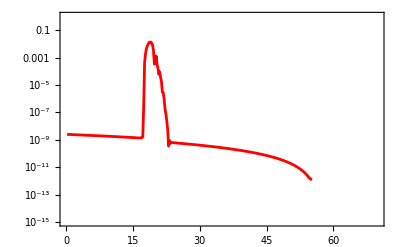

```mathematica
ListLogPlot[PN0,PlotRange->{{0,70},{10^-15,1}},Joined->True,Frame->True,PlotStyle->Red]
```

```mathematica
kmpc=Solve[0.05/Mpc==((a[Ne] H[Ne])/cs)/.solNe1/.Ne->0,Mpc][[1]][[1,2]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

549.188

```mathematica
Pkc=Table[{(kmpc((H[Ne]a[Ne])/cs)/.solNe1/.{Ne->NeHE[[i]]})[[1]],(k[[i]]^3/(2*Pi^2)*Abs[u[Ne]/(z[Ne]/.solNe1)]^2/.MSol[[i]]/.Ne->NeEnd[[i]])[[1]][[1]]},{i,1,iMax}]
```

{{0.0609748,2.45213×10^-9},{0.0743582,2.43915×10^-9},{0.0906787,2.42359×10^-9},{0.110581,2.40686×10^-9},{0.13485,2.39182×10^-9},{0.164445,2.37682×10^-9},{0.200534,2.36187×10^-9},{0.244542,2.34608×10^-9},{0.298206,2.3307×10^-9},{0.363644,2.31505×10^-9},{0.44344,2.30061×10^-9},{0.540743,2.28648×10^-9},{0.659394,2.27174×10^-9},{0.804074,2.25735×10^-9},{0.980494,2.24255×10^-9},{1.19562,2.22751×10^-9},{1.45793,2.21181×10^-9},{1.77778,2.19626×10^-9},{2.16779,2.18152×10^-9},{2.64335,2.16788×10^-9},{3.22322,2.15472×10^-9},{3.93026,2.14104×10^-9},{4.79238,2.12728×10^-9},{5.84357,2.1125×10^-9},{7.1253,2.09701×10^-9},{8.68811,2.08131×10^-9},{10.5936,2.06635×10^-9},{12.917,2.05264×10^-9},{15.7499,2.03989×10^-9},{19.2039,2.02703×10^-9},{23.4152,2.01406×10^-9},{28.5499,2.00041×10^-9},{34.8104,1.98568×10^-9},{42.4434,1.97026×10^-9},{51.7498,1.95479×10^-9},{63.0964,1.94066×10^-9},{76.9304,1.92802×10^-9},{93.7969,1.91583×10^-9},{114.361,1.90348×10^-9},{139.432,1.89093×10^-9},{169.998,1.8772×10^-9},{207.263,1.86243×10^-9},{252.696,1.84692×10^-9},{308.087,1.83182×10^-9},{375.615,1.81833×10^-9},{457.943,1.80692×10^-9},{558.311,1.79553×10^-9},{680.672,1.78415×10^-9},{829.844,1.77209×10^-9},{1011.7,1.75823×10^-9},{1233.4,1.7421×10^-9},{1503.68,1.72594×10^-9},{1833.16,1.71046×10^-9},{2234.83,1.69706×10^-9},{2724.49,1.68806×10^-9},{3321.41,1.67764×10^-9},{4049.07,1.66743×10^-9},{4936.13,1.65517×10^-9},{6017.46,1.64173×10^-9},{7335.62,1.62401×10^-9},{8942.47,1.60672×10^-9},{10901.2,1.59409×10^-9},{13288.9,1.58723×10^-9},{16199.4,1.5807×10^-9},{19747.1,1.56785×10^-9},{24071.7,1.54824×10^-9},{29343.1,1.52672×10^-9},{35768.5,1.51603×10^-9},{43600.5,1.51693×10^-9},{53146.9,1.51188×10^-9},{64782.9,1.4887×10^-9},{78965.5,1.46761×10^-9},{96252.,1.4585×10^-9},{117321.,1.45827×10^-9},{143001.,1.44052×10^-9},{174298.,1.41728×10^-9},{212441.,1.41514×10^-9},{258926.,1.40427×10^-9},{315577.,1.37035×10^-9},{384612.,1.36324×10^-9},{468737.,1.36173×10^-9},{571238.,1.3494×10^-9},{696119.,1.38146×10^-9},{848253.,1.36362×10^-9},{1.03356×10^6,1.40089×10^-9},{1.25924×10^6,1.63401×10^-9},{1.53398×10^6,2.21243×10^-7},{1.86832×10^6,0.000380668},{2.27488×10^6,0.00184405},{2.76862×10^6,0.00421675},{3.36634×10^6,0.0068144},{4.06937×10^6,0.00935131},{4.81151×10^6,0.0121948},{5.74247×10^6,0.0133233},{6.90544×10^6,0.0135292},{8.34465×10^6,0.0112069},{1.01142×10^7,0.00783043},{1.22815×10^7,0.003425},{1.49297×10^7,0.000335601},{1.8161×10^7,0.000408448},{2.21008×10^7,0.00130154},{2.69022×10^7,0.000313758},{3.27517×10^7,0.000173999},{3.98771×10^7,0.0000607134},{4.85555×10^7,0.0000910302},{5.91248×10^7,0.0000360797},{7.19964×10^7,0.0000174934},{8.76711×10^7,2.94182×10^-6},{1.06759×10^8,2.64781×10^-6},{1.30003×10^8,8.93325×10^-7},{1.58306×10^8,1.76069×10^-7},{1.9277×10^8,7.48721×10^-8},{2.34733×10^8,2.32573×10^-8},{2.85828×10^8,5.3516×10^-9},{3.48039×10^8,3.43246×10^-10},{4.23784×10^8,8.70891×10^-10},{5.16004×10^8,5.51599×10^-10},{6.28281×10^8,6.01527×10^-10},{7.64975×10^8,6.05819×10^-10},{9.31391×10^8,6.2672×10^-10},{1.13399×10^9,5.93913×10^-10},{1.38062×10^9,5.92091×10^-10},{1.68087×10^9,5.81542×10^-10},{2.04636×10^9,5.79513×10^-10},{2.49129×10^9,5.7112×10^-10},{3.03288×10^9,5.59076×10^-10},{3.69214×10^9,5.5021×10^-10},{4.49461×10^9,5.43521×10^-10},{5.47137×10^9,5.40828×10^-10},{6.66024×10^9,5.3069×10^-10},{8.10725×10^9,5.2461×10^-10},{9.8684×10^9,5.18237×10^-10},{1.20119×10^10,5.10652×10^-10},{1.46205×10^10,5.02333×10^-10},{1.77953×10^10,4.9945×10^-10},{2.16589×10^10,4.88094×10^-10},{2.63607×10^10,4.84577×10^-10},{3.20823×10^10,4.76232×10^-10},{3.90448×10^10,4.68902×10^-10},{4.75172×10^10,4.62936×10^-10},{5.78263×10^10,4.56149×10^-10},{7.03703×10^10,4.49248×10^-10},{8.56329×10^10,4.43025×10^-10},{1.04203×10^11,4.36391×10^-10},{1.26797×10^11,4.30169×10^-10},{1.54285×10^11,4.23437×10^-10},{1.87727×10^11,4.16891×10^-10},{2.28411×10^11,4.10903×10^-10},{2.77903×10^11,4.05217×10^-10},{3.3811×10^11,3.98901×10^-10},{4.11348×10^11,3.9175×10^-10},{5.00434×10^11,3.85586×10^-10},{6.08794×10^11,3.80301×10^-10},{7.40593×10^11,3.75105×10^-10},{9.00897×10^11,3.67931×10^-10},{1.09586×10^12,3.61139×10^-10},{1.33298×10^12,3.55778×10^-10},{1.62134×10^12,3.51638×10^-10},{1.97202×10^12,3.45262×10^-10},{2.39845×10^12,3.38092×10^-10},{2.917×10^12,3.32511×10^-10},{3.54753×10^12,3.28003×10^-10},{4.31418×10^12,3.23247×10^-10},{5.24633×10^12,3.16892×10^-10},{6.37962×10^12,3.10519×10^-10},{7.75743×10^12,3.05606×10^-10},{9.43241×10^12,3.01212×10^-10},{1.14686×10^13,2.9553×10^-10},{1.39438×10^13,2.89627×10^-10},{1.69524×10^13,2.84238×10^-10},{2.06093×10^13,2.7954×10^-10},{2.5054×10^13,2.74645×10^-10},{3.04559×10^13,2.69488×10^-10},{3.70208×10^13,2.64328×10^-10},{4.49987×10^13,2.59048×10^-10},{5.46932×10^13,2.5408×10^-10},{6.64731×10^13,2.49411×10^-10},{8.07862×10^13,2.44748×10^-10},{9.81763×10^13,2.39921×10^-10},{1.19304×10^14,2.35041×10^-10},{1.4497×10^14,2.30122×10^-10},{1.76149×10^14,2.25424×10^-10},{2.14021×10^14,2.21019×10^-10},{2.60023×10^14,2.16619×10^-10},{3.15893×10^14,2.12088×10^-10},{3.83746×10^14,2.0748×10^-10},{4.66146×10^14,2.02865×10^-10},{5.66205×10^14,1.98464×10^-10},{6.87699×10^14,1.94375×10^-10},{8.35211×10^14,1.90264×10^-10},{1.0143×10^15,1.86013×10^-10},{1.2317×10^15,1.81658×10^-10},{1.49561×10^15,1.77307×10^-10},{1.81593×10^15,1.73211×10^-10},{2.2047×10^15,1.69459×10^-10},{2.6765×10^15,1.65632×10^-10},{3.24903×10^15,1.61641×10^-10},{3.94374×10^15,1.57566×10^-10},{4.7866×10^15,1.53506×10^-10},{5.80914×10^15,1.49732×10^-10},{7.04955×10^15,1.46224×10^-10},{8.55409×10^15,1.4275×10^-10},{1.03788×10^16,1.39042×10^-10},{1.25917×10^16,1.35268×10^-10},{1.52751×10^16,1.31512×10^-10},{1.85285×10^16,1.27987×10^-10},{2.24726×10^16,1.24765×10^-10},{2.72537×10^16,1.21473×10^-10},{3.30486×10^16,1.18076×10^-10},{4.00715×10^16,1.14635×10^-10},{4.85814×10^16,1.11226×10^-10},{5.88921×10^16,1.0803×10^-10},{7.1383×10^16,1.04975×10^-10},{8.65129×10^16,1.01938×10^-10},{1.04837×10^17,9.885×10^-11},{1.27026×10^17,9.57378×10^-11},{1.53891×10^17,9.26167×10^-11},{1.86414×10^17,8.97389×10^-11},{2.25778×10^17,8.69551×10^-11},{2.73416×10^17,8.42702×10^-11},{3.31057×10^17,8.1422×10^-11},{4.00788×10^17,7.85628×10^-11},{4.85129×10^17,7.57427×10^-11},{5.87124×10^17,7.31428×10^-11},{7.10442×10^17,7.07338×10^-11},{8.5951×10^17,6.83214×10^-11},{1.03967×10^18,6.57659×10^-11},{1.25735×10^18,6.31548×10^-11},{1.52032×10^18,6.05932×10^-11},{1.8379×10^18,5.82267×10^-11},{2.22136×10^18,5.61053×10^-11},{2.68422×10^18,5.4004×10^-11},{3.24277×10^18,5.16987×10^-11},{3.9166×10^18,4.93275×10^-11},{4.72925×10^18,4.70297×10^-11},{5.70902×10^18,4.50063×10^-11},{6.88985×10^18,4.32321×10^-11},{8.31248×10^18,4.13961×10^-11},{1.00258×10^19,3.94234×10^-11},{1.20883×10^19,3.74388×10^-11},{1.45704×10^19,3.5462×10^-11},{1.75559×10^19,3.37626×10^-11},{2.11453×10^19,3.22422×10^-11},{2.54587×10^19,3.05967×10^-11},{3.0639×10^19,2.87526×10^-11},{3.68568×10^19,2.71075×10^-11},{4.43155×10^19,2.55957×10^-11},{5.32569×10^19,2.4059×10^-11},{6.3969×10^19,2.25281×10^-11},{7.67936×10^19,2.11927×10^-11},{9.21355×10^19,1.98342×10^-11},{1.10472×10^20,1.85598×10^-11},{1.32364×10^20,1.72982×10^-11},{1.58476×10^20,1.6014×10^-11},{1.89589×10^20,1.48513×10^-11},{2.26612×10^20,1.37341×10^-11},{2.70604×10^20,1.26343×10^-11},{3.22801×10^20,1.15837×10^-11},{3.84633×10^20,1.06026×10^-11},{4.57742×10^20,9.68258×10^-12},{5.43999×10^20,8.72067×10^-12},{6.45517×10^20,7.8908×10^-12},{7.64687×10^20,7.12676×10^-12},{9.04163×10^20,6.34973×10^-12},{1.0668×10^21,5.61256×10^-12},{1.25566×10^21,5.02119×10^-12},{1.47384×10^21,4.40909×10^-12},{1.72433×10^21,3.79166×10^-12},{2.0098×10^21,3.28837×10^-12},{2.33215×10^21,2.80731×10^-12},{2.6918×10^21,2.33604×10^-12},{3.08663×10^21,1.95225×10^-12},{3.51039×10^21,1.63242×10^-12},{3.95057×10^21,1.43185×10^-12},{4.38515×10^21,1.28094×10^-12},{4.7767×10^21,1.17368×10^-12}}

```mathematica
Export["PkD.dat",Pkc];
```

```mathematica
Pkc=Import["PkD.dat"];
c1=Interpolation[Pkc,InterpolationOrder->1]
AA=LogLogPlot[{c1[x]},{x,0.0634257151149378,6.242598573013641*^19},PlotRange->{{0.001,4*10^22},{10^-13,1}},Frame->True,FrameStyle->Thick,FrameTicksStyle->Black,PlotStyle->{Purple},LabelStyle->Directive[24,Bold,Black,FontFamily->"Book Antiqua"],ImageSize->{600,400},AspectRatio->Full,RotateLabel->False,Axes->False,FrameLabel->{"K/Mpc^-1","P_s"}]
```

InterpolatingFunction[…]

```mathematica
InterpolatingFunction[…];
```

```mathematica
c1[0.05kmpc]
```

2.00331×10^-9

```mathematica
AA=ListLogLogPlot[Pkc,PlotRange->{{0.05,4*10^22},{10^-13,1}},Joined->True,Frame->True,FrameStyle->Thick,FrameTicksStyle->Black,PlotStyle->Purple,LabelStyle->Directive[24,Bold,Black,FontFamily->"Book Antiqua"],ImageSize->{600,400},AspectRatio->Full,RotateLabel->False,Axes->False,FrameLabel->{"K/Mpc^-1","P_R"}]
```

```mathematica
ss=-Graphics-;
```

```mathematica
fback=Show[{LogLogPlot[{ns0[Ne]},{Ne,1,10},PlotRange->{{10^-4,10^24},{10^-12,10^0}},PlotStyle->{Black,Thickness[0.005]},Frame-> True,FrameLabel->{"M/M_⊙","f_Pbh"},LabelStyle->Directive[22,Bold,FontFamily->"Book Antiqua"],ImageSize->{600,400},AspectRatio->Full],Graphics[{Texture[ss],EdgeForm[Black],Polygon[{{-9.1,-27.56},{55.2,-27.56},{55.2,0.1},{-9.1,0.1}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},ImageSize->{600,400},AspectRatio->Full]},Axes->False,RotateLabel->True]
```

```mathematica
Show[fback,AA]
```

```mathematica
Mkc=Table[(1/((1.9*10^6)^-2)*(1/(√3))^3/0.2*(106.75/10.75)^(-1/6)*(kmpc*k[[i]])^-2)[[1]],{i,1,iMax}];
```

```mathematica
PRc=Interpolation[Pkc,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
qend=PRc[[1,1,2]]
```

4.7767×10^21

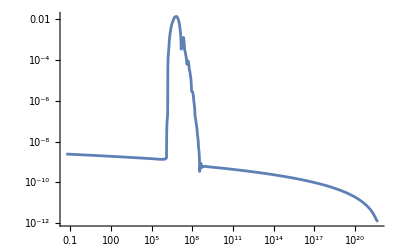

```mathematica
LogLogPlot[PRc[x],{x,0.05,qend},PlotRange->All]
```

```mathematica
For[i=1,i≤ iMax,i++,
si[i]=NIntegrate[16/81*1/q*(q/(k[[i]]*kmpc))^4 Exp[-q^2/(k[[i]]*kmpc)^2]PRc[q],{q,0,PRc[[1,1,2]]}];
]
```

```mathematica
Beep[]
```

```mathematica
sigma=Table[si[i],{i,1,iMax}]//N;
```

```mathematica
δc=0.4;
```

```mathematica
(*For[i=1,i≤ iMax,i++,
B[i]=√(1/(2Pi))(sigma[[i]])^(1/2)/δc Exp[(- δc^2)/(2*sigma[[i]])]]*)
```

```mathematica
For[i=1,i≤ iMax,i++,
B[i]=1/2 Erfc[δc/(√(2*sigma[[i]]))]]
```

```mathematica
f=Table[B[i]/(1.84*10^-8)*((1/(√3))^3/0.2)^(3/2)*(10.75/106.75)^(1/4)*(Mkc[[i]])^(-1/2),{i,1,iMax}];
```

```mathematica
ac=Table[{Mkc[[i]],f[[i]][[1]]},{i,1,iMax}];
```

```mathematica
Export["FPBHD.dat",ac];
```

```mathematica
ac=Import["FPBHD.dat"];
```

```mathematica
Max[f]
```

2.3291×10^-27

```mathematica
fc=ListLogLogPlot[ac,Joined->True,Frame->True,Axes->False,PlotRange->{{10^-18,10^4},{10^-5,1}},PlotStyle->{Purple,Thickness[0.002]}]
```

-Graphics-

```mathematica
s1=Interpolation[ac,InterpolationOrder->2]
fc=LogLogPlot[s1[x],{x,3.86*^-39,7.0121*^14},Frame->True,Axes->False,PlotRange->{{10^-18,10^4},{10^-5,10^0}},PlotStyle->Red,FillingStyle->Black,ImageSize->{400,300}]
```

InterpolatingFunction[…]

-Graphics-

```mathematica
fb=-Graphics-;
```

```mathematica
fback=Show[{LogLogPlot[{ns0[Ne]},{Ne,1,10},PlotRange->{{10^-18,10^4},{10^-5,10^0}},PlotStyle->{Black,Thickness[0.005]},Frame-> True,FrameLabel->{"M/M_⊙","f_Pbh"},LabelStyle->Directive[22,Bold,FontFamily->"Book Antiqua"],ImageSize->{600,400},AspectRatio->Full],Graphics[{Texture[fb],EdgeForm[Black],Polygon[{{-41.5,-11.55},{9.3,-11.55},{9.3,0},{-41.5,0}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},ImageSize->{600,400},AspectRatio->Full]},Axes->False,RotateLabel->True]
```

```mathematica
fpbh=Show[fback,fc,ImageSize->{600,400}]
```

```mathematica
Show[back,fc,ImageSize->{600,400}]
```

```mathematica
data2=Table[{i,(kmpc((a[Ne] H[Ne])/cs)/.solNe1/.{Ne->NeHE[[i]]})[[1]],NeHE[[i]],NeBD[[i]],Mkc[[i]],PN0[[i]][[2]],f[[i]]},{i,1,iMax}];
```

```mathematica
pr=data2[[All,6]];
```

```mathematica
Position[pr,Max[pr]][[1]][[1]]
```

95

```mathematica
Length[Pkc]
```

276

```mathematica
Pkc[[Position[pr,Max[pr]][[1]][[1]],2]]
```

0.0135292

```mathematica
Mkc[[Position[pr,Max[pr]][[1]][[1]]]]
```

0.0496882

```mathematica
f[[Position[pr,Max[pr]][[1]][[1]]]]
```

{5.93912×10^-36}

```mathematica
kpeak=(kmpc((a[Ne] H[Ne])/cs)/.solNe1/.{Ne->NeHE[[Position[pr,Max[pr]][[1]][[1]]]]})
```

{6.90544×10^6}

```mathematica
mytab2=Text@Grid[Prepend[data2,{"i","K","N","NBD","M(k)/M_o","P_R","f"}],Frame->All,Alignment->{Center},ItemSize->{10},Frame->Darker[Gray,.6],ItemStyle->14,Background->{Automatic,{1-> Green,Position[pr,Max[pr]][[1]][[1]]+1->Yellow}}]
```

i | K | N | NBD | M(k)/M_o | P_R | f
1 | 0.0609748 | 0.2 | -4.8 | 6.37286×10^14 | 2.45213×10^-9 | {0.}
2 | 0.0743582 | 0.4 | -4.6 | 4.28526×10^14 | 2.43915×10^-9 | {0.}
3 | 0.0906787 | 0.6 | -4.4 | 2.88154×10^14 | 2.42359×10^-9 | {0.}
4 | 0.110581 | 0.8 | -4.2 | 1.93766×10^14 | 2.40686×10^-9 | {0.}
5 | 0.13485 | 1. | -4. | 1.30297×10^14 | 2.39182×10^-9 | {0.}
6 | 0.164445 | 1.2 | -3.8 | 8.76182×10^13 | 2.37682×10^-9 | {0.}
7 | 0.200534 | 1.4 | -3.6 | 5.89195×10^13 | 2.36187×10^-9 | {0.}
8 | 0.244542 | 1.6 | -3.4 | 3.96213×10^13 | 2.34608×10^-9 | {0.}
9 | 0.298206 | 1.8 | -3.2 | 2.66442×10^13 | 2.3307×10^-9 | {0.}
10 | 0.363644 | 2. | -3. | 1.79177×10^13 | 2.31505×10^-9 | {0.}
11 | 0.44344 | 2.2 | -2.8 | 1.20494×10^13 | 2.30061×10^-9 | {0.}
12 | 0.540743 | 2.4 | -2.6 | 8.10314×10^12 | 2.28648×10^-9 | {0.}
13 | 0.659394 | 2.6 | -2.4 | 5.44937×10^12 | 2.27174×10^-9 | {0.}
14 | 0.804074 | 2.8 | -2.2 | 3.66474×10^12 | 2.25735×10^-9 | {0.}
15 | 0.980494 | 3. | -2. | 2.46459×10^12 | 2.24255×10^-9 | {0.}
16 | 1.19562 | 3.2 | -1.8 | 1.65749×10^12 | 2.22751×10^-9 | {0.}
17 | 1.45793 | 3.4 | -1.6 | 1.11471×10^12 | 2.21181×10^-9 | {0.}
18 | 1.77778 | 3.6 | -1.4 | 7.49686×10^11 | 2.19626×10^-9 | {0.}
19 | 2.16779 | 3.8 | -1.2 | 5.04197×10^11 | 2.18152×10^-9 | {0.}
20 | 2.64335 | 4. | -1. | 3.39099×10^11 | 2.16788×10^-9 | {0.}
21 | 3.22322 | 4.2 | -0.8 | 2.28064×10^11 | 2.15472×10^-9 | {0.}
22 | 3.93026 | 4.4 | -0.6 | 1.53388×10^11 | 2.14104×10^-9 | {0.}
23 | 4.79238 | 4.6 | -0.4 | 1.03165×10^11 | 2.12728×10^-9 | {0.}
24 | 5.84357 | 4.8 | -0.2 | 6.93871×10^10 | 2.1125×10^-9 | {0.}
25 | 7.1253 | 5. | 0. | 4.66691×10^10 | 2.09701×10^-9 | {0.}
26 | 8.68811 | 5.2 | 0.2 | 3.13895×10^10 | 2.08131×10^-9 | {0.}
27 | 10.5936 | 5.4 | 0.4 | 2.11128×10^10 | 2.06635×10^-9 | {0.}
28 | 12.917 | 5.6 | 0.6 | 1.42007×10^10 | 2.05264×10^-9 | {0.}
29 | 15.7499 | 5.8 | 0.8 | 9.55173×10^9 | 2.03989×10^-9 | {0.}
30 | 19.2039 | 6. | 1. | 6.42478×10^9 | 2.02703×10^-9 | {0.}
31 | 23.4152 | 6.2 | 1.2 | 4.32155×10^9 | 2.01406×10^-9 | {0.}
32 | 28.5499 | 6.4 | 1.4 | 2.90687×10^9 | 2.00041×10^-9 | {0.}
33 | 34.8104 | 6.6 | 1.6 | 1.95532×10^9 | 1.98568×10^-9 | {0.}
34 | 42.4434 | 6.8 | 1.8 | 1.31527×10^9 | 1.97026×10^-9 | {0.}
35 | 51.7498 | 7. | 2. | 8.84744×10^8 | 1.95479×10^-9 | {0.}
36 | 63.0964 | 7.2 | 2.2 | 5.95149×10^8 | 1.94066×10^-9 | {0.}
37 | 76.9304 | 7.4 | 2.4 | 4.0035×10^8 | 1.92802×10^-9 | {0.}
38 | 93.7969 | 7.6 | 2.6 | 2.69314×10^8 | 1.91583×10^-9 | {0.}
39 | 114.361 | 7.8 | 2.8 | 1.81169×10^8 | 1.90348×10^-9 | {0.}
40 | 139.432 | 8. | 3. | 1.21875×10^8 | 1.89093×10^-9 | {0.}
41 | 169.998 | 8.2 | 3.2 | 8.19877×10^7 | 1.8772×10^-9 | {0.}
42 | 207.263 | 8.4 | 3.4 | 5.51556×10^7 | 1.86243×10^-9 | {0.}
43 | 252.696 | 8.6 | 3.6 | 3.71054×10^7 | 1.84692×10^-9 | {0.}
44 | 308.087 | 8.8 | 3.8 | 2.49626×10^7 | 1.83182×10^-9 | {0.}
45 | 375.615 | 9. | 4. | 1.67938×10^7 | 1.81833×10^-9 | {0.}
46 | 457.943 | 9.2 | 4.2 | 1.12983×10^7 | 1.80692×10^-9 | {0.}
47 | 558.311 | 9.4 | 4.4 | 7.60122×10^6 | 1.79553×10^-9 | {0.}
48 | 680.672 | 9.6 | 4.6 | 5.11399×10^6 | 1.78415×10^-9 | {0.}
49 | 829.844 | 9.8 | 4.8 | 3.44066×10^6 | 1.77209×10^-9 | {0.}
50 | 1011.7 | 10. | 5. | 2.31489×10^6 | 1.75823×10^-9 | {0.}
51 | 1233.4 | 10.2 | 5.2 | 1.55749×10^6 | 1.7421×10^-9 | {0.}
52 | 1503.68 | 10.4 | 5.4 | 1.04791×10^6 | 1.72594×10^-9 | {0.}
53 | 1833.16 | 10.6 | 5.6 | 705071. | 1.71046×10^-9 | {0.}
54 | 2234.83 | 10.8 | 5.8 | 474401. | 1.69706×10^-9 | {0.}
55 | 2724.49 | 11. | 6. | 319202. | 1.68806×10^-9 | {0.}
56 | 3321.41 | 11.2 | 6.2 | 214779. | 1.67764×10^-9 | {0.}
57 | 4049.07 | 11.4 | 6.4 | 144519. | 1.66743×10^-9 | {0.}
58 | 4936.13 | 11.6 | 6.6 | 97244.1 | 1.65517×10^-9 | {0.}
59 | 6017.46 | 11.8 | 6.8 | 65434.8 | 1.64173×10^-9 | {0.}
60 | 7335.62 | 12. | 7. | 44031.3 | 1.62401×10^-9 | {0.}
61 | 8942.47 | 12.2 | 7.2 | 29629.2 | 1.60672×10^-9 | {0.}
62 | 10901.2 | 12.4 | 7.4 | 19938.2 | 1.59409×10^-9 | {0.}
63 | 13288.9 | 12.6 | 7.6 | 13417.1 | 1.58723×10^-9 | {0.}
64 | 16199.4 | 12.8 | 7.8 | 9029.01 | 1.5807×10^-9 | {0.}
65 | 19747.1 | 13. | 8. | 6076.14 | 1.56785×10^-9 | {0.}
66 | 24071.7 | 13.2 | 8.2 | 4089.05 | 1.54824×10^-9 | {0.}
67 | 29343.1 | 13.4 | 8.4 | 2751.85 | 1.52672×10^-9 | {0.}
68 | 35768.5 | 13.6 | 8.6 | 1851.97 | 1.51603×10^-9 | {0.}
69 | 43600.5 | 13.8 | 8.8 | 1246.39 | 1.51693×10^-9 | {0.}
70 | 53146.9 | 14. | 9. | 838.841 | 1.51188×10^-9 | {0.}
71 | 64782.9 | 14.2 | 9.2 | 564.567 | 1.4887×10^-9 | {0.}
72 | 78965.5 | 14.4 | 9.4 | 379.98 | 1.46761×10^-9 | {0.}
73 | 96252. | 14.6 | 9.6 | 255.75 | 1.4585×10^-9 | {0.}
74 | 117321. | 14.8 | 9.8 | 172.14 | 1.45827×10^-9 | {0.}
75 | 143001. | 15. | 10. | 115.867 | 1.44052×10^-9 | {0.}
76 | 174298. | 15.2 | 10.2 | 77.9923 | 1.41728×10^-9 | {0.}
77 | 212441. | 15.4 | 10.4 | 52.5 | 1.41514×10^-9 | {0.}
78 | 258926. | 15.6 | 10.6 | 35.3414 | 1.40427×10^-9 | {0.}
79 | 315577. | 15.8 | 10.8 | 23.7917 | 1.37035×10^-9 | {0.}
80 | 384612. | 16. | 11. | 16.0173 | 1.36324×10^-9 | {0.}
81 | 468737. | 16.2 | 11.2 | 10.7839 | 1.36173×10^-9 | {0.}
82 | 571238. | 16.4 | 11.4 | 7.26109 | 1.3494×10^-9 | {0.}
83 | 696119. | 16.6 | 11.6 | 4.88954 | 1.38146×10^-9 | {0.}
84 | 848253. | 16.8 | 11.8 | 3.29295 | 1.36362×10^-9 | {0.}
85 | 1.03356×10^6 | 17. | 12. | 2.21801 | 1.40089×10^-9 | {0.}
86 | 1.25924×10^6 | 17.2 | 12.2 | 1.49424 | 1.63401×10^-9 | {0.}
87 | 1.53398×10^6 | 17.4 | 12.4 | 1.00692 | 2.21243×10^-7 | {1.31476×10^-187}
88 | 1.86832×10^6 | 17.6 | 12.6 | 0.678789 | 0.000380668 | {1.21426×10^-100}
89 | 2.27488×10^6 | 17.8 | 12.8 | 0.457845 | 0.00184405 | {8.03131×10^-62}
90 | 2.76862×10^6 | 18. | 13. | 0.309106 | 0.00421675 | {1.6264×10^-42}
91 | 3.36634×10^6 | 18.2 | 13.2 | 0.209083 | 0.0068144 | {1.24341×10^-32}
92 | 4.06937×10^6 | 18.4 | 13.4 | 0.143081 | 0.00935131 | {3.41108×10^-28}
93 | 4.81151×10^6 | 18.6 | 13.6 | 0.102346 | 0.0121948 | {2.3291×10^-27}
94 | 5.74247×10^6 | 18.8 | 13.8 | 0.0718519 | 0.0133233 | {1.61544×10^-29}
95 | 6.90544×10^6 | 19. | 14. | 0.0496882 | 0.0135292 | {5.93912×10^-36}
96 | 8.34465×10^6 | 19.2 | 14.2 | 0.0340267 | 0.0112069 | {3.3768×10^-49}
97 | 1.01142×10^7 | 19.4 | 14.4 | 0.0231617 | 0.00783043 | {1.86922×10^-73}
98 | 1.22815×10^7 | 19.6 | 14.6 | 0.0157085 | 0.003425 | {1.0384×10^-114}
99 | 1.49297×10^7 | 19.8 | 14.8 | 0.01063 | 0.000335601 | {7.9042×10^-182}
100 | 1.8161×10^7 | 20. | 15. | 0.00718381 | 0.000408448 | {3.51569×10^-291}
101 | 2.21008×10^7 | 20.2 | 15.2 | 0.00485088 | 0.00130154 | {0.}
102 | 2.69022×10^7 | 20.4 | 15.4 | 0.00327385 | 0.000313758 | {0.}
103 | 3.27517×10^7 | 20.6 | 15.6 | 0.00220885 | 0.000173999 | {0.}
104 | 3.98771×10^7 | 20.8 | 15.8 | 0.00149001 | 0.0000607134 | {0.}
105 | 4.85555×10^7 | 21. | 16. | 0.00100498 | 0.0000910302 | {0.}
106 | 5.91248×10^7 | 21.2 | 16.2 | 0.000677791 | 0.0000360797 | {0.}
107 | 7.19964×10^7 | 21.4 | 16.4 | 0.000457103 | 0.0000174934 | {0.}
108 | 8.76711×10^7 | 21.6 | 16.6 | 0.000308264 | 2.94182×10^-6 | {0.}
109 | 1.06759×10^8 | 21.8 | 16.8 | 0.000207887 | 2.64781×10^-6 | {0.}
110 | 1.30003×10^8 | 22. | 17. | 0.000140195 | 8.93325×10^-7 | {0.}
111 | 1.58306×10^8 | 22.2 | 17.2 | 0.0000945456 | 1.76069×10^-7 | {0.}
112 | 1.9277×10^8 | 22.4 | 17.4 | 0.0000637615 | 7.48721×10^-8 | {0.}
113 | 2.34733×10^8 | 22.6 | 17.6 | 0.0000430018 | 2.32573×10^-8 | {0.}
114 | 2.85828×10^8 | 22.8 | 17.8 | 0.0000290019 | 5.3516×10^-9 | {0.}
115 | 3.48039×10^8 | 23. | 18. | 0.0000195605 | 3.43246×10^-10 | {0.}
116 | 4.23784×10^8 | 23.2 | 18.2 | 0.0000131931 | 8.70891×10^-10 | {0.}
117 | 5.16004×10^8 | 23.4 | 18.4 | 8.89876×10^-6 | 5.51599×10^-10 | {0.}
118 | 6.28281×10^8 | 23.6 | 18.6 | 6.00243×10^-6 | 6.01527×10^-10 | {0.}
119 | 7.64975×10^8 | 23.8 | 18.8 | 4.04894×10^-6 | 6.05819×10^-10 | {0.}
120 | 9.31391×10^8 | 24. | 19. | 2.73131×10^-6 | 6.2672×10^-10 | {0.}
121 | 1.13399×10^9 | 24.2 | 19.2 | 1.84255×10^-6 | 5.93913×10^-10 | {0.}
122 | 1.38062×10^9 | 24.4 | 19.4 | 1.24304×10^-6 | 5.92091×10^-10 | {0.}
123 | 1.68087×10^9 | 24.6 | 19.6 | 8.38627×10^-7 | 5.81542×10^-10 | {0.}
124 | 2.04636×10^9 | 24.8 | 19.8 | 5.65809×10^-7 | 5.79513×10^-10 | {0.}
125 | 2.49129×10^9 | 25. | 20. | 3.81758×10^-7 | 5.7112×10^-10 | {0.}
126 | 3.03288×10^9 | 25.2 | 20.2 | 2.57587×10^-7 | 5.59076×10^-10 | {0.}
127 | 3.69214×10^9 | 25.4 | 20.4 | 1.73811×10^-7 | 5.5021×10^-10 | {0.}
128 | 4.49461×10^9 | 25.6 | 20.6 | 1.17287×10^-7 | 5.43521×10^-10 | {0.}
129 | 5.47137×10^9 | 25.8 | 20.8 | 7.91487×10^-8 | 5.40828×10^-10 | {0.}
130 | 6.66024×10^9 | 26. | 21. | 5.34141×10^-8 | 5.3069×10^-10 | {0.}
131 | 8.10725×10^9 | 26.2 | 21.2 | 3.60486×10^-8 | 5.2461×10^-10 | {0.}
132 | 9.8684×10^9 | 26.4 | 21.4 | 2.433×10^-8 | 5.18237×10^-10 | {0.}
133 | 1.20119×10^10 | 26.6 | 21.6 | 1.64216×10^-8 | 5.10652×10^-10 | {0.}
134 | 1.46205×10^10 | 26.8 | 21.8 | 1.10843×10^-8 | 5.02333×10^-10 | {0.}
135 | 1.77953×10^10 | 27. | 22. | 7.48212×10^-9 | 4.9945×10^-10 | {0.}
136 | 2.16589×10^10 | 27.2 | 22.2 | 5.05083×10^-9 | 4.88094×10^-10 | {0.}
137 | 2.63607×10^10 | 27.4 | 22.4 | 3.40975×10^-9 | 4.84577×10^-10 | {0.}
138 | 3.20823×10^10 | 27.6 | 22.6 | 2.302×10^-9 | 4.76232×10^-10 | {0.}
139 | 3.90448×10^10 | 27.8 | 22.8 | 1.5542×10^-9 | 4.68902×10^-10 | {0.}
140 | 4.75172×10^10 | 28. | 23. | 1.04938×10^-9 | 4.62936×10^-10 | {0.}
141 | 5.78263×10^10 | 28.2 | 23.2 | 7.08572×10^-10 | 4.56149×10^-10 | {0.}
142 | 7.03703×10^10 | 28.4 | 23.4 | 4.78473×10^-10 | 4.49248×10^-10 | {0.}
143 | 8.56329×10^10 | 28.6 | 23.6 | 3.23113×10^-10 | 4.43025×10^-10 | {0.}
144 | 1.04203×10^11 | 28.8 | 23.8 | 2.1821×10^-10 | 4.36391×10^-10 | {0.}
145 | 1.26797×10^11 | 29. | 24. | 1.47373×10^-10 | 4.30169×10^-10 | {0.}
146 | 1.54285×10^11 | 29.2 | 24.2 | 9.95378×10^-11 | 4.23437×10^-10 | {0.}
147 | 1.87727×10^11 | 29.4 | 24.4 | 6.7233×10^-11 | 4.16891×10^-10 | {0.}
148 | 2.28411×10^11 | 29.6 | 24.6 | 4.54153×10^-11 | 4.10903×10^-10 | {0.}
149 | 2.77903×10^11 | 29.8 | 24.8 | 3.06794×10^-11 | 4.05217×10^-10 | {0.}
150 | 3.3811×10^11 | 30. | 25. | 2.07262×10^-11 | 3.98901×10^-10 | {0.}
151 | 4.11348×10^11 | 30.2 | 25.2 | 1.40029×10^-11 | 3.9175×10^-10 | {0.}
152 | 5.00434×10^11 | 30.4 | 25.4 | 9.46111×10^-12 | 3.85586×10^-10 | {0.}
153 | 6.08794×10^11 | 30.6 | 25.6 | 6.39286×10^-12 | 3.80301×10^-10 | {0.}
154 | 7.40593×10^11 | 30.8 | 25.8 | 4.31992×10^-12 | 3.75105×10^-10 | {0.}
155 | 9.00897×10^11 | 31. | 26. | 2.91934×10^-12 | 3.67931×10^-10 | {0.}
156 | 1.09586×10^12 | 31.2 | 26.2 | 1.97298×10^-12 | 3.61139×10^-10 | {0.}
157 | 1.33298×10^12 | 31.4 | 26.4 | 1.33349×10^-12 | 3.55778×10^-10 | {0.}
158 | 1.62134×10^12 | 31.6 | 26.6 | 9.01337×10^-13 | 3.51638×10^-10 | {0.}
159 | 1.97202×10^12 | 31.8 | 26.8 | 6.09277×10^-13 | 3.45262×10^-10 | {0.}
160 | 2.39845×10^12 | 32. | 27. | 4.11882×10^-13 | 3.38092×10^-10 | {0.}
161 | 2.917×10^12 | 32.2 | 27.2 | 2.7846×10^-13 | 3.32511×10^-10 | {0.}
162 | 3.54753×10^12 | 32.4 | 27.4 | 1.88271×10^-13 | 3.28003×10^-10 | {0.}
163 | 4.31418×10^12 | 32.6 | 27.6 | 1.27303×10^-13 | 3.23247×10^-10 | {0.}
164 | 5.24633×10^12 | 32.8 | 27.8 | 8.60845×10^-14 | 3.16892×10^-10 | {0.}
165 | 6.37962×10^12 | 33. | 28. | 5.82164×10^-14 | 3.10519×10^-10 | {0.}
166 | 7.75743×10^12 | 33.2 | 28.2 | 3.93731×10^-14 | 3.05606×10^-10 | {0.}
167 | 9.43241×10^12 | 33.4 | 28.4 | 2.66311×10^-14 | 3.01212×10^-10 | {0.}
168 | 1.14686×10^13 | 33.6 | 28.6 | 1.80142×10^-14 | 2.9553×10^-10 | {0.}
169 | 1.39438×10^13 | 33.8 | 28.8 | 1.21864×10^-14 | 2.89627×10^-10 | {0.}
170 | 1.69524×10^13 | 34. | 29. | 8.24466×10^-15 | 2.84238×10^-10 | {0.}
171 | 2.06093×10^13 | 34.2 | 29.2 | 5.57838×10^-15 | 2.7954×10^-10 | {0.}
172 | 2.5054×10^13 | 34.4 | 29.4 | 3.77469×10^-15 | 2.74645×10^-10 | {0.}
173 | 3.04559×10^13 | 34.6 | 29.6 | 2.55442×10^-15 | 2.69488×10^-10 | {0.}
174 | 3.70208×10^13 | 34.8 | 29.8 | 1.7288×10^-15 | 2.64328×10^-10 | {0.}
175 | 4.49987×10^13 | 35. | 30. | 1.17014×10^-15 | 2.59048×10^-10 | {0.}
176 | 5.46932×10^13 | 35.2 | 30.2 | 7.9208×10^-16 | 2.5408×10^-10 | {0.}
177 | 6.64731×10^13 | 35.4 | 30.4 | 5.36221×10^-16 | 2.49411×10^-10 | {0.}
178 | 8.07862×10^13 | 35.6 | 30.6 | 3.63046×10^-16 | 2.44748×10^-10 | {0.}
179 | 9.81763×10^13 | 35.8 | 30.8 | 2.45823×10^-16 | 2.39921×10^-10 | {0.}
180 | 1.19304×10^14 | 36. | 31. | 1.66467×10^-16 | 2.35041×10^-10 | {0.}
181 | 1.4497×10^14 | 36.2 | 31.2 | 1.1274×10^-16 | 2.30122×10^-10 | {0.}
182 | 1.76149×10^14 | 36.4 | 31.4 | 7.63618×10^-17 | 2.25424×10^-10 | {0.}
183 | 2.14021×10^14 | 36.6 | 31.6 | 5.17274×10^-17 | 2.21019×10^-10 | {0.}
184 | 2.60023×10^14 | 36.8 | 31.8 | 3.5044×10^-17 | 2.16619×10^-10 | {0.}
185 | 3.15893×10^14 | 37. | 32. | 2.37441×10^-17 | 2.12088×10^-10 | {0.}
186 | 3.83746×10^14 | 37.2 | 32.2 | 1.60897×10^-17 | 2.0748×10^-10 | {0.}
187 | 4.66146×10^14 | 37.4 | 32.4 | 1.09042×10^-17 | 2.02865×10^-10 | {0.}
188 | 5.66205×10^14 | 37.6 | 32.6 | 7.39075×10^-18 | 1.98464×10^-10 | {0.}
189 | 6.87699×10^14 | 37.8 | 32.8 | 5.01001×10^-18 | 1.94375×10^-10 | {0.}
190 | 8.35211×10^14 | 38. | 33. | 3.39659×10^-18 | 1.90264×10^-10 | {0.}
191 | 1.0143×10^15 | 38.2 | 33.2 | 2.30306×10^-18 | 1.86013×10^-10 | {0.}
192 | 1.2317×10^15 | 38.4 | 33.4 | 1.56179×10^-18 | 1.81658×10^-10 | {0.}
193 | 1.49561×10^15 | 38.6 | 33.6 | 1.05926×10^-18 | 1.77307×10^-10 | {0.}
194 | 1.81593×10^15 | 38.8 | 33.8 | 7.18519×10^-19 | 1.73211×10^-10 | {0.}
195 | 2.2047×10^15 | 39. | 34. | 4.87458×10^-19 | 1.69459×10^-10 | {0.}
196 | 2.6765×10^15 | 39.2 | 34.2 | 3.3075×10^-19 | 1.65632×10^-10 | {0.}
197 | 3.24903×10^15 | 39.4 | 34.4 | 2.24454×10^-19 | 1.61641×10^-10 | {0.}
198 | 3.94374×10^15 | 39.6 | 34.6 | 1.52342×10^-19 | 1.57566×10^-10 | {0.}
199 | 4.7866×10^15 | 39.8 | 34.8 | 1.03414×10^-19 | 1.53506×10^-10 | {0.}
200 | 5.80914×10^15 | 40. | 35. | 7.0212×10^-20 | 1.49732×10^-10 | {0.}
201 | 7.04955×10^15 | 40.2 | 35.2 | 4.76774×10^-20 | 1.46224×10^-10 | {0.}
202 | 8.55409×10^15 | 40.4 | 35.4 | 3.23808×10^-20 | 1.4275×10^-10 | {0.}
203 | 1.03788×10^16 | 40.6 | 35.6 | 2.19957×10^-20 | 1.39042×10^-10 | {0.}
204 | 1.25917×10^16 | 40.8 | 35.8 | 1.49439×10^-20 | 1.35268×10^-10 | {0.}
205 | 1.52751×10^16 | 41. | 36. | 1.01548×10^-20 | 1.31512×10^-10 | {0.}
206 | 1.85285×10^16 | 41.2 | 36.2 | 6.90171×10^-21 | 1.27987×10^-10 | {0.}
207 | 2.24726×10^16 | 41.4 | 36.4 | 4.69167×10^-21 | 1.24765×10^-10 | {0.}
208 | 2.72537×10^16 | 41.6 | 36.6 | 3.18995×10^-21 | 1.21473×10^-10 | {0.}
209 | 3.30486×10^16 | 41.8 | 36.8 | 2.16935×10^-21 | 1.18076×10^-10 | {0.}
210 | 4.00715×10^16 | 42. | 37. | 1.47559×10^-21 | 1.14635×10^-10 | {0.}
211 | 4.85814×10^16 | 42.2 | 37.2 | 1.00391×10^-21 | 1.11226×10^-10 | {0.}
212 | 5.88921×10^16 | 42.4 | 37.4 | 6.83157×10^-22 | 1.0803×10^-10 | {0.}
213 | 7.1383×10^16 | 42.6 | 37.6 | 4.64993×10^-22 | 1.04975×10^-10 | {0.}
214 | 8.65129×10^16 | 42.8 | 37.8 | 3.16573×10^-22 | 1.01938×10^-10 | {0.}
215 | 1.04837×10^17 | 43. | 38. | 2.1558×10^-22 | 9.885×10^-11 | {0.}
216 | 1.27026×10^17 | 43.2 | 38.2 | 1.46842×10^-22 | 9.57378×10^-11 | {0.}
217 | 1.53891×10^17 | 43.4 | 38.4 | 1.00048×10^-22 | 9.26167×10^-11 | {0.}
218 | 1.86414×10^17 | 43.6 | 38.6 | 6.81834×10^-23 | 8.97389×10^-11 | {0.}
219 | 2.25778×10^17 | 43.8 | 38.8 | 4.64805×10^-23 | 8.69551×10^-11 | {0.}
220 | 2.73416×10^17 | 44. | 39. | 3.16947×10^-23 | 8.42702×10^-11 | {0.}
221 | 3.31057×10^17 | 44.2 | 39.2 | 2.16187×10^-23 | 8.1422×10^-11 | {0.}
222 | 4.00788×10^17 | 44.4 | 39.4 | 1.47505×10^-23 | 7.85628×10^-11 | {0.}
223 | 4.85129×10^17 | 44.6 | 39.6 | 1.00675×10^-23 | 7.57427×10^-11 | {0.}
224 | 5.87124×10^17 | 44.8 | 39.8 | 6.87347×10^-24 | 7.31428×10^-11 | {0.}
225 | 7.10442×10^17 | 45. | 40. | 4.69438×10^-24 | 7.07338×10^-11 | {0.}
226 | 8.5951×10^17 | 45.2 | 40.2 | 3.20725×10^-24 | 6.83214×10^-11 | {0.}
227 | 1.03967×10^18 | 45.4 | 40.4 | 2.19203×10^-24 | 6.57659×10^-11 | {0.}
228 | 1.25735×10^18 | 45.6 | 40.6 | 1.49872×10^-24 | 6.31548×10^-11 | {0.}
229 | 1.52032×10^18 | 45.8 | 40.8 | 1.0251×10^-24 | 6.05932×10^-11 | {0.}
230 | 1.8379×10^18 | 46. | 41. | 7.01439×10^-25 | 5.82267×10^-11 | {0.}
231 | 2.22136×10^18 | 46.2 | 41.2 | 4.80174×10^-25 | 5.61053×10^-11 | {0.}
232 | 2.68422×10^18 | 46.4 | 41.4 | 3.28852×10^-25 | 5.4004×10^-11 | {0.}
233 | 3.24277×10^18 | 46.6 | 41.6 | 2.25322×10^-25 | 5.16987×10^-11 | {0.}
234 | 3.9166×10^18 | 46.8 | 41.8 | 1.54461×10^-25 | 4.93275×10^-11 | {0.}
235 | 4.72925×10^18 | 47. | 42. | 1.05938×10^-25 | 4.70297×10^-11 | {0.}
236 | 5.70902×10^18 | 47.2 | 42.2 | 7.26963×10^-26 | 4.50063×10^-11 | {0.}
237 | 6.88985×10^18 | 47.4 | 42.4 | 4.99133×10^-26 | 4.32321×10^-11 | {0.}
238 | 8.31248×10^18 | 47.6 | 42.6 | 3.42905×10^-26 | 4.13961×10^-11 | {0.}
239 | 1.00258×10^19 | 47.8 | 42.8 | 2.35721×10^-26 | 3.94234×10^-11 | {0.}
240 | 1.20883×10^19 | 48. | 43. | 1.62144×10^-26 | 3.74388×10^-11 | {0.}
241 | 1.45704×10^19 | 48.2 | 43.2 | 1.11608×10^-26 | 3.5462×10^-11 | {0.}
242 | 1.75559×10^19 | 48.4 | 43.4 | 7.6876×10^-27 | 3.37626×10^-11 | {0.}
243 | 2.11453×10^19 | 48.6 | 43.6 | 5.29917×10^-27 | 3.22422×10^-11 | {0.}
244 | 2.54587×10^19 | 48.8 | 43.8 | 3.65565×10^-27 | 3.05967×10^-11 | {0.}
245 | 3.0639×10^19 | 49. | 44. | 2.52399×10^-27 | 2.87526×10^-11 | {0.}
246 | 3.68568×10^19 | 49.2 | 44.2 | 1.74421×10^-27 | 2.71075×10^-11 | {0.}
247 | 4.43155×10^19 | 49.4 | 44.4 | 1.20649×10^-27 | 2.55957×10^-11 | {0.}
248 | 5.32569×10^19 | 49.6 | 44.6 | 8.35379×10^-28 | 2.4059×10^-11 | {0.}
249 | 6.3969×10^19 | 49.8 | 44.8 | 5.79024×10^-28 | 2.25281×10^-11 | {0.}
250 | 7.67936×10^19 | 50. | 45. | 4.01778×10^-28 | 2.11927×10^-11 | {0.}
251 | 9.21355×10^19 | 50.2 | 45.2 | 2.79114×10^-28 | 1.98342×10^-11 | {0.}
252 | 1.10472×10^20 | 50.4 | 45.4 | 1.94148×10^-28 | 1.85598×10^-11 | {0.}
253 | 1.32364×10^20 | 50.6 | 45.6 | 1.35237×10^-28 | 1.72982×10^-11 | {0.}
254 | 1.58476×10^20 | 50.8 | 45.8 | 9.43422×10^-29 | 1.6014×10^-11 | {0.}
255 | 1.89589×10^20 | 51. | 46. | 6.59188×10^-29 | 1.48513×10^-11 | {0.}
256 | 2.26612×10^20 | 51.2 | 46.2 | 4.61393×10^-29 | 1.37341×10^-11 | {0.}
257 | 2.70604×10^20 | 51.4 | 46.4 | 3.23568×10^-29 | 1.26343×10^-11 | {0.}
258 | 3.22801×10^20 | 51.6 | 46.6 | 2.27387×10^-29 | 1.15837×10^-11 | {0.}
259 | 3.84633×10^20 | 51.8 | 46.8 | 1.60156×10^-29 | 1.06026×10^-11 | {0.}
260 | 4.57742×10^20 | 52. | 47. | 1.13082×10^-29 | 9.68258×10^-12 | {0.}
261 | 5.43999×10^20 | 52.2 | 47.2 | 8.00645×10^-30 | 8.72067×10^-12 | {0.}
262 | 6.45517×10^20 | 52.4 | 47.4 | 5.68617×10^-30 | 7.8908×10^-12 | {0.}
263 | 7.64687×10^20 | 52.6 | 47.6 | 4.05198×10^-30 | 7.12676×10^-12 | {0.}
264 | 9.04163×10^20 | 52.8 | 47.8 | 2.89829×10^-30 | 6.34973×10^-12 | {0.}
265 | 1.0668×10^21 | 53. | 48. | 2.08193×10^-30 | 5.61256×10^-12 | {0.}
266 | 1.25566×10^21 | 53.2 | 48.2 | 1.50277×10^-30 | 5.02119×10^-12 | {0.}
267 | 1.47384×10^21 | 53.4 | 48.4 | 1.09078×10^-30 | 4.40909×10^-12 | {0.}
268 | 1.72433×10^21 | 53.6 | 48.6 | 7.96883×10^-31 | 3.79166×10^-12 | {0.}
269 | 2.0098×10^21 | 53.8 | 48.8 | 5.86586×10^-31 | 3.28837×10^-12 | {0.}
270 | 2.33215×10^21 | 54. | 49. | 4.35636×10^-31 | 2.80731×10^-12 | {0.}
271 | 2.6918×10^21 | 54.2 | 49.2 | 3.27001×10^-31 | 2.33604×10^-12 | {0.}
272 | 3.08663×10^21 | 54.4 | 49.4 | 2.48695×10^-31 | 1.95225×10^-12 | {0.}
273 | 3.51039×10^21 | 54.6 | 49.6 | 1.92276×10^-31 | 1.63242×10^-12 | {0.}
274 | 3.95057×10^21 | 54.8 | 49.8 | 1.51816×10^-31 | 1.43185×10^-12 | {0.}
275 | 4.38515×10^21 | 55. | 50. | 1.23216×10^-31 | 1.28094×10^-12 | {0.}
276 | 4.7767×10^21 | 55.2 | 50.2 | 1.03844×10^-31 | 1.17368×10^-12 | {0.}

```mathematica
Reheating
```

Reheating

```mathematica
ρend=3 H[Ne]^2/.solNe1/.Ne->NeFIN;
Hstar=H[Ne]/.solNe1/.Ne->0;
```

```mathematica
(*n=2;
wre=(n-2α)/(n(2α-1)+2α)*)(*in non-canonical power-law inflation with quadratic potential n=2 unikrishnan JCAP 08 (2012) 018*)
```

```mathematica
Nre=4(*1/(1-3ww)*)(61.6-Log[ρend^(1/4)/Hstar]-NeFIN)(*in canonical reheating we consider wre=0*)
```

{5.9015}

```mathematica
(*f=2;
Nrre=4(*1/(1-3ww)*)(61.6-Log[(((3α)/(α+1))V[ϕ[Ne]]/.solNe1/.Ne->NeFIN)^(1/4)/Hstar]-NeFIN)*)
(*in non-canonical power-law inflation with ρend=((3α)/(α+1))Vend Safaii arXiv  *)
```

```mathematica
kend=kmpc*(a[Ne] *H[Ne])/cs/.solNe1/.Ne->NeFIN
```

{5.16138×10^21}

```mathematica
kre=Exp[-Nre/2]*kend
```

{2.69943×10^20}

```mathematica
kpeak=(kmpc((a[Ne] H[Ne])/cs)/.solNe1/.{Ne->NeHE[[Position[pr,Max[pr]][[1]][[1]]]]})
```

{6.90544×10^6}

```mathematica
Npeak=NeHE[[Position[pr,Max[pr]][[1]][[1]]]]
```

19.

```mathematica
g=106.75;
w=0;
mp=2.43×10^18;
```

```mathematica
Treh=(30/(π^2 g)ρend*mp^4)^(1/4)Exp[-3/4(1+w)Nre]
```

{1.65022×10^13}

```mathematica
Rehplot=ListLogLogPlot[{{{kend[[1]],10},{kre[[1]],10}}},PlotRange->{{0.01,4*10^22},{10^-13,1}},Frame->True,Joined->{True},Filling->{1->Bottom},Axes->False,FillingStyle->{Opacity[0.2,Blue]},PlotStyle->{Black,Thickness[0.005]},FrameLabel->{"k/Mpc^-1","P_R"},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameStyle->Thick,FrameTicksStyle->Black,ImageSize->{600,400},AspectRatio->Full,FrameTicks->{{All,None},{All,None}}]
```

```mathematica
reh4=Show[Rehplot,AA]
```

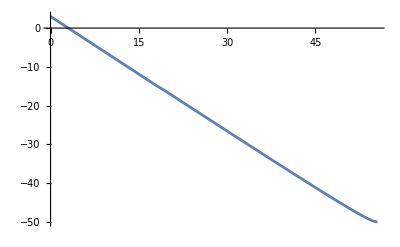

```mathematica
Plot[Log[cs/(kmpc*a[Ne]H[Ne])]/.solNe1,{Ne,0,NeFIN}]
```

```mathematica
Netotal=NeFIN+Nre(*Ntotal=Nend+Nreh*)
```

{61.4743}

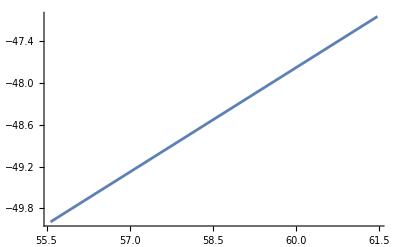

```mathematica
Plot[Log[1/kend[[1]]]+1/2(Ne-NeFIN),{Ne,NeFIN,Netotal[[1]]}]
```

```mathematica
endofinf=Log[cs/(kmpc*a[Ne]H[Ne])]/.solNe1/.Ne->NeFIN (*Log(1/k) at the end of inflation*)
```

{-49.9955}

```mathematica
endofreh=Log[1/kend[[1]]]+1/2(Netotal[[1]]-NeFIN)(*Log(1/k) at the end of reheating (RD start)*)
```

-47.0447

```mathematica
endofrd=endofreh+(100-Netotal[[1]])(*Log(1/k) at the end of RD (MD Start)*)
```

-8.51901

```mathematica
pw=Piecewise[{{Log[cs/(kmpc*(a[Ne]H[Ne])/.solNe1)][[1]],-2<Ne< NeFIN}, 
{endofinf[[1]]+1/2(Ne-NeFIN),NeFIN≤ Ne< Netotal[[1]]},
{endofreh+(Ne-Netotal[[1]]),Netotal[[1]]≤ Ne<100},
{endofrd+ 1/2(Ne-100),100≤ Ne≤130}}]
```

Piecewise[{{Log[(0.000291573 ⅇ^-Ne)/(InterpolatingFunction[…][Ne])], -2<Ne<55.5728}, {-49.9955+1/2 (-55.5728+Ne), 55.5728≤Ne<61.4743}, {-108.519+Ne, 61.4743≤Ne<100}, {-8.51901+1/2 (-100+Ne), 100≤Ne≤130}, {0, True}}]

```mathematica
line1=Line[{{0,-NeFIN},{0,1.2}}];(*Vertucal line at CMB scale*)
line2=Line[{{NeFIN,-NeFIN},{NeFIN,-40}}];(*Vertucal line at Subscript[N, end]*)
line3=Line[{{Netotal[[1]],-NeFIN},{Netotal[[1]],-40}}];(*Vertucal line at the end of reheating (RD start)*)
line4=Line[{{100,-NeFIN},{100,-10}}];(*Vertucal line at the end of RD (MD start)*)
```

```mathematica
kINcmb=Log[1/0.05]
kINpeak=Log[1/kpeak[[1]]]
KINreh=Log[1/kre[[1]]](*critical scale ->  Subscript[k, reh]^-1*)
```

2.99573

-15.7478

-47.0447

```mathematica
Plot[endofinf[[1]]+1/2(Ne-NeFIN),{ Ne,NeFIN, Netotal[[1]]}]
```

-Graphics-

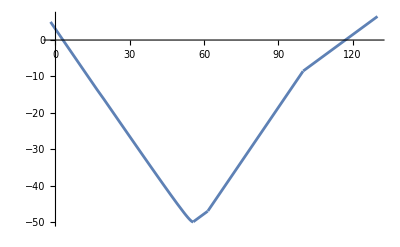

```mathematica
Plot[pw,{Ne,-2,130}]
```

```mathematica
comphi1=Plot[{pw,endofinf[[1]],endofreh,kINcmb,kINpeak,KINreh},{Ne,-2,128},Frame->True,Axes->False,PlotStyle->{{Black,Thickness[0.005]},{Transparent},{Transparent},{Dashing[0.025],Darker[Red]},{Dashing[0.025],Blue}(*,{Dashing[0.025],Blue},{Dashing[0.025],Lighter[Blue]}*),{Dashing[0.025],Darker[Green]}},FrameStyle->Directive[Thickness[0.003]],(*FrameTicks->{{Automatic,None},{None}},*)FrameTicks->{{None,None},{ {{0,"N_*"},{NeFIN,"N_end    "},{NeFIN+Nre[[1]],"       N_reh"},{100,"N_eq"}},None}},Filling->{2->{3}},FillingStyle->{Opacity[0.2,Blue]},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameLabel->{"N=Lna","Comoving Hubble Radius Ln(1/aH)"},Epilog->{Directive[Gray,Dashed],line1,line2,line3,line4,
Text[Style["k_peak^-1",18,FontFamily->"Cambria",Bold,Black],{6.5,-12}],
Text[Style["k_*^-1",18,FontFamily->"Cambria",Bold,Black],{4.65,5.6}],
Text[Style["k_reh^-1",18,FontFamily->"Cambria",Bold,Black],{6.5,-43}],
(*Text[Style["Pivot Scale",10,FontFamily->"Cambria",Black],{2,-19.5},Automatic,{0,6}],*)
(*Text[Style["⟵ End of Inflation",10,FontFamily->"Cambria",Black],{54.9,-17.5},Automatic,{0,6}],*)
Text[Style["reh",15,FontFamily->"Cambria",Black],{58.5,-40},Automatic,{1,0}],
Text[Style[" ⟵——RD——⟶",18,FontFamily->"Cambria",Black],{81,-51},Automatic,{1,0}],
Text[Style[" ⟵—MD—⟶",18,FontFamily->"Cambria",Black],{114,-51},Automatic,{1,0}]},ImageSize->{600,400}]
```

InterpolatingFunction::dmval: Input value {126.929} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {127.297} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {127.688} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
psreh4n=Show[{reh4,Graphics[{Directive[Gray,Dashed],Line[{{-3,-50},{-3,-20}}],Line[{{15.7,-35},{15.7,-4.4}}],Line[{{47.1,-52},{47.1,-25}}]}],Graphics[{Darker[Red],PointSize[0.02],Point[{-3,-20}]}],Graphics[{Darker[Blue],PointSize[0.02],Point[{15.7,-4.4}]}],Graphics[{Darker[Green],PointSize[0.02],Point[{47.1,-25.}]}]}]
```

```mathematica
Export["reh4.eps",psreh4n];
```

```mathematica
cD=Show[{comphi1,Graphics[{Black,PointSize[0.015],Point[{NeFIN,endofinf[[1]]}],Point[{Netotal[[1]],endofreh}],Point[{100,-8.8}]}],
Graphics[{{Darker[Red],PointSize[0.015],
Point[{0.05,kINcmb}],Point[{123.4,kINcmb}]},{Darker[Blue],PointSize[0.015],
Point[{19.,kINpeak}],Point[{93,kINpeak}]},{Darker[Green],PointSize[0.015],
Point[{51.2,KINreh}],Point[{Netotal[[1]],endofreh}]}(*,
Point[{32.75,kINFree}],Point[{79.,kINFree}]*)}](*,Graphics[{Green,Thick,Circle[{43.8,-22.9},0.5]}]*)},Graphics[{Directive[Gray,Dashed](*,Line[{{-3,-50},{-3,-20}}],Line[{{29.6,-40},{29.6,-3.4}}],Line[{{43.8,-50},{43.8,-23}}]*)}]]
```

```mathematica
Export["com-rehD.eps",cD];
```

#### Solving Tensor Mukhanov Sasaki Equation (16)

```mathematica
nPoints=5;
iMax=(NeFIN-.6)*nPoints;
NeHEt=Table[0+i/nPoints,{i,0,iMax}]//N;
NeBDt=Table[NeHEt[[i]]-1(*If[NeHEt[[i]]≤39,NeHEt[[i]]-5,NeHEt[[i]]-1]*),{i,1,iMax}]//N;
NeEndt=Table[(*NeFIN*)(*If[NeHE[[i]]≤31,NeHE[[i]]+3,NeFIN-.7]*)If[NeHEt[[i]]+1≤NeFIN,NeHEt[[i]]-.64,NeFIN],{i,1,iMax}];
kt=Table[(H[Ne]*a[Ne])/.solNe1/.{Ne->NeHEt[[i]]},{i,1,iMax}]//N;
For[i=1,i≤iMax-(iMax-1),i++,
tAux=AbsoluteTime[];
MSsolAuxt[i]=NDSolve[{((ut''[Ne]+(H'[Ne]/H[Ne]+a'[Ne]/a[Ne])ut'[Ne]+(kt[[i]]/(a[Ne] H[Ne]))^2 ut[Ne]-a''[Ne]/a[Ne] ut[Ne]-a'[Ne]/a[Ne](H'[Ne]/H[Ne]+a'[Ne]/a[Ne])ut[Ne])/.solNe1)==0,ut[NeBD[[i]]]==1/(√(2kt[[i]]))/.solNe1/.{Ne->NeBDt[[i]]},ut'[NeBDt[[i]]]==((-I kt[[i]])/(a[Ne] H[Ne] √2 √kt[[i]]))/.solNe1/.{Ne->NeBDt[[i]]}},{ut[Ne]},{Ne,NeBDt[[i]],NeEndt[[i]]},MaxSteps->Infinity(*Method->{"EquationSimplification"->"Solve"}*)(*,WorkingPrecision->30*)][[1]];Print[NeHEt[[i]]//N,"  ",kt[[i]]//N,"  ",AbsoluteTime[]-tAux]]
MSolt=Table[MSsolAuxt[i],{i,1,iMax}];
j=1;
PNt0=Table[{NeHEt[[i]],((j kt[[i]]^3/Pi^2*Abs[(ut[Ne]/.solNe1)/(a[Ne]/.solNe1)]^2)/.MSolt[[i]]/.Ne->NeEndt[[i]])[[1]][[1]]},{i,1,iMax-(iMax-1)}]
```

0.  {0.0000145786}  3.277114

{{0.,5.18927×10^-10}}

```mathematica
Off[NDSolve::precw];
For[i=1,i≤iMax,i++,
tAux=AbsoluteTime[];
MSsolAuxt[i]=NDSolve[{((ut''[Ne]+(H'[Ne]/H[Ne]+a'[Ne]/a[Ne])ut'[Ne]+(kt[[i]]/(a[Ne] H[Ne]))^2 ut[Ne]-a''[Ne]/a[Ne] ut[Ne]-a'[Ne]/a[Ne](H'[Ne]/H[Ne]+a'[Ne]/a[Ne])ut[Ne])/.solNe1)==0,ut[NeBDt[[i]]]==1/(√(2kt[[i]]))/.solNe1/.{Ne->NeBDt[[i]]},ut'[NeBDt[[i]]]==((-I kt[[i]])/(a[Ne] H[Ne] √2 √kt[[i]]))/.solNe1/.{Ne->NeBDt[[i]]}},{ut[Ne]},{Ne,NeBDt[[i]],NeEndt[[i]]},MaxSteps->Infinity(*Method->{"EquationSimplification"->"Solve"}*)(*,WorkingPrecision->30*)][[1]];Print[NeHEt[[i]]//N,"  ",kt[[i]]//N,"  ",AbsoluteTime[]-tAux]]
MSolt=Table[MSsolAuxt[i],{i,1,iMax}];
```

0.  {0.0000145786}  0.01575

0.2  {0.0000177786}  0.

0.4  {0.0000216808}  0.

0.6  {0.0000264394}  0.015593

0.8  {0.0000322423}  0.

1.  {0.0000393186}  0.

1.2  {0.0000479477}  0.01673

1.4  {0.0000584703}  0.002101

1.6  {0.0000713017}  0.01415

1.8  {0.0000869487}  0.

2.  {0.000106029}  0.

2.2  {0.000129295}  0.

2.4  {0.000157666}  0.015006

2.6  {0.000192261}  0.015632

2.8  {0.000234446}  0.

3.  {0.000285885}  0.

3.2  {0.000348609}  0.

3.4  {0.000425092}  0.016251

3.6  {0.000518352}  0.

3.8  {0.000632069}  0.

4.  {0.000770729}  0.015514

4.2  {0.000939802}  0.

4.4  {0.00114596}  0.

4.6  {0.00139733}  0.

4.8  {0.00170383}  0.015644

5.  {0.00207754}  0.0080172

5.2  {0.00253322}  0.

5.4  {0.00308882}  0.0080055

5.6  {0.00376625}  0.

5.8  {0.00459223}  0.

6.  {0.00559932}  0.016277

6.2  {0.00682724}  0.

6.4  {0.00832437}  0.

6.6  {0.0101498}  0.

6.8  {0.0123753}  0.015008

7.  {0.0150888}  0.

7.2  {0.0183972}  0.

7.4  {0.0224308}  0.

7.6  {0.0273486}  0.015644

7.8  {0.0333444}  0.

8.  {0.0406545}  0.

8.2  {0.0495667}  0.

8.4  {0.0604324}  0.016243

8.6  {0.0736794}  0.

8.8  {0.0898296}  0.

9.  {0.109519}  0.

9.2  {0.133524}  0.015521

9.4  {0.162788}  0.

9.6  {0.198465}  0.

9.8  {0.24196}  0.013511

10.  {0.294985}  0.002507

10.2  {0.359627}  0.

10.4  {0.438432}  0.

10.6  {0.534501}  0.

10.8  {0.651616}  0.015632

11.  {0.794387}  0.

11.2  {0.968431}  0.015633

11.4  {1.1806}  0.

11.6  {1.43924}  0.015981

11.8  {1.75453}  0.

12.  {2.13887}  0.

12.2  {2.60738}  0.015533

12.4  {3.17849}  0.

12.6  {3.87467}  0.

12.8  {4.72329}  0.

13.  {5.75772}  0.015807

13.2  {7.01865}  0.

13.4  {8.55564}  0.

13.6  {10.4291}  0.016773

13.8  {12.7127}  0.002625

14.  {15.4962}  0.

14.2  {18.8889}  0.012006

14.4  {23.0242}  0.

14.6  {28.0644}  0.015655

14.8  {34.2077}  0.

15.  {41.6951}  0.

15.2  {50.8205}  0.016309

15.4  {61.942}  0.015007

15.6  {75.4958}  0.

15.8  {92.0135}  0.

16.  {112.142}  0.

16.2  {136.671}  0.015633

16.4  {166.557}  0.

16.6  {202.969}  0.

16.8  {247.327}  0.

17.  {301.358}  0.015633

17.2  {367.159}  0.

17.4  {447.266}  0.010008

17.6  {544.75}  0.0060096

17.8  {663.293}  0.

18.  {807.255}  0.

18.2  {981.534}  0.015643

18.4  {1186.52}  0.

18.6  {1402.91}  0.

18.8  {1674.35}  0.015826

19.  {2013.44}  0.

19.2  {2433.07}  0.

19.4  {2949.03}  0.015895

19.6  {3580.94}  0.

19.8  {4353.09}  0.015633

20.  {5295.26}  0.

20.2  {6443.98}  0.

20.4  {7843.96}  0.015845

20.6  {9549.51}  0.

20.8  {11627.1}  0.

21.  {14157.5}  0.015664

21.2  {17239.2}  0.

21.4  {20992.2}  0.01501

21.6  {25562.5}  0.

21.8  {31128.}  0.

22.  {37905.2}  0.015641

22.2  {46157.7}  0.0086087

22.4  {56206.4}  0.0084856

22.6  {68441.8}  0.

22.8  {83339.6}  0.

23.  {101479.}  0.016001

23.2  {123564.}  0.

23.4  {150453.}  0.015014

23.6  {183190.}  0.0009045

23.8  {223046.}  0.0040052

24.  {271568.}  0.

24.2  {330640.}  0.011005

24.4  {402552.}  0.015661

24.6  {490095.}  0.0006383

24.8  {596664.}  0.015013

25.  {726391.}  0.

25.2  {884306.}  0.

25.4  {1.07653×10^6}  0.016341

25.6  {1.31051×10^6}  0.015625

25.8  {1.5953×10^6}  0.

26.  {1.94194×10^6}  0.015506

26.2  {2.36385×10^6}  0.

26.4  {2.87736×10^6}  0.010506

26.6  {3.50233×10^6}  0.0055184

26.8  {4.26295×10^6}  0.0006355

27.  {5.18862×10^6}  0.

27.2  {6.31515×10^6}  0.

27.4  {7.68605×10^6}  0.015016

27.6  {9.35432×10^6}  0.

27.8  {1.13844×10^7}  0.015644

28.  {1.38547×10^7}  0.

28.2  {1.68606×10^7}  0.01501

28.4  {2.0518×10^7}  0.

28.6  {2.49682×10^7}  0.

28.8  {3.03828×10^7}  0.

29.  {3.69705×10^7}  0.

29.2  {4.49853×10^7}  0.

29.4  {5.4736×10^7}  0.016286

29.6  {6.65984×10^7}  0.

29.8  {8.10291×10^7}  0.016112

30.  {9.85837×10^7}  0.

30.2  {1.19938×10^8}  0.022679

30.4  {1.45913×10^8}  0.0091856

30.6  {1.77508×10^8}  0.

30.8  {2.15937×10^8}  0.015102

31.  {2.62677×10^8}  0.015677

31.2  {3.19524×10^8}  0.

31.4  {3.8866×10^8}  0.

31.6  {4.72739×10^8}  0.

31.8  {5.74986×10^8}  0.015006

32.  {6.99323×10^8}  0.

32.2  {8.50518×10^8}  0.

32.4  {1.03436×10^9}  0.

32.6  {1.2579×10^9}  0.

32.8  {1.52969×10^9}  0.021301

33.  {1.86012×10^9}  0.

33.2  {2.26185×10^9}  0.010013

33.4  {2.75024×10^9}  0.

33.6  {3.34393×10^9}  0.015642

33.8  {4.06562×10^9}  0.

34.  {4.94286×10^9}  0.

34.2  {6.00912×10^9}  0.015623

34.4  {7.30507×10^9}  0.

34.6  {8.88011×10^9}  0.

34.8  {1.07943×10^10}  0.

35.  {1.31204×10^10}  0.015622

35.2  {1.5947×10^10}  0.

35.4  {1.93817×10^10}  0.01598

35.6  {2.35551×10^10}  0.

35.8  {2.86255×10^10}  0.015624

36.  {3.47857×10^10}  0.

36.2  {4.22693×10^10}  0.016014

36.4  {5.13602×10^10}  0.

36.6  {6.24028×10^10}  0.

36.8  {7.58155×10^10}  0.

37.  {9.21058×10^10}  0.016755

37.2  {1.1189×10^11}  0.

37.4  {1.35915×10^11}  0.015011

37.6  {1.6509×10^11}  0.

37.8  {2.00514×10^11}  0.015659

38.  {2.43525×10^11}  0.

38.2  {2.95742×10^11}  0.

38.4  {3.59131×10^11}  0.015828

38.6  {4.36078×10^11}  0.

38.8  {5.29475×10^11}  0.

39.  {6.4283×10^11}  0.

39.2  {7.80396×10^11}  0.015615

39.4  {9.4733×10^11}  0.

39.6  {1.14989×10^12}  0.

39.8  {1.39564×10^12}  0.

40.  {1.69379×10^12}  0.

40.2  {2.05546×10^12}  0.016839

40.4  {2.49414×10^12}  0.

40.6  {3.02619×10^12}  0.

40.8  {3.67141×10^12}  0.

41.  {4.45379×10^12}  0.015034

41.2  {5.40239×10^12}  0.

41.4  {6.55241×10^12}  0.

41.6  {7.94644×10^12}  0.015837

41.8  {9.63607×10^12}  0.

42.  {1.16837×10^13}  0.

42.2  {1.4165×10^13}  0.

42.4  {1.71713×10^13}  0.

42.6  {2.08133×10^13}  0.001654

42.8  {2.52248×10^13}  0.

43.  {3.05676×10^13}  0.

43.2  {3.70373×10^13}  0.

43.4  {4.48705×10^13}  0.

43.6  {5.43532×10^13}  0.

43.8  {6.58308×10^13}  0.

44.  {7.97208×10^13}  0.015633

44.2  {9.65272×10^13}  0.

44.4  {1.16859×10^14}  0.

44.6  {1.4145×10^14}  0.

44.8  {1.71189×10^14}  0.

45.  {2.07145×10^14}  0.

45.2  {2.5061×10^14}  0.0066692

45.4  {3.03139×10^14}  0.

45.6  {3.6661×10^14}  0.

45.8  {4.43283×10^14}  0.0090175

46.  {5.35883×10^14}  0.

46.2  {6.47688×10^14}  0.

46.4  {7.82644×10^14}  0.015881

46.6  {9.45502×10^14}  0.

46.8  {1.14197×10^15}  0.

47.  {1.37892×10^15}  0.

47.2  {1.66459×10^15}  0.015829

47.4  {2.00889×10^15}  0.

47.6  {2.42369×10^15}  0.

47.8  {2.92324×10^15}  0.

48.  {3.52463×10^15}  0.015857

48.2  {4.24832×10^15}  0.

48.4  {5.11881×10^15}  0.

48.6  {6.16539×10^15}  0.

48.8  {7.42305×10^15}  0.0158

49.  {8.93349×10^15}  0.

49.2  {1.07464×10^16}  0.015913

49.4  {1.29212×10^16}  0.

49.6  {1.55283×10^16}  0.012065

49.8  {1.86516×10^16}  0.0047039

50.  {2.23909×10^16}  0.

50.2  {2.68642×10^16}  0.015018

50.4  {3.22105×10^16}  0.

50.6  {3.85937×10^16}  0.

50.8  {4.62074×10^16}  0.01568

51.  {5.5279×10^16}  0.0005937

51.2  {6.60738×10^16}  0.

51.4  {7.89009×10^16}  0.

51.6  {9.412×10^16}  0.

51.8  {1.12148×10^17}  0.017112

52.  {1.33465×10^17}  0.

52.2  {1.58615×10^17}  0.

52.4  {1.88215×10^17}  0.

52.6  {2.22962×10^17}  0.0006412

52.8  {2.63629×10^17}  0.

53.  {3.11051×10^17}  0.

53.2  {3.66116×10^17}  0.015871

53.4  {4.29731×10^17}  0.

53.6  {5.02768×10^17}  0.

53.8  {5.86002×10^17}  0.

54.  {6.7999×10^17}  0.016025

54.2  {7.84857×10^17}  0.

54.4  {8.99976×10^17}  0.

54.6  {1.02353×10^18}  0.

```mathematica
PNt=Table[{NeHEt[[i]],((j kt[[i]]^3/Pi^2*Abs[ut[Ne]/.solNe1]^2/a[Ne]^2)/.MSolt[[i]]/.Ne->NeEndt[[i]])[[1]][[1]]},{i,1,iMax}]
```

{{0.,4.65939×10^-11},{0.2,4.64485×10^-11},{0.4,4.63032×10^-11},{0.6,4.61578×10^-11},{0.8,4.60125×10^-11},{1.,4.58671×10^-11},{1.2,4.57217×10^-11},{1.4,4.55763×10^-11},{1.6,4.54309×10^-11},{1.8,4.52855×10^-11},{2.,4.51401×10^-11},{2.2,4.49947×10^-11},{2.4,4.48493×10^-11},{2.6,4.47038×10^-11},{2.8,4.45584×10^-11},{3.,4.4413×10^-11},{3.2,4.42675×10^-11},{3.4,4.41221×10^-11},{3.6,4.39766×10^-11},{3.8,4.38311×10^-11},{4.,4.36857×10^-11},{4.2,4.35402×10^-11},{4.4,4.33947×10^-11},{4.6,4.32492×10^-11},{4.8,4.31037×10^-11},{5.,4.29582×10^-11},{5.2,4.28127×10^-11},{5.4,4.26672×10^-11},{5.6,4.25216×10^-11},{5.8,4.23761×10^-11},{6.,4.22306×10^-11},{6.2,4.2085×10^-11},{6.4,4.19395×10^-11},{6.6,4.17939×10^-11},{6.8,4.16483×10^-11},{7.,4.15028×10^-11},{7.2,4.13572×10^-11},{7.4,4.12116×10^-11},{7.6,4.1066×10^-11},{7.8,4.09204×10^-11},{8.,4.07748×10^-11},{8.2,4.06292×10^-11},{8.4,4.04836×10^-11},{8.6,4.03379×10^-11},{8.8,4.01923×10^-11},{9.,4.00466×10^-11},{9.2,3.9901×10^-11},{9.4,3.97553×10^-11},{9.6,3.96096×10^-11},{9.8,3.9464×10^-11},{10.,3.93182×10^-11},{10.2,3.91725×10^-11},{10.4,3.90268×10^-11},{10.6,3.8881×10^-11},{10.8,3.87353×10^-11},{11.,3.85895×10^-11},{11.2,3.84437×10^-11},{11.4,3.82978×10^-11},{11.6,3.8152×10^-11},{11.8,3.80061×10^-11},{12.,3.78602×10^-11},{12.2,3.77143×10^-11},{12.4,3.75683×10^-11},{12.6,3.74223×10^-11},{12.8,3.72762×10^-11},{13.,3.71301×10^-11},{13.2,3.6984×10^-11},{13.4,3.68378×10^-11},{13.6,3.66915×10^-11},{13.8,3.65451×10^-11},{14.,3.63986×10^-11},{14.2,3.62519×10^-11},{14.4,3.6105×10^-11},{14.6,3.59578×10^-11},{14.8,3.58104×10^-11},{15.,3.56626×10^-11},{15.2,3.55144×10^-11},{15.4,3.53654×10^-11},{15.6,3.52157×10^-11},{15.8,3.50652×10^-11},{16.,3.49137×10^-11},{16.2,3.47608×10^-11},{16.4,3.46057×10^-11},{16.6,3.4448×10^-11},{16.8,3.42871×10^-11},{17.,3.41222×10^-11},{17.2,3.39517×10^-11},{17.4,3.37731×10^-11},{17.6,3.35831×10^-11},{17.8,3.33756×10^-11},{18.,3.31389×10^-11},{18.2,3.2843×10^-11},{18.4,3.21849×10^-11},{18.6,3.02157×10^-11},{18.8,2.88802×10^-11},{19.,2.80007×10^-11},{19.2,2.73088×10^-11},{19.4,2.6684×10^-11},{19.6,2.64359×10^-11},{19.8,2.62391×10^-11},{20.,2.60597×10^-11},{20.2,2.58898×10^-11},{20.4,2.57263×10^-11},{20.6,2.55667×10^-11},{20.8,2.54102×10^-11},{21.,2.52561×10^-11},{21.2,2.51038×10^-11},{21.4,2.49529×10^-11},{21.6,2.48031×10^-11},{21.8,2.46541×10^-11},{22.,2.4506×10^-11},{22.2,2.43583×10^-11},{22.4,2.42111×10^-11},{22.6,2.40641×10^-11},{22.8,2.39174×10^-11},{23.,2.37707×10^-11},{23.2,2.36242×10^-11},{23.4,2.34778×10^-11},{23.6,2.33314×10^-11},{23.8,2.31851×10^-11},{24.,2.30388×10^-11},{24.2,2.28925×10^-11},{24.4,2.27462×10^-11},{24.6,2.25999×10^-11},{24.8,2.24536×10^-11},{25.,2.23074×10^-11},{25.2,2.21612×10^-11},{25.4,2.20151×10^-11},{25.6,2.1869×10^-11},{25.8,2.17228×10^-11},{26.,2.15767×10^-11},{26.2,2.14306×10^-11},{26.4,2.12844×10^-11},{26.6,2.11382×10^-11},{26.8,2.0992×10^-11},{27.,2.08458×10^-11},{27.2,2.06996×10^-11},{27.4,2.05533×10^-11},{27.6,2.0407×10^-11},{27.8,2.02608×10^-11},{28.,2.01145×10^-11},{28.2,1.99682×10^-11},{28.4,1.9822×10^-11},{28.6,1.96758×10^-11},{28.8,1.95296×10^-11},{29.,1.93835×10^-11},{29.2,1.92373×10^-11},{29.4,1.90912×10^-11},{29.6,1.89451×10^-11},{29.8,1.8799×10^-11},{30.,1.86529×10^-11},{30.2,1.85068×10^-11},{30.4,1.83607×10^-11},{30.6,1.82147×10^-11},{30.8,1.80686×10^-11},{31.,1.79226×10^-11},{31.2,1.77766×10^-11},{31.4,1.76306×10^-11},{31.6,1.74846×10^-11},{31.8,1.73386×10^-11},{32.,1.71927×10^-11},{32.2,1.70468×10^-11},{32.4,1.69009×10^-11},{32.6,1.6755×10^-11},{32.8,1.66092×10^-11},{33.,1.64634×10^-11},{33.2,1.63176×10^-11},{33.4,1.61717×10^-11},{33.6,1.60255×10^-11},{33.8,1.58793×10^-11},{34.,1.57331×10^-11},{34.2,1.55869×10^-11},{34.4,1.54407×10^-11},{34.6,1.52945×10^-11},{34.8,1.51483×10^-11},{35.,1.50021×10^-11},{35.2,1.48559×10^-11},{35.4,1.47097×10^-11},{35.6,1.45636×10^-11},{35.8,1.44174×10^-11},{36.,1.42712×10^-11},{36.2,1.41251×10^-11},{36.4,1.39789×10^-11},{36.6,1.38328×10^-11},{36.8,1.36866×10^-11},{37.,1.35405×10^-11},{37.2,1.33943×10^-11},{37.4,1.32482×10^-11},{37.6,1.3102×10^-11},{37.8,1.29559×10^-11},{38.,1.28098×10^-11},{38.2,1.26637×10^-11},{38.4,1.25176×10^-11},{38.6,1.23715×10^-11},{38.8,1.22255×10^-11},{39.,1.20794×10^-11},{39.2,1.19334×10^-11},{39.4,1.17873×10^-11},{39.6,1.16413×10^-11},{39.8,1.14953×10^-11},{40.,1.13493×10^-11},{40.2,1.12033×10^-11},{40.4,1.10573×10^-11},{40.6,1.09113×10^-11},{40.8,1.07654×10^-11},{41.,1.06195×10^-11},{41.2,1.04736×10^-11},{41.4,1.03277×10^-11},{41.6,1.01818×10^-11},{41.8,1.00359×10^-11},{42.,9.89009×10^-12},{42.2,9.74426×10^-12},{42.4,9.60314×10^-12},{42.6,9.45727×10^-12},{42.8,9.3114×10^-12},{43.,9.16555×10^-12},{43.2,9.01971×10^-12},{43.4,8.87388×10^-12},{43.6,8.72807×10^-12},{43.8,8.58203×10^-12},{44.,8.43653×10^-12},{44.2,8.29054×10^-12},{44.4,8.14509×10^-12},{44.6,7.99941×10^-12},{44.8,7.85377×10^-12},{45.,7.70793×10^-12},{45.2,7.56238×10^-12},{45.4,7.41688×10^-12},{45.6,7.27165×10^-12},{45.8,7.12627×10^-12},{46.,6.98093×10^-12},{46.2,6.83564×10^-12},{46.4,6.69038×10^-12},{46.6,6.54517×10^-12},{46.8,6.4×10^-12},{47.,6.2549×10^-12},{47.2,6.10985×10^-12},{47.4,5.96483×10^-12},{47.6,5.81984×10^-12},{47.8,5.67474×10^-12},{48.,5.53×10^-12},{48.2,5.38521×10^-12},{48.4,5.24052×10^-12},{48.6,5.09595×10^-12},{48.8,4.9515×10^-12},{49.,4.80708×10^-12},{49.2,4.66269×10^-12},{49.4,4.51822×10^-12},{49.6,4.37405×10^-12},{49.8,4.22993×10^-12},{50.,4.08596×10^-12},{50.2,3.94248×10^-12},{50.4,3.79904×10^-12},{50.6,3.6557×10^-12},{50.8,3.51253×10^-12},{51.,3.36957×10^-12},{51.2,3.22675×10^-12},{51.4,3.08397×10^-12},{51.6,2.9415×10^-12},{51.8,2.79922×10^-12},{52.,2.65716×10^-12},{52.2,2.51546×10^-12},{52.4,2.37394×10^-12},{52.6,2.23281×10^-12},{52.8,2.09214×10^-12},{53.,1.95204×10^-12},{53.2,1.81245×10^-12},{53.4,1.67348×10^-12},{53.6,1.53512×10^-12},{53.8,1.39761×10^-12},{54.,1.2611×10^-12},{54.2,1.12576×10^-12},{54.4,9.91817×10^-13},{54.6,2.2912×10^-13}}

```mathematica
PNt[[1,2]]/PN0[[1,2]]
```

0.0190014

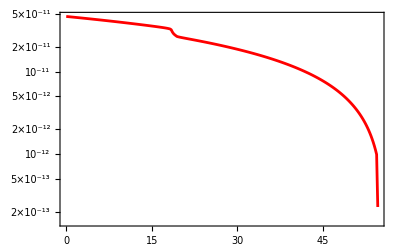

```mathematica
ListLogPlot[PNt(*,PlotRange->{{0,60},{3*10^-13,2*10^-11}}*),Joined->True,Frame->True,PlotStyle->Red]
```

```mathematica
kmpct=Solve[0.002/Mpct==(a[Ne] H[Ne])/.solNe1/.Ne->0,Mpct][[1]][[1,2]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

137.187

```mathematica
Pkt=Table[{(kmpct(H[Ne]a[Ne])/.solNe1/.{Ne->NeHEt[[i]]})[[1]],(j kt[[i]]^3/Pi^2*Abs[(ut[Ne]/.solNe1)/(a[Ne]/.solNe1)]^2/.MSolt[[i]]/.Ne->NeEndt[[i]])[[1]][[1]]},{i,1,iMax}]
```

{{0.002,4.65939×10^-11},{0.00243899,4.64485×10^-11},{0.00297433,4.63032×10^-11},{0.00362715,4.61578×10^-11},{0.00442323,4.60125×10^-11},{0.005394,4.58671×10^-11},{0.0065778,4.57217×10^-11},{0.00802136,4.55763×10^-11},{0.00978167,4.54309×10^-11},{0.0119282,4.52855×10^-11},{0.0145458,4.51401×10^-11},{0.0177376,4.49947×10^-11},{0.0216297,4.48493×10^-11},{0.0263757,4.47038×10^-11},{0.032163,4.45584×10^-11},{0.0392198,4.4413×10^-11},{0.0478247,4.42675×10^-11},{0.0583171,4.41221×10^-11},{0.0711112,4.39766×10^-11},{0.0867117,4.38311×10^-11},{0.105734,4.36857×10^-11},{0.128929,4.35402×10^-11},{0.15721,4.33947×10^-11},{0.191695,4.32492×10^-11},{0.233743,4.31037×10^-11},{0.285012,4.29582×10^-11},{0.347524,4.28127×10^-11},{0.423745,4.26672×10^-11},{0.516681,4.25216×10^-11},{0.629994,4.23761×10^-11},{0.768155,4.22306×10^-11},{0.936608,4.2085×10^-11},{1.142,4.19395×10^-11},{1.39242,4.17939×10^-11},{1.69774,4.16483×10^-11},{2.06999,4.15028×10^-11},{2.52386,4.13572×10^-11},{3.07722,4.12116×10^-11},{3.75188,4.1066×10^-11},{4.57442,4.09204×10^-11},{5.57726,4.07748×10^-11},{6.79991,4.06292×10^-11},{8.29054,4.04836×10^-11},{10.1079,4.03379×10^-11},{12.3235,4.01923×10^-11},{15.0246,4.00466×10^-11},{18.3177,3.9901×10^-11},{22.3324,3.97553×10^-11},{27.2269,3.96096×10^-11},{33.1938,3.9464×10^-11},{40.4681,3.93182×10^-11},{49.3361,3.91725×10^-11},{60.1471,3.90268×10^-11},{73.3266,3.8881×10^-11},{89.3932,3.87353×10^-11},{108.98,3.85895×10^-11},{132.856,3.84437×10^-11},{161.963,3.82978×10^-11},{197.445,3.8152×10^-11},{240.698,3.80061×10^-11},{293.425,3.78602×10^-11},{357.699,3.77143×10^-11},{436.048,3.75683×10^-11},{531.555,3.74223×10^-11},{647.974,3.72762×10^-11},{789.885,3.71301×10^-11},{962.868,3.6984×10^-11},{1173.72,3.68378×10^-11},{1430.74,3.66915×10^-11},{1744.02,3.65451×10^-11},{2125.88,3.63986×10^-11},{2591.31,3.62519×10^-11},{3158.62,3.6105×10^-11},{3850.08,3.59578×10^-11},{4692.85,3.58104×10^-11},{5720.02,3.56626×10^-11},{6971.91,3.55144×10^-11},{8497.64,3.53654×10^-11},{10357.,3.52157×10^-11},{12623.1,3.50652×10^-11},{15384.5,3.49137×10^-11},{18749.5,3.47608×10^-11},{22849.5,3.46057×10^-11},{27844.8,3.4448×10^-11},{33930.1,3.42871×10^-11},{41342.5,3.41222×10^-11},{50369.4,3.39517×10^-11},{61359.1,3.37731×10^-11},{74732.6,3.35831×10^-11},{90995.2,3.33756×10^-11},{110745.,3.31389×10^-11},{134654.,3.2843×10^-11},{162775.,3.21849×10^-11},{192460.,3.02157×10^-11},{229699.,2.88802×10^-11},{276217.,2.80007×10^-11},{333786.,2.73088×10^-11},{404569.,2.6684×10^-11},{491259.,2.64359×10^-11},{597188.,2.62391×10^-11},{726441.,2.60597×10^-11},{884031.,2.58898×10^-11},{1.07609×10^6,2.57263×10^-11},{1.31007×10^6,2.55667×10^-11},{1.59508×10^6,2.54102×10^-11},{1.94222×10^6,2.52561×10^-11},{2.36499×10^6,2.51038×10^-11},{2.87985×10^6,2.49529×10^-11},{3.50684×10^6,2.48031×10^-11},{4.27036×10^6,2.46541×10^-11},{5.2001×10^6,2.4506×10^-11},{6.33223×10^6,2.43583×10^-11},{7.71078×10^6,2.42111×10^-11},{9.38933×10^6,2.40641×10^-11},{1.14331×10^7,2.39174×10^-11},{1.39216×10^7,2.37707×10^-11},{1.69513×10^7,2.36242×10^-11},{2.06402×10^7,2.34778×10^-11},{2.51313×10^7,2.33314×10^-11},{3.0599×10^7,2.31851×10^-11},{3.72556×10^7,2.30388×10^-11},{4.53595×10^7,2.28925×10^-11},{5.52249×10^7,2.27462×10^-11},{6.72347×10^7,2.25999×10^-11},{8.18546×10^7,2.24536×10^-11},{9.96514×10^7,2.23074×10^-11},{1.21315×10^8,2.21612×10^-11},{1.47686×10^8,2.20151×10^-11},{1.79784×10^8,2.1869×10^-11},{2.18855×10^8,2.17228×10^-11},{2.6641×10^8,2.15767×10^-11},{3.2429×10^8,2.14306×10^-11},{3.94736×10^8,2.12844×10^-11},{4.80474×10^8,2.11382×10^-11},{5.84821×10^8,2.0992×10^-11},{7.11812×10^8,2.08458×10^-11},{8.66356×10^8,2.06996×10^-11},{1.05443×10^9,2.05533×10^-11},{1.28329×10^9,2.0407×10^-11},{1.56179×10^9,2.02608×10^-11},{1.90069×10^9,2.01145×10^-11},{2.31305×10^9,1.99682×10^-11},{2.81481×10^9,1.9822×10^-11},{3.42532×10^9,1.96758×10^-11},{4.16812×10^9,1.95296×10^-11},{5.07187×10^9,1.93835×10^-11},{6.1714×10^9,1.92373×10^-11},{7.50908×10^9,1.90912×10^-11},{9.13643×10^9,1.89451×10^-11},{1.11161×10^10,1.8799×10^-11},{1.35244×10^10,1.86529×10^-11},{1.64539×10^10,1.85068×10^-11},{2.00173×10^10,1.83607×10^-11},{2.43518×10^10,1.82147×10^-11},{2.96237×10^10,1.80686×10^-11},{3.60359×10^10,1.79226×10^-11},{4.38345×10^10,1.77766×10^-11},{5.33191×10^10,1.76306×10^-11},{6.48536×10^10,1.74846×10^-11},{7.88806×10^10,1.73386×10^-11},{9.59381×10^10,1.71927×10^-11},{1.1668×10^11,1.70468×10^-11},{1.41901×10^11,1.69009×10^-11},{1.72567×10^11,1.6755×10^-11},{2.09853×10^11,1.66092×10^-11},{2.55185×10^11,1.64634×10^-11},{3.10297×10^11,1.63176×10^-11},{3.77297×10^11,1.61717×10^-11},{4.58744×10^11,1.60255×10^-11},{5.57751×10^11,1.58793×10^-11},{6.78096×10^11,1.57331×10^-11},{8.24373×10^11,1.55869×10^-11},{1.00216×10^12,1.54407×10^-11},{1.21824×10^12,1.52945×10^-11},{1.48083×10^12,1.51483×10^-11},{1.79995×10^12,1.50021×10^-11},{2.18773×10^12,1.48559×10^-11},{2.65892×10^12,1.47097×10^-11},{3.23145×10^12,1.45636×10^-11},{3.92705×10^12,1.44174×10^-11},{4.77215×10^12,1.42712×10^-11},{5.7988×10^12,1.41251×10^-11},{7.04595×10^12,1.39789×10^-11},{8.56086×10^12,1.38328×10^-11},{1.04009×10^13,1.36866×10^-11},{1.26357×10^13,1.35405×10^-11},{1.53498×10^13,1.33943×10^-11},{1.86458×10^13,1.32482×10^-11},{2.26482×10^13,1.3102×10^-11},{2.7508×10^13,1.29559×10^-11},{3.34084×10^13,1.28098×10^-11},{4.05719×10^13,1.26637×10^-11},{4.92681×10^13,1.25176×10^-11},{5.98243×10^13,1.23715×10^-11},{7.26371×10^13,1.22255×10^-11},{8.81879×10^13,1.20794×10^-11},{1.0706×10^14,1.19334×10^-11},{1.29961×10^14,1.17873×10^-11},{1.57749×10^14,1.16413×10^-11},{1.91464×10^14,1.14953×10^-11},{2.32366×10^14,1.13493×10^-11},{2.81982×10^14,1.12033×10^-11},{3.42164×10^14,1.10573×10^-11},{4.15154×10^14,1.09113×10^-11},{5.03669×10^14,1.07654×10^-11},{6.11002×10^14,1.06195×10^-11},{7.41138×10^14,1.04736×10^-11},{8.98905×10^14,1.03277×10^-11},{1.09015×10^15,1.01818×10^-11},{1.32194×10^15,1.00359×10^-11},{1.60286×10^15,9.89009×10^-12},{1.94326×10^15,9.74426×10^-12},{2.35569×10^15,9.60314×10^-12},{2.85532×10^15,9.45727×10^-12},{3.46051×10^15,9.3114×10^-12},{4.19347×10^15,9.16555×10^-12},{5.08104×10^15,9.01971×10^-12},{6.15566×10^15,8.87388×10^-12},{7.45656×10^15,8.72807×10^-12},{9.03114×10^15,8.58203×10^-12},{1.09367×10^16,8.43653×10^-12},{1.32423×10^16,8.29054×10^-12},{1.60315×10^16,8.14509×10^-12},{1.94052×10^16,7.99941×10^-12},{2.3485×10^16,7.85377×10^-12},{2.84177×10^16,7.70793×10^-12},{3.43804×10^16,7.56238×10^-12},{4.15867×10^16,7.41688×10^-12},{5.02941×10^16,7.27165×10^-12},{6.08127×10^16,7.12627×10^-12},{7.35162×10^16,6.98093×10^-12},{8.88543×10^16,6.83564×10^-12},{1.07369×10^17,6.69038×10^-12},{1.29711×10^17,6.54517×10^-12},{1.56664×10^17,6.4×10^-12},{1.8917×10^17,6.2549×10^-12},{2.28361×10^17,6.10985×10^-12},{2.75594×10^17,5.96483×10^-12},{3.32499×10^17,5.81984×10^-12},{4.01031×10^17,5.67474×10^-12},{4.83534×10^17,5.53×10^-12},{5.82815×10^17,5.38521×10^-12},{7.02235×10^17,5.24052×10^-12},{8.45811×10^17,5.09595×10^-12},{1.01835×10^18,4.9515×10^-12},{1.22556×10^18,4.80708×10^-12},{1.47427×10^18,4.66269×10^-12},{1.77262×10^18,4.51822×10^-12},{2.13028×10^18,4.37405×10^-12},{2.55876×10^18,4.22993×10^-12},{3.07174×10^18,4.08596×10^-12},{3.68542×10^18,3.94248×10^-12},{4.41887×10^18,3.79904×10^-12},{5.29456×10^18,3.6557×10^-12},{6.33906×10^18,3.51253×10^-12},{7.58356×10^18,3.36957×10^-12},{9.06446×10^18,3.22675×10^-12},{1.08242×10^19,3.08397×10^-12},{1.2912×10^19,2.9415×10^-12},{1.53853×10^19,2.79922×10^-12},{1.83097×10^19,2.65716×10^-12},{2.17599×10^19,2.51546×10^-12},{2.58207×10^19,2.37394×10^-12},{3.05875×10^19,2.23281×10^-12},{3.61665×10^19,2.09214×10^-12},{4.26722×10^19,1.95204×10^-12},{5.02263×10^19,1.81245×10^-12},{5.89535×10^19,1.67348×10^-12},{6.89732×10^19,1.53512×10^-12},{8.03918×10^19,1.39761×10^-12},{9.32859×10^19,1.2611×10^-12},{1.07672×10^20,1.12576×10^-12},{1.23465×10^20,9.91817×10^-13},{1.40415×10^20,2.2912×10^-13}}

```mathematica
ct=Interpolation[Pkt,InterpolationOrder->1]
AAt=LogLogPlot[{ct[x]},{x,0.002,4*^20}(*,PlotRange->{{0.001,4*10^22},{10^-12,1}}*),Frame->True,FrameStyle->Thick,FrameTicksStyle->Black,PlotStyle->{Purple},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],ImageSize->{600,400},AspectRatio->Full,RotateLabel->True,Axes->False,FrameLabel->{"k/Mpc^-1","P_t"}]
```

InterpolatingFunction[…]

```mathematica
InterpolatingFunction[…];
```

```mathematica
ct[0.05kmpct]
```

4.06234×10^-11

```mathematica
c1[0.05kmpc]
```

2.00331×10^-9

```mathematica
ct[0.05kmpct]/(c1[0.05kmpc](*2.1*10^-9*))
```

0.0202782

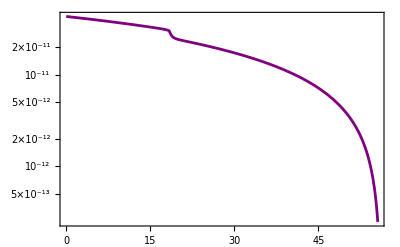

```mathematica
LogPlot[(2 H[Ne]^2/.solNe1)/Pi^2,{Ne,0,NeFIN},PlotRange->All,Frame->True,PlotStyle->Purple]
```

```mathematica
(((2 H[Ne]^2/.solNe1)/Pi^2)[[1]]/.Ne->0)/(c1[0.05kmpc](*2.1*10^-9*))
```

0.0214989

## Case F

```mathematica
Clear["Global`*"]
Remove["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ϵ1[Ne_]:=-H'[Ne]/H[Ne]
ϵ2[Ne_]:=-(H[Ne] (H'[Ne]^2/H[Ne]^2-H''[Ne]/H[Ne]))/H'[Ne]
```

```mathematica
V[ϕ_]:=Λ^4(1+Cos[ϕ/f])
ϵ[ϕ_]:=w(Cosh[(ϕ-ϕc)/b])^-2
M[ϕ_]:=M0(1+ϵ[ϕ])
```

#### Solving Background Equations (6)&(9)

```mathematica
Off[NDSolve::precw];
ϕ0=5.53327945289528760424702860706861791151`29.518687405708878;
dϕ0=0.0052583177533965574057692244440840616889231016307249570077`26.83391284890734;
w=1.4385*10^1;
b=1.2*10^-2;
ϕc=5.86;
Λ=1.``15*10^-2;
α=20.;
M0=2.46``15*10^-4;
f=2.``15;
cs=1/(√(2α-1));
(*Plot[M'[ϕ]/M[ϕ],{ϕ,-20,20},PlotRange->All]*)
solNe1=NDSolve[{H[Ne]H'[Ne]==-α H[Ne]^2 ϕ'[Ne]^2/2(H[Ne]^2 ϕ'[Ne]^2/(2 M[ϕ[Ne]]^4))^(α-1),ϕ''[Ne]==-(3/(2α-1)-ϵ1[Ne])ϕ'[Ne]-(V'[ϕ[Ne]]/V[ϕ[Ne]])((3α-(2α-1)ϵ1[Ne])/(α(2α-1)))ϕ'[Ne]^2/(2ϵ1[Ne])+(2(α-1))/α M'[ϕ[Ne]]/M[ϕ[Ne]] ϕ'[Ne]^2,ϕ[-6]==ϕ0,H[-6]==√(V[ϕ[-6]]/3),ϕ'[-6]==dϕ0},{ϕ,H},{Ne,-6``15,65``15},Method->{"EquationSimplification"->"Residual"},AccuracyGoal->6.2356,PrecisionGoal->30.]
NeFIN=FindRoot[(ϵ1[Ne]/.solNe1)==1,{Ne,50}]
NeFIN=NeFIN[[1,2]];
phi=Plot[ϕ[Ne]/.solNe1,{Ne,0,NeFIN},PlotRange->{{-1.,58},{5.4,6.3}},Frame->True,FrameLabel->{"N","ϕ/M_P"},PlotStyle->{Brown},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],ImageSize->{600,400},RotateLabel->True,FrameStyle->Thick,FrameTicksStyle->Black(*,PlotLegends->{Placed[LineLegend[{{Red},{Darker[Green]},Darker[Blue],Purple},{"Case A","Case B ","Case C","Case D"},LabelStyle->{14,FontFamily->"Cambria"},LegendLayout->"Column",LegendMarkerSize->{{30,20}}],{0.22,0.72}]}*)]
LogPlot[{ϵ1[Ne]/.solNe1,1},{Ne,0,NeFIN},PlotRange->{{0,57.},{0.005,1.2}},Frame->True,FrameLabel->{"N","ε_1"},PlotStyle->{Brown,Orange},ImageSize->{600,400},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameStyle->Thick,FrameTicksStyle->Black,ImageSize->{600,400},RotateLabel->True(*,PlotLegends->{Placed[LineLegend[{{Red},{Darker[Green]},Darker[Blue],Purple},{"Case A","Case B ","Case C","Case D"},LabelStyle->{14,FontFamily->"Cambria"},LegendLayout->"Column",LegendMarkerSize->{{30,20}}],{0.12,.72}]}*)]
Plot[V[ϕ]/Λ^4,{ϕ,0,0.013},PlotRange->All,Frame->True,FrameLabel->{"ϕ","V[ϕ]/Λ^4"},
LabelStyle->Directive[15,Bold,Black,FontFamily->"Book Antiqua"],PlotStyle->Red]
Plot[ϵ[ϕ],{ϕ,4,6.5},PlotRange->All,Frame->True,PlotStyle->Red]
Plot[M[ϕ],{ϕ,4,6.5},PlotRange->All,Frame->True,PlotStyle->Red]
NeIN=0;
```

Power::infy: Infinite expression 1/0. encountered.

NDSolve::nlnum: The function value {4.98194×10^-15,0.,ComplexInfinity} is not a list of numbers with dimensions {3} at {Ne,H[Ne],ϕ[Ne],ϕ'[Ne],H'[Ne],ϕ'[Ne],ϕ''[Ne]} = {-6.,0.0000152179,5.53328,0.00525832,0.,0.00525832,0.}.

NDSolve::ndsz: At Ne == 51.4279, step size is effectively zero; singularity or stiff system suspected.

{{ϕ→InterpolatingFunction[…],H→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {51.9234} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {51.4846} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{Ne→50.8546}

```mathematica
r[Ne_]:=First[Evaluate[16cs ϵ1[Ne]/.solNe1]]
ns[Ne_]:=First[Evaluate[1-2ϵ1[Ne]-ϵ2[Ne]/.solNe1]]
r[0]
ns[0]
```

0.0226172

0.964424

```mathematica
PN=ParametricPlot[{{ns[Ne],r[Ne]}},{Ne,-.05,0},PlotRange->{{0.945,1},{0,.261}},Frame-> True,FrameLabel->{"n_s","r"},ImageSize->{400,300},AspectRatio->Full,PlotStyle->{{Purple,Thickness[0.01]}}]
rns0=-Graphics-;
prns0=Show[{ParametricPlot[{ns0[Ne],r0[Ne]},{Ne,50,60},PlotRange->{{0.945,1},{0,0.261}},PlotStyle->{Black,Thickness[0.005]},Frame-> True,FrameLabel->{"n_s","r"},ImageSize->{700,400},AspectRatio->Full,PlotLegends->{Placed[SwatchLegend[{Gray,Red,Blue},{"TT,TE,EE+lowE+lensing ","TT,TE,EE+lowE+lensing +BK14 ","TT,TE,EE+lowE+lensing +BK14+BAO "},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}}],{1,0.92}](*,Placed[LineLegend[{Yellow},{"ϕ^2"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.83}],Placed[LineLegend[{Directive[Dashed,Yellow],Yellow},{"α-attractor N_*=50","α-attractor N_*=60"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.60}],Placed[LineLegend[{Directive[Dashed,Blue],Blue},{"α-attractor(G-I)   M=10^6","α-attractor(G-I)   M=10^6"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.45}],Placed[LineLegend[{Directive[Dashed,Black],Black},{"α-attractor(G-I)   M=10^-3","α-attractor(G-I)   M=10^-3"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.25}],Placed[PointLegend[{Directive[Black,AbsolutePointSize[6]],Directive[Black,AbsolutePointSize[8]]},{"N_*=50","N_*=60"},LabelStyle->10,LegendLayout->"Column"],{1.025,0.12}]*)}],Graphics[{Texture[rns0],EdgeForm[Black],Polygon[{{0.945,0},{1,0},{1,0.261},{0.945,0.261}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},ImageSize->{400,300},AspectRatio->Full]}]
Show[prns0,PN]
```

```mathematica
PN=ParametricPlot[{{ns[Ne],r[Ne]}},{Ne,-.1,0},PlotRange->{{0.93,1},{0,.1}},Frame-> True,FrameLabel->{"n_s","r"},ImageSize->{400,300},AspectRatio->Full,PlotStyle->{{Purple,Thickness[0.01]}}]
rns0=-Graphics-;
prns0=Show[{ParametricPlot[{ns0[Ne],r0[Ne]},{Ne,50,60},PlotRange->{{0.93,1},{0,0.20}},PlotStyle->{Black,Thickness[0.005]},Frame-> True,FrameLabel->{"n_s","r"},ImageSize->{700,400},AspectRatio->Full,PlotLegends->{Placed[SwatchLegend[{Gray,Red,Blue},{"TT,TE,EE+lowE+lensing ","TT,TE,EE+lowE+lensing +BK14 ","TT,TE,EE+lowE+lensing +BK14+BAO "},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}}],{1,0.92}],Placed[LineLegend[{Yellow},{"ϕ^2"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.83}],Placed[LineLegend[{Directive[Dashed,Yellow],Yellow},{"α-attractor N_*=50","α-attractor N_*=60"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.60}],Placed[LineLegend[{Directive[Dashed,Blue],Blue},{"α-attractor(G-I)   M=10^6","α-attractor(G-I)   M=10^6"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.45}],Placed[LineLegend[{Directive[Dashed,Black],Black},{"α-attractor(G-I)   M=10^-3","α-attractor(G-I)   M=10^-3"},LabelStyle->10,LegendLayout->"Column",LegendMarkerSize->{{30,10}} ],{1,0.25}],Placed[PointLegend[{Directive[Black,AbsolutePointSize[6]],Directive[Black,AbsolutePointSize[8]]},{"N_*=50","N_*=60"},LabelStyle->10,LegendLayout->"Column"],{1.025,0.12}]}],Graphics[{Texture[rns0],EdgeForm[Black],Polygon[{{0.93,0},{1,0},{1,0.2},{0.93,0.2}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},ImageSize->{400,300},AspectRatio->Full]}]
Show[prns0,PN]
```

```mathematica
Plot[{(Abs[ϕ[Ne]-ϕ[NeFIN]])/.solNe1},{Ne,-6,NeFIN},PlotRange->{{0,50},{0,.8}},FrameLabel->{"N","Δϕ/M_P"},Frame->True,Frame->True,PlotStyle->{Brown},ImageSize->{600,400},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameStyle->Thick,FrameTicksStyle->Black,ImageSize->{600,400},RotateLabel->True(*,PlotLegends->{Placed[LineLegend[{{Red},{Darker[Green]},Blue,Purple},{"Case A","Case B ","Case C","Case D"},LabelStyle->{14,FontFamily->"Cambria"},LegendLayout->"Column",LegendMarkerSize->{{30,20}}],{0.12,0.25}]}*)]
Plot[{Abs[V'[ϕ[Ne]]/V[ϕ[Ne]]]/.solNe1,1},{Ne,0,NeFIN},PlotRange->{{0,57},{0,18}},FrameLabel->{"N","M_pV_(,ϕ)/V"},Frame->True,PlotStyle->{Brown,Orange},ImageSize->{600,400},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameStyle->Thick,FrameTicksStyle->Black,ImageSize->{600,400},RotateLabel->True(*,PlotLegends->{Placed[LineLegend[{{Red},{Darker[Green]},Blue,Purple},{"Case A","Case B ","Case C","Case D"},LabelStyle->{14,FontFamily->"Cambria"},LegendLayout->"Column",LegendMarkerSize->{{30,20}}],{0.12,0.5}]}*)]
Plot[{ϵ2[Ne]/.solNe1,1},{Ne,-6,NeFIN},PlotRange->{{0,57},{-3,7}},FrameLabel->{"N","ε_2"},Frame->True,Frame->True,PlotStyle->{Brown,Orange},ImageSize->{600,400},WorkingPrecision->30,LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameStyle->Thick,FrameTicksStyle->Black,ImageSize->{600,400},RotateLabel->True(*,PlotLegends->{Placed[LineLegend[{{Red},{Darker[Green]},Blue,Purple},{"Case A","Case B ","Case C","Case D"},LabelStyle->{14,FontFamily->"Cambria"},LegendLayout->"Column",LegendMarkerSize->{{30,20}}],{0.12,0.7}]}*)]
Plot[ϕ''[Ne]/.solNe1,{Ne,-6,NeFIN},PlotRange->All,FrameLabel->{"Ne","ϕ''[Ne]"},Frame->True]
Plot[ϕ'[Ne]/.solNe1,{Ne,0,NeFIN},FrameLabel->{"N","ϕ_(,N)/M_P"},Frame->True,PlotRange->{{0,57},{0.001,.1}},PlotStyle->{Brown},ImageSize->{600,400},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameStyle->Thick,FrameTicksStyle->Black,ImageSize->{600,400},RotateLabel->True(*,PlotLegends->{Placed[LineLegend[{{Red},{Darker[Green]},Blue,Purple},{"Case A","Case B ","Case C","Case D"},LabelStyle->{14,FontFamily->"Cambria"},LegendLayout->"Column",LegendMarkerSize->{{30,20}}],{0.12,0.6}]}*)]
LogPlot[(*10^5*)H[Ne]/.solNe1,{Ne,0,NeFIN},PlotRange->All,FrameLabel->{"N","H/M_P"},Frame->True,PlotRange->{{0,58},{9*10^-7,2*10^-5}},PlotStyle->{Brown},ImageSize->{600,400},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameStyle->Thick,FrameTicksStyle->Black,ImageSize->{600,400},RotateLabel->True(*,PlotLegends->{Placed[LineLegend[{{Red},{Darker[Green]},Blue,Purple},{"Case A","Case B ","Case C","Case D"},LabelStyle->{14,FontFamily->"Cambria"},LegendLayout->"Column",LegendMarkerSize->{{30,20}}],{0.16,0.4}]}*)]
Plot[H'[Ne]/.solNe1,{Ne,-5,NeFIN},PlotRange->All,FrameLabel->{"Ne","H'[Ne]"},Frame->True]
```

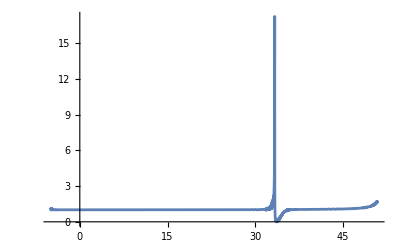

{0.829913}

{z2[0]}

```mathematica
cs=√(1/(2α-1));
a[Ne_]:=Exp[Ne];
z[Ne_]:=(a[Ne]ϕ'[Ne])/cs √(α ((H[Ne]^2 ϕ'[Ne]^2)/(2 M[ϕ[Ne]]^4))^(α-1))
(*z[Ne_]:=a[Ne]/cs √(2ϵ1[Ne])*)
Plot[z'[Ne]/z[Ne]/.solNe1,{Ne,-5,NeFIN},PlotRange->All]
z[Ne]/.solNe1/.Ne->0
z2[Ne]/.solNe1/.Ne->0
```

```mathematica
Plot[{(ϕ'[Ne] √(α ((H[Ne]^2 ϕ'[Ne]^2)/(2 M[ϕ[Ne]]^4))^(α-1)))/.solNe1,√(2ϵ1[Ne])/.solNe1},{Ne,0,NeFIN},Frame->True,PlotRange->All,PlotStyle->{ Green,{Dashed,Red}}]
```

#### Solving Scalar Mukhanov Sasaki Equation (10)

```mathematica
nPoints=5;
iMax=(NeFIN-.3)*nPoints;
NeHE=Table[0+i/nPoints,{i,0,iMax}]//N;
NeBD=Table[NeHE[[i]]-5,{i,1,iMax}]//N;
NeEnd=Table[(*NeFIN*)(*If[NeHE[[i]]≤31,NeHE[[i]]+3,NeFIN-.7]*)If[NeHE[[i]]+1≤NeFIN,NeHE[[i]]+1,NeFIN],{i,1,iMax}];
k=Table[((H[Ne]*a[Ne])/cs)/.solNe1/.{Ne->NeHE[[i]]},{i,1,iMax}]//N;
For[i=1,i≤iMax-(iMax-1),i++,
tAux=AbsoluteTime[];
MSsolAux[i]=NDSolve[{((u''[Ne]+(H'[Ne]/H[Ne]+a'[Ne]/a[Ne])u'[Ne]+((cs k[[i]])/(a[Ne] H[Ne]))^2 u[Ne]-z''[Ne]/z[Ne] u[Ne]-z'[Ne]/z[Ne](H'[Ne]/H[Ne]+a'[Ne]/a[Ne])u[Ne])/.solNe1)==0,u[NeBD[[i]]]==1/(√(2k[[i]] cs))/.solNe1/.{Ne->NeBD[[i]]},u'[NeBD[[i]]]==((-2I k[[i]] cs^2)/(a[Ne] H[Ne]2 √2 √k[[i]] cs^(3/2)))/.solNe1/.{Ne->NeBD[[i]]}},{u[Ne]},{Ne,NeBD[[i]],NeEnd[[i]]},MaxSteps->Infinity(*Method->{"EquationSimplification"->"Solve"}*)(*,WorkingPrecision->30*)][[1]];Print[NeHE[[i]]//N,"  ",k[[i]]//N,"  ",AbsoluteTime[]-tAux]]
MSol=Table[MSsolAux[i],{i,1,iMax}];
PN0=Table[{NeHE[[i]],((k[[i]]^3/(2*Pi^2)*Abs[(u[Ne]/.solNe1)/(z[Ne]/.solNe1)]^2)/.MSol[[i]]/.Ne->NeEnd[[i]])[[1]][[1]]},{i,1,iMax-(iMax-1)}]
```

0.  {0.0000906167}  0.377922

{{0.,2.1639×10^-9}}

```mathematica
Off[NDSolve::precw];
For[i=1,i≤iMax,i++,
tAux=AbsoluteTime[];
MSsolAux[i]=NDSolve[{((u''[Ne]+(H'[Ne]/H[Ne]+a'[Ne]/a[Ne])u'[Ne]+((cs k[[i]])/(a[Ne] H[Ne]))^2 u[Ne]-z''[Ne]/z[Ne] u[Ne]-z'[Ne]/z[Ne](H'[Ne]/H[Ne]+a'[Ne]/a[Ne])u[Ne])/.solNe1)==0,u[NeBD[[i]]]==1/(√(2k[[i]] cs))/.solNe1/.{Ne->NeBD[[i]]},u'[NeBD[[i]]]==((-2I k[[i]] cs^2)/(a[Ne] H[Ne]2 √2 √k[[i]] cs^(3/2)))/.solNe1/.{Ne->NeBD[[i]]}},{u[Ne]},{Ne,NeBD[[i]],NeEnd[[i]]},MaxSteps->Infinity,(*,Method->{"StiffnessSwitching",Method->{"ExplicitRungeKutta",Automatic}}*)Method->{"ExplicitRungeKutta","StiffnessTest"->False}(*,Method->{"EquationSimplification"->"Solve"},*),AccuracyGoal->14,PrecisionGoal->5(*,WorkingPrecision->2*)][[1]];Print[NeHE[[i]]//N,"  ",k[[i]]//N,"  ",AbsoluteTime[]-tAux]]
MSol=Table[MSsolAux[i],{i,1,iMax}];
```

0.  {0.0000906167}  0.204055

0.2  {0.000110484}  0.172798

0.4  {0.000134706}  0.188291

0.6  {0.000164238}  0.179867

0.8  {0.000200242}  0.181163

1.  {0.000244138}  0.188755

1.2  {0.000297654}  0.173204

1.4  {0.000362899}  0.189173

1.6  {0.000442442}  0.188831

1.8  {0.000539417}  0.189265

2.  {0.000657642}  0.172267

2.2  {0.000801774}  0.188857

2.4  {0.000977487}  0.189087

2.6  {0.0011917}  0.188695

2.8  {0.00145285}  0.173318

3.  {0.00177121}  0.189357

3.2  {0.00215933}  0.190704

3.4  {0.00263246}  0.170258

3.6  {0.00320925}  0.188896

3.8  {0.00391238}  0.173235

4.  {0.00476953}  0.172279

4.2  {0.00581443}  0.18829

4.4  {0.00708819}  0.172388

4.6  {0.00864093}  0.172806

4.8  {0.0105337}  0.188763

5.  {0.0128411}  0.172934

5.2  {0.0156537}  0.187759

5.4  {0.0190822}  0.173778

5.6  {0.0232614}  0.189053

5.8  {0.0283558}  0.173285

6.  {0.0345655}  0.188671

6.2  {0.0421349}  0.176121

6.4  {0.0513614}  0.185247

6.6  {0.0626077}  0.188787

6.8  {0.076316}  0.188538

7.  {0.0930251}  0.173208

7.2  {0.113392}  0.188882

7.4  {0.138216}  0.188743

7.6  {0.168473}  0.172893

7.8  {0.205353}  0.188097

8.  {0.250304}  0.188017

8.2  {0.305091}  0.172947

8.4  {0.371868}  0.188789

8.6  {0.453255}  0.188765

8.8  {0.552451}  0.172674

9.  {0.673351}  0.18896

9.2  {0.8207}  0.157406

9.4  {1.00029}  0.157242

9.6  {1.21916}  0.188863

9.8  {1.4859}  0.188479

10.  {1.811}  0.173227

10.2  {2.2072}  0.188621

10.4  {2.69005}  0.177143

10.6  {3.27851}  0.184553

10.8  {3.99565}  0.18876

11.  {4.86961}  0.172927

11.2  {5.93467}  0.188495

11.4  {7.2326}  0.188956

11.6  {8.81432}  0.188467

11.8  {10.7418}  0.188542

12.  {13.0907}  0.173048

12.2  {15.9531}  0.173175

12.4  {19.4411}  0.188459

12.6  {23.6915}  0.188776

12.8  {28.8709}  0.180274

13.  {35.1822}  0.181045

13.2  {42.8727}  0.188788

13.4  {52.2437}  0.187929

13.6  {63.6623}  0.188774

13.8  {77.5758}  0.172955

14.  {94.5291}  0.182478

14.2  {115.186}  0.162646

14.4  {140.355}  0.187965

14.6  {171.023}  0.172902

14.8  {208.388}  0.188016

15.  {253.914}  0.190908

15.2  {309.383}  0.169753

15.4  {376.965}  0.173203

15.6  {459.303}  0.18864

15.8  {559.62}  0.1731

16.  {681.839}  0.18789

16.2  {830.739}  0.188282

16.4  {1012.14}  0.173131

16.6  {1233.15}  0.188693

16.8  {1502.39}  0.189404

17.  {1830.39}  0.188491

17.2  {2229.96}  0.188947

17.4  {2716.74}  0.19262

17.6  {3309.73}  0.184192

17.8  {4032.09}  0.173235

18.  {4912.05}  0.188949

18.2  {5983.97}  0.189295

18.4  {7289.7}  0.173161

18.6  {8880.24}  0.17334

18.8  {10817.6}  0.172508

19.  {13177.6}  0.188223

19.2  {16052.1}  0.188851

19.4  {19553.3}  0.189087

19.6  {23817.9}  0.182187

19.8  {29012.2}  0.180004

20.  {35338.8}  0.173029

20.2  {43044.3}  0.189121

20.4  {52429.1}  0.173461

20.6  {63859.2}  0.173331

20.8  {77779.8}  0.188245

21.  {94733.5}  0.188814

21.2  {115381.}  0.173267

21.4  {140526.}  0.187991

21.6  {171148.}  0.188687

21.8  {208440.}  0.173138

22.  {253853.}  0.187895

22.2  {309154.}  0.188308

22.4  {376497.}  0.188574

22.6  {458501.}  0.157503

22.8  {558357.}  0.18867

23.  {679947.}  0.173025

23.2  {828001.}  0.188295

23.4  {1.00827×10^6}  0.172755

23.6  {1.22777×10^6}  0.15569

23.8  {1.49503×10^6}  0.173779

24.  {1.82043×10^6}  0.172989

24.2  {2.21661×10^6}  0.189358

24.4  {2.69895×10^6}  0.188811

24.6  {3.2862×10^6}  0.188783

24.8  {4.00113×10^6}  0.188995

25.  {4.87151×10^6}  0.188235

25.2  {5.93111×10^6}  0.188262

25.4  {7.22103×10^6}  0.188712

25.6  {8.7913×10^6}  0.157059

25.8  {1.07028×10^7}  0.188747

26.  {1.30297×10^7}  0.188279

26.2  {1.5862×10^7}  0.172657

26.4  {1.93097×10^7}  0.189457

26.6  {2.35061×10^7}  0.188519

26.8  {2.86139×10^7}  0.20449

27.  {3.48308×10^7}  0.204188

27.2  {4.23974×10^7}  0.220227

27.4  {5.16066×10^7}  0.222032

27.6  {6.28146×10^7}  0.218462

27.8  {7.64549×10^7}  0.219736

28.  {9.30554×10^7}  0.235662

28.2  {1.13257×10^8}  0.235609

28.4  {1.37841×10^8}  0.23516

28.6  {1.67758×10^8}  0.219543

28.8  {2.04161×10^8}  0.235653

29.  {2.48458×10^8}  0.250805

29.2  {3.02357×10^8}  0.204292

29.4  {3.67938×10^8}  0.234828

29.6  {4.4773×10^8}  0.252148

29.8  {5.44809×10^8}  0.251371

30.  {6.62916×10^8}  0.266413

30.2  {8.06601×10^8}  0.251265

30.4  {9.81397×10^8}  0.251859

30.6  {1.19403×10^9}  0.283077

30.8  {1.45268×10^9}  0.313372

31.  {1.76729×10^9}  0.345659

31.2  {2.14993×10^9}  0.345085

31.4  {2.61527×10^9}  0.3783035

31.6  {3.18112×10^9}  0.4675649

31.8  {3.8691×10^9}  0.4446768

32.  {4.70543×10^9}  0.6289794

32.2  {5.72172×10^9}  0.944903

32.4  {6.95619×10^9}  3.6507169

32.6  {8.45477×10^9}  4.1510903

32.8  {1.02716×10^10}  4.0848607

33.  {1.24691×10^10}  4.1778577

33.2  {1.51073×10^10}  4.3822509

33.4  {1.78409×10^10}  4.4576704

33.6  {2.08675×10^10}  4.3631786

33.8  {2.47297×10^10}  4.5350031

34.  {2.95766×10^10}  4.5474871

34.2  {3.55801×10^10}  4.6839557

34.4  {4.29546×10^10}  4.7475564

34.6  {5.19681×10^10}  4.8249883

34.8  {6.29539×10^10}  4.7302428

35.  {7.63153×10^10}  4.6335713

35.2  {9.25505×10^10}  4.827684

35.4  {1.12264×10^11}  4.6700382

35.6  {1.36189×10^11}  4.6298218

35.8  {1.65216×10^11}  4.5736674

36.  {2.00425×10^11}  4.5856022

36.2  {2.43126×10^11}  4.4763004

36.4  {2.94906×10^11}  4.4296015

36.6  {3.57688×10^11}  4.2248672

36.8  {4.33796×10^11}  4.2295537

37.  {5.26048×10^11}  4.2070602

37.2  {6.37855×10^11}  4.0869546

37.4  {7.73347×10^11}  3.8937899

37.6  {9.37519×10^11}  3.9271529

37.8  {1.13642×10^12}  3.8165548

38.  {1.37736×10^12}  3.6121648

38.2  {1.66918×10^12}  3.444723

38.4  {2.02258×10^12}  0.7071282

38.6  {2.4505×10^12}  0.5502452

38.8  {2.96856×10^12}  0.4555746

39.  {3.59566×10^12}  0.4235771

39.2  {4.35462×10^12}  0.3769608

39.4  {5.27301×10^12}  0.329451

39.6  {6.38412×10^12}  0.251178

39.8  {7.72817×10^12}  0.251255

40.  {9.35367×10^12}  0.237201

40.2  {1.13192×10^13}  0.234765

40.4  {1.36953×10^13}  0.204658

40.6  {1.65673×10^13}  0.219454

40.8  {2.00378×10^13}  0.210165

41.  {2.42306×10^13}  0.20862

41.2  {2.92949×10^13}  0.211898

41.4  {3.54101×10^13}  0.212839

41.6  {4.27925×10^13}  0.211573

41.8  {5.17023×10^13}  0.208105

42.  {6.24523×10^13}  0.200429

42.2  {7.54186×10^13}  0.208431

42.4  {9.10534×10^13}  0.204228

42.6  {1.099×10^14}  0.212294

42.8  {1.32609×10^14}  0.196171

43.  {1.59962×10^14}  0.220397

43.2  {1.92898×10^14}  0.208304

43.4  {2.32538×10^14}  0.200128

43.6  {2.80228×10^14}  0.204195

43.8  {3.37574×10^14}  0.200189

44.  {4.065×10^14}  0.216052

44.2  {4.893×10^14}  0.208101

44.4  {5.88715×10^14}  0.192045

44.6  {7.08007×10^14}  0.228803

44.8  {8.51057×10^14}  0.223682

45.  {1.02248×10^15}  0.2058

45.2  {1.22776×10^15}  0.216688

45.4  {1.47338×10^15}  0.216179

45.6  {1.76703×10^15}  0.240068

45.8  {2.11779×10^15}  0.216885

46.  {2.53634×10^15}  0.216299

46.2  {3.03526×10^15}  0.220897

46.4  {3.62925×10^15}  0.228996

46.6  {4.33552×10^15}  0.232149

46.8  {5.1741×10^15}  0.243983

47.  {6.16821×10^15}  0.241055

47.2  {7.34455×10^15}  0.268815

47.4  {8.73374×10^15}  0.265483

47.6  {1.03706×10^16}  0.265183

47.8  {1.22943×10^16}  0.287413

48.  {1.45485×10^16}  0.298967

48.2  {1.7181×10^16}  0.293749

48.4  {2.02433×10^16}  0.317095

48.6  {2.37888×10^16}  0.332047

48.8  {2.78711×10^16}  0.312892

49.  {3.25391×10^16}  0.3682277

49.2  {3.78306×10^16}  0.412403

49.4  {4.37632×10^16}  0.4645954

49.6  {5.03199×10^16}  0.4368803

49.8  {5.74311×10^16}  0.5044605

50.  {6.49351×10^16}  0.5048401

50.2  {7.25243×10^16}  0.5408302

```mathematica
PN0=Table[{NeHE[[i]],((k[[i]]^3/(2*Pi^2)*Abs[(u[Ne]/.solNe1)/(z[Ne]/.solNe1)]^2)/.MSol[[i]]/.Ne->NeEnd[[i]])[[1]][[1]]},{i,1,iMax}]
```

{{0.,2.16383×10^-9},{0.2,2.14773×10^-9},{0.4,2.13182×10^-9},{0.6,2.1155×10^-9},{0.8,2.10088×10^-9},{1.,2.08727×10^-9},{1.2,2.07312×10^-9},{1.4,2.05754×10^-9},{1.6,2.04161×10^-9},{1.8,2.02583×10^-9},{2.,2.01151×10^-9},{2.2,1.99802×10^-9},{2.4,1.9837×10^-9},{2.6,1.96871×10^-9},{2.8,1.95326×10^-9},{3.,1.93816×10^-9},{3.2,1.92408×10^-9},{3.4,1.91068×10^-9},{3.6,1.89657×10^-9},{3.8,1.88193×10^-9},{4.,1.86685×10^-9},{4.2,1.85216×10^-9},{4.4,1.83858×10^-9},{4.6,1.82558×10^-9},{4.8,1.81189×10^-9},{5.,1.79764×10^-9},{5.2,1.78298×10^-9},{5.4,1.76859×10^-9},{5.6,1.75476×10^-9},{5.8,1.74109×10^-9},{6.,1.7274×10^-9},{6.2,1.71411×10^-9},{6.4,1.70077×10^-9},{6.6,1.68759×10^-9},{6.8,1.67434×10^-9},{7.,1.66096×10^-9},{7.2,1.64743×10^-9},{7.4,1.63377×10^-9},{7.6,1.62011×10^-9},{7.8,1.60664×10^-9},{8.,1.59341×10^-9},{8.2,1.58033×10^-9},{8.4,1.56738×10^-9},{8.6,1.55462×10^-9},{8.8,1.54194×10^-9},{9.,1.52933×10^-9},{9.2,1.51669×10^-9},{9.4,1.50396×10^-9},{9.6,1.4911×10^-9},{9.8,1.47811×10^-9},{10.,1.46511×10^-9},{10.2,1.45226×10^-9},{10.4,1.43966×10^-9},{10.6,1.42726×10^-9},{10.8,1.41498×10^-9},{11.,1.4029×10^-9},{11.2,1.3909×10^-9},{11.4,1.37897×10^-9},{11.6,1.36697×10^-9},{11.8,1.35486×10^-9},{12.,1.34261×10^-9},{12.2,1.33021×10^-9},{12.4,1.31781×10^-9},{12.6,1.30561×10^-9},{12.8,1.2937×10^-9},{13.,1.28198×10^-9},{13.2,1.27044×10^-9},{13.4,1.25907×10^-9},{13.6,1.24779×10^-9},{13.8,1.23654×10^-9},{14.,1.22518×10^-9},{14.2,1.21368×10^-9},{14.4,1.20196×10^-9},{14.6,1.19011×10^-9},{14.8,1.17832×10^-9},{15.,1.16679×10^-9},{15.2,1.15558×10^-9},{15.4,1.14456×10^-9},{15.6,1.13376×10^-9},{15.8,1.12308×10^-9},{16.,1.11248×10^-9},{16.2,1.10188×10^-9},{16.4,1.09113×10^-9},{16.6,1.08019×10^-9},{16.8,1.06902×10^-9},{17.,1.05776×10^-9},{17.2,1.04662×10^-9},{17.4,1.03581×10^-9},{17.6,1.02529×10^-9},{17.8,1.01494×10^-9},{18.,1.0048×10^-9},{18.2,9.94803×10^-10},{18.4,9.84868×10^-10},{18.6,9.74884×10^-10},{18.8,9.64727×10^-10},{19.,9.54387×10^-10},{19.2,9.43909×10^-10},{19.4,9.33438×10^-10},{19.6,9.23167×10^-10},{19.8,9.13133×10^-10},{20.,9.03253×10^-10},{20.2,8.93516×10^-10},{20.4,8.83961×10^-10},{20.6,8.7447×10^-10},{20.8,8.65042×10^-10},{21.,8.55546×10^-10},{21.2,8.45994×10^-10},{21.4,8.36313×10^-10},{21.6,8.26597×10^-10},{21.8,8.16955×10^-10},{22.,8.07478×10^-10},{22.2,7.98155×10^-10},{22.4,7.88925×10^-10},{22.6,7.7982×10^-10},{22.8,7.70828×10^-10},{23.,7.61907×10^-10},{23.2,7.5302×10^-10},{23.4,7.44131×10^-10},{23.6,7.35171×10^-10},{23.8,7.26167×10^-10},{24.,7.17137×10^-10},{24.2,7.08161×10^-10},{24.4,6.99335×10^-10},{24.6,6.90705×10^-10},{24.8,6.82174×10^-10},{25.,6.73748×10^-10},{25.2,6.65514×10^-10},{25.4,6.57362×10^-10},{25.6,6.49046×10^-10},{25.8,6.40838×10^-10},{26.,6.32506×10^-10},{26.2,6.23865×10^-10},{26.4,6.15022×10^-10},{26.6,6.06167×10^-10},{26.8,5.97665×10^-10},{27.,5.89651×10^-10},{27.2,5.81812×10^-10},{27.4,5.74292×10^-10},{27.6,5.66951×10^-10},{27.8,5.59817×10^-10},{28.,5.52614×10^-10},{28.2,5.45294×10^-10},{28.4,5.37696×10^-10},{28.6,5.30007×10^-10},{28.8,5.22458×10^-10},{29.,5.15045×10^-10},{29.2,5.07939×10^-10},{29.4,4.9994×10^-10},{29.6,4.92293×10^-10},{29.8,4.84643×10^-10},{30.,4.76437×10^-10},{30.2,4.68935×10^-10},{30.4,4.61055×10^-10},{30.6,4.54129×10^-10},{30.8,4.49871×10^-10},{31.,4.43228×10^-10},{31.2,4.35032×10^-10},{31.4,4.35814×10^-10},{31.6,4.33007×10^-10},{31.8,4.28649×10^-10},{32.,4.52151×10^-10},{32.2,6.00588×10^-10},{32.4,0.000148869},{32.6,0.00250022},{32.8,0.00751265},{33.,0.0139846},{33.2,0.0211604},{33.4,0.027284},{33.6,0.0326327},{33.8,0.0348909},{34.,0.0332913},{34.2,0.0269073},{34.4,0.0164987},{34.6,0.00593393},{34.8,0.000123085},{35.,0.00181442},{35.2,0.00306007},{35.4,0.000197179},{35.6,0.000728985},{35.8,5.85984×10^-6},{36.,0.000146772},{36.2,0.0000937142},{36.4,0.0000319695},{36.6,1.618×10^-7},{36.8,6.84705×10^-6},{37.,3.06198×10^-6},{37.2,3.78598×10^-8},{37.4,3.39464×10^-9},{37.6,2.31933×10^-7},{37.8,1.95711×10^-8},{38.,9.91326×10^-10},{38.2,6.32141×10^-9},{38.4,1.08924×10^-10},{38.6,1.05878×10^-10},{38.8,1.0248×10^-10},{39.,9.72795×10^-11},{39.2,9.42848×10^-11},{39.4,9.26429×10^-11},{39.6,8.96996×10^-11},{39.8,8.67629×10^-11},{40.,8.361×10^-11},{40.2,8.06068×10^-11},{40.4,7.76699×10^-11},{40.6,7.48376×10^-11},{40.8,7.19912×10^-11},{41.,6.92567×10^-11},{41.2,6.65703×10^-11},{41.4,6.39392×10^-11},{41.6,6.13988×10^-11},{41.8,5.89628×10^-11},{42.,5.64395×10^-11},{42.2,5.38894×10^-11},{42.4,5.16682×10^-11},{42.6,4.95004×10^-11},{42.8,4.70779×10^-11},{43.,4.47254×10^-11},{43.2,4.28644×10^-11},{43.4,4.08545×10^-11},{43.6,3.8487×10^-11},{43.8,3.65076×10^-11},{44.,3.49431×10^-11},{44.2,3.29623×10^-11},{44.4,3.07429×10^-11},{44.6,2.92973×10^-11},{44.8,2.78953×10^-11},{45.,2.59571×10^-11},{45.2,2.40906×10^-11},{45.4,2.29456×10^-11},{45.6,2.15265×10^-11},{45.8,1.9759×10^-11},{46.,1.84773×10^-11},{46.2,1.73525×10^-11},{46.4,1.58696×10^-11},{46.6,1.45728×10^-11},{46.8,1.35414×10^-11},{47.,1.23041×10^-11},{47.2,1.12219×10^-11},{47.4,1.02527×10^-11},{47.6,9.22446×10^-12},{47.8,8.36173×10^-12},{48.,7.48063×10^-12},{48.2,6.63863×10^-12},{48.4,5.95106×10^-12},{48.6,5.16027×10^-12},{48.8,4.53399×10^-12},{49.,3.92841×10^-12},{49.2,3.31372×10^-12},{49.4,2.86549×10^-12},{49.6,2.33933×10^-12},{49.8,1.96491×10^-12},{50.,1.70045×10^-12},{50.2,1.49298×10^-12}}

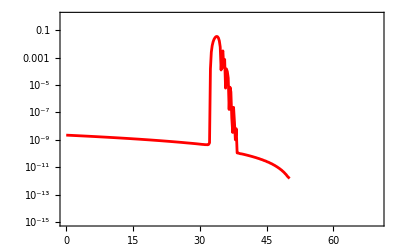

```mathematica
ListLogPlot[PN0,PlotRange->{{0,70},{10^-15,1}},Joined->True,Frame->True,PlotStyle->Red]
```

```mathematica
kmpc=Solve[0.05/Mpc==((a[Ne] H[Ne])/cs)/.solNe1/.Ne->0,Mpc][[1]][[1,2]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

551.775

```mathematica
Pkc=Table[{(kmpc((H[Ne]a[Ne])/cs)/.solNe1/.{Ne->NeHE[[i]]})[[1]],(k[[i]]^3/(2*Pi^2)*Abs[u[Ne]/(z[Ne]/.solNe1)]^2/.MSol[[i]]/.Ne->NeEnd[[i]])[[1]][[1]]},{i,1,iMax}]
```

{{0.05,2.16383×10^-9},{0.0609622,2.14773×10^-9},{0.0743274,2.13182×10^-9},{0.0906221,2.1155×10^-9},{0.110488,2.10088×10^-9},{0.134709,2.08727×10^-9},{0.164238,2.07312×10^-9},{0.200238,2.05754×10^-9},{0.244128,2.04161×10^-9},{0.297636,2.02583×10^-9},{0.36287,2.01151×10^-9},{0.442398,1.99802×10^-9},{0.539353,1.9837×10^-9},{0.65755,1.96871×10^-9},{0.801645,1.95326×10^-9},{0.97731,1.93816×10^-9},{1.19146,1.92408×10^-9},{1.45253,1.91068×10^-9},{1.77078,1.89657×10^-9},{2.15875,1.88193×10^-9},{2.6317,1.86685×10^-9},{3.20825,1.85216×10^-9},{3.91108,1.83858×10^-9},{4.76784,1.82558×10^-9},{5.81224,1.81189×10^-9},{7.08537,1.79764×10^-9},{8.63729,1.78298×10^-9},{10.5291,1.76859×10^-9},{12.8351,1.75476×10^-9},{15.646,1.74109×10^-9},{19.0724,1.7274×10^-9},{23.2489,1.71411×10^-9},{28.3399,1.70077×10^-9},{34.5453,1.68759×10^-9},{42.1092,1.67434×10^-9},{51.3289,1.66096×10^-9},{62.5666,1.64743×10^-9},{76.264,1.63377×10^-9},{92.9593,1.62011×10^-9},{113.309,1.60664×10^-9},{138.111,1.59341×10^-9},{168.342,1.58033×10^-9},{205.187,1.56738×10^-9},{250.095,1.55462×10^-9},{304.829,1.54194×10^-9},{371.538,1.52933×10^-9},{452.842,1.51669×10^-9},{551.932,1.50396×10^-9},{672.699,1.4911×10^-9},{819.884,1.47811×10^-9},{999.263,1.46511×10^-9},{1217.88,1.45226×10^-9},{1484.3,1.43966×10^-9},{1809.,1.42726×10^-9},{2204.7,1.41498×10^-9},{2686.92,1.4029×10^-9},{3274.6,1.3909×10^-9},{3990.77,1.37897×10^-9},{4863.51,1.36697×10^-9},{5927.07,1.35486×10^-9},{7223.12,1.34261×10^-9},{8802.5,1.33021×10^-9},{10727.1,1.31781×10^-9},{13072.4,1.30561×10^-9},{15930.2,1.2937×10^-9},{19412.6,1.28198×10^-9},{23656.,1.27044×10^-9},{28826.7,1.25907×10^-9},{35127.2,1.24779×10^-9},{42804.4,1.23654×10^-9},{52158.7,1.22518×10^-9},{63556.7,1.21368×10^-9},{77444.5,1.20196×10^-9},{94365.9,1.19011×10^-9},{114983.,1.17832×10^-9},{140103.,1.16679×10^-9},{170710.,1.15558×10^-9},{207999.,1.14456×10^-9},{253432.,1.13376×10^-9},{308784.,1.12308×10^-9},{376221.,1.11248×10^-9},{458381.,1.10188×10^-9},{558475.,1.09113×10^-9},{680419.,1.08019×10^-9},{828978.,1.06902×10^-9},{1.00996×10^6,1.05776×10^-9},{1.23044×10^6,1.04662×10^-9},{1.49903×10^6,1.03581×10^-9},{1.82622×10^6,1.02529×10^-9},{2.2248×10^6,1.01494×10^-9},{2.71034×10^6,1.0048×10^-9},{3.3018×10^6,9.94803×10^-10},{4.02227×10^6,9.84868×10^-10},{4.89989×10^6,9.74884×10^-10},{5.9689×10^6,9.64727×10^-10},{7.27104×10^6,9.54387×10^-10},{8.85713×10^6,9.43909×10^-10},{1.0789×10^7,9.33438×10^-10},{1.31421×10^7,9.23167×10^-10},{1.60082×10^7,9.13133×10^-10},{1.9499×10^7,9.03253×10^-10},{2.37507×10^7,8.93516×10^-10},{2.89291×10^7,8.83961×10^-10},{3.52359×10^7,8.7447×10^-10},{4.29169×10^7,8.65042×10^-10},{5.22715×10^7,8.55546×10^-10},{6.36642×10^7,8.45994×10^-10},{7.75386×10^7,8.36313×10^-10},{9.44351×10^7,8.26597×10^-10},{1.15012×10^8,8.16955×10^-10},{1.40069×10^8,8.07478×10^-10},{1.70583×10^8,7.98155×10^-10},{2.07742×10^8,7.88925×10^-10},{2.52989×10^8,7.7982×10^-10},{3.08087×10^8,7.70828×10^-10},{3.75178×10^8,7.61907×10^-10},{4.5687×10^8,7.5302×10^-10},{5.5634×10^8,7.44131×10^-10},{6.77454×10^8,7.35171×10^-10},{8.2492×10^8,7.26167×10^-10},{1.00447×10^9,7.17137×10^-10},{1.22307×10^9,7.08161×10^-10},{1.48921×10^9,6.99335×10^-10},{1.81324×10^9,6.90705×10^-10},{2.20772×10^9,6.82174×10^-10},{2.68798×10^9,6.73748×10^-10},{3.27263×10^9,6.65514×10^-10},{3.98438×10^9,6.57362×10^-10},{4.85081×10^9,6.49046×10^-10},{5.90553×10^9,6.40838×10^-10},{7.18943×10^9,6.32506×10^-10},{8.75226×10^9,6.23865×10^-10},{1.06546×10^10,6.15022×10^-10},{1.29701×10^10,6.06167×10^-10},{1.57884×10^10,5.97665×10^-10},{1.92187×10^10,5.89651×10^-10},{2.33938×10^10,5.81812×10^-10},{2.84752×10^10,5.74292×10^-10},{3.46595×10^10,5.66951×10^-10},{4.21859×10^10,5.59817×10^-10},{5.13456×10^10,5.52614×10^-10},{6.24925×10^10,5.45294×10^-10},{7.60573×10^10,5.37696×10^-10},{9.25643×10^10,5.30007×10^-10},{1.12651×10^11,5.22458×10^-10},{1.37093×10^11,5.15045×10^-10},{1.66833×10^11,5.07939×10^-10},{2.03019×10^11,4.9994×10^-10},{2.47046×10^11,4.92293×10^-10},{3.00612×10^11,4.84643×10^-10},{3.6578×10^11,4.76437×10^-10},{4.45062×10^11,4.68935×10^-10},{5.4151×10^11,4.61055×10^-10},{6.58836×10^11,4.54129×10^-10},{8.01554×10^11,4.49871×10^-10},{9.75147×10^11,4.43228×10^-10},{1.18628×10^12,4.35032×10^-10},{1.44304×10^12,4.35814×10^-10},{1.75526×10^12,4.33007×10^-10},{2.13487×10^12,4.28649×10^-10},{2.59634×10^12,4.52151×10^-10},{3.1571×10^12,6.00588×10^-10},{3.83825×10^12,0.000148869},{4.66513×10^12,0.00250022},{5.6676×10^12,0.00751265},{6.88011×10^12,0.0139846},{8.3358×10^12,0.0211604},{9.84418×10^12,0.027284},{1.15141×10^13,0.0326327},{1.36452×10^13,0.0348909},{1.63196×10^13,0.0332913},{1.96322×10^13,0.0269073},{2.37013×10^13,0.0164987},{2.86747×10^13,0.00593393},{3.47363×10^13,0.000123085},{4.21088×10^13,0.00181442},{5.1067×10^13,0.00306007},{6.19445×10^13,0.000197179},{7.51456×10^13,0.000728985},{9.11618×10^13,5.85984×10^-6},{1.10589×10^14,0.000146772},{1.34151×10^14,0.0000937142},{1.62722×10^14,0.0000319695},{1.97363×10^14,1.618×10^-7},{2.39357×10^14,6.84705×10^-6},{2.9026×10^14,3.06198×10^-6},{3.51952×10^14,3.78598×10^-8},{4.26713×10^14,3.39464×10^-9},{5.17299×10^14,2.31933×10^-7},{6.27046×10^14,1.95711×10^-8},{7.5999×10^14,9.91326×10^-10},{9.2101×10^14,6.32141×10^-9},{1.11601×10^15,1.08924×10^-10},{1.35212×10^15,1.05878×10^-10},{1.63798×10^15,1.0248×10^-10},{1.98399×10^15,9.72795×10^-11},{2.40277×10^15,9.42848×10^-11},{2.90951×10^15,9.26429×10^-11},{3.5226×10^15,8.96996×10^-11},{4.26421×10^15,8.67629×10^-11},{5.16111×10^15,8.361×10^-11},{6.24563×10^15,8.06068×10^-11},{7.55673×10^15,7.76699×10^-11},{9.14141×10^15,7.48376×10^-11},{1.10563×10^16,7.19912×10^-11},{1.33698×10^16,6.92567×10^-11},{1.61642×10^16,6.65703×10^-11},{1.95384×10^16,6.39392×10^-11},{2.36118×10^16,6.13988×10^-11},{2.8528×10^16,5.89628×10^-11},{3.44596×10^16,5.64395×10^-11},{4.16141×10^16,5.38894×10^-11},{5.0241×10^16,5.16682×10^-11},{6.06398×10^16,4.95004×10^-11},{7.317×10^16,4.70779×10^-11},{8.82632×10^16,4.47254×10^-11},{1.06436×10^17,4.28644×10^-11},{1.28309×10^17,4.08545×10^-11},{1.54623×10^17,3.8487×10^-11},{1.86265×10^17,3.65076×10^-11},{2.24296×10^17,3.49431×10^-11},{2.69983×10^17,3.29623×10^-11},{3.24838×10^17,3.07429×10^-11},{3.9066×10^17,2.92973×10^-11},{4.69591×10^17,2.78953×10^-11},{5.64178×10^17,2.59571×10^-11},{6.77444×10^17,2.40906×10^-11},{8.12974×10^17,2.29456×10^-11},{9.75004×10^17,2.15265×10^-11},{1.16854×10^18,1.9759×10^-11},{1.39949×10^18,1.84773×10^-11},{1.67478×10^18,1.73525×10^-11},{2.00253×10^18,1.58696×10^-11},{2.39223×10^18,1.45728×10^-11},{2.85494×10^18,1.35414×10^-11},{3.40346×10^18,1.23041×10^-11},{4.05253×10^18,1.12219×10^-11},{4.81905×10^18,1.02527×10^-11},{5.72223×10^18,9.22446×10^-12},{6.7837×10^18,8.36173×10^-12},{8.0275×10^18,7.48063×10^-12},{9.48005×10^18,6.63863×10^-12},{1.11697×10^19,5.95106×10^-12},{1.31261×10^19,5.16027×10^-12},{1.53786×10^19,4.53399×10^-12},{1.79542×10^19,3.92841×10^-12},{2.0874×10^19,3.31372×10^-12},{2.41474×10^19,2.86549×10^-12},{2.77652×10^19,2.33933×10^-12},{3.1689×10^19,1.96491×10^-12},{3.58295×10^19,1.70045×10^-12},{4.00171×10^19,1.49298×10^-12}}

```mathematica
Export["PkF.dat",Pkc];
```

```mathematica
Pkc=Import["PkF.dat"];
c1=Interpolation[Pkc,InterpolationOrder->1]
AA=LogLogPlot[{c1[x]},{x,0.0634257151149378,6.242598573013641*^19},PlotRange->{{0.001,4*10^22},{10^-12,1}},Frame->True,FrameStyle->Thick,FrameTicksStyle->Black,PlotStyle->{Purple},LabelStyle->Directive[24,Bold,Black,FontFamily->"Book Antiqua"],ImageSize->{600,400},AspectRatio->Full,RotateLabel->False,Axes->False,FrameLabel->{"K/Mpc^-1","P_s"}]
```

InterpolatingFunction[…]

```mathematica
InterpolatingFunction[…];
```

```mathematica
c1[0.05kmpc]
```

1.70274×10^-9

```mathematica
AA=ListLogLogPlot[Pkc,PlotRange->{{0.05,4*10^22},{10^-13,1}},Joined->True,Frame->True,FrameStyle->Thick,FrameTicksStyle->Black,PlotStyle->Brown,LabelStyle->Directive[24,Bold,Black,FontFamily->"Book Antiqua"],ImageSize->{600,400},AspectRatio->Full,RotateLabel->False,Axes->False,FrameLabel->{"K/Mpc^-1","P_R"}]
```

```mathematica
ss=-Graphics-;
```

```mathematica
fback=Show[{LogLogPlot[{ns0[Ne]},{Ne,1,10},PlotRange->{{10^-4,10^24},{10^-12,10^0}},PlotStyle->{Black,Thickness[0.005]},Frame-> True,FrameLabel->{"M/M_⊙","f_Pbh"},LabelStyle->Directive[22,Bold,FontFamily->"Book Antiqua"],ImageSize->{600,400},AspectRatio->Full],Graphics[{Texture[ss],EdgeForm[Black],Polygon[{{-9.1,-27.56},{55.2,-27.56},{55.2,0.1},{-9.1,0.1}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},ImageSize->{600,400},AspectRatio->Full]},Axes->False,RotateLabel->True]
```

```mathematica
Show[fback,AA]
```

```mathematica
Mkc=Table[(1/((1.9*10^6)^-2)*(1/(√3))^3/0.2*(106.75/10.75)^(-1/6)*(kmpc*k[[i]])^-2)[[1]],{i,1,iMax}];
```

```mathematica
PRc=Interpolation[Pkc,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
qend=PRc[[1,1,2]]
```

4.00171×10^19

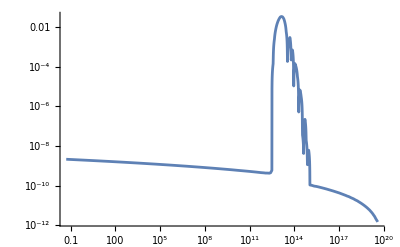

```mathematica
LogLogPlot[PRc[x],{x,0.05,qend},PlotRange->All]
```

```mathematica
(*WorkingPrecision->15.,Method->"TrapezoidalRule"*)
```

```mathematica
For[i=1,i≤ iMax,i++,
si[i]=NIntegrate[16/81*1/q*(q/(k[[i]]*kmpc))^4 Exp[-q^2/(k[[i]]*kmpc)^2]PRc[q],{q,0,PRc[[1,1,2]]}];
]
```

```mathematica
Beep[]
```

```mathematica
sigma=Table[si[i],{i,1,iMax}]//N;
```

```mathematica
δc=0.4;
```

```mathematica
(*For[i=1,i≤ iMax,i++,
B[i]=√(1/(2Pi))(sigma[[i]])^(1/2)/δc Exp[(- δc^2)/(2*sigma[[i]])]]*)
```

```mathematica
For[i=1,i≤ iMax,i++,
B[i]=1/2 Erfc[δc/(√(2*sigma[[i]]))]]
```

```mathematica
f=Table[B[i]/(1.84*10^-8)*((1/(√3))^3/0.2)^(3/2)*(10.75/106.75)^(1/4)*(Mkc[[i]])^(-1/2),{i,1,iMax}];
```

```mathematica
ac=Table[{Mkc[[i]],f[[i]][[1]]},{i,1,iMax}];
```

```mathematica
Export["FPBHF.dat",ac];
```

```mathematica
ac=Import["FPBHF.dat"];
```

```mathematica
Max[f]
```

0.985373

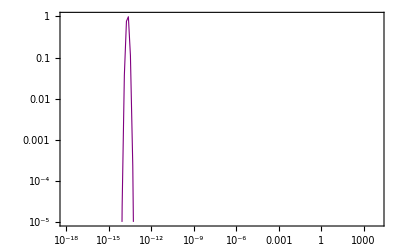

```mathematica
fc=ListLogLogPlot[ac,Joined->True,Frame->True,Axes->False,PlotRange->{{10^-18,10^4},{10^-5,1}},PlotStyle->{Purple,Thickness[0.002]}]
```

InterpolatingFunction[…]

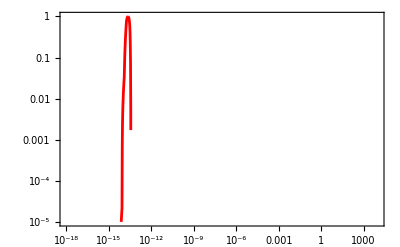

```mathematica
s1=Interpolation[ac,InterpolationOrder->2]
fc=LogLogPlot[s1[x],{x,3.86*^-39,7.0121*^14},Frame->True,Axes->False,PlotRange->{{10^-18,10^4},{10^-5,10^0}},PlotStyle->Red,FillingStyle->Black,ImageSize->{400,300}]
```

```mathematica
fb=-Graphics-;
```

```mathematica
fback=Show[{LogLogPlot[{ns0[Ne]},{Ne,1,10},PlotRange->{{10^-18,10^4},{10^-5,10^0}},PlotStyle->{Black,Thickness[0.005]},Frame-> True,FrameLabel->{"M/M_⊙","f_Pbh"},LabelStyle->Directive[22,Bold,FontFamily->"Book Antiqua"],ImageSize->{600,400},AspectRatio->Full],Graphics[{Texture[fb],EdgeForm[Black],Polygon[{{-41.5,-11.55},{9.3,-11.55},{9.3,0},{-41.5,0}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},ImageSize->{600,400},AspectRatio->Full]},Axes->False,RotateLabel->True]
```

```mathematica
fpbh=Show[fback,fc,ImageSize->{600,400}]
```

```mathematica
Show[back,fc,ImageSize->{600,400}]
```

```mathematica
data2=Table[{i,(kmpc((a[Ne] H[Ne])/cs)/.solNe1/.{Ne->NeHE[[i]]})[[1]],NeHE[[i]],NeBD[[i]],Mkc[[i]],PN0[[i]][[2]],f[[i]]},{i,1,iMax}];
```

```mathematica
pr=data2[[All,6]];
```

```mathematica
Position[pr,Max[pr]][[1]][[1]]
```

170

```mathematica
Length[Pkc]
```

252

```mathematica
Pkpeak=Pkc[[Position[pr,Max[pr]][[1]][[1]],2]]
```

0.0348909

```mathematica
Mkc[[Position[pr,Max[pr]][[1]][[1]]]]
```

1.27255×10^-14

```mathematica
f[[Position[pr,Max[pr]][[1]][[1]]]]
```

{0.0370942}

```mathematica
mytab2=Text@Grid[Prepend[data2,{"i","K","N","NBD","M(k)/M_o","P_R","f"}],Frame->All,Alignment->{Center},ItemSize->{10},Frame->Darker[Gray,.6],ItemStyle->14,Background->{Automatic,{1-> Green,Position[pr,Max[pr]][[1]][[1]]+1->Yellow}}]
```

i | K | N | NBD | M(k)/M_o | P_R | f
1 | 0.05 | 0. | -5. | 9.47754×10^14 | 2.16383×10^-9 | {0.}
2 | 0.0609622 | 0.2 | -4.8 | 6.37549×10^14 | 2.14773×10^-9 | {0.}
3 | 0.0743274 | 0.4 | -4.6 | 4.28882×10^14 | 2.13182×10^-9 | {0.}
4 | 0.0906221 | 0.6 | -4.4 | 2.88514×10^14 | 2.1155×10^-9 | {0.}
5 | 0.110488 | 0.8 | -4.2 | 1.9409×10^14 | 2.10088×10^-9 | {0.}
6 | 0.134709 | 1. | -4. | 1.3057×10^14 | 2.08727×10^-9 | {0.}
7 | 0.164238 | 1.2 | -3.8 | 8.78394×10^13 | 2.07312×10^-9 | {0.}
8 | 0.200238 | 1.4 | -3.6 | 5.90938×10^13 | 2.05754×10^-9 | {0.}
9 | 0.244128 | 1.6 | -3.4 | 3.97557×10^13 | 2.04161×10^-9 | {0.}
10 | 0.297636 | 1.8 | -3.2 | 2.67463×10^13 | 2.02583×10^-9 | {0.}
11 | 0.36287 | 2. | -3. | 1.79942×10^13 | 2.01151×10^-9 | {0.}
12 | 0.442398 | 2.2 | -2.8 | 1.21062×10^13 | 1.99802×10^-9 | {0.}
13 | 0.539353 | 2.4 | -2.6 | 8.14498×10^12 | 1.9837×10^-9 | {0.}
14 | 0.65755 | 2.6 | -2.4 | 5.47996×10^12 | 1.96871×10^-9 | {0.}
15 | 0.801645 | 2.8 | -2.2 | 3.68698×10^12 | 1.95326×10^-9 | {0.}
16 | 0.97731 | 3. | -2. | 2.48068×10^12 | 1.93816×10^-9 | {0.}
17 | 1.19146 | 3.2 | -1.8 | 1.66908×10^12 | 1.92408×10^-9 | {0.}
18 | 1.45253 | 3.4 | -1.6 | 1.12302×10^12 | 1.91068×10^-9 | {0.}
19 | 1.77078 | 3.6 | -1.4 | 7.55625×10^11 | 1.89657×10^-9 | {0.}
20 | 2.15875 | 3.8 | -1.2 | 5.08429×10^11 | 1.88193×10^-9 | {0.}
21 | 2.6317 | 4. | -1. | 3.42106×10^11 | 1.86685×10^-9 | {0.}
22 | 3.20825 | 4.2 | -0.8 | 2.30196×10^11 | 1.85216×10^-9 | {0.}
23 | 3.91108 | 4.4 | -0.6 | 1.54896×10^11 | 1.83858×10^-9 | {0.}
24 | 4.76784 | 4.6 | -0.4 | 1.0423×10^11 | 1.82558×10^-9 | {0.}
25 | 5.81224 | 4.8 | -0.2 | 7.01371×10^10 | 1.81189×10^-9 | {0.}
26 | 7.08537 | 5. | 0. | 4.71966×10^10 | 1.79764×10^-9 | {0.}
27 | 8.63729 | 5.2 | 0.2 | 3.176×10^10 | 1.78298×10^-9 | {0.}
28 | 10.5291 | 5.4 | 0.4 | 2.13726×10^10 | 1.76859×10^-9 | {0.}
29 | 12.8351 | 5.6 | 0.6 | 1.43827×10^10 | 1.75476×10^-9 | {0.}
30 | 15.646 | 5.8 | 0.8 | 9.67897×10^9 | 1.74109×10^-9 | {0.}
31 | 19.0724 | 6. | 1. | 6.51367×10^9 | 1.7274×10^-9 | {0.}
32 | 23.2489 | 6.2 | 1.2 | 4.38358×10^9 | 1.71411×10^-9 | {0.}
33 | 28.3399 | 6.4 | 1.4 | 2.95012×10^9 | 1.70077×10^-9 | {0.}
34 | 34.5453 | 6.6 | 1.6 | 1.98544×10^9 | 1.68759×10^-9 | {0.}
35 | 42.1092 | 6.8 | 1.8 | 1.33623×10^9 | 1.67434×10^-9 | {0.}
36 | 51.3289 | 7. | 2. | 8.99315×10^8 | 1.66096×10^-9 | {0.}
37 | 62.5666 | 7.2 | 2.2 | 6.05272×10^8 | 1.64743×10^-9 | {0.}
38 | 76.264 | 7.4 | 2.4 | 4.07377×10^8 | 1.63377×10^-9 | {0.}
39 | 92.9593 | 7.6 | 2.6 | 2.74189×10^8 | 1.62011×10^-9 | {0.}
40 | 113.309 | 7.8 | 2.8 | 1.84548×10^8 | 1.60664×10^-9 | {0.}
41 | 138.111 | 8. | 3. | 1.24216×10^8 | 1.59341×10^-9 | {0.}
42 | 168.342 | 8.2 | 3.2 | 8.3609×10^7 | 1.58033×10^-9 | {0.}
43 | 205.187 | 8.4 | 3.4 | 5.62776×10^7 | 1.56738×10^-9 | {0.}
44 | 250.095 | 8.6 | 3.6 | 3.78814×10^7 | 1.55462×10^-9 | {0.}
45 | 304.829 | 8.8 | 3.8 | 2.5499×10^7 | 1.54194×10^-9 | {0.}
46 | 371.538 | 9. | 4. | 1.71644×10^7 | 1.52933×10^-9 | {0.}
47 | 452.842 | 9.2 | 4.2 | 1.15543×10^7 | 1.51669×10^-9 | {0.}
48 | 551.932 | 9.4 | 4.4 | 7.77793×10^6 | 1.50396×10^-9 | {0.}
49 | 672.699 | 9.6 | 4.6 | 5.23592×10^6 | 1.4911×10^-9 | {0.}
50 | 819.884 | 9.8 | 4.8 | 3.52477×10^6 | 1.47811×10^-9 | {0.}
51 | 999.263 | 10. | 5. | 2.37288×10^6 | 1.46511×10^-9 | {0.}
52 | 1217.88 | 10.2 | 5.2 | 1.59746×10^6 | 1.45226×10^-9 | {0.}
53 | 1484.3 | 10.4 | 5.4 | 1.07545×10^6 | 1.43966×10^-9 | {0.}
54 | 1809. | 10.6 | 5.6 | 724036. | 1.42726×10^-9 | {0.}
55 | 2204.7 | 10.8 | 5.8 | 487459. | 1.41498×10^-9 | {0.}
56 | 2686.92 | 11. | 6. | 328189. | 1.4029×10^-9 | {0.}
57 | 3274.6 | 11.2 | 6.2 | 220963. | 1.3909×10^-9 | {0.}
58 | 3990.77 | 11.4 | 6.4 | 148773. | 1.37897×10^-9 | {0.}
59 | 4863.51 | 11.6 | 6.6 | 100169. | 1.36697×10^-9 | {0.}
60 | 5927.07 | 11.8 | 6.8 | 67445.9 | 1.35486×10^-9 | {0.}
61 | 7223.12 | 12. | 7. | 45413.5 | 1.34261×10^-9 | {0.}
62 | 8802.5 | 12.2 | 7.2 | 30579. | 1.33021×10^-9 | {0.}
63 | 10727.1 | 12.4 | 7.4 | 20590.7 | 1.31781×10^-9 | {0.}
64 | 13072.4 | 12.6 | 7.6 | 13865.2 | 1.30561×10^-9 | {0.}
65 | 15930.2 | 12.8 | 7.8 | 9336.69 | 1.2937×10^-9 | {0.}
66 | 19412.6 | 13. | 8. | 6287.35 | 1.28198×10^-9 | {0.}
67 | 23656. | 13.2 | 8.2 | 4234. | 1.27044×10^-9 | {0.}
68 | 28826.7 | 13.4 | 8.4 | 2851.31 | 1.25907×10^-9 | {0.}
69 | 35127.2 | 13.6 | 8.6 | 1920.2 | 1.24779×10^-9 | {0.}
70 | 42804.4 | 13.8 | 8.8 | 1293.18 | 1.23654×10^-9 | {0.}
71 | 52158.7 | 14. | 9. | 870.926 | 1.22518×10^-9 | {0.}
72 | 63556.7 | 14.2 | 9.2 | 586.56 | 1.21368×10^-9 | {0.}
73 | 77444.5 | 14.4 | 9.4 | 395.052 | 1.20196×10^-9 | {0.}
74 | 94365.9 | 14.6 | 9.6 | 266.076 | 1.19011×10^-9 | {0.}
75 | 114983. | 14.8 | 9.8 | 179.212 | 1.17832×10^-9 | {0.}
76 | 140103. | 15. | 10. | 120.708 | 1.16679×10^-9 | {0.}
77 | 170710. | 15.2 | 10.2 | 81.3054 | 1.15558×10^-9 | {0.}
78 | 207999. | 15.4 | 10.4 | 54.766 | 1.14456×10^-9 | {0.}
79 | 253432. | 15.6 | 10.6 | 36.8904 | 1.13376×10^-9 | {0.}
80 | 308784. | 15.8 | 10.8 | 24.85 | 1.12308×10^-9 | {0.}
81 | 376221. | 16. | 11. | 16.7397 | 1.11248×10^-9 | {0.}
82 | 458381. | 16.2 | 11.2 | 11.2767 | 1.10188×10^-9 | {0.}
83 | 558475. | 16.4 | 11.4 | 7.59674 | 1.09113×10^-9 | {0.}
84 | 680419. | 16.6 | 11.6 | 5.11779 | 1.08019×10^-9 | {0.}
85 | 828978. | 16.8 | 11.8 | 3.44786 | 1.06902×10^-9 | {0.}
86 | 1.00996×10^6 | 17. | 12. | 2.32288 | 1.05776×10^-9 | {0.}
87 | 1.23044×10^6 | 17.2 | 12.2 | 1.56501 | 1.04662×10^-9 | {0.}
88 | 1.49903×10^6 | 17.4 | 12.4 | 1.05443 | 1.03581×10^-9 | {0.}
89 | 1.82622×10^6 | 17.6 | 12.6 | 0.710441 | 1.02529×10^-9 | {0.}
90 | 2.2248×10^6 | 17.8 | 12.8 | 0.478687 | 1.01494×10^-9 | {0.}
91 | 2.71034×10^6 | 18. | 13. | 0.322542 | 1.0048×10^-9 | {0.}
92 | 3.3018×10^6 | 18.2 | 13.2 | 0.217337 | 9.94803×10^-10 | {0.}
93 | 4.02227×10^6 | 18.4 | 13.4 | 0.146451 | 9.84868×10^-10 | {0.}
94 | 4.89989×10^6 | 18.6 | 13.6 | 0.0986877 | 9.74884×10^-10 | {0.}
95 | 5.9689×10^6 | 18.8 | 13.8 | 0.0665038 | 9.64727×10^-10 | {0.}
96 | 7.27104×10^6 | 19. | 14. | 0.0448169 | 9.54387×10^-10 | {0.}
97 | 8.85713×10^6 | 19.2 | 14.2 | 0.030203 | 9.43909×10^-10 | {0.}
98 | 1.0789×10^7 | 19.4 | 14.4 | 0.020355 | 9.33438×10^-10 | {0.}
99 | 1.31421×10^7 | 19.6 | 14.6 | 0.0137184 | 9.23167×10^-10 | {0.}
100 | 1.60082×10^7 | 19.8 | 14.8 | 0.00924591 | 9.13133×10^-10 | {0.}
101 | 1.9499×10^7 | 20. | 15. | 0.00623173 | 9.03253×10^-10 | {0.}
102 | 2.37507×10^7 | 20.2 | 15.2 | 0.00420031 | 8.93516×10^-10 | {0.}
103 | 2.89291×10^7 | 20.4 | 15.4 | 0.00283118 | 8.83961×10^-10 | {0.}
104 | 3.52359×10^7 | 20.6 | 15.6 | 0.00190838 | 8.7447×10^-10 | {0.}
105 | 4.29169×10^7 | 20.8 | 15.8 | 0.00128641 | 8.65042×10^-10 | {0.}
106 | 5.22715×10^7 | 21. | 16. | 0.000867171 | 8.55546×10^-10 | {0.}
107 | 6.36642×10^7 | 21.2 | 16.2 | 0.000584582 | 8.45994×10^-10 | {0.}
108 | 7.75386×10^7 | 21.4 | 16.4 | 0.000394094 | 8.36313×10^-10 | {0.}
109 | 9.44351×10^7 | 21.6 | 16.6 | 0.000265686 | 8.26597×10^-10 | {0.}
110 | 1.15012×10^8 | 21.8 | 16.8 | 0.000179123 | 8.16955×10^-10 | {0.}
111 | 1.40069×10^8 | 22. | 17. | 0.000120767 | 8.07478×10^-10 | {0.}
112 | 1.70583×10^8 | 22.2 | 17.2 | 0.0000814257 | 7.98155×10^-10 | {0.}
113 | 2.07742×10^8 | 22.4 | 17.4 | 0.0000549021 | 7.88925×10^-10 | {0.}
114 | 2.52989×10^8 | 22.6 | 17.6 | 0.0000370195 | 7.7982×10^-10 | {0.}
115 | 3.08087×10^8 | 22.8 | 17.8 | 0.0000249625 | 7.70828×10^-10 | {0.}
116 | 3.75178×10^8 | 23. | 18. | 0.000016833 | 7.61907×10^-10 | {0.}
117 | 4.5687×10^8 | 23.2 | 18.2 | 0.0000113514 | 7.5302×10^-10 | {0.}
118 | 5.5634×10^8 | 23.4 | 18.4 | 7.65517×10^-6 | 7.44131×10^-10 | {0.}
119 | 6.77454×10^8 | 23.6 | 18.6 | 5.16268×10^-6 | 7.35171×10^-10 | {0.}
120 | 8.2492×10^8 | 23.8 | 18.8 | 3.48187×10^-6 | 7.26167×10^-10 | {0.}
121 | 1.00447×10^9 | 24. | 19. | 2.34836×10^-6 | 7.17137×10^-10 | {0.}
122 | 1.22307×10^9 | 24.2 | 19.2 | 1.58393×10^-6 | 7.08161×10^-10 | {0.}
123 | 1.48921×10^9 | 24.4 | 19.4 | 1.06837×10^-6 | 6.99335×10^-10 | {0.}
124 | 1.81324×10^9 | 24.6 | 19.6 | 7.20651×10^-7 | 6.90705×10^-10 | {0.}
125 | 2.20772×10^9 | 24.8 | 19.8 | 4.86123×10^-7 | 6.82174×10^-10 | {0.}
126 | 2.68798×10^9 | 25. | 20. | 3.27932×10^-7 | 6.73748×10^-10 | {0.}
127 | 3.27263×10^9 | 25.2 | 20.2 | 2.21228×10^-7 | 6.65514×10^-10 | {0.}
128 | 3.98438×10^9 | 25.4 | 20.4 | 1.4925×10^-7 | 6.57362×10^-10 | {0.}
129 | 4.85081×10^9 | 25.6 | 20.6 | 1.00695×10^-7 | 6.49046×10^-10 | {0.}
130 | 5.90553×10^9 | 25.8 | 20.8 | 6.79387×10^-8 | 6.40838×10^-10 | {0.}
131 | 7.18943×10^9 | 26. | 21. | 4.58402×10^-8 | 6.32506×10^-10 | {0.}
132 | 8.75226×10^9 | 26.2 | 21.2 | 3.09311×10^-8 | 6.23865×10^-10 | {0.}
133 | 1.06546×10^10 | 26.4 | 21.4 | 2.08719×10^-8 | 6.15022×10^-10 | {0.}
134 | 1.29701×10^10 | 26.6 | 21.6 | 1.40848×10^-8 | 6.06167×10^-10 | {0.}
135 | 1.57884×10^10 | 26.8 | 21.8 | 9.50512×10^-9 | 5.97665×10^-10 | {0.}
136 | 1.92187×10^10 | 27. | 22. | 6.41483×10^-9 | 5.89651×10^-10 | {0.}
137 | 2.33938×10^10 | 27.2 | 22.2 | 4.32945×10^-9 | 5.81812×10^-10 | {0.}
138 | 2.84752×10^10 | 27.4 | 22.4 | 2.92214×10^-9 | 5.74292×10^-10 | {0.}
139 | 3.46595×10^10 | 27.6 | 22.6 | 1.97238×10^-9 | 5.66951×10^-10 | {0.}
140 | 4.21859×10^10 | 27.8 | 22.8 | 1.33138×10^-9 | 5.59817×10^-10 | {0.}
141 | 5.13456×10^10 | 28. | 23. | 8.9873×10^-10 | 5.52614×10^-10 | {0.}
142 | 6.24925×10^10 | 28.2 | 23.2 | 6.06708×10^-10 | 5.45294×10^-10 | {0.}
143 | 7.60573×10^10 | 28.4 | 23.4 | 4.09594×10^-10 | 5.37696×10^-10 | {0.}
144 | 9.25643×10^10 | 28.6 | 23.6 | 2.76534×10^-10 | 5.30007×10^-10 | {0.}
145 | 1.12651×10^11 | 28.8 | 23.8 | 1.86709×10^-10 | 5.22458×10^-10 | {0.}
146 | 1.37093×10^11 | 29. | 24. | 1.26068×10^-10 | 5.15045×10^-10 | {0.}
147 | 1.66833×10^11 | 29.2 | 24.2 | 8.5128×10^-11 | 5.07939×10^-10 | {0.}
148 | 2.03019×10^11 | 29.4 | 24.4 | 5.74861×10^-11 | 4.9994×10^-10 | {0.}
149 | 2.47046×10^11 | 29.6 | 24.6 | 3.88222×10^-11 | 4.92293×10^-10 | {0.}
150 | 3.00612×10^11 | 29.8 | 24.8 | 2.62194×10^-11 | 4.84643×10^-10 | {0.}
151 | 3.6578×10^11 | 30. | 25. | 1.7709×10^-11 | 4.76437×10^-10 | {0.}
152 | 4.45062×10^11 | 30.2 | 25.2 | 1.19617×10^-11 | 4.68935×10^-10 | {0.}
153 | 5.4151×10^11 | 30.4 | 25.4 | 8.0802×10^-12 | 4.61055×10^-10 | {0.}
154 | 6.58836×10^11 | 30.6 | 25.6 | 5.45859×10^-12 | 4.54129×10^-10 | {0.}
155 | 8.01554×10^11 | 30.8 | 25.8 | 3.68782×10^-12 | 4.49871×10^-10 | {0.}
156 | 9.75147×10^11 | 31. | 26. | 2.4917×10^-12 | 4.43228×10^-10 | {0.}
157 | 1.18628×10^12 | 31.2 | 26.2 | 1.6837×10^-12 | 4.35032×10^-10 | {0.}
158 | 1.44304×10^12 | 31.4 | 26.4 | 1.13784×10^-12 | 4.35814×10^-10 | {0.}
159 | 1.75526×10^12 | 31.6 | 26.6 | 7.69046×10^-13 | 4.33007×10^-10 | {0.}
160 | 2.13487×10^12 | 31.8 | 26.8 | 5.19866×10^-13 | 4.28649×10^-10 | {0.}
161 | 2.59634×10^12 | 32. | 27. | 3.5149×10^-13 | 4.52151×10^-10 | {2.97163×10^-253}
162 | 3.1571×10^12 | 32.2 | 27.2 | 2.37717×10^-13 | 6.00588×10^-10 | {1.82025×10^-95}
163 | 3.83825×10^12 | 32.4 | 27.4 | 1.60831×10^-13 | 0.000148869 | {2.9372×10^-42}
164 | 4.66513×10^12 | 32.6 | 27.6 | 1.0887×10^-13 | 0.00250022 | {3.12641×10^-20}
165 | 5.6676×10^12 | 32.8 | 27.8 | 7.37627×10^-14 | 0.00751265 | {9.66758×10^-10}
166 | 6.88011×10^12 | 33. | 28. | 5.00546×10^-14 | 0.0139846 | {0.000230104}
167 | 8.3358×10^12 | 33.2 | 28.2 | 3.4099×10^-14 | 0.0211604 | {0.112473}
168 | 9.84418×10^12 | 33.4 | 28.4 | 2.44499×10^-14 | 0.027284 | {0.985373}
169 | 1.15141×10^13 | 33.6 | 28.6 | 1.7872×10^-14 | 0.0326327 | {0.763689}
170 | 1.36452×10^13 | 33.8 | 28.8 | 1.27255×10^-14 | 0.0348909 | {0.0370942}
171 | 1.63196×10^13 | 34. | 29. | 8.89642×10^-15 | 0.0332913 | {0.0000244786}
172 | 1.96322×10^13 | 34.2 | 29.2 | 6.14748×10^-15 | 0.0269073 | {1.53745×10^-11}
173 | 2.37013×10^13 | 34.4 | 29.4 | 4.21786×10^-15 | 0.0164987 | {1.48587×10^-22}
174 | 2.86747×10^13 | 34.6 | 29.6 | 2.88163×10^-15 | 0.00593393 | {6.52913×10^-41}
175 | 3.47363×10^13 | 34.8 | 29.8 | 1.96366×10^-15 | 0.000123085 | {1.4546×10^-70}
176 | 4.21088×10^13 | 35. | 30. | 1.33625×10^-15 | 0.00181442 | {7.52936×10^-119}
177 | 5.1067×10^13 | 35.2 | 30.2 | 9.08563×10^-16 | 0.00306007 | {5.41669×10^-200}
178 | 6.19445×10^13 | 35.4 | 30.4 | 6.1749×10^-16 | 0.000197179 | {0.}
179 | 7.51456×10^13 | 35.6 | 30.6 | 4.19593×10^-16 | 0.000728985 | {0.}
180 | 9.11618×10^13 | 35.8 | 30.8 | 2.85108×10^-16 | 5.85984×10^-6 | {0.}
181 | 1.10589×10^14 | 36. | 31. | 1.93736×10^-16 | 0.000146772 | {0.}
182 | 1.34151×10^14 | 36.2 | 31.2 | 1.31659×10^-16 | 0.0000937142 | {0.}
183 | 1.62722×10^14 | 36.4 | 31.4 | 8.94837×10^-17 | 0.0000319695 | {0.}
184 | 1.97363×10^14 | 36.6 | 31.6 | 6.0828×10^-17 | 1.618×10^-7 | {0.}
185 | 2.39357×10^14 | 36.8 | 31.8 | 4.13563×10^-17 | 6.84705×10^-6 | {0.}
186 | 2.9026×10^14 | 37. | 32. | 2.8123×10^-17 | 3.06198×10^-6 | {0.}
187 | 3.51952×10^14 | 37.2 | 32.2 | 1.91279×10^-17 | 3.78598×10^-8 | {0.}
188 | 4.26713×10^14 | 37.4 | 32.4 | 1.30126×10^-17 | 3.39464×10^-9 | {0.}
189 | 5.17299×10^14 | 37.6 | 32.6 | 8.85425×10^-18 | 2.31933×10^-7 | {0.}
190 | 6.27046×10^14 | 37.8 | 32.8 | 6.0261×10^-18 | 1.95711×10^-8 | {0.}
191 | 7.5999×10^14 | 38. | 33. | 4.10223×10^-18 | 9.91326×10^-10 | {0.}
192 | 9.2101×10^14 | 38.2 | 33.2 | 2.79323×10^-18 | 6.32141×10^-9 | {0.}
193 | 1.11601×10^15 | 38.4 | 33.4 | 1.90239×10^-18 | 1.08924×10^-10 | {0.}
194 | 1.35212×10^15 | 38.6 | 33.6 | 1.29599×10^-18 | 1.05878×10^-10 | {0.}
195 | 1.63798×10^15 | 38.8 | 33.8 | 8.8312×10^-19 | 1.0248×10^-10 | {0.}
196 | 1.98399×10^15 | 39. | 34. | 6.01942×10^-19 | 9.72795×10^-11 | {0.}
197 | 2.40277×10^15 | 39.2 | 34.2 | 4.10404×10^-19 | 9.42848×10^-11 | {0.}
198 | 2.90951×10^15 | 39.4 | 34.4 | 2.79895×10^-19 | 9.26429×10^-11 | {0.}
199 | 3.5226×10^15 | 39.6 | 34.6 | 1.90946×10^-19 | 8.96996×10^-11 | {0.}
200 | 4.26421×10^15 | 39.8 | 34.8 | 1.30304×10^-19 | 8.67629×10^-11 | {0.}
201 | 5.16111×10^15 | 40. | 35. | 8.89505×10^-20 | 8.361×10^-11 | {0.}
202 | 6.24563×10^15 | 40.2 | 35.2 | 6.07411×10^-20 | 8.06068×10^-11 | {0.}
203 | 7.55673×10^15 | 40.4 | 35.4 | 4.14923×10^-20 | 7.76699×10^-11 | {0.}
204 | 9.14141×10^15 | 40.6 | 35.6 | 2.83537×10^-20 | 7.48376×10^-11 | {0.}
205 | 1.10563×10^16 | 40.8 | 35.8 | 1.93826×10^-20 | 7.19912×10^-11 | {0.}
206 | 1.33698×10^16 | 41. | 36. | 1.32551×10^-20 | 6.92567×10^-11 | {0.}
207 | 1.61642×10^16 | 41.2 | 36.2 | 9.06838×10^-21 | 6.65703×10^-11 | {0.}
208 | 1.95384×10^16 | 41.4 | 36.4 | 6.20667×10^-21 | 6.39392×10^-11 | {0.}
209 | 2.36118×10^16 | 41.6 | 36.6 | 4.24988×10^-21 | 6.13988×10^-11 | {0.}
210 | 2.8528×10^16 | 41.8 | 36.8 | 2.91134×10^-21 | 5.89628×10^-11 | {0.}
211 | 3.44596×10^16 | 42. | 37. | 1.99533×10^-21 | 5.64395×10^-11 | {0.}
212 | 4.16141×10^16 | 42.2 | 37.2 | 1.36822×10^-21 | 5.38894×10^-11 | {0.}
213 | 5.0241×10^16 | 42.4 | 37.4 | 9.38685×10^-22 | 5.16682×10^-11 | {0.}
214 | 6.06398×10^16 | 42.6 | 37.6 | 6.44348×10^-22 | 4.95004×10^-11 | {0.}
215 | 7.317×10^16 | 42.8 | 37.8 | 4.42557×10^-22 | 4.70779×10^-11 | {0.}
216 | 8.82632×10^16 | 43. | 38. | 3.04142×10^-22 | 4.47254×10^-11 | {0.}
217 | 1.06436×10^17 | 43.2 | 38.2 | 2.09149×10^-22 | 4.28644×10^-11 | {0.}
218 | 1.28309×10^17 | 43.4 | 38.4 | 1.4392×10^-22 | 4.08545×10^-11 | {0.}
219 | 1.54623×10^17 | 43.6 | 38.6 | 9.91037×10^-23 | 3.8487×10^-11 | {0.}
220 | 1.86265×10^17 | 43.8 | 38.8 | 6.82927×10^-23 | 3.65076×10^-11 | {0.}
221 | 2.24296×10^17 | 44. | 39. | 4.70969×10^-23 | 3.49431×10^-11 | {0.}
222 | 2.69983×10^17 | 44.2 | 39.2 | 3.25058×10^-23 | 3.29623×10^-11 | {0.}
223 | 3.24838×10^17 | 44.4 | 39.4 | 2.24544×10^-23 | 3.07429×10^-11 | {0.}
224 | 3.9066×10^17 | 44.6 | 39.6 | 1.55252×10^-23 | 2.92973×10^-11 | {0.}
225 | 4.69591×10^17 | 44.8 | 39.8 | 1.07447×10^-23 | 2.78953×10^-11 | {0.}
226 | 5.64178×10^17 | 45. | 40. | 7.44394×10^-24 | 2.59571×10^-11 | {0.}
227 | 6.77444×10^17 | 45.2 | 40.2 | 5.16284×10^-24 | 2.40906×10^-11 | {0.}
228 | 8.12974×10^17 | 45.4 | 40.4 | 3.58494×10^-24 | 2.29456×10^-11 | {0.}
229 | 9.75004×10^17 | 45.6 | 40.6 | 2.49243×10^-24 | 2.15265×10^-11 | {0.}
230 | 1.16854×10^18 | 45.8 | 40.8 | 1.73519×10^-24 | 1.9759×10^-11 | {0.}
231 | 1.39949×10^18 | 46. | 41. | 1.20975×10^-24 | 1.84773×10^-11 | {0.}
232 | 1.67478×10^18 | 46.2 | 41.2 | 8.44736×10^-25 | 1.73525×10^-11 | {0.}
233 | 2.00253×10^18 | 46.4 | 41.4 | 5.90853×10^-25 | 1.58696×10^-11 | {0.}
234 | 2.39223×10^18 | 46.6 | 41.6 | 4.14028×10^-25 | 1.45728×10^-11 | {0.}
235 | 2.85494×10^18 | 46.8 | 41.8 | 2.90698×10^-25 | 1.35414×10^-11 | {0.}
236 | 3.40346×10^18 | 47. | 42. | 2.04547×10^-25 | 1.23041×10^-11 | {0.}
237 | 4.05253×10^18 | 47.2 | 42.2 | 1.44272×10^-25 | 1.12219×10^-11 | {0.}
238 | 4.81905×10^18 | 47.4 | 42.4 | 1.02026×10^-25 | 1.02527×10^-11 | {0.}
239 | 5.72223×10^18 | 47.6 | 42.6 | 7.23609×10^-26 | 9.22446×10^-12 | {0.}
240 | 6.7837×10^18 | 47.8 | 42.8 | 5.14875×10^-26 | 8.36173×10^-12 | {0.}
241 | 8.0275×10^18 | 48. | 43. | 3.67684×10^-26 | 7.48063×10^-12 | {0.}
242 | 9.48005×10^18 | 48.2 | 43.2 | 2.63642×10^-26 | 6.63863×10^-12 | {0.}
243 | 1.11697×10^19 | 48.4 | 43.4 | 1.89911×10^-26 | 5.95106×10^-12 | {0.}
244 | 1.31261×10^19 | 48.6 | 43.6 | 1.3752×10^-26 | 5.16027×10^-12 | {0.}
245 | 1.53786×10^19 | 48.8 | 43.8 | 1.00185×10^-26 | 4.53399×10^-12 | {0.}
246 | 1.79542×10^19 | 49. | 44. | 7.35025×10^-27 | 3.92841×10^-12 | {0.}
247 | 2.0874×10^19 | 49.2 | 44.2 | 5.43782×10^-27 | 3.31372×10^-12 | {0.}
248 | 2.41474×10^19 | 49.4 | 44.4 | 4.06344×10^-27 | 2.86549×10^-12 | {0.}
249 | 2.77652×10^19 | 49.6 | 44.6 | 3.0735×10^-27 | 2.33933×10^-12 | {0.}
250 | 3.1689×10^19 | 49.8 | 44.8 | 2.35949×10^-27 | 1.96491×10^-12 | {0.}
251 | 3.58295×10^19 | 50. | 45. | 1.84567×10^-27 | 1.70045×10^-12 | {0.}
252 | 4.00171×10^19 | 50.2 | 45.2 | 1.4796×10^-27 | 1.49298×10^-12 | {0.}

```mathematica
Reheating
```

Reheating

```mathematica
ρend=3 H[Ne]^2/.solNe1/.Ne->NeFIN;
Hstar=H[Ne]/.solNe1/.Ne->0;
```

```mathematica
(*n=2;
wre=(n-2α)/(n(2α-1)+2α)*)(*in non-canonical power-law inflation with quadratic potential n=2 unikrishnan JCAP 08 (2012) 018*)
```

```mathematica
ww=(2-2α)/(2(2α-1)+2α)
```

-0.322034

```mathematica
w=0;
```

```mathematica
Nre=4 1/(1-3w)(61.6-Log[ρend^(1/4)/Hstar]-NeFIN)(*in canonical reheating we consider wre=0*)
```

{24.6399}

```mathematica
f=2;
Nrre=4 1/(1-3ww)(61.6-Log[(((3α)/(α+1))V[ϕ[Ne]]/.solNe1/.Ne->NeFIN)^(1/4)/Hstar]-NeFIN)
(*in non-canonical power-law inflation with ρend=((3α)/(α+1))Vend Safaii arXiv  *)
```

{12.5273}

```mathematica
kend=kmpc*(a[Ne] *H[Ne])/cs/.solNe1/.Ne->NeFIN
```

{4.90712×10^19}

```mathematica
kre=Exp[-Nre/2]*kend
```

{2.18951×10^14}

```mathematica
kpeak=(kmpc((a[Ne] H[Ne])/cs)/.solNe1/.{Ne->NeHE[[Position[pr,Max[pr]][[1]][[1]]]]})
```

{1.36452×10^13}

```mathematica
Npeak=NeHE[[Position[pr,Max[pr]][[1]][[1]]]]
```

33.8

```mathematica
g=106.75;
w=0;
mp=2.43×10^18;
```

```mathematica
Treh=(30/(π^2 g)ρend*mp^4)^(1/4)Exp[-3/4(1+w)Nre]
```

{1.3385×10^7}

```mathematica
Rehplot=ListLogLogPlot[{{{kend[[1]],10},{kre[[1]],10}}},PlotRange->{{0.01,4*10^22},{10^-13,1}},Frame->True,Joined->{True},Filling->{1->Bottom},Axes->False,FillingStyle->{Opacity[0.2,Blue]},PlotStyle->{Black,Thickness[0.005]},FrameLabel->{"k/Mpc^-1","P_R"},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameStyle->Thick,FrameTicksStyle->Black,ImageSize->{600,400},AspectRatio->Full,FrameTicks->{{All,None},{All,None}}]
```

```mathematica
reh1=Show[Rehplot,AA]
```

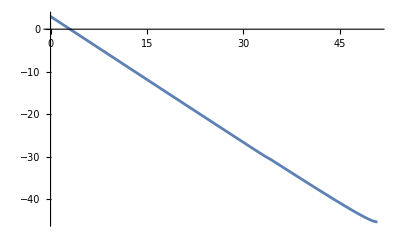

```mathematica
Plot[Log[cs/(kmpc*a[Ne]H[Ne])]/.solNe1,{Ne,0,NeFIN}]
```

```mathematica
Netotal=NeFIN+Nre(*Ntotal=Nend+Nreh*)
```

{75.4944}

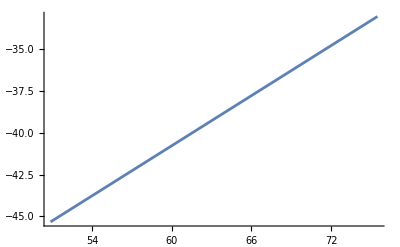

```mathematica
Plot[Log[1/kend[[1]]]+1/2(Ne-NeFIN),{Ne,NeFIN,Netotal[[1]]}]
```

```mathematica
endofinf=Log[cs/(kmpc*a[Ne]H[Ne])]/.solNe1/.Ne->NeFIN (*Log(1/k) at the end of inflation*)
```

{-45.3398}

```mathematica
endofreh=Log[1/kend[[1]]]+1/2(Netotal[[1]]-NeFIN)(*Log(1/k) at the end of reheating (RD start)*)
```

-33.0199

```mathematica
endofrd=endofreh+(100-Netotal[[1]])(*Log(1/k) at the end of RD (MD Start)*)
```

-8.51431

```mathematica
pw=Piecewise[{{Log[cs/(kmpc*(a[Ne]H[Ne])/.solNe1)][[1]],-2<Ne< NeFIN}, 
{endofinf[[1]]+1/2(Ne-NeFIN),NeFIN≤ Ne< Netotal[[1]]},
{endofreh+(Ne-Netotal[[1]]),Netotal[[1]]≤ Ne<100},
{endofrd+ 1/2(Ne-100),100≤ Ne≤130}}]
```

Piecewise[{{Log[(0.000290206 ⅇ^-Ne)/(InterpolatingFunction[…][Ne])], -2<Ne<50.8546}, {-45.3398+1/2 (-50.8546+Ne), 50.8546≤Ne<75.4944}, {-108.514+Ne, 75.4944≤Ne<100}, {-8.51431+1/2 (-100+Ne), 100≤Ne≤130}, {0, True}}]

```mathematica
line1=Line[{{0,-NeFIN},{0,1.2}}];(*Vertucal line at CMB scale*)
line2=Line[{{NeFIN,-NeFIN},{NeFIN,-44}}];(*Vertucal line at Subscript[N, end]*)
line3=Line[{{Netotal[[1]],-NeFIN},{Netotal[[1]],-34}}];(*Vertucal line at the end of reheating (RD start)*)
line4=Line[{{100,-NeFIN},{100,-10}}];(*Vertucal line at the end of RD (MD start)*)
```

```mathematica
kINcmb=Log[1/0.05]
kINpeak=Log[1/kpeak[[1]]]
KINreh=Log[1/kre[[1]]](*critical scale ->  Subscript[k, reh]^-1*)
```

2.99573

-30.2444

-33.0199

```mathematica
Plot[endofinf[[1]]+1/2(Ne-NeFIN),{ Ne,NeFIN, Netotal[[1]]}]
```

-Graphics-

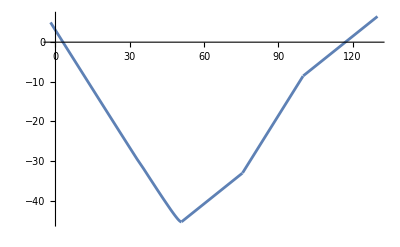

```mathematica
Plot[pw,{Ne,-2,130}]
```

```mathematica
comphi1=Plot[{pw,endofinf[[1]],endofreh,kINcmb,kINpeak,KINreh},{Ne,-2,128},Frame->True,Axes->False,PlotStyle->{{Black,Thickness[0.005]},{Transparent},{Transparent},{Dashing[0.025],Darker[Red]},{Dashing[0.025],Blue}(*,{Dashing[0.025],Blue},{Dashing[0.025],Lighter[Blue]}*),{Dashing[0.025],Darker[Green]}},FrameStyle->Directive[Thickness[0.003]],(*FrameTicks->{{Automatic,None},{None}},*)FrameTicks->{{None,None},{ {{0,"N_*"},{NeFIN,"N_end  "},{NeFIN+Nre[[1]],"  N_reh"},{100,"N_eq"}},None}},Filling->{2->{3}},FillingStyle->{Opacity[0.2,Blue]},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameLabel->{"N=Lna","Comoving Hubble Radius Ln(1/aH)"},Epilog->{Directive[Gray,Dashed],line1,line2,line3,line4,
Text[Style["k_peak^-1",18,FontFamily->"Cambria",Bold,Black],{6.5,-27}],
Text[Style["k_*^-1",18,FontFamily->"Cambria",Bold,Black],{4.65,5.6}],
Text[Style["k_reh^-1",18,FontFamily->"Cambria",Bold,Black],{6.3,-35}],
(*Text[Style["Pivot Scale",10,FontFamily->"Cambria",Black],{2,-19.5},Automatic,{0,6}],*)
(*Text[Style["⟵ End of Inflation",10,FontFamily->"Cambria",Black],{54.9,-17.5},Automatic,{0,6}],*)
Text[Style[" ⟵reh⟶",18,FontFamily->"Cambria",Black],{62,-45},Automatic,{1,0}],
Text[Style[" ⟵RD⟶",18,FontFamily->"Cambria",Black],{87,-45},Automatic,{1,0}],
Text[Style[" ⟵—MD—⟶",18,FontFamily->"Cambria",Black],{114,-45},Automatic,{1,0}]},ImageSize->{600,400}]
```

```mathematica
psreh1n=Show[{reh1,Graphics[{Directive[Gray,Dashed],Line[{{-3,-50},{-3,-20}}],Line[{{30.19,-40},{30.19,-3.4}}],Line[{{45.4,-50},{45.4,-27.5}}]}],Graphics[{Darker[Red],PointSize[0.02],Point[{-3,-20}]}],Graphics[{Darker[Blue],PointSize[0.02],Point[{30.19,-3.25}]}],Graphics[{Darker[Green],PointSize[0.02],Point[{45.4,-27.5}]}]}]
```

```mathematica
Export["reh5.eps",psreh1n];
```

```mathematica
cA=Show[{comphi1,Graphics[{Black,PointSize[0.015],Point[{NeFIN,endofinf[[1]]}],Point[{Netotal[[1]],endofreh}],Point[{100,-8.8}]}],
Graphics[{{Darker[Red],PointSize[0.015],
Point[{0.05,kINcmb}],Point[{123.4,kINcmb}]},{Darker[Blue],PointSize[0.015],
Point[{33.5,kINpeak}],Point[{78,kINpeak}]},{Darker[Green],PointSize[0.015],
Point[{37.,KINreh}],Point[{Netotal[[1]],endofreh}]}(*,
Point[{32.75,kINFree}],Point[{79.,kINFree}]*)}](*,Graphics[{Green,Thick,Circle[{43.8,-22.9},0.5]}]*)},Graphics[{Directive[Gray,Dashed](*,Line[{{-3,-50},{-3,-20}}],Line[{{29.6,-40},{29.6,-3.4}}],Line[{{43.8,-50},{43.8,-23}}]*)}]]
```

```mathematica
Export["com-rehF.eps",cA];
```

#### Solving Tensor Mukhanov Sasaki Equation (16)

```mathematica
nPoints=5;
iMax=(NeFIN-.5)*nPoints;
NeHEt=Table[0+i/nPoints,{i,0,iMax}]//N;
NeBDt=Table[NeHEt[[i]]-1(*If[NeHEt[[i]]≤39,NeHEt[[i]]-5,NeHEt[[i]]-1]*),{i,1,iMax}]//N;
NeEndt=Table[(*NeFIN*)(*If[NeHE[[i]]≤31,NeHE[[i]]+3,NeFIN-.7]*)If[NeHEt[[i]]+1≤NeFIN,NeHEt[[i]]-.64,NeFIN],{i,1,iMax}];
kt=Table[(H[Ne]*a[Ne])/.solNe1/.{Ne->NeHEt[[i]]},{i,1,iMax}]//N;
For[i=1,i≤iMax-(iMax-1),i++,
tAux=AbsoluteTime[];
MSsolAuxt[i]=NDSolve[{((ut''[Ne]+(H'[Ne]/H[Ne]+a'[Ne]/a[Ne])ut'[Ne]+(kt[[i]]/(a[Ne] H[Ne]))^2 ut[Ne]-a''[Ne]/a[Ne] ut[Ne]-a'[Ne]/a[Ne](H'[Ne]/H[Ne]+a'[Ne]/a[Ne])ut[Ne])/.solNe1)==0,ut[NeBD[[i]]]==1/(√(2kt[[i]]))/.solNe1/.{Ne->NeBDt[[i]]},ut'[NeBDt[[i]]]==((-I kt[[i]])/(a[Ne] H[Ne] √2 √kt[[i]]))/.solNe1/.{Ne->NeBDt[[i]]}},{ut[Ne]},{Ne,NeBDt[[i]],NeEndt[[i]]},MaxSteps->Infinity(*Method->{"EquationSimplification"->"Solve"}*)(*,WorkingPrecision->30*)][[1]];Print[NeHEt[[i]]//N,"  ",kt[[i]]//N,"  ",AbsoluteTime[]-tAux]]
MSolt=Table[MSsolAuxt[i],{i,1,iMax}];
j=1;
PNt0=Table[{NeHEt[[i]],((j kt[[i]]^3/Pi^2*Abs[(ut[Ne]/.solNe1)/(a[Ne]/.solNe1)]^2)/.MSolt[[i]]/.Ne->NeEndt[[i]])[[1]][[1]]},{i,1,iMax-(iMax-1)}]
```

0.  {0.0000145103}  1.703368

{{0.,1.2247×10^-10}}

```mathematica
Off[NDSolve::precw];
For[i=1,i≤iMax,i++,
tAux=AbsoluteTime[];
MSsolAuxt[i]=NDSolve[{((ut''[Ne]+(H'[Ne]/H[Ne]+a'[Ne]/a[Ne])ut'[Ne]+(kt[[i]]/(a[Ne] H[Ne]))^2 ut[Ne]-a''[Ne]/a[Ne] ut[Ne]-a'[Ne]/a[Ne](H'[Ne]/H[Ne]+a'[Ne]/a[Ne])ut[Ne])/.solNe1)==0,ut[NeBDt[[i]]]==1/(√(2kt[[i]]))/.solNe1/.{Ne->NeBDt[[i]]},ut'[NeBDt[[i]]]==((-I kt[[i]])/(a[Ne] H[Ne] √2 √kt[[i]]))/.solNe1/.{Ne->NeBDt[[i]]}},{ut[Ne]},{Ne,NeBDt[[i]],NeEndt[[i]]},MaxSteps->Infinity(*Method->{"EquationSimplification"->"Solve"}*)(*,WorkingPrecision->30*)][[1]];Print[NeHEt[[i]]//N,"  ",kt[[i]]//N,"  ",AbsoluteTime[]-tAux]]
MSolt=Table[MSsolAuxt[i],{i,1,iMax}];
```

0.  {0.0000145103}  0.

0.2  {0.0000176916}  0.

0.4  {0.0000215702}  0.015508

0.6  {0.0000262991}  0.

0.8  {0.0000320644}  0.

1.  {0.0000390933}  0.

1.2  {0.0000476627}  0.012506

1.4  {0.0000581103}  0.

1.6  {0.0000708474}  0.003507

1.8  {0.0000863758}  0.

2.  {0.000105307}  0.

2.2  {0.000128387}  0.

2.4  {0.000156523}  0.

2.6  {0.000190825}  0.

2.8  {0.000232642}  0.015713

3.  {0.000283621}  0.

3.2  {0.000345769}  0.

3.4  {0.000421531}  0.

3.6  {0.000513891}  0.

3.8  {0.000626482}  0.015546

4.  {0.000763736}  0.

4.2  {0.000931054}  0.

4.4  {0.00113502}  0.

4.6  {0.00138366}  0.

4.8  {0.00168675}  0.

5.  {0.00205621}  0.015627

5.2  {0.00250659}  0.

5.4  {0.00305559}  0.

5.6  {0.00372481}  0.

5.8  {0.00454056}  0.

6.  {0.00553491}  0.

6.2  {0.00674698}  0.015628

6.4  {0.0082244}  0.

6.6  {0.0100253}  0.

6.8  {0.0122203}  0.

7.  {0.0148959}  0.

7.2  {0.0181572}  0.

7.4  {0.0221322}  0.015636

7.6  {0.0269773}  0.

7.8  {0.0328828}  0.

8.  {0.0400807}  0.

8.2  {0.0488537}  0.

8.4  {0.0595465}  0.018337

8.6  {0.072579}  0.

8.8  {0.088463}  0.

9.  {0.107822}  0.

9.2  {0.131417}  0.

9.4  {0.160174}  0.

9.6  {0.195221}  0.

9.8  {0.237935}  0.

10.  {0.289992}  0.

10.2  {0.353435}  0.

10.4  {0.430753}  0.015646

10.6  {0.524981}  0.

10.8  {0.639815}  0.

11.  {0.779761}  0.

11.2  {0.950307}  0.

11.4  {1.15814}  0.

11.6  {1.41142}  0.015612

11.8  {1.72007}  0.

12.  {2.09619}  0.

12.2  {2.55454}  0.

12.4  {3.11307}  0.

12.6  {3.79367}  0.

12.8  {4.62304}  0.015624

13.  {5.63365}  0.

13.2  {6.86512}  0.

13.4  {8.36569}  0.

13.6  {10.1941}  0.

13.8  {12.4221}  0.

14.  {15.1368}  0.015629

14.2  {18.4445}  0.

14.4  {22.4748}  0.

14.6  {27.3855}  0.

14.8  {33.3688}  0.

15.  {40.6588}  0.

15.2  {49.5409}  0.01571

15.4  {60.3627}  0.

15.6  {73.5474}  0.

15.8  {89.6109}  0.

16.  {109.182}  0.0085953

16.2  {133.025}  0.

16.4  {162.073}  0.

16.6  {197.461}  0.00825

16.8  {240.574}  0.

17.  {293.096}  0.

17.2  {357.08}  0.

17.4  {435.026}  0.

17.6  {529.98}  0.

17.8  {645.651}  0.015064

18.  {786.557}  0.

18.2  {958.202}  0.

18.4  {1167.29}  0.

18.6  {1421.98}  0.

18.8  {1732.21}  0.

19.  {2110.1}  0.015634

19.2  {2570.39}  0.

19.4  {3131.04}  0.

19.6  {3813.92}  0.

19.8  {4645.68}  0.

20.  {5658.73}  0.

20.2  {6892.6}  0.

20.4  {8395.38}  0.015626

20.6  {10225.6}  0.

20.8  {12454.7}  0.

21.  {15169.5}  0.

21.2  {18475.7}  0.

21.4  {22502.1}  0.

21.6  {27405.6}  0.015667

21.8  {33377.1}  0.

22.  {40648.9}  0.

22.2  {49504.3}  0.

22.4  {60287.8}  0.

22.6  {73419.}  0.

22.8  {89408.6}  0.

23.  {108879.}  0.015581

23.2  {132586.}  0.

23.4  {161453.}  0.

23.6  {196601.}  0.

23.8  {239396.}  0.

24.  {291502.}  0.

24.2  {354941.}  0.016013

24.4  {432178.}  0.

24.6  {526212.}  0.

24.8  {640694.}  0.

25.  {780066.}  0.

25.2  {949738.}  0.

25.4  {1.15629×10^6}  0.

25.6  {1.40773×10^6}  0.

25.8  {1.71382×10^6}  0.

26.  {2.08641×10^6}  0.

26.2  {2.53996×10^6}  0.

26.4  {3.09202×10^6}  0.

26.6  {3.76399×10^6}  0.015545

26.8  {4.58189×10^6}  0.

27.  {5.57739×10^6}  0.

27.2  {6.78902×10^6}  0.

27.4  {8.26367×10^6}  0.

27.6  {1.00584×10^7}  0.

27.8  {1.22426×10^7}  0.

28.  {1.49008×10^7}  0.015625

28.2  {1.81357×10^7}  0.

28.4  {2.20723×10^7}  0.

28.6  {2.68627×10^7}  0.

28.8  {3.2692×10^7}  0.

29.  {3.97851×10^7}  0.

29.2  {4.84159×10^7}  0.

29.4  {5.89172×10^7}  0.015627

29.6  {7.16942×10^7}  0.

29.8  {8.72393×10^7}  0.

30.  {1.06152×10^8}  0.

30.2  {1.2916×10^8}  0.

30.4  {1.57149×10^8}  0.

30.6  {1.91198×10^8}  0.

30.8  {2.32616×10^8}  0.015623

31.  {2.82993×10^8}  0.

31.2  {3.44264×10^8}  0.

31.4  {4.18778×10^8}  0.

31.6  {5.09387×10^8}  0.

31.8  {6.19552×10^8}  0.

32.  {7.53472×10^8}  0.

32.2  {9.16208×10^8}  0.01571

32.4  {1.11388×10^9}  0.

32.6  {1.35385×10^9}  0.

32.8  {1.64477×10^9}  0.

33.  {1.99665×10^9}  0.

33.2  {2.4191×10^9}  0.

33.4  {2.85684×10^9}  0.

33.6  {3.34147×10^9}  0.

33.8  {3.95991×10^9}  0.011507

34.  {4.73605×10^9}  0.

34.2  {5.69738×10^9}  0.

34.4  {6.87824×10^9}  0.

34.6  {8.32156×10^9}  0.

34.8  {1.00807×10^10}  0.

35.  {1.22202×10^10}  0.

35.2  {1.48199×10^10}  0.015693

35.4  {1.79767×10^10}  0.

35.6  {2.18077×10^10}  0.

35.8  {2.64557×10^10}  0.

36.  {3.20936×10^10}  0.

36.2  {3.89313×10^10}  0.

36.4  {4.72228×10^10}  0.

36.6  {5.72759×10^10}  0.015656

36.8  {6.94629×10^10}  0.

37.  {8.42351×10^10}  0.

37.2  {1.02139×10^11}  0.

37.4  {1.23835×10^11}  0.

37.6  {1.50123×10^11}  0.

37.8  {1.81972×10^11}  0.

38.  {2.20553×10^11}  0.

38.2  {2.67283×10^11}  0.015626

38.4  {3.23872×10^11}  0.

38.6  {3.92394×10^11}  0.

38.8  {4.7535×10^11}  0.

39.  {5.75766×10^11}  0.

39.2  {6.97297×10^11}  0.

39.4  {8.44357×10^11}  0.

39.6  {1.02228×10^12}  0.015618

39.8  {1.2375×10^12}  0.

40.  {1.49779×10^12}  0.

40.2  {1.81252×10^12}  0.

40.4  {2.19301×10^12}  0.

40.6  {2.65289×10^12}  0.

40.8  {3.20862×10^12}  0.

41.  {3.88×10^12}  0.

41.2  {4.69093×10^12}  0.015624

41.4  {5.67015×10^12}  0.

41.6  {6.85228×10^12}  0.

41.8  {8.27899×10^12}  0.

42.  {1.00004×10^13}  0.

42.2  {1.20766×10^13}  0.01059

42.4  {1.45802×10^13}  0.

42.6  {1.7598×10^13}  0.

42.8  {2.12344×10^13}  0.0055077

43.  {2.56145×10^13}  0.

43.2  {3.08884×10^13}  0.

43.4  {3.7236×10^13}  0.

43.6  {4.48723×10^13}  0.

43.8  {5.40551×10^13}  0.

44.  {6.5092×10^13}  0.

44.2  {7.83507×10^13}  0.01563

44.4  {9.42698×10^13}  0.

44.6  {1.13372×10^14}  0.

44.8  {1.36278×10^14}  0.

45.  {1.63728×10^14}  0.

45.2  {1.96598×10^14}  0.

45.4  {2.3593×10^14}  0.

45.6  {2.82952×10^14}  0.015713

45.8  {3.39118×10^14}  0.

46.  {4.0614×10^14}  0.

46.2  {4.8603×10^14}  0.

46.4  {5.81144×10^14}  0.

46.6  {6.94239×10^14}  0.

46.8  {8.2852×10^14}  0.

47.  {9.87704×10^14}  0.015587

47.2  {1.17607×10^15}  0.

47.4  {1.39852×10^15}  0.

47.6  {1.66063×10^15}  0.

47.8  {1.96867×10^15}  0.

48.  {2.32963×10^15}  0.

48.2  {2.75117×10^15}  0.

48.4  {3.24152×10^15}  0.

48.6  {3.80926×10^15}  0.

48.8  {4.46295×10^15}  0.015578

49.  {5.21042×10^15}  0.

49.2  {6.05775×10^15}  0.

49.4  {7.00772×10^15}  0.

49.6  {8.05763×10^15}  0.

49.8  {9.19633×10^15}  0.

50.  {1.03979×10^16}  0.

```mathematica
PNt=Table[{NeHEt[[i]],((j kt[[i]]^3/Pi^2*Abs[ut[Ne]/.solNe1]^2/a[Ne]^2)/.MSolt[[i]]/.Ne->NeEndt[[i]])[[1]][[1]]},{i,1,iMax}]
```

{{0.,4.61573×10^-11},{0.2,4.59943×10^-11},{0.4,4.58312×10^-11},{0.6,4.56682×10^-11},{0.8,4.55052×10^-11},{1.,4.53422×10^-11},{1.2,4.51791×10^-11},{1.4,4.50161×10^-11},{1.6,4.4853×10^-11},{1.8,4.469×10^-11},{2.,4.45269×10^-11},{2.2,4.43638×10^-11},{2.4,4.42007×10^-11},{2.6,4.40376×10^-11},{2.8,4.38745×10^-11},{3.,4.37114×10^-11},{3.2,4.35483×10^-11},{3.4,4.33851×10^-11},{3.6,4.3222×10^-11},{3.8,4.30589×10^-11},{4.,4.28957×10^-11},{4.2,4.27326×10^-11},{4.4,4.25694×10^-11},{4.6,4.24062×10^-11},{4.8,4.2243×10^-11},{5.,4.20798×10^-11},{5.2,4.19166×10^-11},{5.4,4.17534×10^-11},{5.6,4.15902×10^-11},{5.8,4.1427×10^-11},{6.,4.12637×10^-11},{6.2,4.11005×10^-11},{6.4,4.09373×10^-11},{6.6,4.0774×10^-11},{6.8,4.06108×10^-11},{7.,4.04475×10^-11},{7.2,4.02843×10^-11},{7.4,4.0121×10^-11},{7.6,3.99577×10^-11},{7.8,3.97944×10^-11},{8.,3.96311×10^-11},{8.2,3.94678×10^-11},{8.4,3.93045×10^-11},{8.6,3.91411×10^-11},{8.8,3.89778×10^-11},{9.,3.88145×10^-11},{9.2,3.86511×10^-11},{9.4,3.84878×10^-11},{9.6,3.83244×10^-11},{9.8,3.8161×10^-11},{10.,3.79977×10^-11},{10.2,3.78343×10^-11},{10.4,3.76709×10^-11},{10.6,3.75075×10^-11},{10.8,3.73441×10^-11},{11.,3.71807×10^-11},{11.2,3.70173×10^-11},{11.4,3.68538×10^-11},{11.6,3.66904×10^-11},{11.8,3.6527×10^-11},{12.,3.63635×10^-11},{12.2,3.62001×10^-11},{12.4,3.60366×10^-11},{12.6,3.58732×10^-11},{12.8,3.57097×10^-11},{13.,3.55462×10^-11},{13.2,3.53827×10^-11},{13.4,3.52192×10^-11},{13.6,3.50557×10^-11},{13.8,3.48922×10^-11},{14.,3.47287×10^-11},{14.2,3.45652×10^-11},{14.4,3.44017×10^-11},{14.6,3.42381×10^-11},{14.8,3.40746×10^-11},{15.,3.3911×10^-11},{15.2,3.37475×10^-11},{15.4,3.35839×10^-11},{15.6,3.34204×10^-11},{15.8,3.32568×10^-11},{16.,3.30932×10^-11},{16.2,3.29296×10^-11},{16.4,3.2766×10^-11},{16.6,3.26024×10^-11},{16.8,3.24388×10^-11},{17.,3.22752×10^-11},{17.2,3.21116×10^-11},{17.4,3.1948×10^-11},{17.6,3.17844×10^-11},{17.8,3.16207×10^-11},{18.,3.14571×10^-11},{18.2,3.12935×10^-11},{18.4,3.11298×10^-11},{18.6,3.09662×10^-11},{18.8,3.08025×10^-11},{19.,3.06388×10^-11},{19.2,3.04752×10^-11},{19.4,3.03115×10^-11},{19.6,3.01478×10^-11},{19.8,2.99841×10^-11},{20.,2.98204×10^-11},{20.2,2.96567×10^-11},{20.4,2.9493×10^-11},{20.6,2.93293×10^-11},{20.8,2.91656×10^-11},{21.,2.90019×10^-11},{21.2,2.88381×10^-11},{21.4,2.86744×10^-11},{21.6,2.85106×10^-11},{21.8,2.83469×10^-11},{22.,2.81832×10^-11},{22.2,2.80194×10^-11},{22.4,2.78556×10^-11},{22.6,2.76919×10^-11},{22.8,2.75281×10^-11},{23.,2.73643×10^-11},{23.2,2.72005×10^-11},{23.4,2.70367×10^-11},{23.6,2.68729×10^-11},{23.8,2.67091×10^-11},{24.,2.65453×10^-11},{24.2,2.63815×10^-11},{24.4,2.62177×10^-11},{24.6,2.60538×10^-11},{24.8,2.589×10^-11},{25.,2.57261×10^-11},{25.2,2.55623×10^-11},{25.4,2.53984×10^-11},{25.6,2.52345×10^-11},{25.8,2.50706×10^-11},{26.,2.49067×10^-11},{26.2,2.47428×10^-11},{26.4,2.45788×10^-11},{26.6,2.44149×10^-11},{26.8,2.42509×10^-11},{27.,2.40869×10^-11},{27.2,2.39228×10^-11},{27.4,2.37588×10^-11},{27.6,2.35947×10^-11},{27.8,2.34306×10^-11},{28.,2.32667×10^-11},{28.2,2.31028×10^-11},{28.4,2.29389×10^-11},{28.6,2.27751×10^-11},{28.8,2.26113×10^-11},{29.,2.24474×10^-11},{29.2,2.22835×10^-11},{29.4,2.21195×10^-11},{29.6,2.19554×10^-11},{29.8,2.17912×10^-11},{30.,2.16269×10^-11},{30.2,2.14624×10^-11},{30.4,2.12978×10^-11},{30.6,2.1133×10^-11},{30.8,2.0968×10^-11},{31.,2.08025×10^-11},{31.2,2.06364×10^-11},{31.4,2.04694×10^-11},{31.6,2.03011×10^-11},{31.8,2.01312×10^-11},{32.,1.99589×10^-11},{32.2,1.97826×10^-11},{32.4,1.96005×10^-11},{32.6,1.941×10^-11},{32.8,1.92046×10^-11},{33.,1.89721×10^-11},{33.2,1.86716×10^-11},{33.4,1.7486×10^-11},{33.6,1.60695×10^-11},{33.8,1.51439×10^-11},{34.,1.45092×10^-11},{34.2,1.39393×10^-11},{34.4,1.35475×10^-11},{34.6,1.33411×10^-11},{34.8,1.31568×10^-11},{35.,1.29808×10^-11},{35.2,1.28097×10^-11},{35.4,1.26415×10^-11},{35.6,1.24748×10^-11},{35.8,1.23089×10^-11},{36.,1.21438×10^-11},{36.2,1.19792×10^-11},{36.4,1.1815×10^-11},{36.6,1.1651×10^-11},{36.8,1.14871×10^-11},{37.,1.13233×10^-11},{37.2,1.11596×10^-11},{37.4,1.0996×10^-11},{37.6,1.08324×10^-11},{37.8,1.06688×10^-11},{38.,1.05054×10^-11},{38.2,1.0342×10^-11},{38.4,1.01786×10^-11},{38.6,1.00153×10^-11},{38.8,9.85196×10^-12},{39.,9.68868×10^-12},{39.2,9.52543×10^-12},{39.4,9.36222×10^-12},{39.6,9.19901×10^-12},{39.8,9.03584×10^-12},{40.,8.87268×10^-12},{40.2,8.70957×10^-12},{40.4,8.54649×10^-12},{40.6,8.38344×10^-12},{40.8,8.22043×10^-12},{41.,8.05747×10^-12},{41.2,7.89455×10^-12},{41.4,7.73167×10^-12},{41.6,7.56884×10^-12},{41.8,7.40607×10^-12},{42.,7.24334×10^-12},{42.2,7.08065×10^-12},{42.4,6.92122×10^-12},{42.6,6.75856×10^-12},{42.8,6.59595×10^-12},{43.,6.43321×10^-12},{43.2,6.27074×10^-12},{43.4,6.10833×10^-12},{43.6,5.946×10^-12},{43.8,5.78391×10^-12},{44.,5.62175×10^-12},{44.2,5.45971×10^-12},{44.4,5.2978×10^-12},{44.6,5.13588×10^-12},{44.8,4.97431×10^-12},{45.,4.8127×10^-12},{45.2,4.65123×10^-12},{45.4,4.48976×10^-12},{45.6,4.32868×10^-12},{45.8,4.16753×10^-12},{46.,4.00679×10^-12},{46.2,3.84606×10^-12},{46.4,3.68562×10^-12},{46.6,3.52552×10^-12},{46.8,3.36549×10^-12},{47.,3.20593×10^-12},{47.2,3.04654×10^-12},{47.4,2.88747×10^-12},{47.6,2.72873×10^-12},{47.8,2.5703×10^-12},{48.,2.41238×10^-12},{48.2,2.25489×10^-12},{48.4,2.09797×10^-12},{48.6,1.94171×10^-12},{48.8,1.78623×10^-12},{49.,1.6316×10^-12},{49.2,1.47792×10^-12},{49.4,1.32531×10^-12},{49.6,1.1741×10^-12},{49.8,1.0247×10^-12},{50.,2.45741×10^-13}}

```mathematica
PNt[[1,2]]/PN0[[1,2]]
```

0.0213313

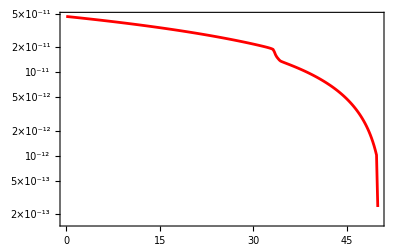

```mathematica
ListLogPlot[PNt(*,PlotRange->{{0,60},{3*10^-13,2*10^-11}}*),Joined->True,Frame->True,PlotStyle->Red]
```

```mathematica
kmpct=Solve[0.002/Mpct==(a[Ne] H[Ne])/.solNe1/.Ne->0,Mpct][[1]][[1,2]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

137.833

```mathematica
Pkt=Table[{(kmpct(H[Ne]a[Ne])/.solNe1/.{Ne->NeHEt[[i]]})[[1]],(j kt[[i]]^3/Pi^2*Abs[(ut[Ne]/.solNe1)/(a[Ne]/.solNe1)]^2/.MSolt[[i]]/.Ne->NeEndt[[i]])[[1]][[1]]},{i,1,iMax}]
```

{{0.002,4.61573×10^-11},{0.00243849,4.59943×10^-11},{0.00297309,4.58312×10^-11},{0.00362488,4.56682×10^-11},{0.00441953,4.55052×10^-11},{0.00538836,4.53422×10^-11},{0.00656951,4.51791×10^-11},{0.00800953,4.50161×10^-11},{0.00976513,4.4853×10^-11},{0.0119055,4.469×10^-11},{0.0145148,4.45269×10^-11},{0.0176959,4.43638×10^-11},{0.0215741,4.42007×10^-11},{0.026302,4.40376×10^-11},{0.0320658,4.38745×10^-11},{0.0390924,4.37114×10^-11},{0.0476584,4.35483×10^-11},{0.058101,4.33851×10^-11},{0.0708312,4.3222×10^-11},{0.08635,4.30589×10^-11},{0.105268,4.28957×10^-11},{0.12833,4.27326×10^-11},{0.156443,4.25694×10^-11},{0.190714,4.24062×10^-11},{0.23249,4.2243×10^-11},{0.283415,4.20798×10^-11},{0.345492,4.19166×10^-11},{0.421162,4.17534×10^-11},{0.513402,4.15902×10^-11},{0.62584,4.1427×10^-11},{0.762895,4.12637×10^-11},{0.929958,4.11005×10^-11},{1.1336,4.09373×10^-11},{1.38181,4.0774×10^-11},{1.68437,4.06108×10^-11},{2.05315,4.04475×10^-11},{2.50266,4.02843×10^-11},{3.05056,4.0121×10^-11},{3.71837,3.99577×10^-11},{4.53234,3.97944×10^-11},{5.52445,3.96311×10^-11},{6.73366,3.94678×10^-11},{8.20748,3.93045×10^-11},{10.0038,3.91411×10^-11},{12.1931,3.89778×10^-11},{14.8615,3.88145×10^-11},{18.1137,3.86511×10^-11},{22.0773,3.84878×10^-11},{26.908,3.83244×10^-11},{32.7954,3.8161×10^-11},{39.9705,3.79977×10^-11},{48.7151,3.78343×10^-11},{59.3721,3.76709×10^-11},{72.3598,3.75075×10^-11},{88.1878,3.73441×10^-11},{107.477,3.71807×10^-11},{130.984,3.70173×10^-11},{159.631,3.68538×10^-11},{194.541,3.66904×10^-11},{237.083,3.6527×10^-11},{288.925,3.63635×10^-11},{352.1,3.62001×10^-11},{429.084,3.60366×10^-11},{522.894,3.58732×10^-11},{637.208,3.57097×10^-11},{776.505,3.55462×10^-11},{946.242,3.53827×10^-11},{1153.07,3.52192×10^-11},{1405.09,3.50557×10^-11},{1712.17,3.48922×10^-11},{2086.35,3.47287×10^-11},{2542.27,3.45652×10^-11},{3097.78,3.44017×10^-11},{3774.64,3.42381×10^-11},{4599.33,3.40746×10^-11},{5604.14,3.3911×10^-11},{6828.39,3.37475×10^-11},{8319.98,3.35839×10^-11},{10137.3,3.34204×10^-11},{12351.4,3.32568×10^-11},{15048.9,3.30932×10^-11},{18335.2,3.29296×10^-11},{22339.,3.2766×10^-11},{27216.8,3.26024×10^-11},{33159.1,3.24388×10^-11},{40398.4,3.22752×10^-11},{49217.5,3.21116×10^-11},{59961.1,3.1948×10^-11},{73048.9,3.17844×10^-11},{88992.2,3.16207×10^-11},{108414.,3.14571×10^-11},{132072.,3.12935×10^-11},{160891.,3.11298×10^-11},{195995.,3.09662×10^-11},{238756.,3.08025×10^-11},{290842.,3.06388×10^-11},{354285.,3.04752×10^-11},{431561.,3.03115×10^-11},{525685.,3.01478×10^-11},{640329.,2.99841×10^-11},{779962.,2.98204×10^-11},{950030.,2.96567×10^-11},{1.15716×10^6,2.9493×10^-11},{1.40943×10^6,2.93293×10^-11},{1.71668×10^6,2.91656×10^-11},{2.09086×10^6,2.90019×10^-11},{2.54657×10^6,2.88381×10^-11},{3.10154×10^6,2.86744×10^-11},{3.7774×10^6,2.85106×10^-11},{4.60047×10^6,2.83469×10^-11},{5.60277×10^6,2.81832×10^-11},{6.82334×10^6,2.80194×10^-11},{8.30966×10^6,2.78556×10^-11},{1.01196×10^7,2.76919×10^-11},{1.23235×10^7,2.75281×10^-11},{1.50071×10^7,2.73643×10^-11},{1.82748×10^7,2.72005×10^-11},{2.22536×10^7,2.70367×10^-11},{2.70982×10^7,2.68729×10^-11},{3.29968×10^7,2.67091×10^-11},{4.01786×10^7,2.65453×10^-11},{4.89227×10^7,2.63815×10^-11},{5.95685×10^7,2.62177×10^-11},{7.25296×10^7,2.60538×10^-11},{8.83089×10^7,2.589×10^-11},{1.07519×10^8,2.57261×10^-11},{1.30905×10^8,2.55623×10^-11},{1.59375×10^8,2.53984×10^-11},{1.94033×10^8,2.52345×10^-11},{2.36221×10^8,2.50706×10^-11},{2.87577×10^8,2.49067×10^-11},{3.5009×10^8,2.47428×10^-11},{4.26183×10^8,2.45788×10^-11},{5.18803×10^8,2.44149×10^-11},{6.31537×10^8,2.42509×10^-11},{7.6875×10^8,2.40869×10^-11},{9.35753×10^8,2.39228×10^-11},{1.13901×10^9,2.37588×10^-11},{1.38638×10^9,2.35947×10^-11},{1.68744×10^9,2.34306×10^-11},{2.05382×10^9,2.32667×10^-11},{2.4997×10^9,2.31028×10^-11},{3.04229×10^9,2.29389×10^-11},{3.70257×10^9,2.27751×10^-11},{4.50604×10^9,2.26113×10^-11},{5.48371×10^9,2.24474×10^-11},{6.67331×10^9,2.22835×10^-11},{8.12075×10^9,2.21195×10^-11},{9.88184×10^9,2.19554×10^-11},{1.20245×10^10,2.17912×10^-11},{1.46312×10^10,2.16269×10^-11},{1.78025×10^10,2.14624×10^-11},{2.16604×10^10,2.12978×10^-11},{2.63534×10^10,2.1133×10^-11},{3.20622×10^10,2.0968×10^-11},{3.90059×10^10,2.08025×10^-11},{4.7451×10^10,2.06364×10^-11},{5.77215×10^10,2.04694×10^-11},{7.02104×10^10,2.03011×10^-11},{8.53949×10^10,2.01312×10^-11},{1.03854×10^11,1.99589×10^-11},{1.26284×10^11,1.97826×10^-11},{1.5353×10^11,1.96005×10^-11},{1.86605×10^11,1.941×10^-11},{2.26704×10^11,1.92046×10^-11},{2.75205×10^11,1.89721×10^-11},{3.33432×10^11,1.86716×10^-11},{3.93767×10^11,1.7486×10^-11},{4.60565×10^11,1.60695×10^-11},{5.45808×10^11,1.51439×10^-11},{6.52785×10^11,1.45092×10^-11},{7.85288×10^11,1.39393×10^-11},{9.48051×10^11,1.35475×10^-11},{1.14699×10^12,1.33411×10^-11},{1.38945×10^12,1.31568×10^-11},{1.68435×10^12,1.29808×10^-11},{2.04268×10^12,1.28097×10^-11},{2.47778×10^12,1.26415×10^-11},{3.00583×10^12,1.24748×10^-11},{3.64647×10^12,1.23089×10^-11},{4.42357×10^12,1.21438×10^-11},{5.36602×10^12,1.19792×10^-11},{6.50887×10^12,1.1815×10^-11},{7.89452×10^12,1.1651×10^-11},{9.5743×10^12,1.14871×10^-11},{1.16104×10^13,1.13233×10^-11},{1.40781×10^13,1.11596×10^-11},{1.70685×10^13,1.0996×10^-11},{2.0692×10^13,1.08324×10^-11},{2.50819×10^13,1.06688×10^-11},{3.03996×10^13,1.05054×10^-11},{3.68404×10^13,1.0342×10^-11},{4.46404×10^13,1.01786×10^-11},{5.40849×10^13,1.00153×10^-11},{6.55191×10^13,9.85196×10^-12},{7.93597×10^13,9.68868×10^-12},{9.61107×10^13,9.52543×10^-12},{1.1638×10^14,9.36222×10^-12},{1.40904×10^14,9.19901×10^-12},{1.70568×10^14,9.03584×10^-12},{2.06445×10^14,8.87268×10^-12},{2.49825×10^14,8.70957×10^-12},{3.02269×10^14,8.54649×10^-12},{3.65656×10^14,8.38344×10^-12},{4.42254×10^14,8.22043×10^-12},{5.34793×10^14,8.05747×10^-12},{6.46566×10^14,7.89455×10^-12},{7.81535×10^14,7.73167×10^-12},{9.44472×10^14,7.56884×10^-12},{1.14112×10^15,7.40607×10^-12},{1.37838×10^15,7.24334×10^-12},{1.66456×10^15,7.08065×10^-12},{2.00964×10^15,6.92122×10^-12},{2.42559×10^15,6.75856×10^-12},{2.9268×10^15,6.59595×10^-12},{3.53053×10^15,6.43321×10^-12},{4.25745×10^15,6.27074×10^-12},{5.13235×10^15,6.10833×10^-12},{6.1849×10^15,5.946×10^-12},{7.45059×10^15,5.78391×10^-12},{8.97184×10^15,5.62175×10^-12},{1.07993×10^16,5.45971×10^-12},{1.29935×10^16,5.2978×10^-12},{1.56264×10^16,5.13588×10^-12},{1.87837×10^16,4.97431×10^-12},{2.25671×10^16,4.8127×10^-12},{2.70978×10^16,4.65123×10^-12},{3.25189×10^16,4.48976×10^-12},{3.90002×10^16,4.32868×10^-12},{4.67417×10^16,4.16753×10^-12},{5.59796×10^16,4.00679×10^-12},{6.69911×10^16,3.84606×10^-12},{8.0101×10^16,3.68562×10^-12},{9.56892×10^16,3.52552×10^-12},{1.14198×10^17,3.36549×10^-12},{1.36138×10^17,3.20593×10^-12},{1.62101×10^17,3.04654×10^-12},{1.92762×10^17,2.88747×10^-12},{2.28889×10^17,2.72873×10^-12},{2.71348×10^17,2.5703×10^-12},{3.211×10^17,2.41238×10^-12},{3.79202×10^17,2.25489×10^-12},{4.46789×10^17,2.09797×10^-12},{5.25043×10^17,1.94171×10^-12},{6.15143×10^17,1.78623×10^-12},{7.18169×10^17,1.6316×10^-12},{8.34959×10^17,1.47792×10^-12},{9.65897×10^17,1.32531×10^-12},{1.11061×10^18,1.1741×10^-12},{1.26756×10^18,1.0247×10^-12},{1.43318×10^18,2.45741×10^-13}}

```mathematica
ct=Interpolation[Pkt,InterpolationOrder->1]
AAt=LogLogPlot[{ct[x]},{x,0.002,4*^20}(*,PlotRange->{{0.001,4*10^22},{10^-12,1}}*),Frame->True,FrameStyle->Thick,FrameTicksStyle->Black,PlotStyle->Brown,LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],ImageSize->{600,400},AspectRatio->Full,Axes->False,FrameLabel->{"k/Mpc^-1","P_t"}(*,RotateLabel->True,PlotLegends->{Placed[LineLegend[{{Red},{Darker[Green]},Blue,Purple},{"Case A","Case B ","Case C","Case D"},LabelStyle->{14,FontFamily->"Cambria"},LegendLayout->"Column",LegendMarkerSize->{{30,20}}],{0.18,0.3}]}*)]
```

InterpolatingFunction[…]

```mathematica
ct[0.05kmpct]
```

3.94503×10^-11

```mathematica
c1[0.05kmpc]
```

1.70274×10^-9

```mathematica
ct[0.05kmpct]/(c1[0.05kmpc](*2.1*10^-9*))
```

0.0231687

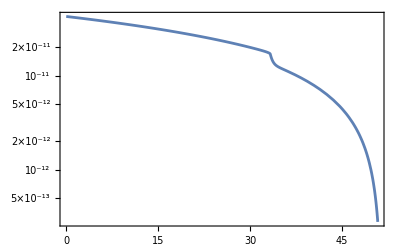

```mathematica
LogPlot[(2 H[Ne]^2/.solNe1)/Pi^2,{Ne,0,NeFIN},PlotRange->All,Frame->True]
```

```mathematica
(((2 H[Ne]^2/.solNe1)/Pi^2)[[1]]/.Ne->0)/(c1[0.05kmpc](*2.1*10^-9*))
```

0.0250573

## RESULTS

```mathematica
SetDirectory[NotebookDirectory[]];
```

### observation data

#### f_PBH

```mathematica
cmb=Import["cmb.dat"];
eva=Import["Evaporation.dat"];
egrb=Import["egrb.dat"];
ligo=Import["ligo.dat"];
EROS=Import["EROS.dat"];
hsc=Import["hsc.dat"];
hsc1=Import["hsc1.dat"];
ogle=Import["ogle.dat"];
Micro=Import["Microlensing.dat"];
cm21=Import["21cm.dat"];
kep=Import["kepler.dat"];
```

Import::nffil: File 21cm.dat not found during Import.

### omega

```mathematica
ska=Import["plis_ska.dat"];
lisa=Import["plis_LISA.dat"];
dec=Import["plis_DECIGO.dat"];
bbo=Import["plis_BBO.dat"];
ppta=Import["plis_ppta.dat"];
epta=Import["plis_EPTA.dat"];
ipta=Import["plis_ipta.dat"];

ce=Import["plis_CE.dat"];
et=Import["plis_ET.dat"];
hl=Import["plis_HL.dat"];
ngr=Import["plis_NANOGrav.dat"];
```

### Power Spectrum

```mathematica
PkA=Import["PkA.dat"];
PkB=Import["PkB.dat"];
PkC=Import["PkC.dat"];
PkD=Import["PkD.dat"];
PkF=Import["PkF.dat"];
```

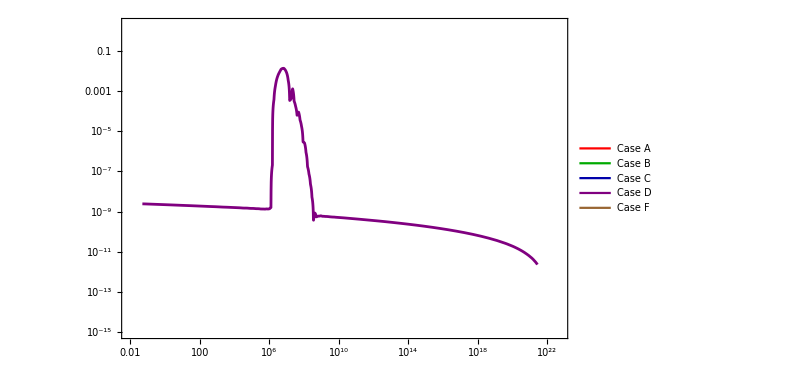

```mathematica
pra=Interpolation[PkA,InterpolationOrder->1];
prb=Interpolation[PkB,InterpolationOrder->1];
prc=Interpolation[PkC,InterpolationOrder->1];
prd=Interpolation[PkD,InterpolationOrder->1];
prf=Interpolation[PkF,InterpolationOrder->1];
qenda=pra[[1,1,2]];
qendb=prb[[1,1,2]];
qendc=prc[[1,1,2]];
qendd=prd[[1,1,2]];
qendf=prf[[1,1,2]];
      CaseF=LogLogPlot[prf[x],{x,0.05,qendf},PlotRange->{{0.01,qendd*10},{10^-15,2}},PlotStyle->{Brown}];
CaseA=LogLogPlot[pra[x],{x,0.05,qenda},PlotRange->{{0.01,qenda*10},{10^-15,2}},PlotStyle->{Red}];
CaseB=LogLogPlot[prb[x],{x,0.05,qendb},PlotRange->{{0.01,qendb*10},{10^-15,2}},PlotStyle->{Darker[Green]}];
CaseC=LogLogPlot[prc[x],{x,0.05,qendc},PlotRange->{{0.01,qendc*10},{10^-15,2}},PlotStyle->{Darker[Blue]}];
CaseD=LogLogPlot[prd[x],{x,0.05,qendc},PlotRange->{{0.01,qendd*10},{10^-15,2}},PlotStyle->{Purple},
PlotLegends->{Placed[LineLegend[{{Red},{Darker[Green]},Darker[Blue],Purple,Brown},{"Case A","Case B ","Case C","Case D","Case F"},LabelStyle->{14,FontFamily->"Cambria"},LegendLayout->"Column",LegendMarkerSize->{{30,1}}],{0.9,0.75}]},Frame->True,ImageSize->{600,400}]
```

```mathematica
ps=-Graphics-;
```

```mathematica
psback=Show[{LogLogPlot[{ns0[Ne]},{Ne,1,10},PlotRange->{{10^-2.6,10^21},{10^-11,10^0}},PlotStyle->{Black,Thickness[0.005]},Frame-> True,FrameLabel->{"k/Mpc^-1","P_R"},LabelStyle->Directive[20,Bold,Black,FontFamily->"Book Antiqua"],FrameStyle->Thick,FrameTicksStyle->Black,ImageSize->{600,400},AspectRatio->Full],Graphics[{Texture[ps],EdgeForm[Black],Polygon[{{-6.02,-25.44},{48.295,-25.44},{48.295,0.02},{-6.02,0.02}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},ImageSize->{400,300},AspectRatio->Full]},Axes->False,RotateLabel->True];
```

```mathematica
pss=Show[psback,CaseA,CaseB,CaseC,CaseD,CaseF]
```

-Graphics-

```mathematica
Export["ps.eps",pss];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
f1=Import["FPBHA.dat"];
f2=Import["FPBHB.dat"];
f3=Import["FPBHC.dat"];
f4=Import["FPBHF.dat"];
```

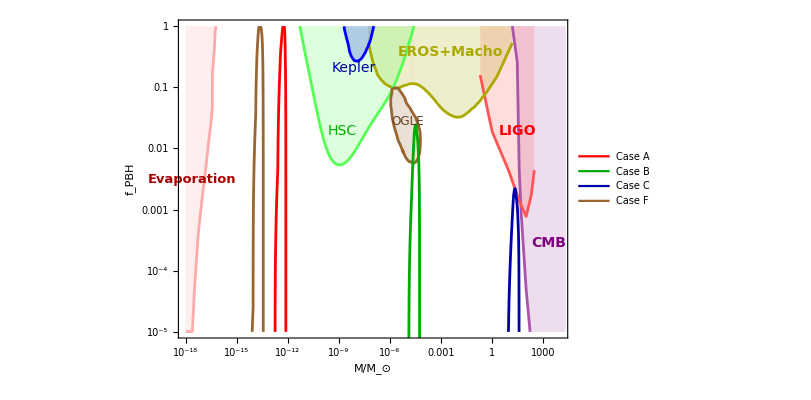

```mathematica
s1=Interpolation[f1,InterpolationOrder->3];
s2=Interpolation[f2,InterpolationOrder->3];
s3=Interpolation[f3,InterpolationOrder->3];
s4=Interpolation[f4,InterpolationOrder->3];
fc1=LogLogPlot[s1[x],{x,1.*^-13,9.93001*^-13},Frame->True,Axes->False,PlotRange->{{10^-1,5*10^3},{10^-5,10^0}},PlotStyle->Red,FillingStyle->Black,ImageSize->{600,400}];
fc2=LogLogPlot[s2[x],{x,1.1*^-5,5.8*^-5},Frame->True,Axes->False,PlotRange->{{10^-18,10^4},{10^-6,10^0}},PlotStyle->Darker[Green],FillingStyle->Black,ImageSize->{600,400}];
fc3=LogLogPlot[s3[x],{x,.9*^1,4.5*^1},Frame->True,Axes->False,PlotRange->{{10^-1,5*10^3},{10^-5,10^0}},PlotStyle->Darker[Blue],FillingStyle->Black,ImageSize->{600,400}];
fc4=LogLogPlot[s4[x],{x,7.1*^-15,3.8*^-14},Frame->True,Axes->False,PlotRange->{{10^-1,5*10^3},{10^-5,10^0}},PlotStyle->Brown,FillingStyle->Black,ImageSize->{600,400}];
cmb=Import["cmb.dat"];
eva=Import["Evaporation.dat"];
egrb=Import["egrb.dat"];
ligo=Import["ligo.dat"];
EROS=Import["EROS.dat"];
hsc=Import["hsc.dat"];
hsc1=Import["hsc1.dat"];
ogle=Import["ogle.dat"];
Micro=Import["Microlensing.dat"];
cm21=Import["21cm.dat"];
kep=Import["kepler.dat"];
AA=ListLogLogPlot[{cmb,eva,ligo,EROS,hsc,ogle,kep},PlotRange->{{10^-18,10^4},{10^-5,10^0}},Joined->True,Filling->Top,Frame->True,PlotStyle->{Lighter[Purple],Lighter[Pink],Lighter[Red],Darker[Yellow],Lighter[Green],Brown,Blue},Epilog->{Text[Style["CMB",14,FontFamily->"Cambria",Bold,Purple],Scaled[{.95,0.3}]],Text[Style["LIGO",14,FontFamily->"Cambria",Bold,Red],Scaled[{.87,0.65}]],Text[Style["EROS+Macho",14,FontFamily->"Cambria",Bold,Darker[Yellow]],Scaled[{.7,0.9}]],Text[Style["HSC",14,FontFamily->"Cambria",Darker[Green]],Scaled[{.42,0.65}]],
Text[Style["Kepler",14,FontFamily->"Cambria",Darker[Blue]],Scaled[{.45,0.85}]],
Inset[Style["OGLE",12,FontFamily->"Cambria",Darker[Brown]],Scaled[{.59,0.68}],Automatic,Automatic,{1,-1.6}],Inset[Style["Evaporation",13,FontFamily->"Cambria",Bold,Darker[Red]],Scaled[{.036,0.5}],Automatic,Automatic,{.1,.6}]},PlotLegends->{Placed[LineLegend[{{Red},{Darker[Green]},Darker[Blue],Brown},{"Case A","Case B ","Case C","Case F"},LabelStyle->{13,FontFamily->"Cambria"},LegendLayout->"Column",LegendMarkerSize->{{20,20}}],{0.41,0.3}]}];
Fback=Show[AA,Frame-> True,FrameLabel->{"M/M_⊙","f_PBH"},LabelStyle->Directive[20,Bold,Black,FontFamily->"Cambria"],FrameStyle->Thick,FrameTicksStyle->Black,AspectRatio->Full];
fpbh=Show[Fback,fc3,fc2,fc1,fc4,ImageSize->{600,400}]
```

```mathematica
Export["fpbh.eps",fpbh];
```

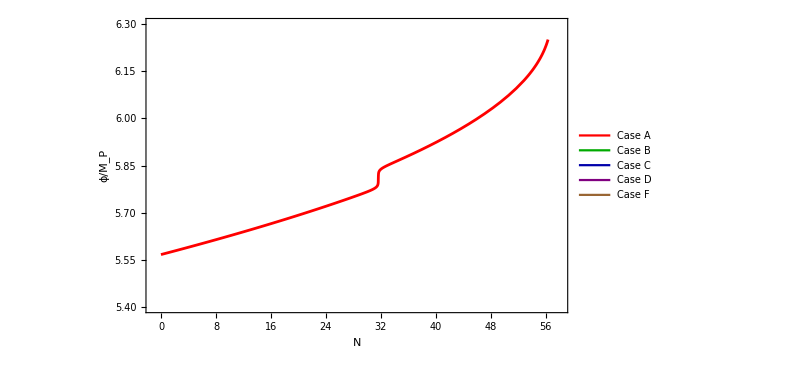
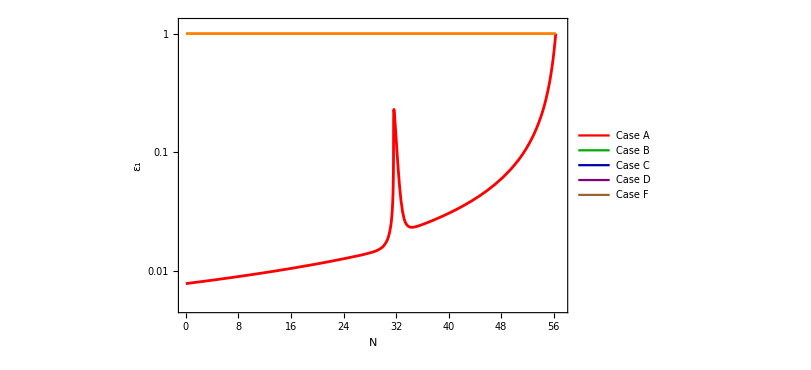
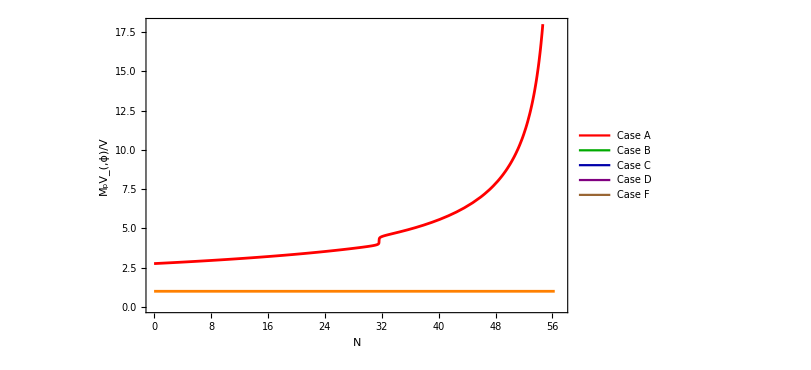
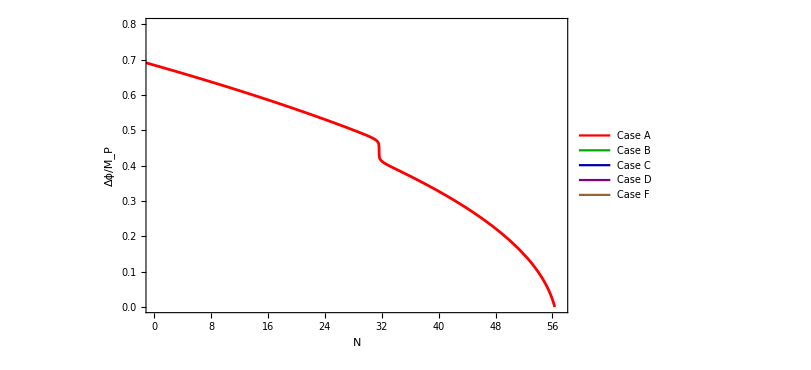
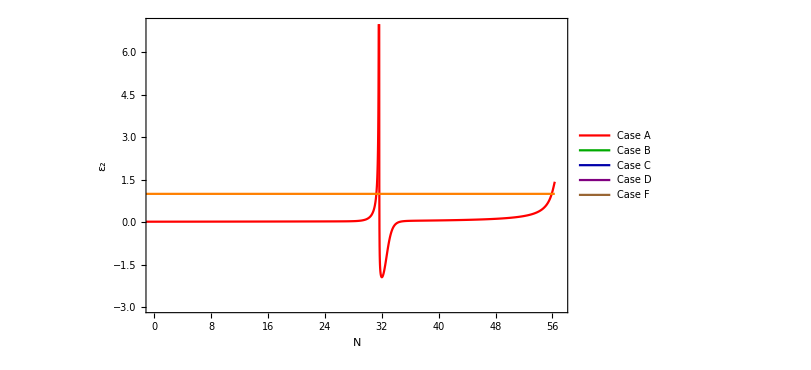
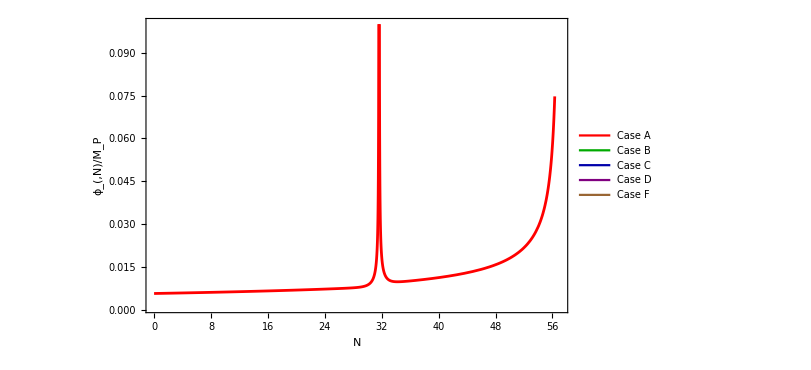
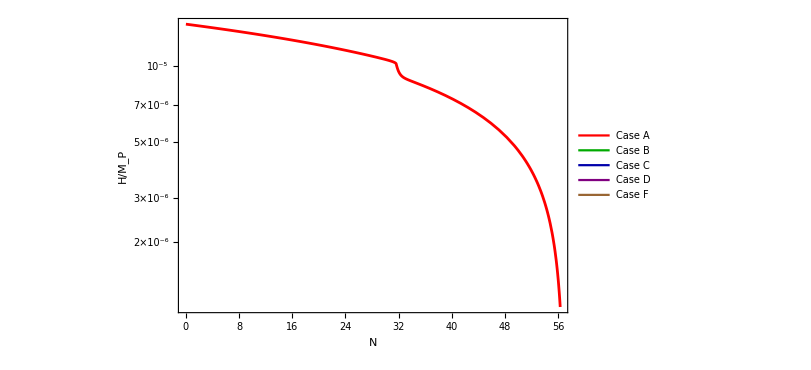
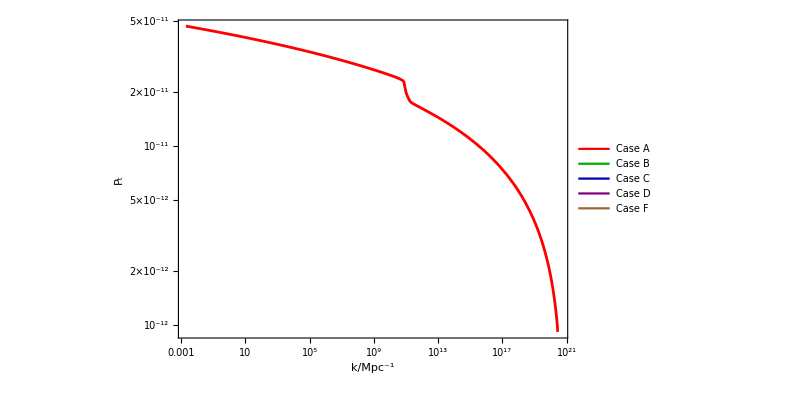
```mathematica
p1=-Graphics-;
e1=-Graphics-;
t1=-Graphics-;
c1=-Graphics-;
eta1=-Graphics-;
dphi1=-Graphics-;
h1=-Graphics-;
pt1=-Graphics-;

p2=-Graphics-;
e2=-Graphics-;
t2=-Graphics-;
c2=-Graphics-;
eta2=-Graphics-;
dphi2=-Graphics-;
h2=-Graphics-;
pt2=-Graphics-;



p3=-Graphics-;
e3=-Graphics-;
t3=-Graphics-;
c3=-Graphics-;
eta3=-Graphics-;
dphi3=-Graphics-;
h3=-Graphics-;
pt3=-Graphics-;

p4=-Graphics-;
e4=-Graphics-;
t4=-Graphics-;
c4=-Graphics-;
eta4=-Graphics-;
dphi4=-Graphics-;
h4=-Graphics-;
pt4=-Graphics-;
p5=-Graphics-;
e5=-Graphics-;
t5=-Graphics-;
c5=-Graphics-;
eta5=-Graphics-;
dphi5=-Graphics-;
h5=-Graphics-;
pt5=-Graphics-;



phitotal=Show[p1,p2,p3,p4,p5(*,pImageSize->{600,400}*)]
e1total=Show[e1,e2,e3,e4,e5(*,pImageSize->{600,400}*)]
vtotal=Show[t1,t2,t3,t4,t5(*,pImageSize->{600,400}*)]
swampphi=Show[c1,c2,c3,c4,c5(*,pImageSize->{600,400}*)]
etatotal=Show[eta1,eta2,eta3,eta4,eta5(*,pImageSize->{600,400}*)]
dphitotal=Show[dphi1,dphi2,dphi3,dphi4,dphi5(*,pImageSize->{600,400}*)]
h=Show[h1,h2,h3,h4,h5(*,pImageSize->{600,400}*)]
pt=Show[pt1,pt2,pt3,pt4,pt5]
```

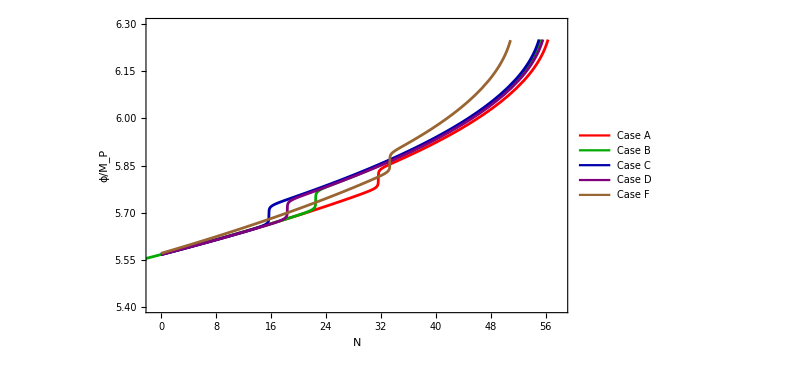

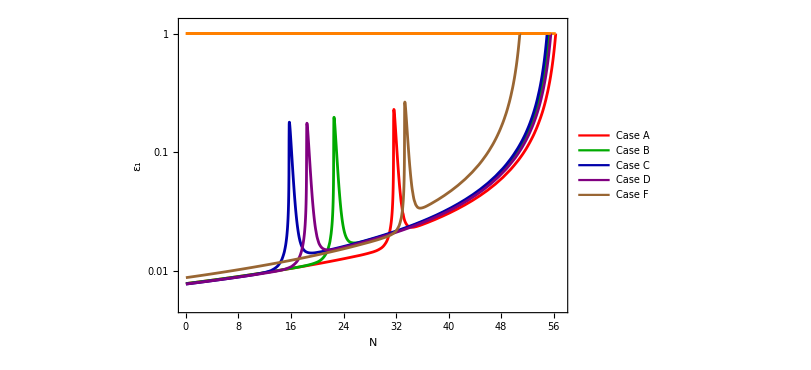

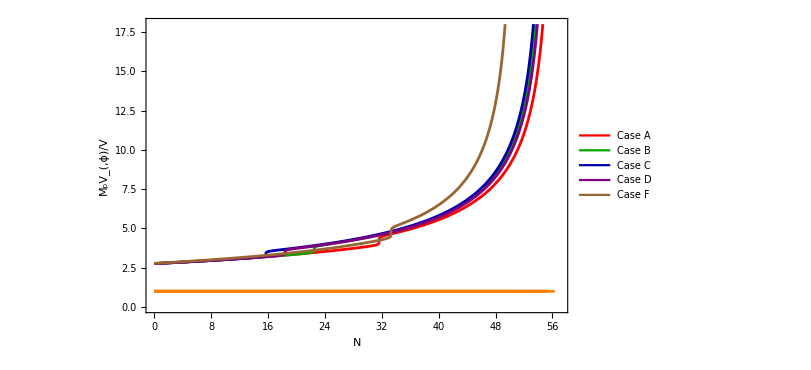

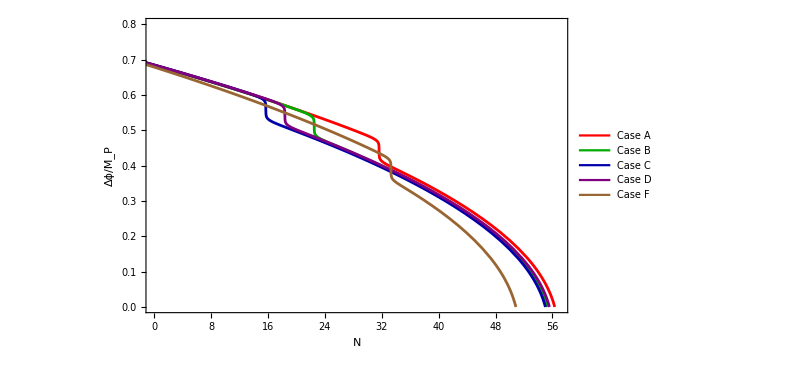

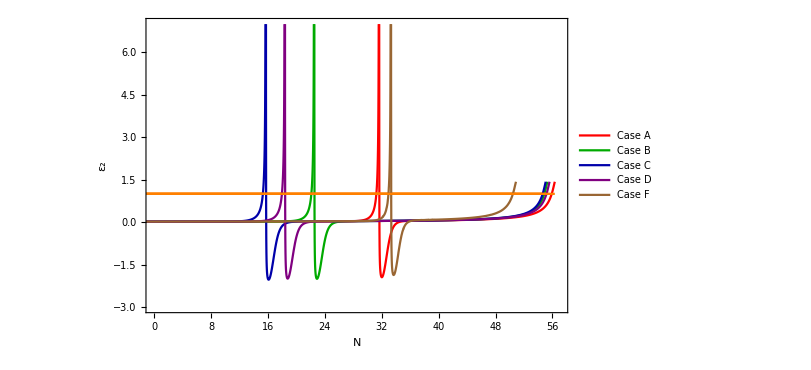

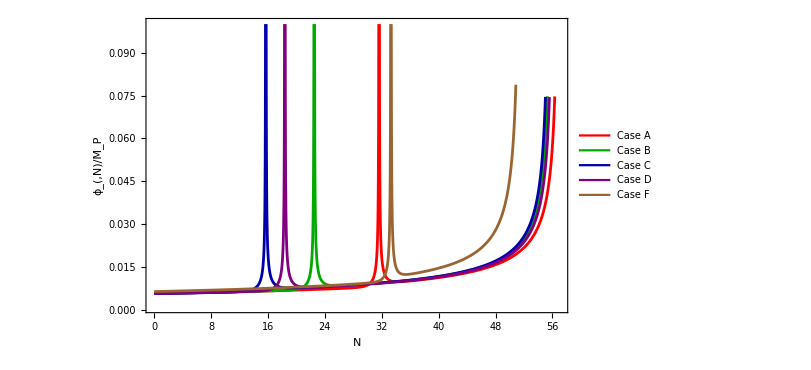

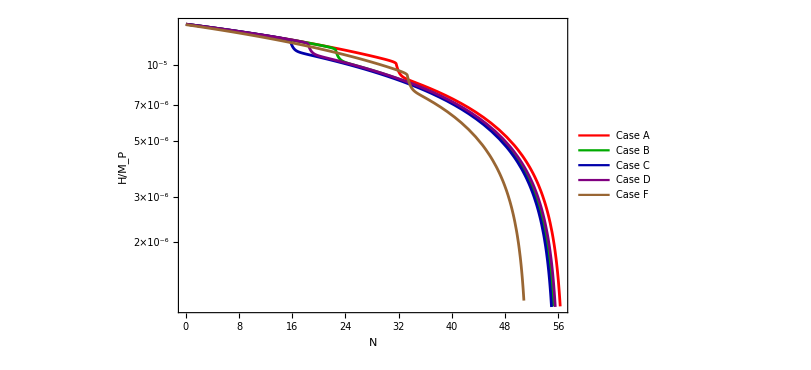

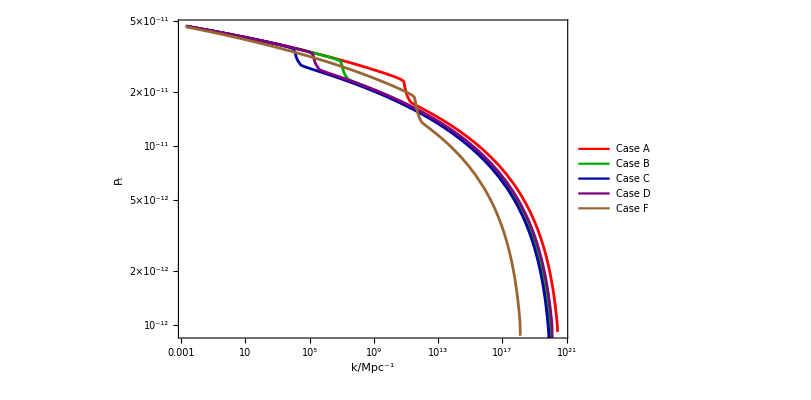

```mathematica
Export["epsilon1.eps",e1total];
Export["epsilon2.eps",etatotal];
Export["dphi.eps",dphitotal];
Export["phi.eps",phitotal];
Export["gradianV.eps",vtotal];
Export["fildswampland.eps",swampphi];
Export["h.eps",h];
Export["pt.eps",pt];
```